# Geometry and RAA

```mathematica
NotebookDirectory[]
```

/Users/antoniagrindrod/Documents/UCT2022/PHY4000W/Honours Project/2. Elastic/Mathematica/

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"f.dat"}],f]
```

Cole' s Trick to change the default value of Heaviside

```mathematica
$Assumptions=HeavisideTheta[0]==1&&HeavisideTheta[0.]==1
```

HeavisideTheta[0]==1&&HeavisideTheta[0.]==1

Then need to change integration to full simplify

```mathematica
fmToGev = 5.068;
aS=0.3;
cR=4/3;
cA=3;
temp=0.25;
mC=1.5;
mB=4.75;
mu=0.5;
mG=mu/Sqrt[2];
lambda=5.068;
nF=2;
```

Some general changes I made to previous code, following Cole' s implementation :
Changed many function definitions so that they didn' t store calculated values: meanGluonCorrection, rho, pRadTableExpIn

# Radiative Energy Loss

Program to perform convolution of radiative and elastic energy loss as a function of energy and path length. Corrected (DGLV) and uncorrected (Isobel) cases achieved by passing 1, or 0 as corrCoeff parameter.

```mathematica
ClearAll["Global'*"]
```

```mathematica
ClearAll[energyIntegrateCorrection,meanGluonCorrection,rho]
```

```mathematica
(*Function energyIntegrateCorrection isn't used in RAAGeom calculations*)energyIntegrateCorrection[energy_?NumericQ,cR_?NumericQ, cA_?NumericQ, mu_?NumericQ, aS_?NumericQ,l_?NumericQ, lambda_?NumericQ, mG_?NumericQ, m_?NumericQ,corrCoeff_?NumericQ]:=energyIntegrateCorrection[energy,cR, cA, mu, aS,l, lambda, mG, m,corrCoeff]=NIntegrate[2 ((cR aS  l)/(π lambda))  k  (q ( mu^2))/(π(q^2+mu^2)^2)(-2/(k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2) (1-4/l^2(((k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2)/(2 x energy))^2+4/l^2)^-1) ((k^2- k q Cos[theta])/(k^2+m^2 x^2+mG^2)-(k^2-2 k q Cos[theta]+q^2)/(k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2))+corrCoeff 1/l( k^2/((k^2+m^2 x^2+mG^2)^2) (1-(2cR)/cA) (1/(2/l+Sqrt[mu^2+q^2])-(2/l+Sqrt[mu^2+q^2])/(((k^2+m^2 x^2+mG^2)/(2x energy))^2+(2/l+Sqrt[mu^2+q^2])^2))+(k^2-k q Cos[theta])/((k^2+m^2 x^2+mG^2)(k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2))((2/l+Sqrt[mu^2+q^2])/(((k^2+m^2 x^2+mG^2)/(2x energy))^2+(2/l+Sqrt[mu^2+q^2])^2)- (2/l+Sqrt[mu^2+q^2])/(((2 k q Cos[theta]-q^2)/(2x energy))^2+(2/l+Sqrt[mu^2+q^2])^2)))),{x,0,1},{theta,0,2 π},{k,0,2x (1-x) energy},{q,0,Sqrt[3 energy mu]},PrecisionGoal->3,AccuracyGoal->6]

(*Below used to store function values*)
meanGluonCorrection[energy_?NumericQ,cR_?NumericQ, cA_?NumericQ, mu_?NumericQ, aS_?NumericQ,l_?NumericQ, lambda_?NumericQ, mG_?NumericQ, m_?NumericQ,corrCoeff_?NumericQ]:=NIntegrate[1/x 2 ((cR aS  l)/(π lambda))  k  (q ( mu^2))/(π(q^2+mu^2)^2)(-2/(k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2) (1-4/l^2(((k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2)/(2 x energy))^2+4/l^2)^-1) ((k^2- k q Cos[theta])/(k^2+m^2 x^2+mG^2)-(k^2-2 k q Cos[theta]+q^2)/(k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2))+corrCoeff 1/l( k^2/((k^2+m^2 x^2+mG^2)^2) (1-(2cR)/cA) (1/(2/l+Sqrt[mu^2+q^2])-(2/l+Sqrt[mu^2+q^2])/(((k^2+m^2 x^2+mG^2)/(2x energy))^2+(2/l+Sqrt[mu^2+q^2])^2))+(k^2-k q Cos[theta])/((k^2+m^2 x^2+mG^2)(k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2))((2/l+Sqrt[mu^2+q^2])/(((k^2+m^2 x^2+mG^2)/(2x energy))^2+(2/l+Sqrt[mu^2+q^2])^2)- (2/l+Sqrt[mu^2+q^2])/(((2 k q Cos[theta]-q^2)/(2x energy))^2+(2/l+Sqrt[mu^2+q^2])^2)))),{x,0,1},{theta,0,2 π},{k,0,2x (1-x) energy},{q,0,Sqrt[3 energy mu]},PrecisionGoal->3,AccuracyGoal->6]
```

#### Trial

Try timing with the method

```mathematica
AbsoluteTiming[Table[meanGluonCorrection[energy,cR, cA, mu, aS,4*5.068, lambda, mG, mC,1],{energy,10,100,10}]]
```

{20.8139,{0.932222,1.14852,1.20463,1.21974,1.22026,1.2152,1.20751,1.19887,1.1898,1.18063}}

Try timing without the method

```mathematica
AbsoluteTiming[Table[meanGluonCorrection[energy,cR, cA, mu, aS,4*5.068, lambda, mG, mC,1],{energy,10,100,10}]]
```

{29.6676,{0.932245,1.1485,1.2046,1.21951,1.22031,1.21532,1.20748,1.199,1.18972,1.1806}}

The method does make it roughly 50 % faster

## No correction

### ρ(ε)

```mathematica
(*Below used to store function values*)
```

```mathematica
rho[x_?NumericQ,energy_?NumericQ,cR_?NumericQ, cA_?NumericQ, mu_?NumericQ, aS_?NumericQ,l_?NumericQ, lambda_?NumericQ, mG_?NumericQ, m_?NumericQ,corrCoeff_?NumericQ]:= NIntegrate[1/x 2 ((cR aS  l)/(π lambda))  k  (q ( mu^2))/(π(q^2+mu^2)^2)(-2/(k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2) (1-4/l^2(((k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2)/(2 x energy))^2+4/l^2)^-1) ((k^2- k q Cos[theta])/(k^2+m^2 x^2+mG^2)-(k^2-2 k q Cos[theta]+q^2)/(k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2))+corrCoeff 1/l( k^2/((k^2+m^2 x^2+mG^2)^2) (1-(2cR)/cA) (1/(2/l+Sqrt[mu^2+q^2])-(2/l+Sqrt[mu^2+q^2])/(((k^2+m^2 x^2+mG^2)/(2x energy))^2+(2/l+Sqrt[mu^2+q^2])^2))+(k^2-k q Cos[theta])/((k^2+m^2 x^2+mG^2)(k^2-2 k q Cos[theta]+q^2+m^2 x^2+mG^2))((2/l+Sqrt[mu^2+q^2])/(((k^2+m^2 x^2+mG^2)/(2x energy))^2+(2/l+Sqrt[mu^2+q^2])^2)- (2/l+Sqrt[mu^2+q^2])/(((2 k q Cos[theta]-q^2)/(2x energy))^2+(2/l+Sqrt[mu^2+q^2])^2)))),{theta,0,2 π},{k,0,2x (1-x) energy},{q,0,Sqrt[3 energy mu]},PrecisionGoal->3,AccuracyGoal->6]
```

### Radiative Poisson Convolution

Instead of defining a function for each P_nwhich can access P_n for an individual n (like used to have), define a function which returns only a lust if significantly contributing P_nfor given parameters.
We use Poisson convolution to obtain a probability distribution for radiative energy loss.
Approximation in defining P_nto evaluate using P_(n-1) on the [0,1] subset of the domain (produces same results as evaluating on whole domain)
Variable pRadCon with last argument n corresponds to P_nof radiative convolution.

#### Trials

```mathematica
trialModule[x_,y_]:=Module[{xInterp,yInterp},xInterp=Interpolation[ParallelTable[{i,x*i},{i,1,10}]];yInterp = Interpolation[ParallelTable[xInterp[i]+y,{i,1,10}]];
Return[yInterp]]
```

```mathematica
trialModule[2,4]
```

InterpolatingFunction[…]

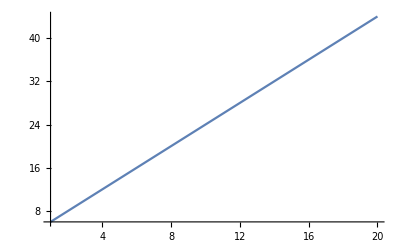

```mathematica
Plot[trialModule[2,4][x],{x,1,20}]
```

```mathematica
(*From the above can see that may use parallel in a kind of nested way as long as don't directly call parallel table within a parallel table*)
```

```mathematica
(*Timing for calling 1) a variable, versus 2) an indexed element in a variable which is a table, versus 3)a stored function value. Most to least efficient: 1),3),2) *)
```

```mathematica
trial =4
trialTable = {4}
```

```mathematica
trialFn[x_]:=trialFn[x] =4
```

```mathematica
AbsoluteTiming[trial]
```

{0.,4}

```mathematica
AbsoluteTiming[trialTable[[1]]]
```

{4.×10^-6,4}

```mathematica
AbsoluteTiming[trialFn[1]]
```

{2.×10^-6,4}

#### Actual Function

```mathematica
ClearAll[pRadTableExpIn]
```

```mathematica
(*Below used to store function values*)
```

```mathematica
pRadTableExpIn[expMean_?NumericQ,energy_?NumericQ,cR_?NumericQ, cA_?NumericQ, mu_?NumericQ, aS_?NumericQ,l_?NumericQ, lambda_?NumericQ, mG_?NumericQ, m_?NumericQ,corrCoeff_?NumericQ]:=Module[{interpRho,pRadTable,pRad,nPRad=1,allPrevPInt,pCurrentInt},
interpRho=Interpolation[ParallelTable[{x,rho[x,energy,cR, cA, mu, aS,l, lambda, mG, m,corrCoeff]},{x,0,1,0.001}]];
pRad[1]:=interpRho;
(*didn't store function value pRad[1] because the variable interpRho is already stored*)
pRad[n_]:=pRad[n]=Interpolation[ParallelTable[{epsilon,1/n NIntegrate[interpRho[x] pRad[n-1][epsilon-x],{x,Max[epsilon-1,0],Min[epsilon,1]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"]},{epsilon,0,1,0.01}]];
(*Below, took out a heaviside in the Integration because integration bounds didn't go outside of the Heaviside*)
allPrevPInt=NIntegrate[expMean* interpRho[x],{x,0,1},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"];
pCurrentInt=NIntegrate[expMean* pRad[2][x],{x,0,1},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"];
While[pCurrentInt/allPrevPInt>0.001,
allPrevPInt=allPrevPInt+pCurrentInt;pCurrentInt=NIntegrate[expMean *pRad[nPRad+1][x],{x,0,1},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"];
;
nPRad=nPRad+1
];
pRadTable = ParallelTable[pRad[j],{j,1,nPRad}];
Return[pRadTable]
]
```

Determine when can stop convolving by checking ratio of the integrals of current P_n and of sum of previous P_n. Achieved this using a while loop to determine P_n until obtain nPRad which meets the condition.
Condition terminates the loop when the  next P_n contribution is deemed negligible - ie that next contribution is not included
We take reasonable ratio to be 0.01

#### Trying it out

```mathematica
expTry=Exp[-meanGluonCorrection[20,4/3, 3, 0.5, 0.3,4* 5.068,1* 5.068,0.5/Sqrt[2],1.5,1]]
Timing[pRadTableExpIn[expTry,20,4/3, 3, 0.5, 0.3,4* 5.068,1* 5.068,0.5/Sqrt[2],1.5,1]]
```

0.317104

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.280278,{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

```mathematica
expTry=Exp[-meanGluonCorrection[10,4/3, 3, 0.5, 0.3,4* 5.068,1* 5.068,0.5/Sqrt[2],1.5,1]]
Timing[pRadTableExpIn[expTry,10,4/3, 3, 0.5, 0.3,4* 5.068,1* 5.068,0.5/Sqrt[2],1.5,1]]
```

0.393678

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{0.266144,{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

# Convolution with Elastic

None of the Elastic Function values needed to be stored because they each get called only once explicitly in the PTotLInterp Function (remember to change pTotLInterp to be only one function i.e. in terms of a general energy loss function).

```mathematica
ClearAll[energyLossLowP8UsingMCI, energyLossHighP12UsingMCI]
```

```mathematica
v = {{0,0.604}, {0.88, 0.731}, {1, 0.629}};

monotonicCubicInterpolation = ResourceFunction["CubicMonotonicInterpolation"][v];
p1 = Plot[monotonicCubicInterpolation[v], {v,0,1}, PlotStyle->{Thin, Red}];
p2 = ListPlot[v];
```

```mathematica
energyLossLowP8UsingMCI[aS_?NumericQ, t_?NumericQ, nF_?NumericQ, p_?NumericQ,mQ_?NumericQ]:=
8/3 π aS^2 t^2 (1+nF/6) (1/Sqrt[p^2/(mQ^2+p^2)]-(1-Sqrt[p^2/(mQ^2+p^2)]^2)/(2 Sqrt[p^2/(mQ^2+p^2)]^2) Log[(1+Sqrt[p^2/(mQ^2+p^2)])/(1-Sqrt[p^2/(mQ^2+p^2)])]) Log[2^(nF/(6+nF)) monotonicCubicInterpolation[Sqrt[p^2/(mQ^2+p^2)]^2] Sqrt[p^2+mQ^2] t/(((t Sqrt[4 π aS])/Sqrt[3])(1+nF/6)^(1/2) mQ)]
energyLossHighP12UsingMCI[aS_?NumericQ, t_?NumericQ, nF_?NumericQ, p_?NumericQ,mQ_?NumericQ]:=
8/3 π aS^2 t^2 (1+nF/6) Log[2^(nF/(2(6+nF)))0.920 Sqrt[Sqrt[p^2+mQ^2] t]/(((Sqrt[4 π aS] t)/Sqrt[3])(1+nF/6)^(1/2))]
```

Solve for point at which switch from low to high energy (this is the point at which the two functions are equal) and create general energy loss function that reduces to high energy loss if input p (we have been giving E ~ p) higher than this point and low energy loss if lower

```mathematica
ClearAll[probabilityElasticEpsilon,energyLoss]
```

```mathematica
energyLoss[aS_?NumericQ, t_?NumericQ, nF_?NumericQ, p_?NumericQ,mQ_?NumericQ]:=Module[{crossOverEnergy},crossOverEnergy= x/.FindRoot[energyLossLowP8UsingMCI[aS, t, nF, x,mQ]-energyLossHighP12UsingMCI[aS, t, nF, x,mQ]==0,{x,16}, AccuracyGoal->6, PrecisionGoal-> 3];
Return[energyLossLowP8UsingMCI[aS, t, nF, p,mQ]*HeavisideTheta[crossOverEnergy-p]+energyLossHighP12UsingMCI[aS, t, nF, p,mQ]*HeavisideTheta[p-crossOverEnergy]]]
```

```mathematica
getElastic[pI_?NumericQ, l_?NumericQ, aS_?NumericQ, t_?NumericQ, nF_?NumericQ,mQ_?NumericQ]:=Module[{elasticCentre,elasticWidth},
elasticCentre=l/pI energyLoss[aS, t, nF, pI,mQ];elasticWidth=2/pI^2 energyLoss[aS, t, nF, pI,mQ] t l;
Return[{elasticCentre,elasticWidth,Function[{eps},1/(Sqrt[2π] elasticWidth)Exp[-1/2 1/elasticWidth^2 (-eps+elasticCentre)^2]]}]]
```

### Example Elastic Output

{{0.01,-0.0000728795},{0.02,-0.000145754},{0.03,-0.000218619},{0.04,-0.000291468},{0.05,-0.000364298},{0.06,-0.000437103},19988,{199.95,0.465656},{199.96,0.46566},{199.97,0.465664},{199.98,0.465667},{199.99,0.465671},{200.,0.465674}}
 |  |  |  |

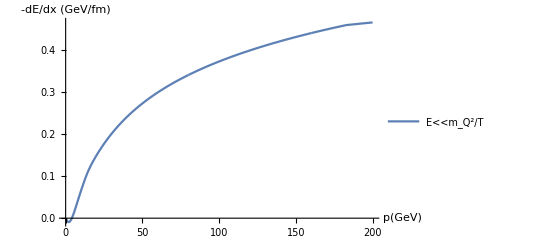

```mathematica
lowPBottom =Table[{p, 5.068  energyLoss[0.2,0.25, 2, p, 5]}, {p, 0.01,200,0.01}]
ListPlot[lowPBottom,AxesLabel->{"p(GeV)", "-dE/dx (GeV/fm)"},PlotLegends->Placed[{"E<<m_Q^2/T","E>>m_Q^2/T" },{0.75,0.4}],Joined->True]
```

General::munfl: Exp[-2048.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2047.21] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2046.42] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

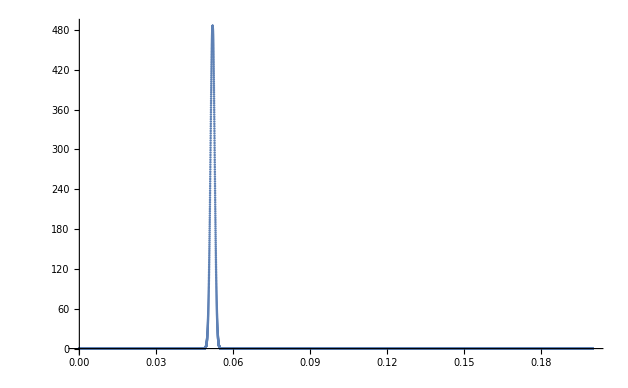

```mathematica
probabilityEpsilon = Table[{eps,  probabilityElasticEpsilon[32,5 fmToGev, 0.2,0.25, 2, 1.5][eps]}, {eps,0, 0.2,0.00001}];
ListPlot[{probabilityEpsilon},PlotRange->All]
```

General::munfl: Exp[-2450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2448.99] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2447.98] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

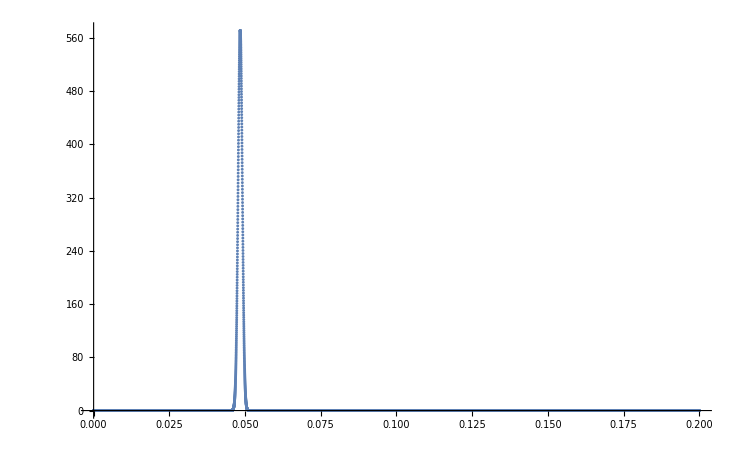

```mathematica
probabilityEpsilon2 = Table[{eps,  probabilityElasticEpsilon[35,5 fmToGev, 0.2,0.25, 2, 1.5][eps]}, {eps,0, 0.2,0.00001}];
ListPlot[{probabilityEpsilon2},PlotRange->All]
```

General::munfl: Exp[-2450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2448.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2446.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

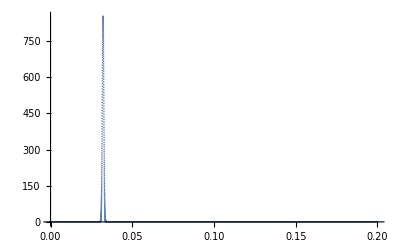

```mathematica
probabilityEpsilonBottom = Table[{eps,  probabilityElasticEpsilon[35,5 fmToGev, 0.2,0.25, 2, mB][eps]}, {eps,0, 0.2,0.00001}];
ListPlot[{probabilityEpsilonBottom},PlotRange->All]
```

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72143.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72087.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

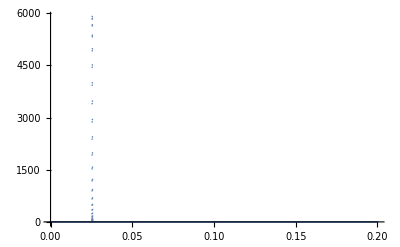

```mathematica
probabilityEpsilonBottom2 = Table[{eps,  probabilityElasticEpsilon[190,5 fmToGev, aS,0.25, 2, mB][eps]}, {eps,0, 0.2,0.00001}];
ListPlot[{probabilityEpsilonBottom2},PlotRange->All]
```

General::munfl: Exp[-3407.69] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3407.57] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3407.44] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

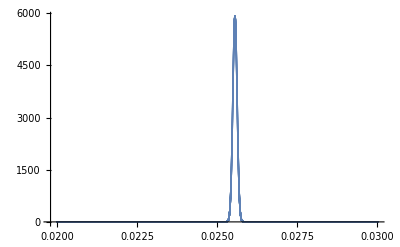

```mathematica
probabilityEpsilonBottom3 = Table[{eps,  probabilityElasticEpsilon[190,5 fmToGev, aS,0.25, 2, mB][eps]}, {eps,0.02, 0.03,0.0000001}];
ListPlot[{probabilityEpsilonBottom3},PlotRange->All]
```

### PTot Interpolation over epsilon for given L

The function below finds pTot . The epsilon regions account for where pTot (epsilon) is highly peaked, which is around the gaussian . We need a finer step size to capture the detail for the function around that region, which is given by widthFactor *elasticWidth .  Also need to capture the detail in the region where there is the little bump into PTot after the gaussian, coming from the peak of the Prad . This is less fine and so we use step size widthFactor 2*elasticWidth (it is difficult to find the upper bound of this region so we add extra to make sure we don' t miss it .   Also note the actual convolution integral to obtain pTot at each epsilon is taken over the small region where those integrands are nonzero (corresponding to within intWidth times the width of the gaussian, shifted because of the argument of P_el in this convolution) otherwise mathematica misses this sharply peaked region .
    Optimal arguments for widthFactor, widthFactor2, intWidth and extra are found by playing around .

```mathematica
pTotLTable4[intWidth_?NumericQ,temp_?NumericQ,l_?NumericQ,energy_?NumericQ,cR_?NumericQ, cA_?NumericQ, mu_?NumericQ, aS_?NumericQ, lambda_?NumericQ, mG_?NumericQ, m_?NumericQ,corrCoeff_?NumericQ,  nF_?NumericQ,lowerFactor_?NumericQ,upperFactor_?NumericQ,widthFactor_?NumericQ,widthFactor2_?NumericQ,extra_?NumericQ]:=Module[{intFn,elasticWidth1,elasticCentre1,expMean1,probabilityElastic1,pTotTable,pRadsTable},
{elasticCentre1,elasticWidth1,probabilityElastic1}=getElastic[Sqrt[energy^2-m^2],  l, aS, temp, nF,m];
expMean1= Exp[-meanGluonCorrection[energy,cR, cA, mu, aS, l, lambda, mG,m,corrCoeff]];
pRadsTable= pRadTableExpIn[expMean1,energy,cR, cA, mu, aS,l, lambda, mG, m,corrCoeff];

intFn[eps_]:=NIntegrate[probabilityElastic1[eps-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,Max[0,-elasticCentre1-intWidth*elasticWidth1+eps],Min[1,-elasticCentre1+intWidth*elasticWidth1+eps]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"];

pTotTable=Join[Parallelize[Table[{eps,intFn[eps]+ expMean1*probabilityElastic1[eps]},{eps,0,elasticCentre1-lowerFactor *elasticWidth1-0.01,0.01}]],Parallelize[Table[{eps,intFn[eps]+ expMean1*probabilityElastic1[eps]},{eps,elasticCentre1-lowerFactor *elasticWidth1,elasticCentre1+upperFactor *elasticWidth1,widthFactor*elasticWidth1}]],Parallelize[Table[{eps,intFn[eps]+ expMean1*probabilityElastic1[eps]},{eps,elasticCentre1+upperFactor *elasticWidth1+widthFactor2* elasticWidth1,elasticCentre1+upperFactor* elasticWidth1+extra,widthFactor2* elasticWidth1}]],Parallelize[Table[{eps,intFn[eps]+ expMean1*probabilityElastic1[eps]},{eps,elasticCentre1+upperFactor *elasticWidth1+extra+0.01,1,0.01}]]];Return[pTotTable]
]
```

```mathematica
pTotInterpMaxL4[intWidth_?NumericQ,temp_?NumericQ,l_?NumericQ,energy_?NumericQ,cR_?NumericQ, cA_?NumericQ, mu_?NumericQ, aS_?NumericQ, lambda_?NumericQ, mG_?NumericQ, m_?NumericQ,corrCoeff_?NumericQ,  nF_?NumericQ,lowerFactor_?NumericQ,upperFactor_?NumericQ,widthFactor_?NumericQ,widthFactor2_?NumericQ,extra_?NumericQ]:=pTotInterpMaxL4[intWidth,temp,l,energy,cR, cA, mu, aS, lambda, mG, m,corrCoeff,  nF,lowerFactor,upperFactor,widthFactor,widthFactor2,extra] =Interpolation[pTotLTable4[intWidth,temp,l,energy,cR, cA, mu, aS, lambda, mG, m,corrCoeff,  nF,lowerFactor,upperFactor,widthFactor,widthFactor2,extra]]
```

### Simple RAA (For fixed L)

```mathematica
rAAPTotInRec[pTot_]:=rAAPTotInRec[pTot]=NIntegrate [FullSimplify[pTot[epsi]*HeavisideTheta[1-epsi]*(1-epsi)^5],{epsi,0,1},Method->"InterpolationPointsSubdivision",MinRecursion->20,MaxRecursion->50]
```

#### Output

Charm

```mathematica
AbsoluteTiming[pTotUncorrCharm10to200=Parallelize[Table[pTotInterpMaxL4[10,0.25, 5*5.068,energy,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,0, 2,10,10,0.1,0.5,0.1],{energy,10,200,10}]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.99753 and 0.00210665 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.02517 and 0.00248056 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-719.027] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-754.755] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-791.349] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-3195.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2531.29] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1944.37] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-9795.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6723.32] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4227.53] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.00933 and 0.00209821 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-19995.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11882.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5868.68] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.0302 and 0.00274896 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03825 and 0.00318423 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.01818 and 0.00230689 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03461 and 0.00306454 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04361 and 0.0034404 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-33795.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-17312.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6291.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04738 and 0.00361645 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04083 and 0.00316924 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.05071 and 0.00334213 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-44995.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-20803.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5829.29] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04471 and 0.00342344 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-57795.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24032.6] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04969 and 0.00350022 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-72195.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26887.4] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.05173 and 0.00337516 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

{1333.11,{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

```mathematica
AbsoluteTiming[rAAUncorrCharm10to200Rec=Parallelize[Table[{10*i,rAAPTotInRec[pTotUncorrCharm10to200[[i]]]},{i,1,Length[pTotUncorrCharm10to200]}]]]
```

{106.434,{{10,0.144541},{20,0.199184},{30,0.271241},{40,0.330229},{50,0.380369},{60,0.421996},{70,0.458754},{80,0.490948},{90,0.51934},{100,0.54464},{110,0.567809},{120,0.589164},{130,0.606947},{140,0.624363},{150,0.639816},{160,0.654278},{170,0.666328},{180,0.677151},{190,0.687622},{200,0.696766}}}

```mathematica
rAAUncorrCharm10to200Rec={{10,0.14454124537808904},{20,0.19918363165157654},{30,0.2712412215638456},{40,0.33022904957110005},{50,0.380368947603362},{60,0.42199592905593564},{70,0.45875407943456287},{80,0.49094817983588385},{90,0.5193400249669284},{100,0.5446403450917523},{110,0.5678091712790371},{120,0.5891635045602089},{130,0.6069465646026144},{140,0.6243628898192304},{150,0.6398159155200356},{160,0.6542781101916451},{170,0.6663279721520488},{180,0.6771508341084068},{190,0.6876220294684746},{200,0.6967658621696389}}
```

{{10,0.144541},{20,0.199184},{30,0.271241},{40,0.330229},{50,0.380369},{60,0.421996},{70,0.458754},{80,0.490948},{90,0.51934},{100,0.54464},{110,0.567809},{120,0.589164},{130,0.606947},{140,0.624363},{150,0.639816},{160,0.654278},{170,0.666328},{180,0.677151},{190,0.687622},{200,0.696766}}

```mathematica
AbsoluteTiming[pTotCorrCharm10to200=Parallelize[Table[pTotInterpMaxL4[10,0.25, 5*5.068,energy,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,1, 2,10,10,0.1,0.5,0.1],{energy,10,200,10}]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.76508 and 0.00212457 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.74699 and 0.00237292 for the integral and error estimates.

Power::infy: Infinite expression 1/0. encountered.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-719.027] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-754.755] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-791.349] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-3195.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2531.29] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1944.37] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-9795.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6723.32] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4227.53] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.76039 and 0.00215271 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.725 and 0.00280904 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-19995.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11882.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5868.68] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.73967 and 0.00250621 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00172646 and 1.76194×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00031196 and 1.74012×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00123868 and 1.3184×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.70668 and 0.00291665 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000698269 and 0.0000104679 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00135687 and 2.26087×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-33795.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-17312.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6291.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.75405 and 0.00238878 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-44995.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-20803.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5829.29] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.69523 and 0.0029505 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00117144 and 6.3849×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.68203 and 0.00312486 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00165829 and 2.89481×10^-6 for the integral and error estimates.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00142115 and 3.61876×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00228861 and 3.63343×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-57795.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24032.6] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-72195.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26887.4] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

{2273.7,{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

```mathematica
AbsoluteTiming[rAACorrCharm10to200Rec=Parallelize[Table[{10*i,rAAPTotInRec[pTotCorrCharm10to200[[i]]]},{i,1,Length[pTotCorrCharm10to200]}]]]
```

{111.194,{{10,0.150786},{20,0.214955},{30,0.299252},{40,0.369812},{50,0.430777},{60,0.48349},{70,0.530046},{80,0.571502},{90,0.608704},{100,0.643209},{110,0.673062},{120,0.701157},{130,0.726359},{140,0.749707},{150,0.774333},{160,0.792186},{170,0.809732},{180,0.825473},{190,0.840653},{200,0.854477}}}

Bottom

```mathematica
AbsoluteTiming[pTotUncorrBottom10to200=Parallelize[Table[pTotInterpMaxL4[10,0.25, 5*5.068,energy,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2],mB,0, 2,10,10,0.1,0.5,0.1],{energy,10,200,10}]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.98282 and 0.00216361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.125] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-3154.87] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2222.14] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1452.44] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-9754.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6136.59] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3353.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-19954.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11147.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4886.14] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.00055 and 0.00245042 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.02592 and 0.00253703 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.01473 and 0.00232939 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04232 and 0.00280002 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-33754.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-16696.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5580.59] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03447 and 0.00281165 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.05344 and 0.00317351 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.06129 and 0.00290981 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-44954.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-20466.5] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04847 and 0.00320523 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-57754.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24025.1] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.05758 and 0.0031523 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-72154.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26881.9] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.06484 and 0.00308709 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

{1130.85,{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

```mathematica
AbsoluteTiming[rAAUncorrBottom10to200Rec=Parallelize[Table[{10*i,rAAPTotInRec[pTotUncorrBottom10to200[[i]]]},{i,1,Length[pTotUncorrBottom10to200]}]]]
```

{130.594,{{10,0.617133},{20,0.463522},{30,0.45352},{40,0.463507},{50,0.480165},{60,0.498208},{70,0.516007},{80,0.535393},{90,0.552804},{100,0.570318},{110,0.585486},{120,0.600296},{130,0.614223},{140,0.627547},{150,0.639662},{160,0.650917},{170,0.661284},{180,0.671541},{190,0.681444},{200,0.688594}}}

```mathematica
AbsoluteTiming[pTotCorrBottom10to200=Parallelize[Table[pTotInterpMaxL4[10,0.25, 5*5.068,energy,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], mB,1, 2,10,10,0.1,0.5,0.1],{energy,10,200,10}]]]
```

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.70922 and 0.00215798 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.125] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-3154.87] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2222.14] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1452.44] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-9754.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6136.59] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3353.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-19954.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11147.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4886.14] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.71391 and 0.00210488 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.71565 and 0.00219856 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.7008 and 0.00174935 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.71584 and 0.0022231 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-33754.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-16696.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5580.59] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.71164 and 0.00274193 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.71402 and 0.00235745 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00107827 and 4.57089×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000637533 and 1.4166×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00118749 and 1.18887×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.70403 and 0.00255137 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.69514 and 0.0025432 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000922717 and 2.76024×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00127566 and 1.83522×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000341111 and 2.28369×10^-6 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-44954.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-20466.5] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-57754.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24025.1] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-72154.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26881.9] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.69084 and 0.00276286 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

{1701.69,{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

```mathematica
AbsoluteTiming[rAACorrBottom10to200=Parallelize[Table[{10*i,rAAPTotInRec[pTotCorrBottom10to200[[i]]]},{i,1,Length[pTotCorrBottom10to200]}]]]
```

{132.04,{{10,0.634619},{20,0.49355},{30,0.494439},{40,0.514574},{50,0.540206},{60,0.566897},{70,0.589334},{80,0.620161},{90,0.645011},{100,0.668931},{110,0.692002},{120,0.712884},{130,0.733031},{140,0.751947},{150,0.769417},{160,0.786848},{170,0.801269},{180,0.816699},{190,0.830692},{200,0.84283}}}

Note sure if I should Join or not . If do could probably do dashed and undashed for corrected and uncorrected . Then make sure coordinate colours with other plots

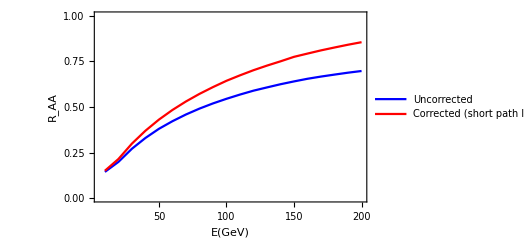

```mathematica
ListPlot[{rAAUncorrCharm10to200Rec,rAACorrCharm10to200Rec},PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{"Uncorrected","Corrected (short path length)" },LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.7,0.3}],FrameLabel->{{"R_AA",""},{"E(GeV)","Charm"}},PlotRange->{All,{0,1}},Frame->True,Joined->True]
```

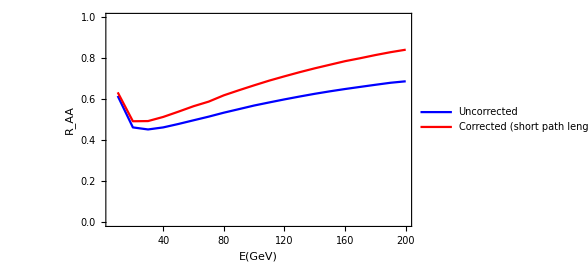

```mathematica
ListPlot[{rAAUncorrBottom10to200Rec,rAACorrBottom10to200},PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{"Uncorrected","Corrected (short path length)" },LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.7,0.3}],FrameLabel->{{"R_AA",""},{"E(GeV)","Bottom"}},PlotRange->{All,{0,1}},Frame->True,Joined->True]
```

#### Old Output

```mathematica
pTotUncorrCharm200=pTotInterpMaxL4[10,0.25, 5*5.068,200,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,0, 2,10,10,0.1,0.5,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.05173 and 0.00337516 for the integral and error estimates.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-79995.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-28145.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1326.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4278.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8911.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1352.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4324.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8978.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1378.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4371.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9045.12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-741.125] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15225.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23220.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-32896.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15312.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-23328.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-33024.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15400.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23436.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-33153.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44253.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-44402.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57291.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44551.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72010.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-88410.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57460.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-88620.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57630.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72390.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-88831.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-106491.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-106722.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-126253.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-106953.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-147696.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-170820.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-126504.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-147968.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-171113.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-126756.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-148240.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-171405.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-195313.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-195625.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-221445.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-195938.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-249218.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-278631.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-221778.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-249571.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-279004.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-222111.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-249925.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-279378.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-309685.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-310078.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-342378.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-310472.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-376712.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-412686.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-342792.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-377146.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-413140.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-343206.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-377581.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-413595.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-450301.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-450775.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-489555.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-451250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-530450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-572985.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-490050.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-530965.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-573521.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-490545.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-531480.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-574056.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-617161.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-617716.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-662976.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-618272.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710432.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-759528.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-663552.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-711028.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760145.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-664128.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711624.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760761.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-810264.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-810901.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-862641.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-811538.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-916658.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-972315.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-863298.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-917335.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-973013.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-863955.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-918012.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-973710.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.02961×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.03033×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.08855×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.03105×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.14913×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.21135×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.08929×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.14989×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.21212×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.09003×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.15064×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.2129×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.2752×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.276×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.2768×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.62008×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.81088×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.69649×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.62769×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.92624×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.32889×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.04264×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.72186×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.25889×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.87339×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.11827×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.81868×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.34251×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.18708×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.16141×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.26551×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.45522×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.31833×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.3112×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.43383×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.57057×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.45222×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.46363×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.6048×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-6.49936×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.86297×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.35634×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.09795×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.68622×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.06836×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.58027×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.12219×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.87572×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.27641×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.80685×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.14671×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

```mathematica
rAAUncorrCharm200=rAAPTotIn[pTotUncorrCharm200]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0258402}. NIntegrate obtained 0.598292 and 0.0145141 for the integral and error estimates.

0.598292

```mathematica
NIntegrate [pTotUncorrCharm200[epsi]*(1-epsi)^5,{epsi,0,1},AccuracyGoal->6, PrecisionGoal->3,Method->"InterpolationPointsSubdivision",MinRecursion->5,MaxRecursion->10]
```

0.583837

```mathematica
NIntegrate [pTotUncorrCharm200[epsi]*(1-epsi)^5,{epsi,0,1},AccuracyGoal->6, PrecisionGoal->3,Method->"InterpolationPointsSubdivision",MinRecursion->15,MaxRecursion->22]
```

0.696769

```mathematica
rAAPTot[pTot_]:=rAAPTot[pTot]=NIntegrate [FullSimplify[pTot[epsi]*HeavisideTheta[1-epsi]*(1-epsi)^5],{epsi,0,1}]
```

```mathematica
AbsoluteTiming[pTotUncorrCharm10to200=Parallelize[Table[pTotInterpMaxL4[10,0.25, 5*5.068,energy,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,0, 2,10,10,0.1,0.5,0.1],{energy,10,200,10}]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.99753 and 0.00210665 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.02517 and 0.00248056 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-719.027] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-754.755] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-791.349] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-3195.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2531.29] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1944.37] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-9795.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6723.32] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4227.53] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.00933 and 0.00209821 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-19995.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11882.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5868.68] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.0302 and 0.00274896 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03825 and 0.00318423 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.01818 and 0.00230689 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03461 and 0.00306454 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04361 and 0.0034404 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-33795.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-17312.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6291.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04738 and 0.00361645 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04083 and 0.00316924 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.05071 and 0.00334213 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-44995.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-20803.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5829.29] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04471 and 0.00342344 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-57795.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24032.6] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04969 and 0.00350022 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-72195.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26887.4] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.05173 and 0.00337516 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

{1333.11,{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

```mathematica
pTotUncorrCharm10to200={InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
rAAPTotIn[pTot_]:=rAAPTotIn[pTot]=NIntegrate [pTot[epsi]*(1-epsi)^5,{epsi,0,1},Method->"InterpolationPointsSubdivision"]
```

```mathematica
AbsoluteTiming[rAAUncorrCharm10to200=Parallelize[Table[{10*i,rAAPTotIn[pTotUncorrCharm10to200[[i]]]},{i,1,Length[pTotUncorrCharm10to200]}]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0447733}. NIntegrate obtained 0.544651 and 0.000377767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.040964}. NIntegrate obtained 0.567797 and 0.00260847 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0376805}. NIntegrate obtained 0.589164 and 0.0000342319 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.031525}. NIntegrate obtained 0.639826 and 0.000289208 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0287028}. NIntegrate obtained 0.665698 and 0.0674417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0356549}. NIntegrate obtained 0.60694 and 0.0177839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0478342}. NIntegrate obtained 0.51934 and 1.29005×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0272807}. NIntegrate obtained 0.673046 and 0.0490173 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0342898}. NIntegrate obtained 0.624277 and 0.00664968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0301162}. NIntegrate obtained 0.656805 and 0.0710132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0258516}. NIntegrate obtained 0.683987 and 0.0548972 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0258402}. NIntegrate obtained 0.598292 and 0.0145141 for the integral and error estimates.

{2.71676,{{10,0.144541},{20,0.199184},{30,0.271241},{40,0.330229},{50,0.380369},{60,0.421996},{70,0.458754},{80,0.490948},{90,0.51934},{100,0.544651},{110,0.567797},{120,0.589164},{130,0.60694},{140,0.624277},{150,0.639826},{160,0.656805},{170,0.665698},{180,0.673046},{190,0.683987},{200,0.598292}}}

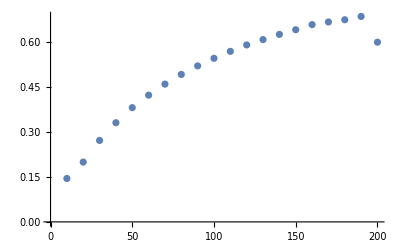

```mathematica
ListPlot[rAAUncorrCharm10to200]
```

```mathematica
rAAUncorrCharm10to200[[12]]
```

{120,0.589164}

```mathematica
rAAUncorrCharm10to200[[20]]
```

{200,0.598292}

```mathematica
AbsoluteTiming[rAAUncorrCharm10to200=Parallelize[Table[{10*i,rAAPTot[pTotUncorrCharm10to200[[i]]]},{i,1,Length[pTotUncorrCharm10to200]}]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0447733}. NIntegrate obtained 0.544651 and 0.000377767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.040964}. NIntegrate obtained 0.567797 and 0.00260847 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0376805}. NIntegrate obtained 0.589164 and 0.0000342319 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0356549}. NIntegrate obtained 0.60694 and 0.0177839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0342898}. NIntegrate obtained 0.624277 and 0.00664968 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.031525}. NIntegrate obtained 0.639826 and 0.000289208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0301162}. NIntegrate obtained 0.656805 and 0.0710132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0287028}. NIntegrate obtained 0.665698 and 0.0674417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0272807}. NIntegrate obtained 0.673046 and 0.0490173 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0258516}. NIntegrate obtained 0.683987 and 0.0548972 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0258402}. NIntegrate obtained 0.598292 and 0.0145141 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epsi near {epsi} = {0.0478342}. NIntegrate obtained 0.51934 and 1.29005×10^-6 for the integral and error estimates.

{2.52868,{{10,0.144541},{20,0.199184},{30,0.271241},{40,0.330229},{50,0.380369},{60,0.421996},{70,0.458754},{80,0.490948},{90,0.51934},{100,0.544651},{110,0.567797},{120,0.589164},{130,0.60694},{140,0.624277},{150,0.639826},{160,0.656805},{170,0.665698},{180,0.673046},{190,0.683987},{200,0.598292}}}

```mathematica
rAAPTotInRec[pTot_]:=rAAPTotInRec[pTot]=NIntegrate [FullSimplify[pTot[epsi]*HeavisideTheta[1-epsi]*(1-epsi)^5],{epsi,0,1},Method->"InterpolationPointsSubdivision",MinRecursion->20,MaxRecursion->50]
```

```mathematica
AbsoluteTiming[rAAUncorrCharm10to200Rec=Parallelize[Table[{10*i,rAAPTotInRec[pTotUncorrCharm10to200[[i]]]},{i,1,Length[pTotUncorrCharm10to200]}]]]
```

{106.434,{{10,0.144541},{20,0.199184},{30,0.271241},{40,0.330229},{50,0.380369},{60,0.421996},{70,0.458754},{80,0.490948},{90,0.51934},{100,0.54464},{110,0.567809},{120,0.589164},{130,0.606947},{140,0.624363},{150,0.639816},{160,0.654278},{170,0.666328},{180,0.677151},{190,0.687622},{200,0.696766}}}

```mathematica
rAAUncorrCharm10to200Old={{10,0.14518264303775202},{20,0.19959639274181787},{30,0.2714215704690818},{40,0.3303267949921527},{50,0.3804289619264853},{60,0.4220357036729572},{70,0.4587820508250258},{80,0.490968687959235},{90,0.5193557124084195},{100,0.5446524026091426},{110,0.5678200276242523},{120,0.5891712203308788},{130,0.6069503799680889},{140,0.6244849282477294},{150,0.6397017341414277},{160,0.6542756462902456},{170,0.6663295249627987},{180,0.6771546898857291},{190,0.6876119100066685},{200,0.6967768671769797}}
```

## Other Useful Plots

### PRadTot

Maybe Plot PRadTot on same axes

#### 10 GeV

```mathematica
expMeanUncorrCharm10= Exp[-meanGluonCorrection[10,cR, cA, mu, aS, 5 fmToGev, lambda, mG,mC,0]]
```

0.270123

```mathematica
pRadsUncorrCharm10= pRadTableExpIn[expMeanUncorrCharm10,10,cR, cA, mu, aS,5 fmToGev, lambda, mG, mC,0]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
pRadsUncorrCharm10={InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
pRadsUncorrCharm10[[1]]
```

InterpolatingFunction[…]

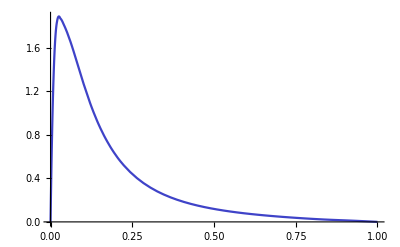
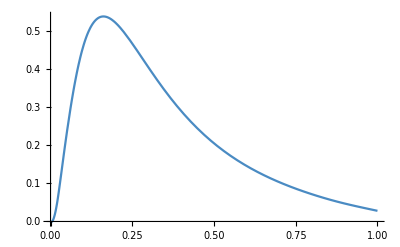
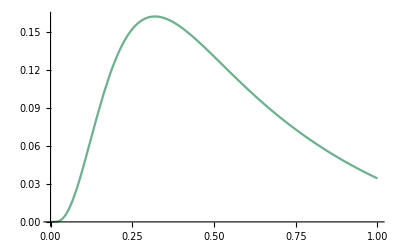
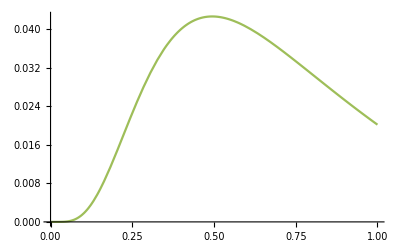
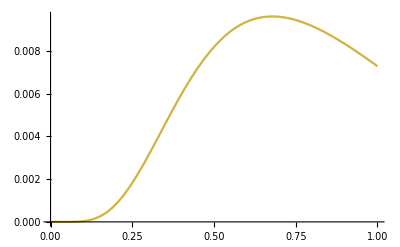
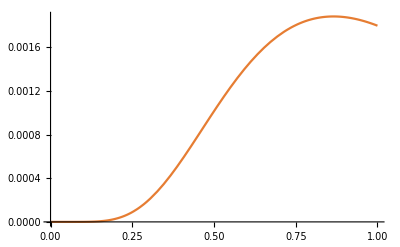
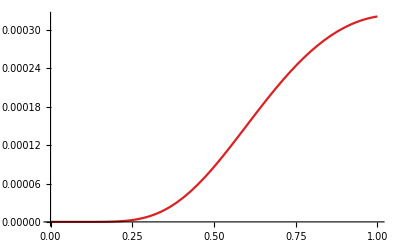

```mathematica
plotspRadUncorrCharm10=Table[Plot[expMeanUncorrCharm10*pRadsUncorrCharm10[[i]][x] HeavisideTheta[x] HeavisideTheta[1-x],{x,0, 1}, PlotRange->All,PlotStyle->ColorData["Rainbow",i/Length[pRadsUncorrCharm10]]],{i,1,Length[pRadsUncorrCharm10]}]
```

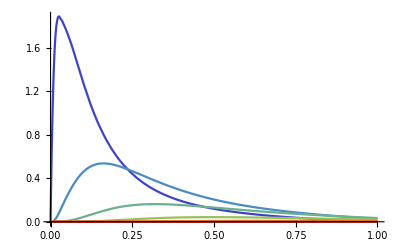

```mathematica
Show[plotspRadUncorrCharm10,PlotRange->{{0,1},All}]
```

#### 10 GeV

```mathematica
expMeanCorrCharm10= Exp[-meanGluonCorrection[10,cR, cA, mu, aS, 5 fmToGev, lambda, mG,mC,1]]
```

0.284533

```mathematica
pRadsCorrCharm10= pRadTableExpIn[expMeanCorrCharm10,10,cR, cA, mu, aS,5 fmToGev, lambda, mG, mC,1]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

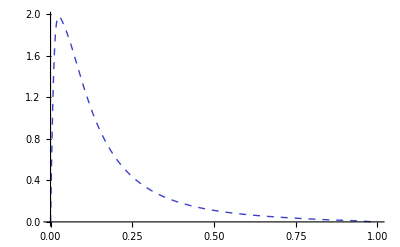
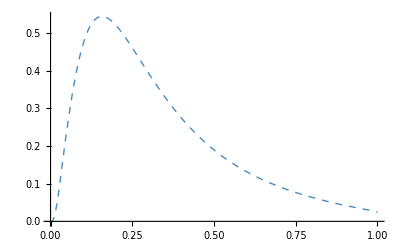
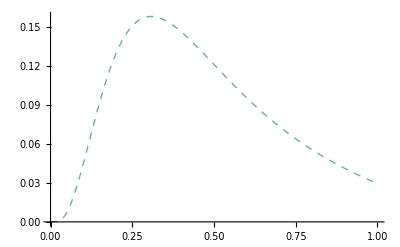
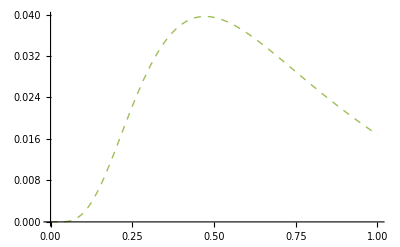
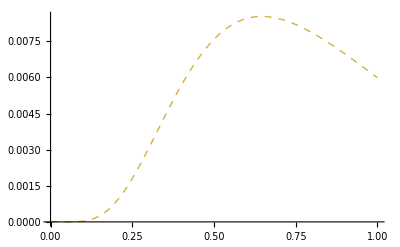
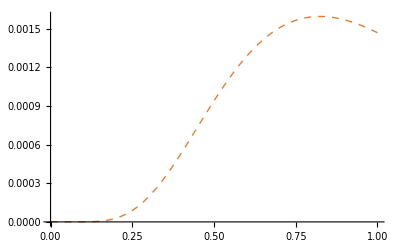

```mathematica
plotspRadCorrCharm10=Table[Plot[expMeanCorrCharm10*pRadsCorrCharm10[[i]][x] HeavisideTheta[x] HeavisideTheta[1-x],{x,0, 1}, PlotRange->All,PlotStyle->{ColorData["Rainbow",i/Length[pRadsUncorrCharm10]],Dashed,Thick}],{i,1,Length[pRadsCorrCharm10]}]
```

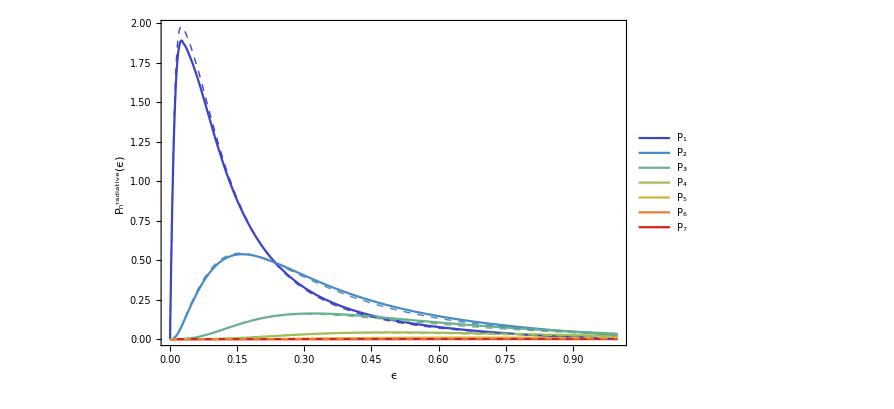

```mathematica
Show[plotspRadUncorrCharm10,plotspRadCorrCharm10,PlotRange->All,Epilog->Inset[LineLegend[Table[ColorData["Rainbow",j/Length[pRadsUncorrCharm10]],{j,1,Length[plotspRadUncorrCharm10]}],Table[Subscript[P, i],{i,1,Length[plotspRadUncorrCharm10]}],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.5,1}],FrameLabel->{{"P_n^radiative(ϵ)",""},{"ϵ","Charm 10GeV"}},Frame->True]
```

#### 150 GeV

```mathematica
expMeanUncorrCharm150= Exp[-meanGluonCorrection[150,cR, cA, mu, aS, 5 fmToGev, lambda, mG,mC,0]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04361 and 0.0034404 for the integral and error estimates.

0.129561

```mathematica
pRadsUncorrCharm150= pRadTableExpIn[expMeanUncorrCharm150,150,cR, cA, mu, aS,5 fmToGev, lambda, mG, mC,0]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

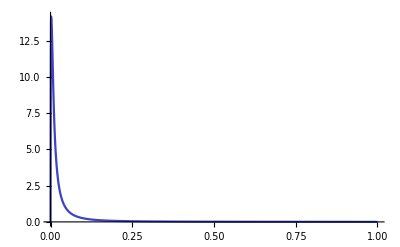
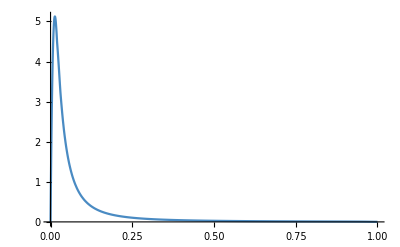
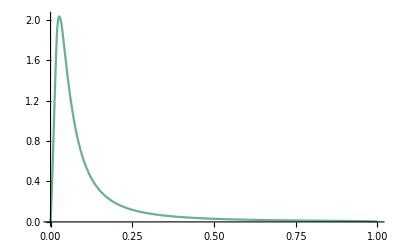
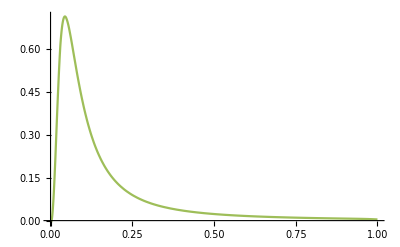
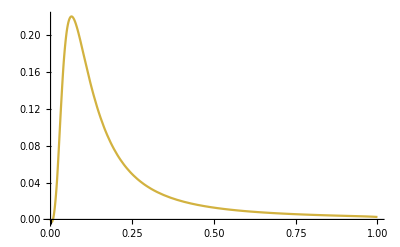
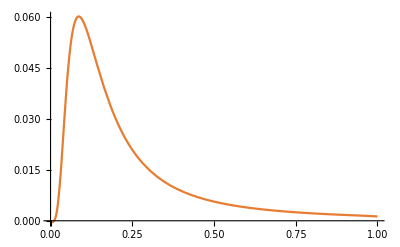
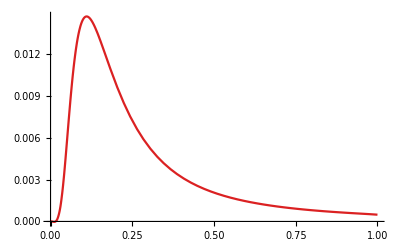
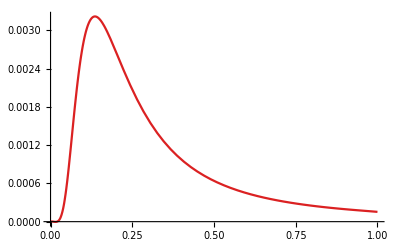

```mathematica
plotspRadUncorrCharm150=Table[Plot[expMeanUncorrCharm150*pRadsUncorrCharm150[[i]][x] HeavisideTheta[x] HeavisideTheta[1-x],{x,0, 1}, PlotRange->All,PlotStyle->{ColorData["Rainbow",i/Length[pRadsUncorrCharm10]]}],{i,1,Length[pRadsUncorrCharm150]}]
```

```mathematica
expMeanCorrCharm150= Exp[-meanGluonCorrection[150,cR, cA, mu, aS, 5 fmToGev, lambda, mG,mC,1]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.70668 and 0.00291665 for the integral and error estimates.

0.181466

```mathematica
pRadsCorrCharm150= pRadTableExpIn[expMeanCorrCharm150,150,cR, cA, mu, aS,5 fmToGev, lambda, mG, mC,1]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000698269 and 0.0000104679 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00135687 and 2.26087×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

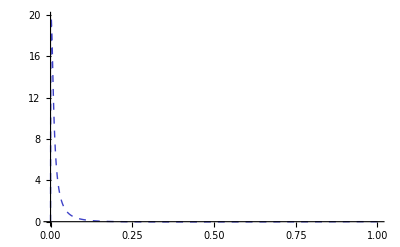
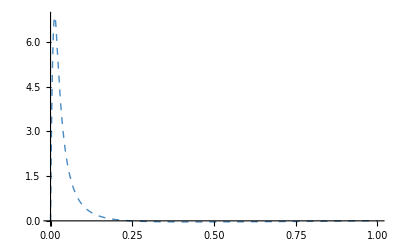
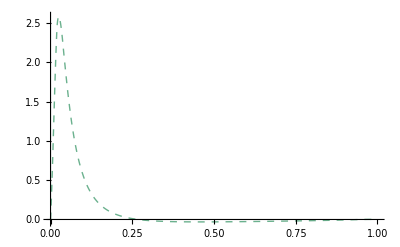
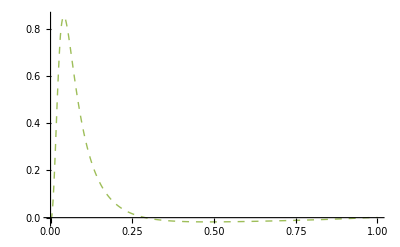
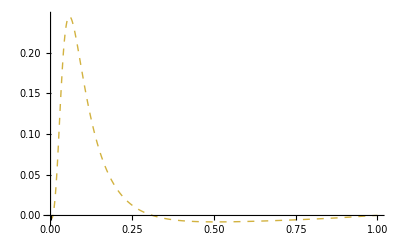
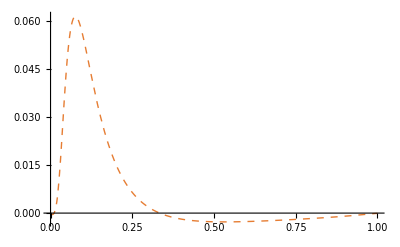
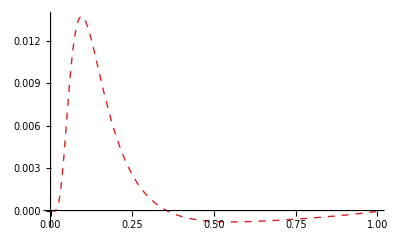
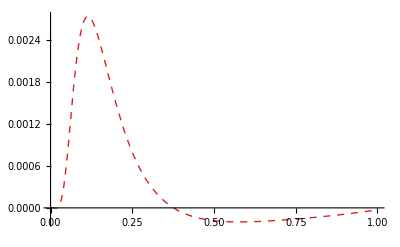

```mathematica
plotspRadCorrCharm150=Table[Plot[expMeanCorrCharm150*pRadsCorrCharm150[[i]][x] HeavisideTheta[x] HeavisideTheta[1-x],{x,0, 1}, PlotRange->All,PlotStyle->{ColorData["Rainbow",i/Length[pRadsUncorrCharm10]],Dashed,Thick}],{i,1,Length[pRadsUncorrCharm150]}]
```

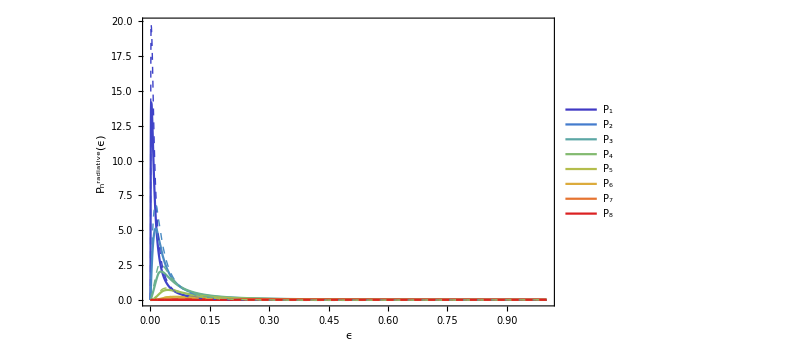

```mathematica
Show[plotspRadUncorrCharm150,plotspRadCorrCharm150,PlotRange->All,Epilog->Inset[LineLegend[Table[ColorData["Rainbow",j/Length[pRadsUncorrCharm150]],{j,1,Length[plotspRadUncorrCharm150]}],Table[Subscript[P, i],{i,1,Length[plotspRadUncorrCharm150]}],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.5,10}],FrameLabel->{{"P_n^radiative(ϵ)",""},{"ϵ","Charm 150GeV"}},Frame->True]
```

#### 100 GeV Bottom

```mathematica
expMeanUncorrBottom100= Exp[-meanGluonCorrection[100,cR, cA, mu, aS, 5 fmToGev, lambda, mG,mB,0]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.98282 and 0.00216361 for the integral and error estimates.

0.137681

```mathematica
pRadsUncorrBottom100= pRadTableExpIn[expMeanUncorrBottom100,100,cR, cA, mu, aS,5 fmToGev, lambda, mG, mB,0]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

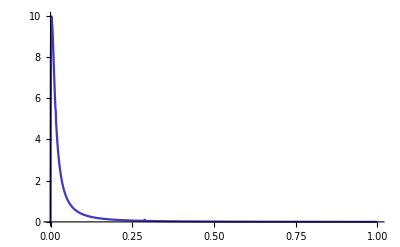
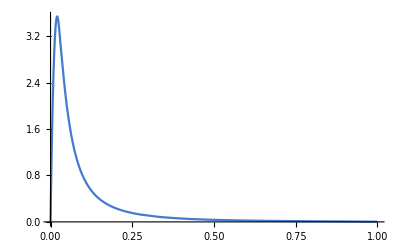
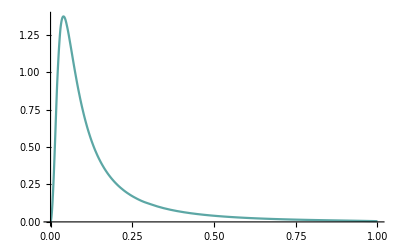
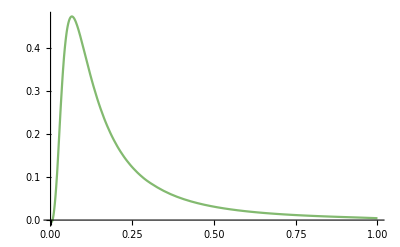
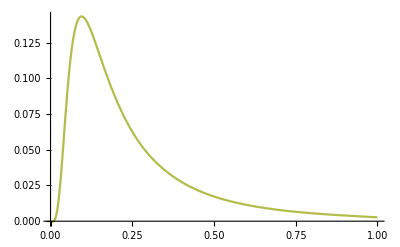
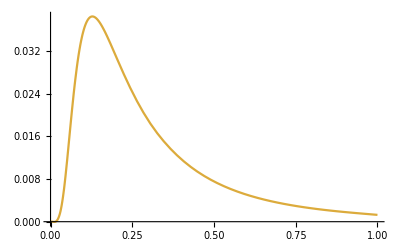
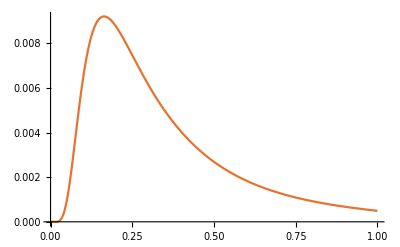
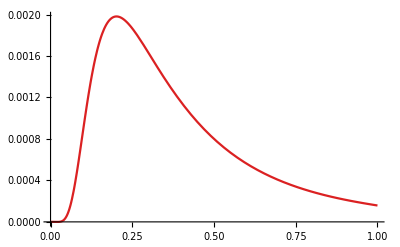

```mathematica
plotspRadUncorrBottom100=Table[Plot[expMeanUncorrBottom100*pRadsUncorrBottom100[[i]][x] HeavisideTheta[x] HeavisideTheta[1-x],{x,0, 1}, PlotRange->All,PlotStyle->{ColorData["Rainbow",i/Length[pRadsUncorrBottom100]]}],{i,1,Length[pRadsUncorrBottom100]}]
```

```mathematica
expMeanCorrBottom100= Exp[-meanGluonCorrection[100,cR, cA, mu, aS, 5 fmToGev, lambda, mG,mB,1]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.70922 and 0.00215798 for the integral and error estimates.

0.181007

```mathematica
pRadsCorrBottom100= pRadTableExpIn[expMeanCorrBottom100,100,cR, cA, mu, aS,5 fmToGev, lambda, mG, mB,1]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

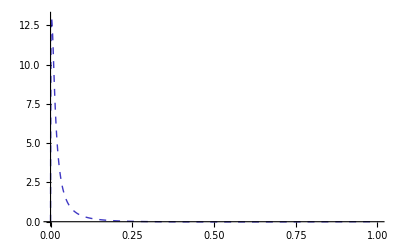
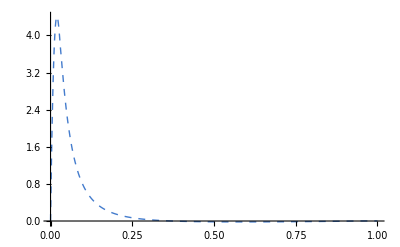
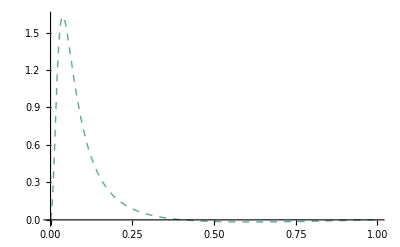
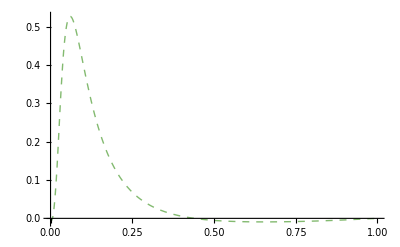
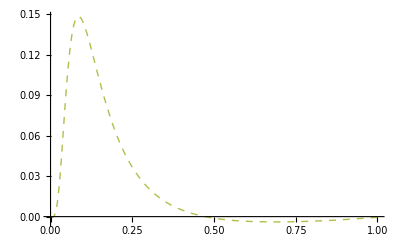
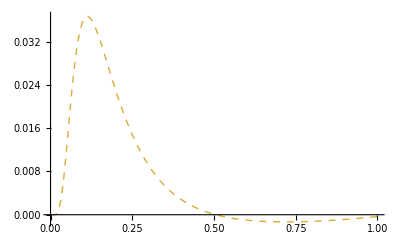
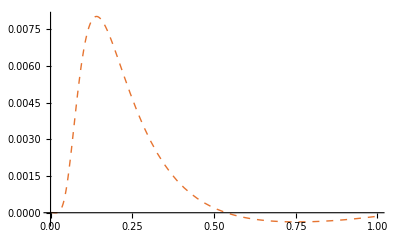
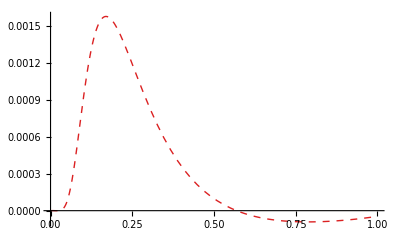

```mathematica
plotspRadCorrBottom100=Table[Plot[expMeanCorrBottom100*pRadsCorrBottom100[[i]][x] HeavisideTheta[x] HeavisideTheta[1-x],{x,0, 1}, PlotRange->All,PlotStyle->{ColorData["Rainbow",i/Length[pRadsCorrBottom100]],Dashed,Thick}],{i,1,Length[pRadsCorrBottom100]}]
```

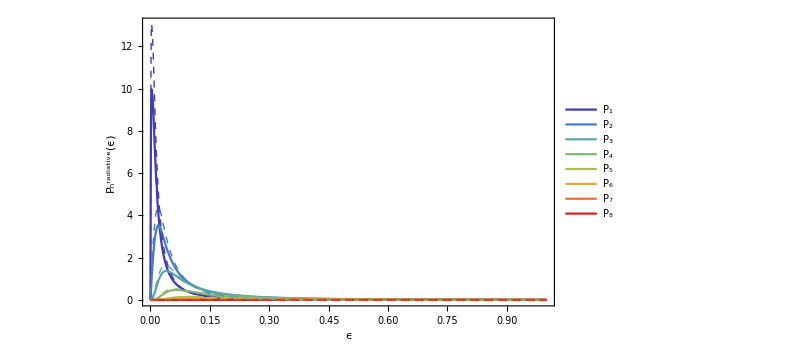

```mathematica
Show[plotspRadUncorrBottom100,plotspRadCorrBottom100,PlotRange->All,Epilog->Inset[LineLegend[Table[ColorData["Rainbow",j/Length[pRadsUncorrBottom100]],{j,1,Length[plotspRadUncorrBottom100]}],Table[Subscript[P, i],{i,1,Length[plotspRadUncorrBottom100]}],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.5,8}],FrameLabel->{{"P_n^radiative(ϵ)",""},{"ϵ","Bottom 100GeV"}},Frame->True]
```

### PElastic

Elastic energy Loss formula and Gaussian from this

```mathematica
crossOverEnergyBottom= x/.FindRoot[energyLossLowP8UsingMCI[aS, 0.25, nF, x,mB]-energyLossHighP12UsingMCI[aS, 0.25, nF, x,mB]==0,{x,16}, AccuracyGoal->6, PrecisionGoal-> 3]
```

164.914

```mathematica
lowPBottom =Parallelize[Table[{p, 5.068  energyLoss[0.3,0.25, 2, p, mB]}, {p, 0.1,crossOverEnergyBottom,0.1}]]
```

{{0.1,-0.00262988},{0.2,-0.00524608},{0.3,-0.00783507},{0.4,-0.0103836},{0.5,-0.012879},{0.6,-0.015309},{0.7,-0.0176622},{0.8,-0.0199279},{0.9,-0.0220964},{1.,-0.0241587},{1.1,-0.0261072},{1.2,-0.027935},{1.3,-0.0296363},{1.4,-0.0312063},{1.5,-0.0326414},{1.6,-0.0339386},{1.7,-0.0350962},{1.8,-0.0361129},{1.9,-0.0369885},{2.,-0.0377235},{2.1,-0.0383188},{2.2,-0.0387762},{2.3,-0.0390977},{2.4,-0.0392859},{2.5,-0.0393438},{2.6,-0.0392746},{2.7,-0.0390817},{2.8,-0.038769},{2.9,-0.0383402},{3.,-0.0377993},{3.1,-0.0371503},{3.2,-0.0363974},{3.3,-0.0355445},{3.4,-0.0345959},{3.5,-0.0335555},{3.6,-0.0324273},{3.7,-0.0312153},{3.8,-0.0299232},{3.9,-0.0285549},{4.,-0.027114},{4.1,-0.025604},{4.2,-0.0240284},{4.3,-0.0223905},{4.4,-0.0206936},{4.5,-0.0189407},{4.6,-0.0171348},{4.7,-0.0152789},{4.8,-0.0133756},{4.9,-0.0114277},{5.,-0.00943766},{5.1,-0.00740797},{5.2,-0.00534097},{5.3,-0.00323891},{5.4,-0.00110394},{5.5,0.00106188},{5.6,0.00325657},{5.7,0.00547826},{5.8,0.00772513},{5.9,0.00999548},{6.,0.0122876},{6.1,0.0146001},{6.2,0.0169312},{6.3,0.0192797},{6.4,0.0216442},{6.5,0.0240232},{6.6,0.0264157},{6.7,0.0288204},{6.8,0.0312362},{6.9,0.033662},{7.,0.0360968},{7.1,0.0385395},{7.2,0.0409893},{7.3,0.0434453},{7.4,0.0459066},{7.5,0.0483723},{7.6,0.0508419},{7.7,0.0533144},{7.8,0.0557893},{7.9,0.0582657},{8.,0.0607432},{8.1,0.0632212},{8.2,0.0656989},{8.3,0.068176},{8.4,0.0706518},{8.5,0.073126},{8.6,0.075598},{8.7,0.0780674},{8.8,0.0805337},{8.9,0.0829967},{9.,0.0854558},{9.1,0.0879108},{9.2,0.0903613},{9.3,0.0928069},{9.4,0.0952475},{9.5,0.0976827},{9.6,0.100112},{9.7,0.102536},{9.8,0.104953},{9.9,0.107364},{10.,0.109769},{10.1,0.112166},{10.2,0.114557},{10.3,0.11694},{10.4,0.119317},{10.5,0.121685},{10.6,0.124046},{10.7,0.126399},{10.8,0.128745},{10.9,0.131082},{11.,0.133411},{11.1,0.135732},{11.2,0.138045},{11.3,0.140349},{11.4,0.142644},{11.5,0.144932},{11.6,0.14721},{11.7,0.14948},{11.8,0.151741},{11.9,0.153993},{12.,0.156236},{12.1,0.158471},{12.2,0.160696},{12.3,0.162913},{12.4,0.16512},{12.5,0.167319},{12.6,0.169508},{12.7,0.171689},{12.8,0.17386},{12.9,0.176021},{13.,0.178152},{13.1,0.180252},{13.2,0.182321},{13.3,0.184362},{13.4,0.186374},{13.5,0.188361},{13.6,0.190323},{13.7,0.19226},{13.8,0.194175},{13.9,0.196069},{14.,0.197942},{14.1,0.199795},{14.2,0.201629},{14.3,0.203445},{14.4,0.205244},{14.5,0.207026},{14.6,0.208792},{14.7,0.210543},{14.8,0.21228},{14.9,0.214002},{15.,0.215711},{15.1,0.217407},{15.2,0.21909},{15.3,0.220761},{15.4,0.222421},{15.5,0.224069},{15.6,0.225707},{15.7,0.227334},{15.8,0.22895},{15.9,0.230557},{16.,0.232155},{16.1,0.233743},{16.2,0.235322},{16.3,0.236893},{16.4,0.238455},{16.5,0.240009},{16.6,0.241555},{16.7,0.243093},{16.8,0.244623},{16.9,0.246147},{17.,0.247662},{17.1,0.249171},{17.2,0.250673},{17.3,0.252169},{17.4,0.253657},{17.5,0.25514},{17.6,0.256616},{17.7,0.258085},{17.8,0.259549},{17.9,0.261007},{18.,0.262459},{18.1,0.263905},{18.2,0.265345},{18.3,0.26678},{18.4,0.26821},{18.5,0.269634},{18.6,0.271053},{18.7,0.272467},{18.8,0.273875},{18.9,0.275278},{19.,0.276677},{19.1,0.27807},{19.2,0.279459},{19.3,0.280843},{19.4,0.282222},{19.5,0.283596},{19.6,0.284966},{19.7,0.286331},{19.8,0.287691},{19.9,0.289047},{20.,0.290399},{20.1,0.291746},{20.2,0.293088},{20.3,0.294427},{20.4,0.295761},{20.5,0.29709},{20.6,0.298416},{20.7,0.299737},{20.8,0.301054},{20.9,0.302367},{21.,0.303676},{21.1,0.304981},{21.2,0.306281},{21.3,0.307578},{21.4,0.308871},{21.5,0.31016},{21.6,0.311444},{21.7,0.312725},{21.8,0.314002},{21.9,0.315275},{22.,0.316544},{22.1,0.31781},{22.2,0.319072},{22.3,0.320329},{22.4,0.321583},{22.5,0.322834},{22.6,0.32408},{22.7,0.325323},{22.8,0.326562},{22.9,0.327798},{23.,0.32903},{23.1,0.330258},{23.2,0.331483},{23.3,0.332704},{23.4,0.333921},{23.5,0.335135},{23.6,0.336346},{23.7,0.337553},{23.8,0.338756},{23.9,0.339956},{24.,0.341152},{24.1,0.342345},{24.2,0.343535},{24.3,0.344721},{24.4,0.345903},{24.5,0.347083},{24.6,0.348259},{24.7,0.349431},{24.8,0.3506},{24.9,0.351766},{25.,0.352929},{25.1,0.354088},{25.2,0.355244},{25.3,0.356396},{25.4,0.357545},{25.5,0.358691},{25.6,0.359834},{25.7,0.360974},{25.8,0.36211},{25.9,0.363243},{26.,0.364373},{26.1,0.3655},{26.2,0.366624},{26.3,0.367744},{26.4,0.368862},{26.5,0.369976},{26.6,0.371087},{26.7,0.372195},{26.8,0.3733},{26.9,0.374402},{27.,0.3755},{27.1,0.376596},{27.2,0.377689},{27.3,0.378778},{27.4,0.379865},{27.5,0.380949},{27.6,0.382029},{27.7,0.383107},{27.8,0.384182},{27.9,0.385254},{28.,0.386323},{28.1,0.387388},{28.2,0.388451},{28.3,0.389512},{28.4,0.390569},{28.5,0.391623},{28.6,0.392675},{28.7,0.393723},{28.8,0.394769},{28.9,0.395812},{29.,0.396852},{29.1,0.397889},{29.2,0.398924},{29.3,0.399955},{29.4,0.400984},{29.5,0.402011},{29.6,0.403034},{29.7,0.404055},{29.8,0.405073},{29.9,0.406088},{30.,0.4071},{30.1,0.40811},{30.2,0.409117},{30.3,0.410122},{30.4,0.411124},{30.5,0.412123},{30.6,0.413119},{30.7,0.414113},{30.8,0.415104},{30.9,0.416093},{31.,0.417079},{31.1,0.418062},{31.2,0.419043},{31.3,0.420022},{31.4,0.420997},{31.5,0.421971},{31.6,0.422941},{31.7,0.423909},{31.8,0.424875},{31.9,0.425838},{32.,0.426799},{32.1,0.427757},{32.2,0.428713},{32.3,0.429666},{32.4,0.430617},{32.5,0.431565},{32.6,0.432511},{32.7,0.433454},{32.8,0.434395},{32.9,0.435334},{33.,0.43627},{33.1,0.437204},{33.2,0.438136},{33.3,0.439065},{33.4,0.439992},{33.5,0.440916},{33.6,0.441838},{33.7,0.442758},{33.8,0.443675},{33.9,0.444591},{34.,0.445503},{34.1,0.446414},{34.2,0.447322},{34.3,0.448228},{34.4,0.449132},{34.5,0.450034},{34.6,0.450933},{34.7,0.45183},{34.8,0.452725},{34.9,0.453618},{35.,0.454508},{35.1,0.455396},{35.2,0.456282},{35.3,0.457166},{35.4,0.458048},{35.5,0.458927},{35.6,0.459805},{35.7,0.46068},{35.8,0.461553},{35.9,0.462424},{36.,0.463293},{36.1,0.46416},{36.2,0.465024},{36.3,0.465887},{36.4,0.466748},{36.5,0.467606},{36.6,0.468462},{36.7,0.469317},{36.8,0.470169},{36.9,0.471019},{37.,0.471867},{37.1,0.472714},{37.2,0.473558},{37.3,0.4744},{37.4,0.47524},{37.5,0.476078},{37.6,0.476915},{37.7,0.477749},{37.8,0.478581},{37.9,0.479411},{38.,0.48024},{38.1,0.481066},{38.2,0.481891},{38.3,0.482713},{38.4,0.483534},{38.5,0.484353},{38.6,0.48517},{38.7,0.485984},{38.8,0.486798},{38.9,0.487609},{39.,0.488418},{39.1,0.489225},{39.2,0.490031},{39.3,0.490835},{39.4,0.491637},{39.5,0.492437},{39.6,0.493235},{39.7,0.494031},{39.8,0.494826},{39.9,0.495619},{40.,0.49641},{40.1,0.497199},{40.2,0.497987},{40.3,0.498772},{40.4,0.499556},{40.5,0.500338},{40.6,0.501119},{40.7,0.501897},{40.8,0.502674},{40.9,0.503449},{41.,0.504223},{41.1,0.504994},{41.2,0.505764},{41.3,0.506533},{41.4,0.507299},{41.5,0.508064},{41.6,0.508827},{41.7,0.509589},{41.8,0.510349},{41.9,0.511107},{42.,0.511863},{42.1,0.512618},{42.2,0.513371},{42.3,0.514123},{42.4,0.514873},{42.5,0.515621},{42.6,0.516368},{42.7,0.517113},{42.8,0.517856},{42.9,0.518598},{43.,0.519339},{43.1,0.520077},{43.2,0.520814},{43.3,0.52155},{43.4,0.522284},{43.5,0.523016},{43.6,0.523747},{43.7,0.524476},{43.8,0.525204},{43.9,0.52593},{44.,0.526655},{44.1,0.527378},{44.2,0.528099},{44.3,0.528819},{44.4,0.529538},{44.5,0.530255},{44.6,0.53097},{44.7,0.531685},{44.8,0.532397},{44.9,0.533108},{45.,0.533818},{45.1,0.534526},{45.2,0.535232},{45.3,0.535938},{45.4,0.536641},{45.5,0.537344},{45.6,0.538044},{45.7,0.538744},{45.8,0.539442},{45.9,0.540138},{46.,0.540833},{46.1,0.541527},{46.2,0.542219},{46.3,0.54291},{46.4,0.543599},{46.5,0.544288},{46.6,0.544974},{46.7,0.545659},{46.8,0.546343},{46.9,0.547026},{47.,0.547707},{47.1,0.548387},{47.2,0.549065},{47.3,0.549742},{47.4,0.550418},{47.5,0.551092},{47.6,0.551765},{47.7,0.552437},{47.8,0.553107},{47.9,0.553776},{48.,0.554444},{48.1,0.55511},{48.2,0.555775},{48.3,0.556439},{48.4,0.557101},{48.5,0.557762},{48.6,0.558422},{48.7,0.559081},{48.8,0.559738},{48.9,0.560394},{49.,0.561049},{49.1,0.561702},{49.2,0.562354},{49.3,0.563005},{49.4,0.563655},{49.5,0.564303},{49.6,0.564951},{49.7,0.565596},{49.8,0.566241},{49.9,0.566885},{50.,0.567527},{50.1,0.568168},{50.2,0.568807},{50.3,0.569446},{50.4,0.570083},{50.5,0.570719},{50.6,0.571354},{50.7,0.571988},{50.8,0.572621},{50.9,0.573252},{51.,0.573882},{51.1,0.574511},{51.2,0.575139},{51.3,0.575765},{51.4,0.576391},{51.5,0.577015},{51.6,0.577638},{51.7,0.57826},{51.8,0.578881},{51.9,0.5795},{52.,0.580119},{52.1,0.580736},{52.2,0.581352},{52.3,0.581967},{52.4,0.582581},{52.5,0.583194},{52.6,0.583806},{52.7,0.584416},{52.8,0.585026},{52.9,0.585634},{53.,0.586241},{53.1,0.586847},{53.2,0.587452},{53.3,0.588056},{53.4,0.588659},{53.5,0.589261},{53.6,0.589862},{53.7,0.590461},{53.8,0.59106},{53.9,0.591657},{54.,0.592253},{54.1,0.592849},{54.2,0.593443},{54.3,0.594036},{54.4,0.594628},{54.5,0.595219},{54.6,0.595809},{54.7,0.596398},{54.8,0.596986},{54.9,0.597573},{55.,0.598159},{55.1,0.598743},{55.2,0.599327},{55.3,0.59991},{55.4,0.600492},{55.5,0.601072},{55.6,0.601652},{55.7,0.602231},{55.8,0.602808},{55.9,0.603385},{56.,0.603961},{56.1,0.604535},{56.2,0.605109},{56.3,0.605682},{56.4,0.606253},{56.5,0.606824},{56.6,0.607394},{56.7,0.607962},{56.8,0.60853},{56.9,0.609097},{57.,0.609663},{57.1,0.610228},{57.2,0.610792},{57.3,0.611354},{57.4,0.611916},{57.5,0.612477},{57.6,0.613037},{57.7,0.613597},{57.8,0.614155},{57.9,0.614712},{58.,0.615268},{58.1,0.615824},{58.2,0.616378},{58.3,0.616932},{58.4,0.617484},{58.5,0.618036},{58.6,0.618586},{58.7,0.619136},{58.8,0.619685},{58.9,0.620233},{59.,0.62078},{59.1,0.621326},{59.2,0.621872},{59.3,0.622416},{59.4,0.622959},{59.5,0.623502},{59.6,0.624044},{59.7,0.624584},{59.8,0.625124},{59.9,0.625663},{60.,0.626201},{60.1,0.626739},{60.2,0.627275},{60.3,0.62781},{60.4,0.628345},{60.5,0.628879},{60.6,0.629412},{60.7,0.629944},{60.8,0.630475},{60.9,0.631005},{61.,0.631535},{61.1,0.632063},{61.2,0.632591},{61.3,0.633118},{61.4,0.633644},{61.5,0.634169},{61.6,0.634694},{61.7,0.635217},{61.8,0.63574},{61.9,0.636262},{62.,0.636783},{62.1,0.637303},{62.2,0.637822},{62.3,0.638341},{62.4,0.638859},{62.5,0.639376},{62.6,0.639892},{62.7,0.640407},{62.8,0.640922},{62.9,0.641435},{63.,0.641948},{63.1,0.64246},{63.2,0.642972},{63.3,0.643482},{63.4,0.643992},{63.5,0.644501},{63.6,0.645009},{63.7,0.645516},{63.8,0.646023},{63.9,0.646529},{64.,0.647034},{64.1,0.647538},{64.2,0.648041},{64.3,0.648544},{64.4,0.649046},{64.5,0.649547},{64.6,0.650048},{64.7,0.650547},{64.8,0.651046},{64.9,0.651544},{65.,0.652041},{65.1,0.652538},{65.2,0.653034},{65.3,0.653529},{65.4,0.654023},{65.5,0.654517},{65.6,0.65501},{65.7,0.655502},{65.8,0.655993},{65.9,0.656484},{66.,0.656973},{66.1,0.657463},{66.2,0.657951},{66.3,0.658439},{66.4,0.658926},{66.5,0.659412},{66.6,0.659897},{66.7,0.660382},{66.8,0.660866},{66.9,0.66135},{67.,0.661832},{67.1,0.662314},{67.2,0.662795},{67.3,0.663276},{67.4,0.663756},{67.5,0.664235},{67.6,0.664713},{67.7,0.665191},{67.8,0.665668},{67.9,0.666144},{68.,0.66662},{68.1,0.667094},{68.2,0.667569},{68.3,0.668042},{68.4,0.668515},{68.5,0.668987},{68.6,0.669459},{68.7,0.669929},{68.8,0.6704},{68.9,0.670869},{69.,0.671338},{69.1,0.671806},{69.2,0.672273},{69.3,0.67274},{69.4,0.673206},{69.5,0.673671},{69.6,0.674136},{69.7,0.6746},{69.8,0.675064},{69.9,0.675526},{70.,0.675988},{70.1,0.67645},{70.2,0.676911},{70.3,0.677371},{70.4,0.67783},{70.5,0.678289},{70.6,0.678747},{70.7,0.679205},{70.8,0.679662},{70.9,0.680118},{71.,0.680574},{71.1,0.681029},{71.2,0.681483},{71.3,0.681937},{71.4,0.68239},{71.5,0.682842},{71.6,0.683294},{71.7,0.683745},{71.8,0.684196},{71.9,0.684646},{72.,0.685095},{72.1,0.685544},{72.2,0.685992},{72.3,0.686439},{72.4,0.686886},{72.5,0.687332},{72.6,0.687778},{72.7,0.688223},{72.8,0.688667},{72.9,0.689111},{73.,0.689554},{73.1,0.689997},{73.2,0.690439},{73.3,0.69088},{73.4,0.691321},{73.5,0.691761},{73.6,0.692201},{73.7,0.69264},{73.8,0.693078},{73.9,0.693516},{74.,0.693953},{74.1,0.69439},{74.2,0.694826},{74.3,0.695261},{74.4,0.695696},{74.5,0.696131},{74.6,0.696564},{74.7,0.696997},{74.8,0.69743},{74.9,0.697862},{75.,0.698293},{75.1,0.698724},{75.2,0.699155},{75.3,0.699584},{75.4,0.700013},{75.5,0.700442},{75.6,0.70087},{75.7,0.701297},{75.8,0.701724},{75.9,0.70215},{76.,0.702576},{76.1,0.703001},{76.2,0.703426},{76.3,0.70385},{76.4,0.704273},{76.5,0.704696},{76.6,0.705119},{76.7,0.705541},{76.8,0.705962},{76.9,0.706383},{77.,0.706803},{77.1,0.707223},{77.2,0.707642},{77.3,0.70806},{77.4,0.708478},{77.5,0.708896},{77.6,0.709313},{77.7,0.709729},{77.8,0.710145},{77.9,0.71056},{78.,0.710975},{78.1,0.71139},{78.2,0.711803},{78.3,0.712217},{78.4,0.712629},{78.5,0.713041},{78.6,0.713453},{78.7,0.713864},{78.8,0.714275},{78.9,0.714685},{79.,0.715095},{79.1,0.715504},{79.2,0.715912},{79.3,0.71632},{79.4,0.716728},{79.5,0.717135},{79.6,0.717541},{79.7,0.717947},{79.8,0.718353},{79.9,0.718757},{80.,0.719162},{80.1,0.719566},{80.2,0.719969},{80.3,0.720372},{80.4,0.720775},{80.5,0.721177},{80.6,0.721578},{80.7,0.721979},{80.8,0.722379},{80.9,0.722779},{81.,0.723179},{81.1,0.723578},{81.2,0.723976},{81.3,0.724374},{81.4,0.724772},{81.5,0.725169},{81.6,0.725565},{81.7,0.725961},{81.8,0.726357},{81.9,0.726752},{82.,0.727146},{82.1,0.72754},{82.2,0.727934},{82.3,0.728327},{82.4,0.72872},{82.5,0.729112},{82.6,0.729503},{82.7,0.729895},{82.8,0.730285},{82.9,0.730676},{83.,0.731065},{83.1,0.731455},{83.2,0.731844},{83.3,0.732232},{83.4,0.73262},{83.5,0.733007},{83.6,0.733394},{83.7,0.733781},{83.8,0.734167},{83.9,0.734553},{84.,0.734938},{84.1,0.735322},{84.2,0.735707},{84.3,0.73609},{84.4,0.736474},{84.5,0.736857},{84.6,0.737239},{84.7,0.737621},{84.8,0.738002},{84.9,0.738383},{85.,0.738764},{85.1,0.739144},{85.2,0.739524},{85.3,0.739903},{85.4,0.740282},{85.5,0.74066},{85.6,0.741038},{85.7,0.741416},{85.8,0.741793},{85.9,0.742169},{86.,0.742545},{86.1,0.742921},{86.2,0.743296},{86.3,0.743671},{86.4,0.744046},{86.5,0.74442},{86.6,0.744793},{86.7,0.745166},{86.8,0.745539},{86.9,0.745911},{87.,0.746283},{87.1,0.746654},{87.2,0.747025},{87.3,0.747396},{87.4,0.747766},{87.5,0.748136},{87.6,0.748505},{87.7,0.748874},{87.8,0.749242},{87.9,0.74961},{88.,0.749978},{88.1,0.750345},{88.2,0.750711},{88.3,0.751078},{88.4,0.751444},{88.5,0.751809},{88.6,0.752174},{88.7,0.752539},{88.8,0.752903},{88.9,0.753267},{89.,0.75363},{89.1,0.753993},{89.2,0.754356},{89.3,0.754718},{89.4,0.75508},{89.5,0.755441},{89.6,0.755802},{89.7,0.756163},{89.8,0.756523},{89.9,0.756883},{90.,0.757242},{90.1,0.757601},{90.2,0.75796},{90.3,0.758318},{90.4,0.758675},{90.5,0.759033},{90.6,0.75939},{90.7,0.759746},{90.8,0.760103},{90.9,0.760458},{91.,0.760814},{91.1,0.761169},{91.2,0.761523},{91.3,0.761877},{91.4,0.762231},{91.5,0.762585},{91.6,0.762938},{91.7,0.76329},{91.8,0.763643},{91.9,0.763995},{92.,0.764346},{92.1,0.764697},{92.2,0.765048},{92.3,0.765398},{92.4,0.765748},{92.5,0.766098},{92.6,0.766447},{92.7,0.766796},{92.8,0.767144},{92.9,0.767492},{93.,0.76784},{93.1,0.768187},{93.2,0.768534},{93.3,0.768881},{93.4,0.769227},{93.5,0.769573},{93.6,0.769918},{93.7,0.770263},{93.8,0.770608},{93.9,0.770952},{94.,0.771296},{94.1,0.77164},{94.2,0.771983},{94.3,0.772326},{94.4,0.772669},{94.5,0.773011},{94.6,0.773353},{94.7,0.773694},{94.8,0.774035},{94.9,0.774376},{95.,0.774716},{95.1,0.775056},{95.2,0.775396},{95.3,0.775735},{95.4,0.776074},{95.5,0.776412},{95.6,0.77675},{95.7,0.777088},{95.8,0.777426},{95.9,0.777763},{96.,0.7781},{96.1,0.778436},{96.2,0.778772},{96.3,0.779108},{96.4,0.779443},{96.5,0.779778},{96.6,0.780113},{96.7,0.780447},{96.8,0.780781},{96.9,0.781115},{97.,0.781448},{97.1,0.781781},{97.2,0.782113},{97.3,0.782446},{97.4,0.782777},{97.5,0.783109},{97.6,0.78344},{97.7,0.783771},{97.8,0.784102},{97.9,0.784432},{98.,0.784762},{98.1,0.785091},{98.2,0.78542},{98.3,0.785749},{98.4,0.786078},{98.5,0.786406},{98.6,0.786733},{98.7,0.787061},{98.8,0.787388},{98.9,0.787715},{99.,0.788041},{99.1,0.788368},{99.2,0.788693},{99.3,0.789019},{99.4,0.789344},{99.5,0.789669},{99.6,0.789993},{99.7,0.790317},{99.8,0.790641},{99.9,0.790965},{100.,0.791288},{100.1,0.791611},{100.2,0.791933},{100.3,0.792256},{100.4,0.792577},{100.5,0.792899},{100.6,0.79322},{100.7,0.793541},{100.8,0.793862},{100.9,0.794182},{101.,0.794502},{101.1,0.794822},{101.2,0.795141},{101.3,0.79546},{101.4,0.795779},{101.5,0.796097},{101.6,0.796415},{101.7,0.796733},{101.8,0.79705},{101.9,0.797367},{102.,0.797684},{102.1,0.798001},{102.2,0.798317},{102.3,0.798633},{102.4,0.798948},{102.5,0.799264},{102.6,0.799578},{102.7,0.799893},{102.8,0.800207},{102.9,0.800521},{103.,0.800835},{103.1,0.801148},{103.2,0.801462},{103.3,0.801774},{103.4,0.802087},{103.5,0.802399},{103.6,0.802711},{103.7,0.803022},{103.8,0.803334},{103.9,0.803645},{104.,0.803955},{104.1,0.804266},{104.2,0.804576},{104.3,0.804885},{104.4,0.805195},{104.5,0.805504},{104.6,0.805813},{104.7,0.806122},{104.8,0.80643},{104.9,0.806738},{105.,0.807045},{105.1,0.807353},{105.2,0.80766},{105.3,0.807967},{105.4,0.808273},{105.5,0.808579},{105.6,0.808885},{105.7,0.809191},{105.8,0.809496},{105.9,0.809801},{106.,0.810106},{106.1,0.81041},{106.2,0.810715},{106.3,0.811018},{106.4,0.811322},{106.5,0.811625},{106.6,0.811928},{106.7,0.812231},{106.8,0.812534},{106.9,0.812836},{107.,0.813138},{107.1,0.813439},{107.2,0.81374},{107.3,0.814041},{107.4,0.814342},{107.5,0.814643},{107.6,0.814943},{107.7,0.815243},{107.8,0.815542},{107.9,0.815842},{108.,0.816141},{108.1,0.816439},{108.2,0.816738},{108.3,0.817036},{108.4,0.817334},{108.5,0.817632},{108.6,0.817929},{108.7,0.818226},{108.8,0.818523},{108.9,0.81882},{109.,0.819116},{109.1,0.819412},{109.2,0.819708},{109.3,0.820003},{109.4,0.820298},{109.5,0.820593},{109.6,0.820888},{109.7,0.821182},{109.8,0.821476},{109.9,0.82177},{110.,0.822064},{110.1,0.822357},{110.2,0.82265},{110.3,0.822943},{110.4,0.823235},{110.5,0.823528},{110.6,0.82382},{110.7,0.824111},{110.8,0.824403},{110.9,0.824694},{111.,0.824985},{111.1,0.825275},{111.2,0.825566},{111.3,0.825856},{111.4,0.826146},{111.5,0.826435},{111.6,0.826725},{111.7,0.827014},{111.8,0.827302},{111.9,0.827591},{112.,0.827879},{112.1,0.828167},{112.2,0.828455},{112.3,0.828742},{112.4,0.82903},{112.5,0.829317},{112.6,0.829603},{112.7,0.82989},{112.8,0.830176},{112.9,0.830462},{113.,0.830748},{113.1,0.831033},{113.2,0.831318},{113.3,0.831603},{113.4,0.831888},{113.5,0.832172},{113.6,0.832457},{113.7,0.832741},{113.8,0.833024},{113.9,0.833308},{114.,0.833591},{114.1,0.833874},{114.2,0.834156},{114.3,0.834439},{114.4,0.834721},{114.5,0.835003},{114.6,0.835285},{114.7,0.835566},{114.8,0.835847},{114.9,0.836128},{115.,0.836409},{115.1,0.836689},{115.2,0.836969},{115.3,0.837249},{115.4,0.837529},{115.5,0.837808},{115.6,0.838088},{115.7,0.838367},{115.8,0.838645},{115.9,0.838924},{116.,0.839202},{116.1,0.83948},{116.2,0.839758},{116.3,0.840035},{116.4,0.840313},{116.5,0.84059},{116.6,0.840866},{116.7,0.841143},{116.8,0.841419},{116.9,0.841695},{117.,0.841971},{117.1,0.842247},{117.2,0.842522},{117.3,0.842797},{117.4,0.843072},{117.5,0.843347},{117.6,0.843621},{117.7,0.843895},{117.8,0.844169},{117.9,0.844443},{118.,0.844717},{118.1,0.84499},{118.2,0.845263},{118.3,0.845536},{118.4,0.845808},{118.5,0.846081},{118.6,0.846353},{118.7,0.846624},{118.8,0.846896},{118.9,0.847167},{119.,0.847439},{119.1,0.84771},{119.2,0.84798},{119.3,0.848251},{119.4,0.848521},{119.5,0.848791},{119.6,0.849061},{119.7,0.84933},{119.8,0.8496},{119.9,0.849869},{120.,0.850138},{120.1,0.850406},{120.2,0.850675},{120.3,0.850943},{120.4,0.851211},{120.5,0.851479},{120.6,0.851746},{120.7,0.852013},{120.8,0.85228},{120.9,0.852547},{121.,0.852814},{121.1,0.85308},{121.2,0.853347},{121.3,0.853613},{121.4,0.853878},{121.5,0.854144},{121.6,0.854409},{121.7,0.854674},{121.8,0.854939},{121.9,0.855204},{122.,0.855468},{122.1,0.855732},{122.2,0.855996},{122.3,0.85626},{122.4,0.856524},{122.5,0.856787},{122.6,0.85705},{122.7,0.857313},{122.8,0.857576},{122.9,0.857838},{123.,0.8581},{123.1,0.858362},{123.2,0.858624},{123.3,0.858886},{123.4,0.859147},{123.5,0.859408},{123.6,0.859669},{123.7,0.85993},{123.8,0.860191},{123.9,0.860451},{124.,0.860711},{124.1,0.860971},{124.2,0.861231},{124.3,0.86149},{124.4,0.861749},{124.5,0.862008},{124.6,0.862267},{124.7,0.862526},{124.8,0.862784},{124.9,0.863043},{125.,0.863301},{125.1,0.863558},{125.2,0.863816},{125.3,0.864073},{125.4,0.864331},{125.5,0.864588},{125.6,0.864844},{125.7,0.865101},{125.8,0.865357},{125.9,0.865613},{126.,0.865869},{126.1,0.866125},{126.2,0.866381},{126.3,0.866636},{126.4,0.866891},{126.5,0.867146},{126.6,0.867401},{126.7,0.867655},{126.8,0.86791},{126.9,0.868164},{127.,0.868418},{127.1,0.868671},{127.2,0.868925},{127.3,0.869178},{127.4,0.869431},{127.5,0.869684},{127.6,0.869937},{127.7,0.870189},{127.8,0.870442},{127.9,0.870694},{128.,0.870946},{128.1,0.871197},{128.2,0.871449},{128.3,0.8717},{128.4,0.871951},{128.5,0.872202},{128.6,0.872453},{128.7,0.872703},{128.8,0.872954},{128.9,0.873204},{129.,0.873454},{129.1,0.873704},{129.2,0.873953},{129.3,0.874202},{129.4,0.874452},{129.5,0.874701},{129.6,0.874949},{129.7,0.875198},{129.8,0.875446},{129.9,0.875694},{130.,0.875942},{130.1,0.87619},{130.2,0.876438},{130.3,0.876685},{130.4,0.876932},{130.5,0.87718},{130.6,0.877426},{130.7,0.877673},{130.8,0.877919},{130.9,0.878166},{131.,0.878412},{131.1,0.878658},{131.2,0.878903},{131.3,0.879149},{131.4,0.879394},{131.5,0.879639},{131.6,0.879884},{131.7,0.880129},{131.8,0.880374},{131.9,0.880618},{132.,0.880862},{132.1,0.881106},{132.2,0.88135},{132.3,0.881594},{132.4,0.881837},{132.5,0.88208},{132.6,0.882323},{132.7,0.882566},{132.8,0.882809},{132.9,0.883052},{133.,0.883294},{133.1,0.883536},{133.2,0.883778},{133.3,0.88402},{133.4,0.884261},{133.5,0.884503},{133.6,0.884744},{133.7,0.884985},{133.8,0.885226},{133.9,0.885467},{134.,0.885707},{134.1,0.885948},{134.2,0.886188},{134.3,0.886428},{134.4,0.886667},{134.5,0.886907},{134.6,0.887147},{134.7,0.887386},{134.8,0.887625},{134.9,0.887864},{135.,0.888102},{135.1,0.888341},{135.2,0.888579},{135.3,0.888818},{135.4,0.889056},{135.5,0.889293},{135.6,0.889531},{135.7,0.889768},{135.8,0.890006},{135.9,0.890243},{136.,0.89048},{136.1,0.890717},{136.2,0.890953},{136.3,0.89119},{136.4,0.891426},{136.5,0.891662},{136.6,0.891898},{136.7,0.892133},{136.8,0.892369},{136.9,0.892604},{137.,0.89284},{137.1,0.893075},{137.2,0.893309},{137.3,0.893544},{137.4,0.893779},{137.5,0.894013},{137.6,0.894247},{137.7,0.894481},{137.8,0.894715},{137.9,0.894949},{138.,0.895182},{138.1,0.895415},{138.2,0.895648},{138.3,0.895881},{138.4,0.896114},{138.5,0.896347},{138.6,0.896579},{138.7,0.896811},{138.8,0.897044},{138.9,0.897276},{139.,0.897507},{139.1,0.897739},{139.2,0.89797},{139.3,0.898202},{139.4,0.898433},{139.5,0.898664},{139.6,0.898894},{139.7,0.899125},{139.8,0.899355},{139.9,0.899586},{140.,0.899816},{140.1,0.900046},{140.2,0.900276},{140.3,0.900505},{140.4,0.900735},{140.5,0.900964},{140.6,0.901193},{140.7,0.901422},{140.8,0.901651},{140.9,0.901879},{141.,0.902108},{141.1,0.902336},{141.2,0.902564},{141.3,0.902792},{141.4,0.90302},{141.5,0.903248},{141.6,0.903475},{141.7,0.903702},{141.8,0.903929},{141.9,0.904156},{142.,0.904383},{142.1,0.90461},{142.2,0.904836},{142.3,0.905063},{142.4,0.905289},{142.5,0.905515},{142.6,0.905741},{142.7,0.905967},{142.8,0.906192},{142.9,0.906417},{143.,0.906643},{143.1,0.906868},{143.2,0.907093},{143.3,0.907317},{143.4,0.907542},{143.5,0.907766},{143.6,0.907991},{143.7,0.908215},{143.8,0.908439},{143.9,0.908663},{144.,0.908886},{144.1,0.90911},{144.2,0.909333},{144.3,0.909556},{144.4,0.909779},{144.5,0.910002},{144.6,0.910225},{144.7,0.910447},{144.8,0.91067},{144.9,0.910892},{145.,0.911114},{145.1,0.911336},{145.2,0.911558},{145.3,0.911779},{145.4,0.912001},{145.5,0.912222},{145.6,0.912443},{145.7,0.912664},{145.8,0.912885},{145.9,0.913106},{146.,0.913326},{146.1,0.913547},{146.2,0.913767},{146.3,0.913987},{146.4,0.914207},{146.5,0.914427},{146.6,0.914647},{146.7,0.914866},{146.8,0.915085},{146.9,0.915305},{147.,0.915524},{147.1,0.915742},{147.2,0.915961},{147.3,0.91618},{147.4,0.916398},{147.5,0.916617},{147.6,0.916835},{147.7,0.917053},{147.8,0.91727},{147.9,0.917488},{148.,0.917706},{148.1,0.917923},{148.2,0.91814},{148.3,0.918357},{148.4,0.918574},{148.5,0.918791},{148.6,0.919008},{148.7,0.919224},{148.8,0.919441},{148.9,0.919657},{149.,0.919873},{149.1,0.920089},{149.2,0.920305},{149.3,0.92052},{149.4,0.920736},{149.5,0.920951},{149.6,0.921166},{149.7,0.921381},{149.8,0.921596},{149.9,0.921811},{150.,0.922026},{150.1,0.92224},{150.2,0.922454},{150.3,0.922668},{150.4,0.922883},{150.5,0.923096},{150.6,0.92331},{150.7,0.923524},{150.8,0.923737},{150.9,0.923951},{151.,0.924164},{151.1,0.924377},{151.2,0.92459},{151.3,0.924802},{151.4,0.925015},{151.5,0.925227},{151.6,0.92544},{151.7,0.925652},{151.8,0.925864},{151.9,0.926076},{152.,0.926288},{152.1,0.926499},{152.2,0.926711},{152.3,0.926922},{152.4,0.927133},{152.5,0.927344},{152.6,0.927555},{152.7,0.927766},{152.8,0.927977},{152.9,0.928187},{153.,0.928397},{153.1,0.928608},{153.2,0.928818},{153.3,0.929028},{153.4,0.929237},{153.5,0.929447},{153.6,0.929657},{153.7,0.929866},{153.8,0.930075},{153.9,0.930284},{154.,0.930493},{154.1,0.930702},{154.2,0.930911},{154.3,0.931119},{154.4,0.931328},{154.5,0.931536},{154.6,0.931744},{154.7,0.931952},{154.8,0.93216},{154.9,0.932368},{155.,0.932576},{155.1,0.932783},{155.2,0.93299},{155.3,0.933198},{155.4,0.933405},{155.5,0.933612},{155.6,0.933818},{155.7,0.934025},{155.8,0.934232},{155.9,0.934438},{156.,0.934644},{156.1,0.934851},{156.2,0.935057},{156.3,0.935262},{156.4,0.935468},{156.5,0.935674},{156.6,0.935879},{156.7,0.936085},{156.8,0.93629},{156.9,0.936495},{157.,0.9367},{157.1,0.936905},{157.2,0.937109},{157.3,0.937314},{157.4,0.937518},{157.5,0.937723},{157.6,0.937927},{157.7,0.938131},{157.8,0.938335},{157.9,0.938538},{158.,0.938742},{158.1,0.938945},{158.2,0.939149},{158.3,0.939352},{158.4,0.939555},{158.5,0.939758},{158.6,0.939961},{158.7,0.940164},{158.8,0.940366},{158.9,0.940569},{159.,0.940771},{159.1,0.940973},{159.2,0.941175},{159.3,0.941377},{159.4,0.941579},{159.5,0.941781},{159.6,0.941983},{159.7,0.942184},{159.8,0.942385},{159.9,0.942586},{160.,0.942788},{160.1,0.942988},{160.2,0.943189},{160.3,0.94339},{160.4,0.94359},{160.5,0.943791},{160.6,0.943991},{160.7,0.944191},{160.8,0.944391},{160.9,0.944591},{161.,0.944791},{161.1,0.944991},{161.2,0.94519},{161.3,0.94539},{161.4,0.945589},{161.5,0.945788},{161.6,0.945987},{161.7,0.946186},{161.8,0.946385},{161.9,0.946584},{162.,0.946782},{162.1,0.946981},{162.2,0.947179},{162.3,0.947377},{162.4,0.947575},{162.5,0.947773},{162.6,0.947971},{162.7,0.948169},{162.8,0.948366},{162.9,0.948564},{163.,0.948761},{163.1,0.948958},{163.2,0.949155},{163.3,0.949352},{163.4,0.949549},{163.5,0.949746},{163.6,0.949942},{163.7,0.950139},{163.8,0.950335},{163.9,0.950532},{164.,0.950728},{164.1,0.950924},{164.2,0.951119},{164.3,0.951315},{164.4,0.951511},{164.5,0.951706},{164.6,0.951902},{164.7,0.952097},{164.8,0.952292},{164.9,0.952487}}

```mathematica
highPBottom=Parallelize[Table[{p, 5.068  energyLoss[0.3,0.25, 2, p, mB]}, {p,crossOverEnergyBottom,200,0.1}]]
```

{{164.914,1.90503 HeavisideTheta[0.]},{165.014,0.952612},{165.114,0.952708},{165.214,0.952804},{165.314,0.952901},{165.414,0.952997},{165.514,0.953093},{165.614,0.953189},{165.714,0.953285},{165.814,0.953381},{165.914,0.953477},{166.014,0.953573},{166.114,0.953669},{166.214,0.953764},{166.314,0.95386},{166.414,0.953956},{166.514,0.954051},{166.614,0.954147},{166.714,0.954242},{166.814,0.954338},{166.914,0.954433},{167.014,0.954528},{167.114,0.954623},{167.214,0.954719},{167.314,0.954814},{167.414,0.954909},{167.514,0.955004},{167.614,0.955099},{167.714,0.955194},{167.814,0.955288},{167.914,0.955383},{168.014,0.955478},{168.114,0.955573},{168.214,0.955667},{168.314,0.955762},{168.414,0.955856},{168.514,0.955951},{168.614,0.956045},{168.714,0.956139},{168.814,0.956234},{168.914,0.956328},{169.014,0.956422},{169.114,0.956516},{169.214,0.95661},{169.314,0.956704},{169.414,0.956798},{169.514,0.956892},{169.614,0.956986},{169.714,0.95708},{169.814,0.957173},{169.914,0.957267},{170.014,0.95736},{170.114,0.957454},{170.214,0.957548},{170.314,0.957641},{170.414,0.957734},{170.514,0.957828},{170.614,0.957921},{170.714,0.958014},{170.814,0.958107},{170.914,0.9582},{171.014,0.958294},{171.114,0.958387},{171.214,0.958479},{171.314,0.958572},{171.414,0.958665},{171.514,0.958758},{171.614,0.958851},{171.714,0.958943},{171.814,0.959036},{171.914,0.959129},{172.014,0.959221},{172.114,0.959314},{172.214,0.959406},{172.314,0.959498},{172.414,0.959591},{172.514,0.959683},{172.614,0.959775},{172.714,0.959867},{172.814,0.959959},{172.914,0.960051},{173.014,0.960143},{173.114,0.960235},{173.214,0.960327},{173.314,0.960419},{173.414,0.960511},{173.514,0.960602},{173.614,0.960694},{173.714,0.960786},{173.814,0.960877},{173.914,0.960969},{174.014,0.96106},{174.114,0.961152},{174.214,0.961243},{174.314,0.961334},{174.414,0.961426},{174.514,0.961517},{174.614,0.961608},{174.714,0.961699},{174.814,0.96179},{174.914,0.961881},{175.014,0.961972},{175.114,0.962063},{175.214,0.962154},{175.314,0.962244},{175.414,0.962335},{175.514,0.962426},{175.614,0.962516},{175.714,0.962607},{175.814,0.962697},{175.914,0.962788},{176.014,0.962878},{176.114,0.962969},{176.214,0.963059},{176.314,0.963149},{176.414,0.96324},{176.514,0.96333},{176.614,0.96342},{176.714,0.96351},{176.814,0.9636},{176.914,0.96369},{177.014,0.96378},{177.114,0.96387},{177.214,0.963959},{177.314,0.964049},{177.414,0.964139},{177.514,0.964228},{177.614,0.964318},{177.714,0.964408},{177.814,0.964497},{177.914,0.964587},{178.014,0.964676},{178.114,0.964765},{178.214,0.964855},{178.314,0.964944},{178.414,0.965033},{178.514,0.965122},{178.614,0.965211},{178.714,0.9653},{178.814,0.965389},{178.914,0.965478},{179.014,0.965567},{179.114,0.965656},{179.214,0.965745},{179.314,0.965834},{179.414,0.965922},{179.514,0.966011},{179.614,0.9661},{179.714,0.966188},{179.814,0.966277},{179.914,0.966365},{180.014,0.966454},{180.114,0.966542},{180.214,0.96663},{180.314,0.966718},{180.414,0.966807},{180.514,0.966895},{180.614,0.966983},{180.714,0.967071},{180.814,0.967159},{180.914,0.967247},{181.014,0.967335},{181.114,0.967423},{181.214,0.967511},{181.314,0.967598},{181.414,0.967686},{181.514,0.967774},{181.614,0.967861},{181.714,0.967949},{181.814,0.968037},{181.914,0.968124},{182.014,0.968212},{182.114,0.968299},{182.214,0.968386},{182.314,0.968474},{182.414,0.968561},{182.514,0.968648},{182.614,0.968735},{182.714,0.968822},{182.814,0.968909},{182.914,0.968996},{183.014,0.969083},{183.114,0.96917},{183.214,0.969257},{183.314,0.969344},{183.414,0.969431},{183.514,0.969517},{183.614,0.969604},{183.714,0.969691},{183.814,0.969777},{183.914,0.969864},{184.014,0.96995},{184.114,0.970037},{184.214,0.970123},{184.314,0.970209},{184.414,0.970296},{184.514,0.970382},{184.614,0.970468},{184.714,0.970554},{184.814,0.970641},{184.914,0.970727},{185.014,0.970813},{185.114,0.970899},{185.214,0.970985},{185.314,0.97107},{185.414,0.971156},{185.514,0.971242},{185.614,0.971328},{185.714,0.971413},{185.814,0.971499},{185.914,0.971585},{186.014,0.97167},{186.114,0.971756},{186.214,0.971841},{186.314,0.971927},{186.414,0.972012},{186.514,0.972097},{186.614,0.972183},{186.714,0.972268},{186.814,0.972353},{186.914,0.972438},{187.014,0.972523},{187.114,0.972608},{187.214,0.972693},{187.314,0.972778},{187.414,0.972863},{187.514,0.972948},{187.614,0.973033},{187.714,0.973118},{187.814,0.973203},{187.914,0.973287},{188.014,0.973372},{188.114,0.973457},{188.214,0.973541},{188.314,0.973626},{188.414,0.97371},{188.514,0.973795},{188.614,0.973879},{188.714,0.973963},{188.814,0.974048},{188.914,0.974132},{189.014,0.974216},{189.114,0.9743},{189.214,0.974384},{189.314,0.974468},{189.414,0.974552},{189.514,0.974636},{189.614,0.97472},{189.714,0.974804},{189.814,0.974888},{189.914,0.974972},{190.014,0.975056},{190.114,0.975139},{190.214,0.975223},{190.314,0.975307},{190.414,0.97539},{190.514,0.975474},{190.614,0.975557},{190.714,0.975641},{190.814,0.975724},{190.914,0.975807},{191.014,0.975891},{191.114,0.975974},{191.214,0.976057},{191.314,0.97614},{191.414,0.976224},{191.514,0.976307},{191.614,0.97639},{191.714,0.976473},{191.814,0.976556},{191.914,0.976639},{192.014,0.976722},{192.114,0.976804},{192.214,0.976887},{192.314,0.97697},{192.414,0.977053},{192.514,0.977135},{192.614,0.977218},{192.714,0.977301},{192.814,0.977383},{192.914,0.977466},{193.014,0.977548},{193.114,0.977631},{193.214,0.977713},{193.314,0.977795},{193.414,0.977878},{193.514,0.97796},{193.614,0.978042},{193.714,0.978124},{193.814,0.978206},{193.914,0.978288},{194.014,0.97837},{194.114,0.978452},{194.214,0.978534},{194.314,0.978616},{194.414,0.978698},{194.514,0.97878},{194.614,0.978862},{194.714,0.978943},{194.814,0.979025},{194.914,0.979107},{195.014,0.979188},{195.114,0.97927},{195.214,0.979352},{195.314,0.979433},{195.414,0.979515},{195.514,0.979596},{195.614,0.979677},{195.714,0.979759},{195.814,0.97984},{195.914,0.979921},{196.014,0.980002},{196.114,0.980083},{196.214,0.980165},{196.314,0.980246},{196.414,0.980327},{196.514,0.980408},{196.614,0.980489},{196.714,0.98057},{196.814,0.98065},{196.914,0.980731},{197.014,0.980812},{197.114,0.980893},{197.214,0.980974},{197.314,0.981054},{197.414,0.981135},{197.514,0.981215},{197.614,0.981296},{197.714,0.981376},{197.814,0.981457},{197.914,0.981537},{198.014,0.981618},{198.114,0.981698},{198.214,0.981778},{198.314,0.981859},{198.414,0.981939},{198.514,0.982019},{198.614,0.982099},{198.714,0.982179},{198.814,0.982259},{198.914,0.982339},{199.014,0.982419},{199.114,0.982499},{199.214,0.982579},{199.314,0.982659},{199.414,0.982739},{199.514,0.982819},{199.614,0.982898},{199.714,0.982978},{199.814,0.983058},{199.914,0.983137}}

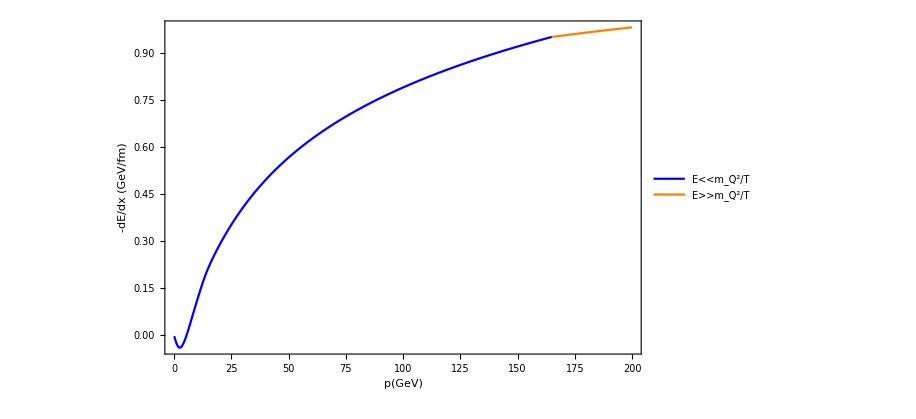

```mathematica
ListPlot[{lowPBottom,highPBottom},AxesLabel->{"p(GeV)", "-dE/dx (GeV/fm)"},PlotStyle->{Blue,Orange},PlotLegends->Placed[LineLegend[{Blue,Orange},{"E<<m_Q^2/T","E>>m_Q^2/T" },LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.15,0.85}],FrameLabel->{{"-dE/dx (GeV/fm)",""},{"p(GeV)","Elastic Energy Loss: Bottom"}},Epilog->Inset[ListPlot[{lowPBottom,highPBottom},PlotRange->{{0,50},{-0.1,0.6}},Joined->True,PlotStyle->{Blue,Orange},Frame->True],{80,0.15},{0,0},{120,120}],Frame->True,Joined->True]
```

```mathematica
crossOverEnergyCharm= x/.FindRoot[energyLossLowP8UsingMCI[aS, 0.25, nF, x,mC]-energyLossHighP12UsingMCI[aS, 0.25, nF, x,mC]==0,{x,16}, AccuracyGoal->6, PrecisionGoal-> 3]
```

17.0037

```mathematica
lowPCharm=Parallelize[Table[{p, 5.068  energyLoss[0.3,0.25, 2, p, mC]}, {p, 0.1,crossOverEnergyCharm,0.1}]]
```

{{0.1,-0.00826299},{0.2,-0.0161025},{0.3,-0.0231413},{0.4,-0.0290835},{0.5,-0.0337321},{0.6,-0.0369885},{0.7,-0.0388392},{0.8,-0.0393347},{0.9,-0.0385688},{1.,-0.0366596},{1.1,-0.0337351},{1.2,-0.0299232},{1.3,-0.0253459},{1.4,-0.0201154},{1.5,-0.014333},{1.6,-0.00808879},{1.7,-0.00146197},{1.8,0.00547826},{1.9,0.0126717},{2.,0.0200662},{2.1,0.0276166},{2.2,0.0352842},{2.3,0.0430356},{2.4,0.0508419},{2.5,0.0586786},{2.6,0.0665247},{2.7,0.0743623},{2.8,0.0821761},{2.9,0.0899532},{3.,0.0976827},{3.1,0.105355},{3.2,0.112964},{3.3,0.120502},{3.4,0.127964},{3.5,0.135346},{3.6,0.142644},{3.7,0.149857},{3.8,0.156982},{3.9,0.164018},{4.,0.170963},{4.1,0.177799},{4.2,0.184362},{4.3,0.190647},{4.4,0.196695},{4.5,0.202539},{4.6,0.208205},{4.7,0.213716},{4.8,0.21909},{4.9,0.224343},{5.,0.229487},{5.1,0.234534},{5.2,0.239492},{5.3,0.244369},{5.4,0.249171},{5.5,0.253905},{5.6,0.258574},{5.7,0.263183},{5.8,0.267734},{5.9,0.272231},{6.,0.276677},{6.1,0.281073},{6.2,0.285421},{6.3,0.289723},{6.4,0.293981},{6.5,0.298195},{6.6,0.302367},{6.7,0.306498},{6.8,0.310588},{6.9,0.314639},{7.,0.318651},{7.1,0.322626},{7.2,0.326562},{7.3,0.330463},{7.4,0.334326},{7.5,0.338155},{7.6,0.341948},{7.7,0.345707},{7.8,0.349431},{7.9,0.353122},{8.,0.35678},{8.1,0.360404},{8.2,0.363997},{8.3,0.367558},{8.4,0.371087},{8.5,0.374585},{8.6,0.378052},{8.7,0.38149},{8.8,0.384897},{8.9,0.388274},{9.,0.391623},{9.1,0.394943},{9.2,0.398234},{9.3,0.401498},{9.4,0.404734},{9.5,0.407942},{9.6,0.411124},{9.7,0.414278},{9.8,0.417407},{9.9,0.42051},{10.,0.423587},{10.1,0.426639},{10.2,0.429666},{10.3,0.432668},{10.4,0.435646},{10.5,0.438601},{10.6,0.441531},{10.7,0.444438},{10.8,0.447322},{10.9,0.450184},{11.,0.453023},{11.1,0.455839},{11.2,0.458634},{11.3,0.461408},{11.4,0.46416},{11.5,0.466891},{11.6,0.469601},{11.7,0.472291},{11.8,0.47496},{11.9,0.47761},{12.,0.48024},{12.1,0.48285},{12.2,0.485441},{12.3,0.488014},{12.4,0.490567},{12.5,0.493102},{12.6,0.495619},{12.7,0.498118},{12.8,0.500599},{12.9,0.503062},{13.,0.505508},{13.1,0.507937},{13.2,0.510349},{13.3,0.512744},{13.4,0.515123},{13.5,0.517485},{13.6,0.519831},{13.7,0.522162},{13.8,0.524476},{13.9,0.526775},{14.,0.529059},{14.1,0.531328},{14.2,0.533581},{14.3,0.53582},{14.4,0.538044},{14.5,0.540254},{14.6,0.54245},{14.7,0.544631},{14.8,0.546798},{14.9,0.548952},{15.,0.551092},{15.1,0.553219},{15.2,0.555332},{15.3,0.557432},{15.4,0.559519},{15.5,0.561593},{15.6,0.563655},{15.7,0.565704},{15.8,0.567741},{15.9,0.569765},{16.,0.571777},{16.1,0.573777},{16.2,0.575765},{16.3,0.577742},{16.4,0.579707},{16.5,0.58166},{16.6,0.583602},{16.7,0.585533},{16.8,0.587452},{16.9,0.589361},{17.,0.591259}}

```mathematica
highPCharm=Parallelize[Table[{p, 5.068  energyLoss[0.3,0.25, 2, p, mC]}, {p,crossOverEnergyCharm,200,0.1}]]
```

{{17.0037,1.18266 HeavisideTheta[0.]},{17.1037,0.592255},{17.2037,0.593176},{17.3037,0.594092},{17.4037,0.595002},{17.5037,0.595908},{17.6037,0.596808},{17.7037,0.597704},{17.8037,0.598594},{17.9037,0.59948},{18.0037,0.60036},{18.1037,0.601236},{18.2037,0.602107},{18.3037,0.602974},{18.4037,0.603835},{18.5037,0.604693},{18.6037,0.605545},{18.7037,0.606393},{18.8037,0.607237},{18.9037,0.608076},{19.0037,0.608911},{19.1037,0.609741},{19.2037,0.610567},{19.3037,0.611389},{19.4037,0.612207},{19.5037,0.613021},{19.6037,0.61383},{19.7037,0.614636},{19.8037,0.615437},{19.9037,0.616234},{20.0037,0.617028},{20.1037,0.617817},{20.2037,0.618603},{20.3037,0.619385},{20.4037,0.620163},{20.5037,0.620937},{20.6037,0.621708},{20.7037,0.622475},{20.8037,0.623238},{20.9037,0.623997},{21.0037,0.624753},{21.1037,0.625506},{21.2037,0.626255},{21.3037,0.627},{21.4037,0.627742},{21.5037,0.62848},{21.6037,0.629216},{21.7037,0.629947},{21.8037,0.630676},{21.9037,0.631401},{22.0037,0.632123},{22.1037,0.632841},{22.2037,0.633557},{22.3037,0.634269},{22.4037,0.634978},{22.5037,0.635684},{22.6037,0.636387},{22.7037,0.637087},{22.8037,0.637783},{22.9037,0.638477},{23.0037,0.639168},{23.1037,0.639855},{23.2037,0.64054},{23.3037,0.641222},{23.4037,0.641901},{23.5037,0.642577},{23.6037,0.64325},{23.7037,0.643921},{23.8037,0.644588},{23.9037,0.645253},{24.0037,0.645915},{24.1037,0.646575},{24.2037,0.647231},{24.3037,0.647885},{24.4037,0.648537},{24.5037,0.649185},{24.6037,0.649831},{24.7037,0.650475},{24.8037,0.651116},{24.9037,0.651754},{25.0037,0.65239},{25.1037,0.653023},{25.2037,0.653654},{25.3037,0.654282},{25.4037,0.654908},{25.5037,0.655531},{25.6037,0.656152},{25.7037,0.65677},{25.8037,0.657387},{25.9037,0.658},{26.0037,0.658612},{26.1037,0.659221},{26.2037,0.659828},{26.3037,0.660432},{26.4037,0.661034},{26.5037,0.661634},{26.6037,0.662232},{26.7037,0.662827},{26.8037,0.663421},{26.9037,0.664012},{27.0037,0.664601},{27.1037,0.665187},{27.2037,0.665772},{27.3037,0.666354},{27.4037,0.666935},{27.5037,0.667513},{27.6037,0.668089},{27.7037,0.668663},{27.8037,0.669235},{27.9037,0.669805},{28.0037,0.670373},{28.1037,0.670939},{28.2037,0.671503},{28.3037,0.672065},{28.4037,0.672625},{28.5037,0.673183},{28.6037,0.673739},{28.7037,0.674293},{28.8037,0.674845},{28.9037,0.675395},{29.0037,0.675944},{29.1037,0.67649},{29.2037,0.677035},{29.3037,0.677578},{29.4037,0.678119},{29.5037,0.678658},{29.6037,0.679195},{29.7037,0.679731},{29.8037,0.680265},{29.9037,0.680797},{30.0037,0.681327},{30.1037,0.681855},{30.2037,0.682382},{30.3037,0.682907},{30.4037,0.68343},{30.5037,0.683952},{30.6037,0.684472},{30.7037,0.68499},{30.8037,0.685506},{30.9037,0.686021},{31.0037,0.686534},{31.1037,0.687046},{31.2037,0.687556},{31.3037,0.688064},{31.4037,0.688571},{31.5037,0.689076},{31.6037,0.689579},{31.7037,0.690081},{31.8037,0.690581},{31.9037,0.69108},{32.0037,0.691577},{32.1037,0.692073},{32.2037,0.692567},{32.3037,0.69306},{32.4037,0.693551},{32.5037,0.69404},{32.6037,0.694528},{32.7037,0.695015},{32.8037,0.6955},{32.9037,0.695984},{33.0037,0.696466},{33.1037,0.696946},{33.2037,0.697426},{33.3037,0.697903},{33.4037,0.69838},{33.5037,0.698855},{33.6037,0.699328},{33.7037,0.699801},{33.8037,0.700271},{33.9037,0.700741},{34.0037,0.701209},{34.1037,0.701675},{34.2037,0.702141},{34.3037,0.702605},{34.4037,0.703067},{34.5037,0.703528},{34.6037,0.703988},{34.7037,0.704447},{34.8037,0.704904},{34.9037,0.70536},{35.0037,0.705815},{35.1037,0.706268},{35.2037,0.70672},{35.3037,0.707171},{35.4037,0.707621},{35.5037,0.708069},{35.6037,0.708516},{35.7037,0.708962},{35.8037,0.709406},{35.9037,0.709849},{36.0037,0.710292},{36.1037,0.710732},{36.2037,0.711172},{36.3037,0.71161},{36.4037,0.712048},{36.5037,0.712484},{36.6037,0.712919},{36.7037,0.713352},{36.8037,0.713785},{36.9037,0.714216},{37.0037,0.714646},{37.1037,0.715075},{37.2037,0.715503},{37.3037,0.71593},{37.4037,0.716355},{37.5037,0.71678},{37.6037,0.717203},{37.7037,0.717625},{37.8037,0.718046},{37.9037,0.718466},{38.0037,0.718885},{38.1037,0.719303},{38.2037,0.719719},{38.3037,0.720135},{38.4037,0.720549},{38.5037,0.720963},{38.6037,0.721375},{38.7037,0.721786},{38.8037,0.722197},{38.9037,0.722606},{39.0037,0.723014},{39.1037,0.723421},{39.2037,0.723827},{39.3037,0.724232},{39.4037,0.724636},{39.5037,0.725039},{39.6037,0.725441},{39.7037,0.725842},{39.8037,0.726242},{39.9037,0.726641},{40.0037,0.727039},{40.1037,0.727436},{40.2037,0.727832},{40.3037,0.728227},{40.4037,0.728621},{40.5037,0.729014},{40.6037,0.729406},{40.7037,0.729797},{40.8037,0.730187},{40.9037,0.730576},{41.0037,0.730965},{41.1037,0.731352},{41.2037,0.731738},{41.3037,0.732124},{41.4037,0.732508},{41.5037,0.732892},{41.6037,0.733274},{41.7037,0.733656},{41.8037,0.734037},{41.9037,0.734417},{42.0037,0.734796},{42.1037,0.735174},{42.2037,0.735551},{42.3037,0.735928},{42.4037,0.736303},{42.5037,0.736678},{42.6037,0.737051},{42.7037,0.737424},{42.8037,0.737796},{42.9037,0.738167},{43.0037,0.738537},{43.1037,0.738907},{43.2037,0.739275},{43.3037,0.739643},{43.4037,0.74001},{43.5037,0.740376},{43.6037,0.740741},{43.7037,0.741105},{43.8037,0.741469},{43.9037,0.741831},{44.0037,0.742193},{44.1037,0.742554},{44.2037,0.742914},{44.3037,0.743274},{44.4037,0.743632},{44.5037,0.74399},{44.6037,0.744347},{44.7037,0.744703},{44.8037,0.745058},{44.9037,0.745413},{45.0037,0.745767},{45.1037,0.74612},{45.2037,0.746472},{45.3037,0.746823},{45.4037,0.747174},{45.5037,0.747524},{45.6037,0.747873},{45.7037,0.748221},{45.8037,0.748569},{45.9037,0.748916},{46.0037,0.749262},{46.1037,0.749607},{46.2037,0.749952},{46.3037,0.750296},{46.4037,0.750639},{46.5037,0.750981},{46.6037,0.751323},{46.7037,0.751664},{46.8037,0.752004},{46.9037,0.752344},{47.0037,0.752682},{47.1037,0.75302},{47.2037,0.753358},{47.3037,0.753694},{47.4037,0.75403},{47.5037,0.754365},{47.6037,0.7547},{47.7037,0.755034},{47.8037,0.755367},{47.9037,0.755699},{48.0037,0.756031},{48.1037,0.756362},{48.2037,0.756692},{48.3037,0.757022},{48.4037,0.757351},{48.5037,0.757679},{48.6037,0.758007},{48.7037,0.758333},{48.8037,0.75866},{48.9037,0.758985},{49.0037,0.75931},{49.1037,0.759635},{49.2037,0.759958},{49.3037,0.760281},{49.4037,0.760603},{49.5037,0.760925},{49.6037,0.761246},{49.7037,0.761566},{49.8037,0.761886},{49.9037,0.762205},{50.0037,0.762524},{50.1037,0.762841},{50.2037,0.763159},{50.3037,0.763475},{50.4037,0.763791},{50.5037,0.764106},{50.6037,0.764421},{50.7037,0.764735},{50.8037,0.765049},{50.9037,0.765361},{51.0037,0.765674},{51.1037,0.765985},{51.2037,0.766296},{51.3037,0.766606},{51.4037,0.766916},{51.5037,0.767225},{51.6037,0.767534},{51.7037,0.767842},{51.8037,0.768149},{51.9037,0.768456},{52.0037,0.768762},{52.1037,0.769068},{52.2037,0.769373},{52.3037,0.769677},{52.4037,0.769981},{52.5037,0.770285},{52.6037,0.770587},{52.7037,0.770889},{52.8037,0.771191},{52.9037,0.771492},{53.0037,0.771792},{53.1037,0.772092},{53.2037,0.772392},{53.3037,0.77269},{53.4037,0.772989},{53.5037,0.773286},{53.6037,0.773583},{53.7037,0.77388},{53.8037,0.774176},{53.9037,0.774471},{54.0037,0.774766},{54.1037,0.77506},{54.2037,0.775354},{54.3037,0.775647},{54.4037,0.77594},{54.5037,0.776232},{54.6037,0.776524},{54.7037,0.776815},{54.8037,0.777106},{54.9037,0.777396},{55.0037,0.777685},{55.1037,0.777974},{55.2037,0.778263},{55.3037,0.77855},{55.4037,0.778838},{55.5037,0.779125},{55.6037,0.779411},{55.7037,0.779697},{55.8037,0.779982},{55.9037,0.780267},{56.0037,0.780552},{56.1037,0.780835},{56.2037,0.781119},{56.3037,0.781402},{56.4037,0.781684},{56.5037,0.781966},{56.6037,0.782247},{56.7037,0.782528},{56.8037,0.782808},{56.9037,0.783088},{57.0037,0.783368},{57.1037,0.783646},{57.2037,0.783925},{57.3037,0.784203},{57.4037,0.78448},{57.5037,0.784757},{57.6037,0.785033},{57.7037,0.785309},{57.8037,0.785585},{57.9037,0.78586},{58.0037,0.786134},{58.1037,0.786409},{58.2037,0.786682},{58.3037,0.786955},{58.4037,0.787228},{58.5037,0.7875},{58.6037,0.787772},{58.7037,0.788043},{58.8037,0.788314},{58.9037,0.788584},{59.0037,0.788854},{59.1037,0.789124},{59.2037,0.789393},{59.3037,0.789661},{59.4037,0.789929},{59.5037,0.790197},{59.6037,0.790464},{59.7037,0.790731},{59.8037,0.790997},{59.9037,0.791263},{60.0037,0.791528},{60.1037,0.791793},{60.2037,0.792058},{60.3037,0.792322},{60.4037,0.792586},{60.5037,0.792849},{60.6037,0.793112},{60.7037,0.793374},{60.8037,0.793636},{60.9037,0.793897},{61.0037,0.794158},{61.1037,0.794419},{61.2037,0.794679},{61.3037,0.794939},{61.4037,0.795198},{61.5037,0.795457},{61.6037,0.795716},{61.7037,0.795974},{61.8037,0.796231},{61.9037,0.796489},{62.0037,0.796746},{62.1037,0.797002},{62.2037,0.797258},{62.3037,0.797514},{62.4037,0.797769},{62.5037,0.798024},{62.6037,0.798278},{62.7037,0.798532},{62.8037,0.798785},{62.9037,0.799039},{63.0037,0.799291},{63.1037,0.799544},{63.2037,0.799796},{63.3037,0.800047},{63.4037,0.800298},{63.5037,0.800549},{63.6037,0.8008},{63.7037,0.80105},{63.8037,0.801299},{63.9037,0.801548},{64.0037,0.801797},{64.1037,0.802046},{64.2037,0.802294},{64.3037,0.802541},{64.4037,0.802789},{64.5037,0.803036},{64.6037,0.803282},{64.7037,0.803528},{64.8037,0.803774},{64.9037,0.804019},{65.0037,0.804264},{65.1037,0.804509},{65.2037,0.804753},{65.3037,0.804997},{65.4037,0.805241},{65.5037,0.805484},{65.6037,0.805726},{65.7037,0.805969},{65.8037,0.806211},{65.9037,0.806452},{66.0037,0.806694},{66.1037,0.806935},{66.2037,0.807175},{66.3037,0.807415},{66.4037,0.807655},{66.5037,0.807895},{66.6037,0.808134},{66.7037,0.808373},{66.8037,0.808611},{66.9037,0.808849},{67.0037,0.809087},{67.1037,0.809324},{67.2037,0.809561},{67.3037,0.809798},{67.4037,0.810034},{67.5037,0.81027},{67.6037,0.810505},{67.7037,0.810741},{67.8037,0.810975},{67.9037,0.81121},{68.0037,0.811444},{68.1037,0.811678},{68.2037,0.811911},{68.3037,0.812145},{68.4037,0.812377},{68.5037,0.81261},{68.6037,0.812842},{68.7037,0.813074},{68.8037,0.813305},{68.9037,0.813536},{69.0037,0.813767},{69.1037,0.813998},{69.2037,0.814228},{69.3037,0.814458},{69.4037,0.814687},{69.5037,0.814916},{69.6037,0.815145},{69.7037,0.815374},{69.8037,0.815602},{69.9037,0.815829},{70.0037,0.816057},{70.1037,0.816284},{70.2037,0.816511},{70.3037,0.816738},{70.4037,0.816964},{70.5037,0.81719},{70.6037,0.817415},{70.7037,0.81764},{70.8037,0.817865},{70.9037,0.81809},{71.0037,0.818314},{71.1037,0.818538},{71.2037,0.818762},{71.3037,0.818985},{71.4037,0.819208},{71.5037,0.819431},{71.6037,0.819653},{71.7037,0.819876},{71.8037,0.820097},{71.9037,0.820319},{72.0037,0.82054},{72.1037,0.820761},{72.2037,0.820981},{72.3037,0.821202},{72.4037,0.821422},{72.5037,0.821641},{72.6037,0.821861},{72.7037,0.82208},{72.8037,0.822298},{72.9037,0.822517},{73.0037,0.822735},{73.1037,0.822953},{73.2037,0.82317},{73.3037,0.823388},{73.4037,0.823605},{73.5037,0.823821},{73.6037,0.824038},{73.7037,0.824254},{73.8037,0.82447},{73.9037,0.824685},{74.0037,0.8249},{74.1037,0.825115},{74.2037,0.82533},{74.3037,0.825544},{74.4037,0.825758},{74.5037,0.825972},{74.6037,0.826185},{74.7037,0.826399},{74.8037,0.826612},{74.9037,0.826824},{75.0037,0.827036},{75.1037,0.827249},{75.2037,0.82746},{75.3037,0.827672},{75.4037,0.827883},{75.5037,0.828094},{75.6037,0.828305},{75.7037,0.828515},{75.8037,0.828725},{75.9037,0.828935},{76.0037,0.829144},{76.1037,0.829354},{76.2037,0.829563},{76.3037,0.829771},{76.4037,0.82998},{76.5037,0.830188},{76.6037,0.830396},{76.7037,0.830604},{76.8037,0.830811},{76.9037,0.831018},{77.0037,0.831225},{77.1037,0.831431},{77.2037,0.831638},{77.3037,0.831844},{77.4037,0.832049},{77.5037,0.832255},{77.6037,0.83246},{77.7037,0.832665},{77.8037,0.83287},{77.9037,0.833074},{78.0037,0.833278},{78.1037,0.833482},{78.2037,0.833686},{78.3037,0.833889},{78.4037,0.834092},{78.5037,0.834295},{78.6037,0.834498},{78.7037,0.8347},{78.8037,0.834902},{78.9037,0.835104},{79.0037,0.835306},{79.1037,0.835507},{79.2037,0.835708},{79.3037,0.835909},{79.4037,0.83611},{79.5037,0.83631},{79.6037,0.83651},{79.7037,0.83671},{79.8037,0.836909},{79.9037,0.837109},{80.0037,0.837308},{80.1037,0.837507},{80.2037,0.837705},{80.3037,0.837903},{80.4037,0.838101},{80.5037,0.838299},{80.6037,0.838497},{80.7037,0.838694},{80.8037,0.838891},{80.9037,0.839088},{81.0037,0.839285},{81.1037,0.839481},{81.2037,0.839677},{81.3037,0.839873},{81.4037,0.840069},{81.5037,0.840264},{81.6037,0.840459},{81.7037,0.840654},{81.8037,0.840849},{81.9037,0.841043},{82.0037,0.841238},{82.1037,0.841432},{82.2037,0.841625},{82.3037,0.841819},{82.4037,0.842012},{82.5037,0.842205},{82.6037,0.842398},{82.7037,0.842591},{82.8037,0.842783},{82.9037,0.842975},{83.0037,0.843167},{83.1037,0.843358},{83.2037,0.84355},{83.3037,0.843741},{83.4037,0.843932},{83.5037,0.844123},{83.6037,0.844313},{83.7037,0.844504},{83.8037,0.844694},{83.9037,0.844883},{84.0037,0.845073},{84.1037,0.845262},{84.2037,0.845451},{84.3037,0.84564},{84.4037,0.845829},{84.5037,0.846018},{84.6037,0.846206},{84.7037,0.846394},{84.8037,0.846582},{84.9037,0.846769},{85.0037,0.846956},{85.1037,0.847144},{85.2037,0.847331},{85.3037,0.847517},{85.4037,0.847704},{85.5037,0.84789},{85.6037,0.848076},{85.7037,0.848262},{85.8037,0.848447},{85.9037,0.848633},{86.0037,0.848818},{86.1037,0.849003},{86.2037,0.849188},{86.3037,0.849372},{86.4037,0.849557},{86.5037,0.849741},{86.6037,0.849925},{86.7037,0.850108},{86.8037,0.850292},{86.9037,0.850475},{87.0037,0.850658},{87.1037,0.850841},{87.2037,0.851024},{87.3037,0.851206},{87.4037,0.851388},{87.5037,0.85157},{87.6037,0.851752},{87.7037,0.851934},{87.8037,0.852115},{87.9037,0.852296},{88.0037,0.852477},{88.1037,0.852658},{88.2037,0.852838},{88.3037,0.853019},{88.4037,0.853199},{88.5037,0.853379},{88.6037,0.853559},{88.7037,0.853738},{88.8037,0.853918},{88.9037,0.854097},{89.0037,0.854276},{89.1037,0.854454},{89.2037,0.854633},{89.3037,0.854811},{89.4037,0.854989},{89.5037,0.855167},{89.6037,0.855345},{89.7037,0.855523},{89.8037,0.8557},{89.9037,0.855877},{90.0037,0.856054},{90.1037,0.856231},{90.2037,0.856407},{90.3037,0.856584},{90.4037,0.85676},{90.5037,0.856936},{90.6037,0.857112},{90.7037,0.857287},{90.8037,0.857463},{90.9037,0.857638},{91.0037,0.857813},{91.1037,0.857988},{91.2037,0.858162},{91.3037,0.858337},{91.4037,0.858511},{91.5037,0.858685},{91.6037,0.858859},{91.7037,0.859032},{91.8037,0.859206},{91.9037,0.859379},{92.0037,0.859552},{92.1037,0.859725},{92.2037,0.859898},{92.3037,0.86007},{92.4037,0.860243},{92.5037,0.860415},{92.6037,0.860587},{92.7037,0.860759},{92.8037,0.86093},{92.9037,0.861102},{93.0037,0.861273},{93.1037,0.861444},{93.2037,0.861615},{93.3037,0.861786},{93.4037,0.861956},{93.5037,0.862126},{93.6037,0.862297},{93.7037,0.862467},{93.8037,0.862636},{93.9037,0.862806},{94.0037,0.862975},{94.1037,0.863145},{94.2037,0.863314},{94.3037,0.863483},{94.4037,0.863651},{94.5037,0.86382},{94.6037,0.863988},{94.7037,0.864156},{94.8037,0.864324},{94.9037,0.864492},{95.0037,0.86466},{95.1037,0.864827},{95.2037,0.864994},{95.3037,0.865162},{95.4037,0.865329},{95.5037,0.865495},{95.6037,0.865662},{95.7037,0.865828},{95.8037,0.865994},{95.9037,0.866161},{96.0037,0.866326},{96.1037,0.866492},{96.2037,0.866658},{96.3037,0.866823},{96.4037,0.866988},{96.5037,0.867153},{96.6037,0.867318},{96.7037,0.867483},{96.8037,0.867647},{96.9037,0.867812},{97.0037,0.867976},{97.1037,0.86814},{97.2037,0.868304},{97.3037,0.868467},{97.4037,0.868631},{97.5037,0.868794},{97.6037,0.868957},{97.7037,0.86912},{97.8037,0.869283},{97.9037,0.869446},{98.0037,0.869608},{98.1037,0.869771},{98.2037,0.869933},{98.3037,0.870095},{98.4037,0.870257},{98.5037,0.870418},{98.6037,0.87058},{98.7037,0.870741},{98.8037,0.870903},{98.9037,0.871064},{99.0037,0.871224},{99.1037,0.871385},{99.2037,0.871546},{99.3037,0.871706},{99.4037,0.871866},{99.5037,0.872026},{99.6037,0.872186},{99.7037,0.872346},{99.8037,0.872506},{99.9037,0.872665},{100.004,0.872824},{100.104,0.872983},{100.204,0.873142},{100.304,0.873301},{100.404,0.87346},{100.504,0.873618},{100.604,0.873776},{100.704,0.873935},{100.804,0.874093},{100.904,0.87425},{101.004,0.874408},{101.104,0.874566},{101.204,0.874723},{101.304,0.87488},{101.404,0.875037},{101.504,0.875194},{101.604,0.875351},{101.704,0.875507},{101.804,0.875664},{101.904,0.87582},{102.004,0.875976},{102.104,0.876132},{102.204,0.876288},{102.304,0.876444},{102.404,0.876599},{102.504,0.876755},{102.604,0.87691},{102.704,0.877065},{102.804,0.87722},{102.904,0.877375},{103.004,0.877529},{103.104,0.877684},{103.204,0.877838},{103.304,0.877992},{103.404,0.878146},{103.504,0.8783},{103.604,0.878454},{103.704,0.878607},{103.804,0.878761},{103.904,0.878914},{104.004,0.879067},{104.104,0.87922},{104.204,0.879373},{104.304,0.879526},{104.404,0.879678},{104.504,0.879831},{104.604,0.879983},{104.704,0.880135},{104.804,0.880287},{104.904,0.880439},{105.004,0.88059},{105.104,0.880742},{105.204,0.880893},{105.304,0.881045},{105.404,0.881196},{105.504,0.881347},{105.604,0.881497},{105.704,0.881648},{105.804,0.881799},{105.904,0.881949},{106.004,0.882099},{106.104,0.882249},{106.204,0.882399},{106.304,0.882549},{106.404,0.882699},{106.504,0.882848},{106.604,0.882998},{106.704,0.883147},{106.804,0.883296},{106.904,0.883445},{107.004,0.883594},{107.104,0.883743},{107.204,0.883891},{107.304,0.88404},{107.404,0.884188},{107.504,0.884336},{107.604,0.884484},{107.704,0.884632},{107.804,0.88478},{107.904,0.884927},{108.004,0.885075},{108.104,0.885222},{108.204,0.885369},{108.304,0.885516},{108.404,0.885663},{108.504,0.88581},{108.604,0.885957},{108.704,0.886103},{108.804,0.886249},{108.904,0.886396},{109.004,0.886542},{109.104,0.886688},{109.204,0.886834},{109.304,0.886979},{109.404,0.887125},{109.504,0.88727},{109.604,0.887416},{109.704,0.887561},{109.804,0.887706},{109.904,0.887851},{110.004,0.887995},{110.104,0.88814},{110.204,0.888285},{110.304,0.888429},{110.404,0.888573},{110.504,0.888717},{110.604,0.888861},{110.704,0.889005},{110.804,0.889149},{110.904,0.889293},{111.004,0.889436},{111.104,0.889579},{111.204,0.889723},{111.304,0.889866},{111.404,0.890009},{111.504,0.890151},{111.604,0.890294},{111.704,0.890437},{111.804,0.890579},{111.904,0.890721},{112.004,0.890864},{112.104,0.891006},{112.204,0.891148},{112.304,0.891289},{112.404,0.891431},{112.504,0.891573},{112.604,0.891714},{112.704,0.891855},{112.804,0.891997},{112.904,0.892138},{113.004,0.892279},{113.104,0.892419},{113.204,0.89256},{113.304,0.892701},{113.404,0.892841},{113.504,0.892981},{113.604,0.893122},{113.704,0.893262},{113.804,0.893402},{113.904,0.893541},{114.004,0.893681},{114.104,0.893821},{114.204,0.89396},{114.304,0.894099},{114.404,0.894239},{114.504,0.894378},{114.604,0.894517},{114.704,0.894656},{114.804,0.894794},{114.904,0.894933},{115.004,0.895071},{115.104,0.89521},{115.204,0.895348},{115.304,0.895486},{115.404,0.895624},{115.504,0.895762},{115.604,0.8959},{115.704,0.896037},{115.804,0.896175},{115.904,0.896312},{116.004,0.89645},{116.104,0.896587},{116.204,0.896724},{116.304,0.896861},{116.404,0.896998},{116.504,0.897134},{116.604,0.897271},{116.704,0.897407},{116.804,0.897544},{116.904,0.89768},{117.004,0.897816},{117.104,0.897952},{117.204,0.898088},{117.304,0.898224},{117.404,0.898359},{117.504,0.898495},{117.604,0.89863},{117.704,0.898766},{117.804,0.898901},{117.904,0.899036},{118.004,0.899171},{118.104,0.899306},{118.204,0.89944},{118.304,0.899575},{118.404,0.899709},{118.504,0.899844},{118.604,0.899978},{118.704,0.900112},{118.804,0.900246},{118.904,0.90038},{119.004,0.900514},{119.104,0.900648},{119.204,0.900781},{119.304,0.900915},{119.404,0.901048},{119.504,0.901182},{119.604,0.901315},{119.704,0.901448},{119.804,0.901581},{119.904,0.901714},{120.004,0.901846},{120.104,0.901979},{120.204,0.902111},{120.304,0.902244},{120.404,0.902376},{120.504,0.902508},{120.604,0.90264},{120.704,0.902772},{120.804,0.902904},{120.904,0.903036},{121.004,0.903167},{121.104,0.903299},{121.204,0.90343},{121.304,0.903561},{121.404,0.903693},{121.504,0.903824},{121.604,0.903955},{121.704,0.904086},{121.804,0.904216},{121.904,0.904347},{122.004,0.904477},{122.104,0.904608},{122.204,0.904738},{122.304,0.904868},{122.404,0.904999},{122.504,0.905129},{122.604,0.905258},{122.704,0.905388},{122.804,0.905518},{122.904,0.905648},{123.004,0.905777},{123.104,0.905906},{123.204,0.906036},{123.304,0.906165},{123.404,0.906294},{123.504,0.906423},{123.604,0.906552},{123.704,0.90668},{123.804,0.906809},{123.904,0.906938},{124.004,0.907066},{124.104,0.907194},{124.204,0.907323},{124.304,0.907451},{124.404,0.907579},{124.504,0.907707},{124.604,0.907834},{124.704,0.907962},{124.804,0.90809},{124.904,0.908217},{125.004,0.908345},{125.104,0.908472},{125.204,0.908599},{125.304,0.908726},{125.404,0.908853},{125.504,0.90898},{125.604,0.909107},{125.704,0.909234},{125.804,0.90936},{125.904,0.909487},{126.004,0.909613},{126.104,0.909739},{126.204,0.909866},{126.304,0.909992},{126.404,0.910118},{126.504,0.910243},{126.604,0.910369},{126.704,0.910495},{126.804,0.910621},{126.904,0.910746},{127.004,0.910871},{127.104,0.910997},{127.204,0.911122},{127.304,0.911247},{127.404,0.911372},{127.504,0.911497},{127.604,0.911622},{127.704,0.911746},{127.804,0.911871},{127.904,0.911996},{128.004,0.91212},{128.104,0.912244},{128.204,0.912369},{128.304,0.912493},{128.404,0.912617},{128.504,0.912741},{128.604,0.912864},{128.704,0.912988},{128.804,0.913112},{128.904,0.913235},{129.004,0.913359},{129.104,0.913482},{129.204,0.913605},{129.304,0.913729},{129.404,0.913852},{129.504,0.913975},{129.604,0.914098},{129.704,0.91422},{129.804,0.914343},{129.904,0.914466},{130.004,0.914588},{130.104,0.914711},{130.204,0.914833},{130.304,0.914955},{130.404,0.915077},{130.504,0.915199},{130.604,0.915321},{130.704,0.915443},{130.804,0.915565},{130.904,0.915686},{131.004,0.915808},{131.104,0.915929},{131.204,0.916051},{131.304,0.916172},{131.404,0.916293},{131.504,0.916414},{131.604,0.916535},{131.704,0.916656},{131.804,0.916777},{131.904,0.916898},{132.004,0.917019},{132.104,0.917139},{132.204,0.91726},{132.304,0.91738},{132.404,0.9175},{132.504,0.91762},{132.604,0.91774},{132.704,0.917861},{132.804,0.91798},{132.904,0.9181},{133.004,0.91822},{133.104,0.91834},{133.204,0.918459},{133.304,0.918579},{133.404,0.918698},{133.504,0.918817},{133.604,0.918937},{133.704,0.919056},{133.804,0.919175},{133.904,0.919294},{134.004,0.919412},{134.104,0.919531},{134.204,0.91965},{134.304,0.919768},{134.404,0.919887},{134.504,0.920005},{134.604,0.920124},{134.704,0.920242},{134.804,0.92036},{134.904,0.920478},{135.004,0.920596},{135.104,0.920714},{135.204,0.920832},{135.304,0.920949},{135.404,0.921067},{135.504,0.921185},{135.604,0.921302},{135.704,0.921419},{135.804,0.921537},{135.904,0.921654},{136.004,0.921771},{136.104,0.921888},{136.204,0.922005},{136.304,0.922122},{136.404,0.922238},{136.504,0.922355},{136.604,0.922472},{136.704,0.922588},{136.804,0.922705},{136.904,0.922821},{137.004,0.922937},{137.104,0.923053},{137.204,0.923169},{137.304,0.923285},{137.404,0.923401},{137.504,0.923517},{137.604,0.923633},{137.704,0.923748},{137.804,0.923864},{137.904,0.92398},{138.004,0.924095},{138.104,0.92421},{138.204,0.924325},{138.304,0.924441},{138.404,0.924556},{138.504,0.924671},{138.604,0.924786},{138.704,0.9249},{138.804,0.925015},{138.904,0.92513},{139.004,0.925244},{139.104,0.925359},{139.204,0.925473},{139.304,0.925588},{139.404,0.925702},{139.504,0.925816},{139.604,0.92593},{139.704,0.926044},{139.804,0.926158},{139.904,0.926272},{140.004,0.926385},{140.104,0.926499},{140.204,0.926613},{140.304,0.926726},{140.404,0.92684},{140.504,0.926953},{140.604,0.927066},{140.704,0.927179},{140.804,0.927293},{140.904,0.927406},{141.004,0.927519},{141.104,0.927631},{141.204,0.927744},{141.304,0.927857},{141.404,0.92797},{141.504,0.928082},{141.604,0.928195},{141.704,0.928307},{141.804,0.928419},{141.904,0.928531},{142.004,0.928644},{142.104,0.928756},{142.204,0.928868},{142.304,0.92898},{142.404,0.929091},{142.504,0.929203},{142.604,0.929315},{142.704,0.929426},{142.804,0.929538},{142.904,0.929649},{143.004,0.929761},{143.104,0.929872},{143.204,0.929983},{143.304,0.930094},{143.404,0.930205},{143.504,0.930316},{143.604,0.930427},{143.704,0.930538},{143.804,0.930649},{143.904,0.93076},{144.004,0.93087},{144.104,0.930981},{144.204,0.931091},{144.304,0.931201},{144.404,0.931312},{144.504,0.931422},{144.604,0.931532},{144.704,0.931642},{144.804,0.931752},{144.904,0.931862},{145.004,0.931972},{145.104,0.932082},{145.204,0.932191},{145.304,0.932301},{145.404,0.93241},{145.504,0.93252},{145.604,0.932629},{145.704,0.932739},{145.804,0.932848},{145.904,0.932957},{146.004,0.933066},{146.104,0.933175},{146.204,0.933284},{146.304,0.933393},{146.404,0.933502},{146.504,0.93361},{146.604,0.933719},{146.704,0.933827},{146.804,0.933936},{146.904,0.934044},{147.004,0.934153},{147.104,0.934261},{147.204,0.934369},{147.304,0.934477},{147.404,0.934585},{147.504,0.934693},{147.604,0.934801},{147.704,0.934909},{147.804,0.935017},{147.904,0.935124},{148.004,0.935232},{148.104,0.935339},{148.204,0.935447},{148.304,0.935554},{148.404,0.935662},{148.504,0.935769},{148.604,0.935876},{148.704,0.935983},{148.804,0.93609},{148.904,0.936197},{149.004,0.936304},{149.104,0.936411},{149.204,0.936517},{149.304,0.936624},{149.404,0.936731},{149.504,0.936837},{149.604,0.936944},{149.704,0.93705},{149.804,0.937156},{149.904,0.937263},{150.004,0.937369},{150.104,0.937475},{150.204,0.937581},{150.304,0.937687},{150.404,0.937793},{150.504,0.937899},{150.604,0.938004},{150.704,0.93811},{150.804,0.938216},{150.904,0.938321},{151.004,0.938427},{151.104,0.938532},{151.204,0.938637},{151.304,0.938743},{151.404,0.938848},{151.504,0.938953},{151.604,0.939058},{151.704,0.939163},{151.804,0.939268},{151.904,0.939373},{152.004,0.939477},{152.104,0.939582},{152.204,0.939687},{152.304,0.939791},{152.404,0.939896},{152.504,0.94},{152.604,0.940105},{152.704,0.940209},{152.804,0.940313},{152.904,0.940417},{153.004,0.940521},{153.104,0.940625},{153.204,0.940729},{153.304,0.940833},{153.404,0.940937},{153.504,0.941041},{153.604,0.941144},{153.704,0.941248},{153.804,0.941352},{153.904,0.941455},{154.004,0.941558},{154.104,0.941662},{154.204,0.941765},{154.304,0.941868},{154.404,0.941971},{154.504,0.942074},{154.604,0.942177},{154.704,0.94228},{154.804,0.942383},{154.904,0.942486},{155.004,0.942589},{155.104,0.942692},{155.204,0.942794},{155.304,0.942897},{155.404,0.942999},{155.504,0.943102},{155.604,0.943204},{155.704,0.943306},{155.804,0.943408},{155.904,0.943511},{156.004,0.943613},{156.104,0.943715},{156.204,0.943817},{156.304,0.943918},{156.404,0.94402},{156.504,0.944122},{156.604,0.944224},{156.704,0.944325},{156.804,0.944427},{156.904,0.944528},{157.004,0.94463},{157.104,0.944731},{157.204,0.944833},{157.304,0.944934},{157.404,0.945035},{157.504,0.945136},{157.604,0.945237},{157.704,0.945338},{157.804,0.945439},{157.904,0.94554},{158.004,0.945641},{158.104,0.945741},{158.204,0.945842},{158.304,0.945943},{158.404,0.946043},{158.504,0.946144},{158.604,0.946244},{158.704,0.946344},{158.804,0.946445},{158.904,0.946545},{159.004,0.946645},{159.104,0.946745},{159.204,0.946845},{159.304,0.946945},{159.404,0.947045},{159.504,0.947145},{159.604,0.947245},{159.704,0.947344},{159.804,0.947444},{159.904,0.947544},{160.004,0.947643},{160.104,0.947743},{160.204,0.947842},{160.304,0.947941},{160.404,0.948041},{160.504,0.94814},{160.604,0.948239},{160.704,0.948338},{160.804,0.948437},{160.904,0.948536},{161.004,0.948635},{161.104,0.948734},{161.204,0.948833},{161.304,0.948931},{161.404,0.94903},{161.504,0.949129},{161.604,0.949227},{161.704,0.949326},{161.804,0.949424},{161.904,0.949522},{162.004,0.949621},{162.104,0.949719},{162.204,0.949817},{162.304,0.949915},{162.404,0.950013},{162.504,0.950111},{162.604,0.950209},{162.704,0.950307},{162.804,0.950405},{162.904,0.950503},{163.004,0.9506},{163.104,0.950698},{163.204,0.950796},{163.304,0.950893},{163.404,0.950991},{163.504,0.951088},{163.604,0.951185},{163.704,0.951283},{163.804,0.95138},{163.904,0.951477},{164.004,0.951574},{164.104,0.951671},{164.204,0.951768},{164.304,0.951865},{164.404,0.951962},{164.504,0.952059},{164.604,0.952156},{164.704,0.952252},{164.804,0.952349},{164.904,0.952445},{165.004,0.952542},{165.104,0.952638},{165.204,0.952735},{165.304,0.952831},{165.404,0.952927},{165.504,0.953024},{165.604,0.95312},{165.704,0.953216},{165.804,0.953312},{165.904,0.953408},{166.004,0.953504},{166.104,0.9536},{166.204,0.953696},{166.304,0.953791},{166.404,0.953887},{166.504,0.953983},{166.604,0.954078},{166.704,0.954174},{166.804,0.954269},{166.904,0.954365},{167.004,0.95446},{167.104,0.954555},{167.204,0.954651},{167.304,0.954746},{167.404,0.954841},{167.504,0.954936},{167.604,0.955031},{167.704,0.955126},{167.804,0.955221},{167.904,0.955316},{168.004,0.955411},{168.104,0.955505},{168.204,0.9556},{168.304,0.955695},{168.404,0.955789},{168.504,0.955884},{168.604,0.955978},{168.704,0.956072},{168.804,0.956167},{168.904,0.956261},{169.004,0.956355},{169.104,0.956449},{169.204,0.956544},{169.304,0.956638},{169.404,0.956732},{169.504,0.956826},{169.604,0.95692},{169.704,0.957013},{169.804,0.957107},{169.904,0.957201},{170.004,0.957295},{170.104,0.957388},{170.204,0.957482},{170.304,0.957575},{170.404,0.957669},{170.504,0.957762},{170.604,0.957855},{170.704,0.957949},{170.804,0.958042},{170.904,0.958135},{171.004,0.958228},{171.104,0.958321},{171.204,0.958414},{171.304,0.958507},{171.404,0.9586},{171.504,0.958693},{171.604,0.958786},{171.704,0.958879},{171.804,0.958971},{171.904,0.959064},{172.004,0.959157},{172.104,0.959249},{172.204,0.959342},{172.304,0.959434},{172.404,0.959526},{172.504,0.959619},{172.604,0.959711},{172.704,0.959803},{172.804,0.959895},{172.904,0.959987},{173.004,0.960079},{173.104,0.960171},{173.204,0.960263},{173.304,0.960355},{173.404,0.960447},{173.504,0.960539},{173.604,0.960631},{173.704,0.960722},{173.804,0.960814},{173.904,0.960906},{174.004,0.960997},{174.104,0.961089},{174.204,0.96118},{174.304,0.961271},{174.404,0.961363},{174.504,0.961454},{174.604,0.961545},{174.704,0.961636},{174.804,0.961727},{174.904,0.961818},{175.004,0.961909},{175.104,0.962},{175.204,0.962091},{175.304,0.962182},{175.404,0.962273},{175.504,0.962364},{175.604,0.962454},{175.704,0.962545},{175.804,0.962635},{175.904,0.962726},{176.004,0.962817},{176.104,0.962907},{176.204,0.962997},{176.304,0.963088},{176.404,0.963178},{176.504,0.963268},{176.604,0.963358},{176.704,0.963448},{176.804,0.963539},{176.904,0.963629},{177.004,0.963718},{177.104,0.963808},{177.204,0.963898},{177.304,0.963988},{177.404,0.964078},{177.504,0.964168},{177.604,0.964257},{177.704,0.964347},{177.804,0.964436},{177.904,0.964526},{178.004,0.964615},{178.104,0.964705},{178.204,0.964794},{178.304,0.964884},{178.404,0.964973},{178.504,0.965062},{178.604,0.965151},{178.704,0.96524},{178.804,0.965329},{178.904,0.965418},{179.004,0.965507},{179.104,0.965596},{179.204,0.965685},{179.304,0.965774},{179.404,0.965863},{179.504,0.965951},{179.604,0.96604},{179.704,0.966129},{179.804,0.966217},{179.904,0.966306},{180.004,0.966394},{180.104,0.966483},{180.204,0.966571},{180.304,0.966659},{180.404,0.966748},{180.504,0.966836},{180.604,0.966924},{180.704,0.967012},{180.804,0.9671},{180.904,0.967188},{181.004,0.967276},{181.104,0.967364},{181.204,0.967452},{181.304,0.96754},{181.404,0.967628},{181.504,0.967715},{181.604,0.967803},{181.704,0.967891},{181.804,0.967978},{181.904,0.968066},{182.004,0.968153},{182.104,0.968241},{182.204,0.968328},{182.304,0.968416},{182.404,0.968503},{182.504,0.96859},{182.604,0.968677},{182.704,0.968765},{182.804,0.968852},{182.904,0.968939},{183.004,0.969026},{183.104,0.969113},{183.204,0.9692},{183.304,0.969286},{183.404,0.969373},{183.504,0.96946},{183.604,0.969547},{183.704,0.969634},{183.804,0.96972},{183.904,0.969807},{184.004,0.969893},{184.104,0.96998},{184.204,0.970066},{184.304,0.970153},{184.404,0.970239},{184.504,0.970325},{184.604,0.970412},{184.704,0.970498},{184.804,0.970584},{184.904,0.97067},{185.004,0.970756},{185.104,0.970842},{185.204,0.970928},{185.304,0.971014},{185.404,0.9711},{185.504,0.971186},{185.604,0.971272},{185.704,0.971357},{185.804,0.971443},{185.904,0.971529},{186.004,0.971614},{186.104,0.9717},{186.204,0.971786},{186.304,0.971871},{186.404,0.971956},{186.504,0.972042},{186.604,0.972127},{186.704,0.972212},{186.804,0.972298},{186.904,0.972383},{187.004,0.972468},{187.104,0.972553},{187.204,0.972638},{187.304,0.972723},{187.404,0.972808},{187.504,0.972893},{187.604,0.972978},{187.704,0.973063},{187.804,0.973148},{187.904,0.973232},{188.004,0.973317},{188.104,0.973402},{188.204,0.973486},{188.304,0.973571},{188.404,0.973656},{188.504,0.97374},{188.604,0.973824},{188.704,0.973909},{188.804,0.973993},{188.904,0.974077},{189.004,0.974162},{189.104,0.974246},{189.204,0.97433},{189.304,0.974414},{189.404,0.974498},{189.504,0.974582},{189.604,0.974666},{189.704,0.97475},{189.804,0.974834},{189.904,0.974918},{190.004,0.975002},{190.104,0.975086},{190.204,0.975169},{190.304,0.975253},{190.404,0.975337},{190.504,0.97542},{190.604,0.975504},{190.704,0.975587},{190.804,0.975671},{190.904,0.975754},{191.004,0.975838},{191.104,0.975921},{191.204,0.976004},{191.304,0.976087},{191.404,0.976171},{191.504,0.976254},{191.604,0.976337},{191.704,0.97642},{191.804,0.976503},{191.904,0.976586},{192.004,0.976669},{192.104,0.976752},{192.204,0.976835},{192.304,0.976917},{192.404,0.977},{192.504,0.977083},{192.604,0.977166},{192.704,0.977248},{192.804,0.977331},{192.904,0.977413},{193.004,0.977496},{193.104,0.977578},{193.204,0.977661},{193.304,0.977743},{193.404,0.977826},{193.504,0.977908},{193.604,0.97799},{193.704,0.978072},{193.804,0.978154},{193.904,0.978237},{194.004,0.978319},{194.104,0.978401},{194.204,0.978483},{194.304,0.978565},{194.404,0.978647},{194.504,0.978728},{194.604,0.97881},{194.704,0.978892},{194.804,0.978974},{194.904,0.979056},{195.004,0.979137},{195.104,0.979219},{195.204,0.9793},{195.304,0.979382},{195.404,0.979463},{195.504,0.979545},{195.604,0.979626},{195.704,0.979708},{195.804,0.979789},{195.904,0.97987},{196.004,0.979952},{196.104,0.980033},{196.204,0.980114},{196.304,0.980195},{196.404,0.980276},{196.504,0.980357},{196.604,0.980438},{196.704,0.980519},{196.804,0.9806},{196.904,0.980681},{197.004,0.980762},{197.104,0.980843},{197.204,0.980923},{197.304,0.981004},{197.404,0.981085},{197.504,0.981165},{197.604,0.981246},{197.704,0.981326},{197.804,0.981407},{197.904,0.981487},{198.004,0.981568},{198.104,0.981648},{198.204,0.981729},{198.304,0.981809},{198.404,0.981889},{198.504,0.981969},{198.604,0.98205},{198.704,0.98213},{198.804,0.98221},{198.904,0.98229},{199.004,0.98237},{199.104,0.98245},{199.204,0.98253},{199.304,0.98261},{199.404,0.98269},{199.504,0.982769},{199.604,0.982849},{199.704,0.982929},{199.804,0.983009},{199.904,0.983088}}

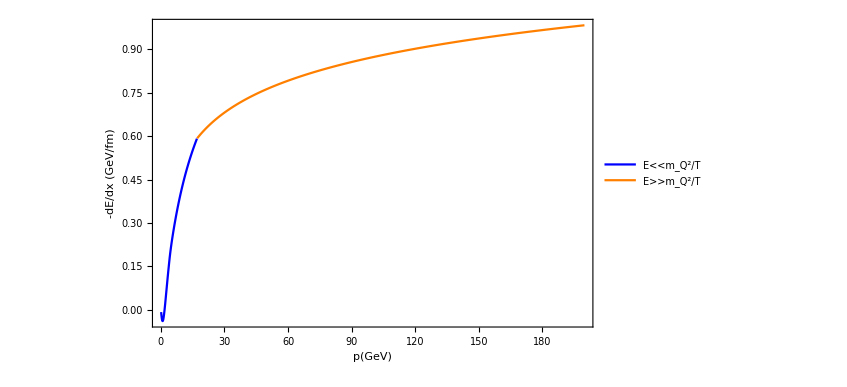

```mathematica
ListPlot[{lowPCharm,highPCharm},AxesLabel->{"p(GeV)", "-dE/dx (GeV/fm)"},PlotStyle->{Blue,Orange},PlotLegends->Placed[LineLegend[{Blue,Orange},{"E<<m_Q^2/T","E>>m_Q^2/T" },LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.15,0.85}],FrameLabel->{{"-dE/dx (GeV/fm)",""},{"p(GeV)","Elastic Energy Loss: Charm"}},Joined->True,Frame->True,Epilog->Inset[ListPlot[{lowPCharm,highPCharm},PlotRange->{{0,50},{-0.1,0.8}},Joined->True,PlotStyle->{Blue,Orange},Frame->True],{80,0.2},{0,0},{120,120}],PlotRange->All]
```

```mathematica
elasticCharm10=getElastic[10,5 fmToGev, 0.3,0.25, 2, 1.5][[3]]
```

Function[{eps$},Exp[-(-eps$+elasticCentre$41027)^2/(2 elasticWidth$41027^2)]/(√(2 π) elasticWidth$41027)]

```mathematica
{elasticCharm10Centre,elasticCharm10Width,elasticCharm10}=getElastic[10,5 fmToGev, 0.3,0.25, 2, 1.5]
```

{0.211794,0.0105897,Function[{eps$},Exp[-(-eps$+elasticCentre$41234)^2/(2 elasticWidth$41234^2)]/(√(2 π) elasticWidth$41234)]}

```mathematica
probabilityEpsilon = Table[{eps, elasticCharm10[eps]}, {eps, elasticCharm10Centre-10*elasticCharm10Width,elasticCharm10Centre+10*elasticCharm10Width,0.01*elasticCharm10Width}]
```

{{0.105897,7.26613×10^-21},{0.106003,8.02992×10^-21},{0.106109,8.8731×10^-21},{0.106214,9.80384×10^-21},{0.10632,1.08311×10^-20},{0.106426,1.19649×10^-20},{0.106532,1.32159×10^-20},{0.106638,1.45964×10^-20},{0.106744,1.61194×10^-20},{0.10685,1.77996×10^-20},{0.106956,1.96529×10^-20},{0.107062,2.1697×10^-20},{0.107168,2.39513×10^-20},{0.107273,2.64373×10^-20},{0.107379,2.91783×10^-20},{0.107485,3.22002×10^-20},{0.107591,3.55317×10^-20},{0.107697,3.92038×10^-20},{0.107803,4.32512×10^-20},{0.107909,4.77116×10^-20},{0.108015,5.26267×10^-20},{0.108121,5.80424×10^-20},{0.108226,6.4009×10^-20},{0.108332,7.05819×10^-20},{0.108438,7.7822×10^-20},{0.108544,8.57962×10^-20},{0.10865,9.45779×10^-20},{0.108756,1.04248×10^-19},{0.108862,1.14896×10^-19},{0.108968,1.26618×10^-19},{0.109074,1.39522×10^-19},{0.10918,1.53726×10^-19},{0.109285,1.6936×10^-19},{0.109391,1.86564×10^-19},{0.109497,2.05496×10^-19},{0.109603,2.26325×10^-19},{0.109709,2.49242×10^-19},{0.109815,2.74451×10^-19},{0.109921,3.0218×10^-19},{0.110027,3.32678×10^-19},{0.110133,3.66216×10^-19},{0.110239,4.03096×10^-19},{0.110344,4.43645×10^-19},{0.11045,4.88224×10^-19},{0.110556,5.37229×10^-19},{0.110662,5.91093×10^-19},{0.110768,6.50294×10^-19},{0.110874,7.15352×10^-19},{0.11098,7.86839×10^-19},{0.111086,8.65385×10^-19},{0.111192,9.51676×10^-19},{0.111297,1.04647×10^-18},{0.111403,1.15058×10^-18},{0.111509,1.26493×10^-18},{0.111615,1.39051×10^-18},{0.111721,1.5284×10^-18},{0.111827,1.67979×10^-18},{0.111933,1.846×10^-18},{0.112039,2.02844×10^-18},{0.112145,2.2287×10^-18},{0.112251,2.44848×10^-18},{0.112356,2.68967×10^-18},{0.112462,2.95432×10^-18},{0.112568,3.24469×10^-18},{0.112674,3.56324×10^-18},{0.11278,3.91267×10^-18},{0.112886,4.29593×10^-18},{0.112992,4.71627×10^-18},{0.113098,5.17722×10^-18},{0.113204,5.68266×10^-18},{0.11331,6.23681×10^-18},{0.113415,6.84432×10^-18},{0.113521,7.51025×10^-18},{0.113627,8.24015×10^-18},{0.113733,9.04009×10^-18},{0.113839,9.91669×10^-18},{0.113945,1.08772×10^-17},{0.114051,1.19296×10^-17},{0.114157,1.30824×10^-17},{0.114263,1.43453×10^-17},{0.114368,1.57284×10^-17},{0.114474,1.72432×10^-17},{0.11458,1.8902×10^-17},{0.114686,2.07183×10^-17},{0.114792,2.27069×10^-17},{0.114898,2.48838×10^-17},{0.115004,2.72668×10^-17},{0.11511,2.98749×10^-17},{0.115216,3.27292×10^-17},{0.115322,3.58527×10^-17},{0.115427,3.92703×10^-17},{0.115533,4.30094×10^-17},{0.115639,4.70998×10^-17},{0.115745,5.15741×10^-17},{0.115851,5.64677×10^-17},{0.115957,6.18195×10^-17},{0.116063,6.76718×10^-17},{0.116169,7.40706×10^-17},{0.116275,8.10664×10^-17},{0.116381,8.87141×10^-17},{0.116486,9.70735×10^-17},{0.116592,1.0621×10^-16},{0.116698,1.16195×10^-16},{0.116804,1.27106×10^-16},{0.11691,1.39027×10^-16},{0.117016,1.52051×10^-16},{0.117122,1.66279×10^-16},{0.117228,1.8182×10^-16},{0.117334,1.98794×10^-16},{0.117439,2.1733×10^-16},{0.117545,2.37572×10^-16},{0.117651,2.59672×10^-16},{0.117757,2.838×10^-16},{0.117863,3.10138×10^-16},{0.117969,3.38888×10^-16},{0.118075,3.70265×10^-16},{0.118181,4.04507×10^-16},{0.118287,4.41871×10^-16},{0.118393,4.82639×10^-16},{0.118498,5.27115×10^-16},{0.118604,5.75632×10^-16},{0.11871,6.28552×10^-16},{0.118816,6.86268×10^-16},{0.118922,7.4921×10^-16},{0.119028,8.17842×10^-16},{0.119134,8.92672×10^-16},{0.11924,9.74251×10^-16},{0.119346,1.06318×10^-15},{0.119452,1.16011×10^-15},{0.119557,1.26575×10^-15},{0.119663,1.38087×10^-15},{0.119769,1.50631×10^-15},{0.119875,1.64298×10^-15},{0.119981,1.79188×10^-15},{0.120087,1.95407×10^-15},{0.120193,2.13073×10^-15},{0.120299,2.32313×10^-15},{0.120405,2.53264×10^-15},{0.120511,2.76078×10^-15},{0.120616,3.00917×10^-15},{0.120722,3.27957×10^-15},{0.120828,3.57392×10^-15},{0.120934,3.8943×10^-15},{0.12104,4.24297×10^-15},{0.121146,4.6224×10^-15},{0.121252,5.03525×10^-15},{0.121358,5.48443×10^-15},{0.121464,5.97309×10^-15},{0.121569,6.50463×10^-15},{0.121675,7.08276×10^-15},{0.121781,7.71151×10^-15},{0.121887,8.39523×10^-15},{0.121993,9.13866×10^-15},{0.122099,9.94693×10^-15},{0.122205,1.08256×10^-14},{0.122311,1.17807×10^-14},{0.122417,1.28188×10^-14},{0.122523,1.3947×10^-14},{0.122628,1.51729×10^-14},{0.122734,1.6505×10^-14},{0.12284,1.79522×10^-14},{0.122946,1.95244×10^-14},{0.123052,2.12321×10^-14},{0.123158,2.30869×10^-14},{0.123264,2.51011×10^-14},{0.12337,2.72885×10^-14},{0.123476,2.96634×10^-14},{0.123582,3.22418×10^-14},{0.123687,3.50408×10^-14},{0.123793,3.8079×10^-14},{0.123899,4.13765×10^-14},{0.124005,4.49551×10^-14},{0.124111,4.88382×10^-14},{0.124217,5.30515×10^-14},{0.124323,5.76225×10^-14},{0.124429,6.25811×10^-14},{0.124535,6.79596×10^-14},{0.12464,7.3793×10^-14},{0.124746,8.0119×10^-14},{0.124852,8.69787×10^-14},{0.124958,9.44163×10^-14},{0.125064,1.0248×10^-13},{0.12517,1.1122×10^-13},{0.125276,1.20695×10^-13},{0.125382,1.30963×10^-13},{0.125488,1.4209×10^-13},{0.125594,1.54148×10^-13},{0.125699,1.67212×10^-13},{0.125805,1.81365×10^-13},{0.125911,1.96697×10^-13},{0.126017,2.13303×10^-13},{0.126123,2.31288×10^-13},{0.126229,2.50764×10^-13},{0.126335,2.71854×10^-13},{0.126441,2.94687×10^-13},{0.126547,3.19406×10^-13},{0.126653,3.46164×10^-13},{0.126758,3.75127×10^-13},{0.126864,4.06471×10^-13},{0.12697,4.40391×10^-13},{0.127076,4.77094×10^-13},{0.127182,5.16804×10^-13},{0.127288,5.59763×10^-13},{0.127394,6.06233×10^-13},{0.1275,6.56494×10^-13},{0.127606,7.10852×10^-13},{0.127711,7.69633×10^-13},{0.127817,8.33192×10^-13},{0.127923,9.01909×10^-13},{0.128029,9.76196×10^-13},{0.128135,1.0565×10^-12},{0.128241,1.14329×10^-12},{0.128347,1.23709×10^-12},{0.128453,1.33844×10^-12},{0.128559,1.44796×10^-12},{0.128665,1.56629×10^-12},{0.12877,1.69411×10^-12},{0.128876,1.83218×10^-12},{0.128982,1.98131×10^-12},{0.129088,2.14236×10^-12},{0.129194,2.31627×10^-12},{0.1293,2.50405×10^-12},{0.129406,2.70678×10^-12},{0.129512,2.92563×10^-12},{0.129618,3.16185×10^-12},{0.129724,3.41681×10^-12},{0.129829,3.69196×10^-12},{0.129935,3.98887×10^-12},{0.130041,4.30923×10^-12},{0.130147,4.65484×10^-12},{0.130253,5.02768×10^-12},{0.130359,5.42983×10^-12},{0.130465,5.86357×10^-12},{0.130571,6.33132×10^-12},{0.130677,6.8357×10^-12},{0.130782,7.37952×10^-12},{0.130888,7.96581×10^-12},{0.130994,8.59782×10^-12},{0.1311,9.27904×10^-12},{0.131206,1.00132×10^-11},{0.131312,1.08045×10^-11},{0.131418,1.1657×10^-11},{0.131524,1.25756×10^-11},{0.13163,1.35652×10^-11},{0.131736,1.46312×10^-11},{0.131841,1.57794×10^-11},{0.131947,1.70161×10^-11},{0.132053,1.83478×10^-11},{0.132159,1.97817×10^-11},{0.132265,2.13256×10^-11},{0.132371,2.29877×10^-11},{0.132477,2.47768×10^-11},{0.132583,2.67025×10^-11},{0.132689,2.8775×10^-11},{0.132795,3.10053×10^-11},{0.1329,3.34051×10^-11},{0.133006,3.5987×10^-11},{0.133112,3.87646×10^-11},{0.133218,4.17525×10^-11},{0.133324,4.49661×10^-11},{0.13343,4.84222×10^-11},{0.133536,5.21387×10^-11},{0.133642,5.61349×10^-11},{0.133748,6.04314×10^-11},{0.133853,6.50501×10^-11},{0.133959,7.00149×10^-11},{0.134065,7.53511×10^-11},{0.134171,8.10858×10^-11},{0.134277,8.72483×10^-11},{0.134383,9.38698×10^-11},{0.134489,1.00984×10^-10},{0.134595,1.08626×10^-10},{0.134701,1.16834×10^-10},{0.134807,1.25651×10^-10},{0.134912,1.35119×10^-10},{0.135018,1.45287×10^-10},{0.135124,1.56203×10^-10},{0.13523,1.67923×10^-10},{0.135336,1.80505×10^-10},{0.135442,1.9401×10^-10},{0.135548,2.08504×10^-10},{0.135654,2.24059×10^-10},{0.13576,2.4075×10^-10},{0.135866,2.58658×10^-10},{0.135971,2.77871×10^-10},{0.136077,2.98482×10^-10},{0.136183,3.20588×10^-10},{0.136289,3.44298×10^-10},{0.136395,3.69725×10^-10},{0.136501,3.96989×10^-10},{0.136607,4.26221×10^-10},{0.136713,4.5756×10^-10},{0.136819,4.91154×10^-10},{0.136925,5.27162×10^-10},{0.13703,5.65753×10^-10},{0.137136,6.07109×10^-10},{0.137242,6.51422×10^-10},{0.137348,6.989×10^-10},{0.137454,7.49764×10^-10},{0.13756,8.04249×10^-10},{0.137666,8.62606×10^-10},{0.137772,9.25106×10^-10},{0.137878,9.92035×10^-10},{0.137983,1.0637×10^-9},{0.138089,1.14043×10^-9},{0.138195,1.22257×10^-9},{0.138301,1.31049×10^-9},{0.138407,1.4046×10^-9},{0.138513,1.50532×10^-9},{0.138619,1.61309×10^-9},{0.138725,1.72841×10^-9},{0.138831,1.85179×10^-9},{0.138937,1.98378×10^-9},{0.139042,2.12496×10^-9},{0.139148,2.27596×10^-9},{0.139254,2.43745×10^-9},{0.13936,2.61014×10^-9},{0.139466,2.79478×10^-9},{0.139572,2.99218×10^-9},{0.139678,3.20321×10^-9},{0.139784,3.42878×10^-9},{0.13989,3.66986×10^-9},{0.139996,3.9275×10^-9},{0.140101,4.20281×10^-9},{0.140207,4.49697×10^-9},{0.140313,4.81123×10^-9},{0.140419,5.14694×10^-9},{0.140525,5.50553×10^-9},{0.140631,5.88851×10^-9},{0.140737,6.2975×10^-9},{0.140843,6.73423×10^-9},{0.140949,7.20052×10^-9},{0.141054,7.69833×10^-9},{0.14116,8.22973×10^-9},{0.141266,8.79693×10^-9},{0.141372,9.40229×10^-9},{0.141478,1.00483×10^-8},{0.141584,1.07376×10^-8},{0.14169,1.14731×10^-8},{0.141796,1.22577×10^-8},{0.141902,1.30946×10^-8},{0.142008,1.39873×10^-8},{0.142113,1.49394×10^-8},{0.142219,1.59547×10^-8},{0.142325,1.70373×10^-8},{0.142431,1.81915×10^-8},{0.142537,1.94219×10^-8},{0.142643,2.07335×10^-8},{0.142749,2.21315×10^-8},{0.142855,2.36214×10^-8},{0.142961,2.52091×10^-8},{0.143067,2.69007×10^-8},{0.143172,2.8703×10^-8},{0.143278,3.06231×10^-8},{0.143384,3.26682×10^-8},{0.14349,3.48465×10^-8},{0.143596,3.71663×10^-8},{0.143702,3.96366×10^-8},{0.143808,4.22668×10^-8},{0.143914,4.50671×10^-8},{0.14402,4.80481×10^-8},{0.144125,5.12212×10^-8},{0.144231,5.45983×10^-8},{0.144337,5.81923×10^-8},{0.144443,6.20167×10^-8},{0.144549,6.60857×10^-8},{0.144655,7.04148×10^-8},{0.144761,7.50199×10^-8},{0.144867,7.99182×10^-8},{0.144973,8.51278×10^-8},{0.145079,9.06679×10^-8},{0.145184,9.65589×10^-8},{0.14529,1.02822×10^-7},{0.145396,1.09481×10^-7},{0.145502,1.1656×10^-7},{0.145608,1.24083×10^-7},{0.145714,1.32079×10^-7},{0.14582,1.40577×10^-7},{0.145926,1.49606×10^-7},{0.146032,1.59199×10^-7},{0.146138,1.6939×10^-7},{0.146243,1.80215×10^-7},{0.146349,1.91714×10^-7},{0.146455,2.03925×10^-7},{0.146561,2.16893×10^-7},{0.146667,2.30662×10^-7},{0.146773,2.45281×10^-7},{0.146879,2.608×10^-7},{0.146985,2.77273×10^-7},{0.147091,2.94758×10^-7},{0.147196,3.13313×10^-7},{0.147302,3.33004×10^-7},{0.147408,3.53896×10^-7},{0.147514,3.76062×10^-7},{0.14762,3.99576×10^-7},{0.147726,4.24517×10^-7},{0.147832,4.50971×10^-7},{0.147938,4.79025×10^-7},{0.148044,5.08774×10^-7},{0.14815,5.40315×10^-7},{0.148255,5.73755×10^-7},{0.148361,6.09204×10^-7},{0.148467,6.46778×10^-7},{0.148573,6.86601×10^-7},{0.148679,7.28803×10^-7},{0.148785,7.73521×10^-7},{0.148891,8.20901×10^-7},{0.148997,8.71097×10^-7},{0.149103,9.24269×10^-7},{0.149209,9.80589×10^-7},{0.149314,1.04024×10^-6},{0.14942,1.1034×10^-6},{0.149526,1.17029×10^-6},{0.149632,1.2411×10^-6},{0.149738,1.31607×10^-6},{0.149844,1.39542×10^-6},{0.14995,1.47942×10^-6},{0.150056,1.56831×10^-6},{0.150162,1.66238×10^-6},{0.150267,1.76191×10^-6},{0.150373,1.86721×10^-6},{0.150479,1.97862×10^-6},{0.150585,2.09645×10^-6},{0.150691,2.22109×10^-6},{0.150797,2.3529×10^-6},{0.150903,2.49228×10^-6},{0.151009,2.63965×10^-6},{0.151115,2.79546×10^-6},{0.151221,2.96017×10^-6},{0.151326,3.13427×10^-6},{0.151432,3.31828×10^-6},{0.151538,3.51275×10^-6},{0.151644,3.71823×10^-6},{0.15175,3.93534×10^-6},{0.151856,4.16471×10^-6},{0.151962,4.40702×10^-6},{0.152068,4.66295×10^-6},{0.152174,4.93325×10^-6},{0.15228,5.2187×10^-6},{0.152385,5.52011×10^-6},{0.152491,5.83835×10^-6},{0.152597,6.17431×10^-6},{0.152703,6.52896×10^-6},{0.152809,6.90329×10^-6},{0.152915,7.29835×10^-6},{0.153021,7.71524×10^-6},{0.153127,8.15514×10^-6},{0.153233,8.61925×10^-6},{0.153338,9.10886×10^-6},{0.153444,9.62533×10^-6},{0.15355,0.0000101701},{0.153656,0.0000107445},{0.153762,0.0000113503},{0.153868,0.0000119891},{0.153974,0.0000126625},{0.15408,0.0000133725},{0.154186,0.0000141208},{0.154292,0.0000149095},{0.154397,0.0000157407},{0.154503,0.0000166165},{0.154609,0.0000175394},{0.154715,0.0000185116},{0.154821,0.0000195358},{0.154927,0.0000206146},{0.155033,0.0000217507},{0.155139,0.0000229472},{0.155245,0.0000242071},{0.155351,0.0000255337},{0.155456,0.0000269302},{0.155562,0.0000284002},{0.155668,0.0000299476},{0.155774,0.000031576},{0.15588,0.0000332897},{0.155986,0.0000350929},{0.156092,0.00003699},{0.156198,0.0000389858},{0.156304,0.0000410852},{0.15641,0.0000432933},{0.156515,0.0000456155},{0.156621,0.0000480575},{0.156727,0.0000506251},{0.156833,0.0000533246},{0.156939,0.0000561624},{0.157045,0.0000591453},{0.157151,0.0000622805},{0.157257,0.0000655752},{0.157363,0.0000690374},{0.157468,0.000072675},{0.157574,0.0000764967},{0.15768,0.0000805113},{0.157786,0.0000847281},{0.157892,0.0000891569},{0.157998,0.0000938078},{0.158104,0.0000986914},{0.15821,0.000103819},{0.158316,0.000109202},{0.158422,0.000114852},{0.158527,0.000120783},{0.158633,0.000127008},{0.158739,0.00013354},{0.158845,0.000140393},{0.158951,0.000147584},{0.159057,0.000155128},{0.159163,0.00016304},{0.159269,0.00017134},{0.159375,0.000180043},{0.159481,0.00018917},{0.159586,0.00019874},{0.159692,0.000208773},{0.159798,0.000219291},{0.159904,0.000230315},{0.16001,0.000241869},{0.160116,0.000253978},{0.160222,0.000266666},{0.160328,0.00027996},{0.160434,0.000293888},{0.160539,0.000308477},{0.160645,0.000323758},{0.160751,0.000339763},{0.160857,0.000356523},{0.160963,0.000374072},{0.161069,0.000392446},{0.161175,0.000411681},{0.161281,0.000431815},{0.161387,0.000452889},{0.161493,0.000474944},{0.161598,0.000498024},{0.161704,0.000522172},{0.16181,0.000547437},{0.161916,0.000573867},{0.162022,0.000601513},{0.162128,0.000630427},{0.162234,0.000660666},{0.16234,0.000692285},{0.162446,0.000725345},{0.162552,0.000759908},{0.162657,0.000796039},{0.162763,0.000833804},{0.162869,0.000873273},{0.162975,0.000914519},{0.163081,0.000957617},{0.163187,0.00100265},{0.163293,0.00104969},{0.163399,0.00109883},{0.163505,0.00115015},{0.16361,0.00120375},{0.163716,0.00125972},{0.163822,0.00131817},{0.163928,0.00137918},{0.164034,0.00144288},{0.16414,0.00150937},{0.164246,0.00157876},{0.164352,0.00165118},{0.164458,0.00172675},{0.164564,0.0018056},{0.164669,0.00188786},{0.164775,0.00197367},{0.164881,0.00206317},{0.164987,0.00215651},{0.165093,0.00225386},{0.165199,0.00235536},{0.165305,0.00246118},{0.165411,0.00257151},{0.165517,0.00268651},{0.165623,0.00280637},{0.165728,0.00293129},{0.165834,0.00306146},{0.16594,0.00319709},{0.166046,0.0033384},{0.166152,0.00348561},{0.166258,0.00363894},{0.166364,0.00379864},{0.16647,0.00396495},{0.166576,0.00413812},{0.166681,0.00431843},{0.166787,0.00450615},{0.166893,0.00470155},{0.166999,0.00490494},{0.167105,0.00511661},{0.167211,0.00533689},{0.167317,0.00556609},{0.167423,0.00580455},{0.167529,0.00605263},{0.167635,0.00631067},{0.16774,0.00657906},{0.167846,0.00685818},{0.167952,0.00714843},{0.168058,0.00745021},{0.168164,0.00776396},{0.16827,0.00809011},{0.168376,0.00842912},{0.168482,0.00878146},{0.168588,0.00914761},{0.168694,0.00952807},{0.168799,0.00992337},{0.168905,0.010334},{0.169011,0.0107606},{0.169117,0.0112037},{0.169223,0.0116638},{0.169329,0.0121417},{0.169435,0.0126378},{0.169541,0.0131529},{0.169647,0.0136876},{0.169752,0.0142427},{0.169858,0.0148187},{0.169964,0.0154166},{0.17007,0.0160369},{0.170176,0.0166805},{0.170282,0.0173483},{0.170388,0.0180409},{0.170494,0.0187594},{0.1706,0.0195044},{0.170706,0.0202771},{0.170811,0.0210783},{0.170917,0.0219089},{0.171023,0.02277},{0.171129,0.0236625},{0.171235,0.0245876},{0.171341,0.0255463},{0.171447,0.0265397},{0.171553,0.027569},{0.171659,0.0286354},{0.171765,0.02974},{0.17187,0.0308841},{0.171976,0.0320691},{0.172082,0.0332962},{0.172188,0.0345668},{0.172294,0.0358822},{0.1724,0.0372441},{0.172506,0.0386537},{0.172612,0.0401127},{0.172718,0.0416226},{0.172824,0.043185},{0.172929,0.0448015},{0.173035,0.046474},{0.173141,0.048204},{0.173247,0.0499935},{0.173353,0.0518442},{0.173459,0.053758},{0.173565,0.0557369},{0.173671,0.0577829},{0.173777,0.059898},{0.173882,0.0620843},{0.173988,0.0643439},{0.174094,0.0666792},{0.1742,0.0690922},{0.174306,0.0715855},{0.174412,0.0741613},{0.174518,0.0768221},{0.174624,0.0795704},{0.17473,0.0824088},{0.174836,0.0853399},{0.174941,0.0883665},{0.175047,0.0914912},{0.175153,0.0947169},{0.175259,0.0980466},{0.175365,0.101483},{0.175471,0.10503},{0.175577,0.108689},{0.175683,0.112465},{0.175789,0.11636},{0.175895,0.120379},{0.176,0.124523},{0.176106,0.128798},{0.176212,0.133205},{0.176318,0.13775},{0.176424,0.142436},{0.17653,0.147266},{0.176636,0.152245},{0.176742,0.157377},{0.176848,0.162665},{0.176953,0.168114},{0.177059,0.173728},{0.177165,0.179512},{0.177271,0.18547},{0.177377,0.191606},{0.177483,0.197926},{0.177589,0.204433},{0.177695,0.211134},{0.177801,0.218032},{0.177907,0.225133},{0.178012,0.232442},{0.178118,0.239965},{0.178224,0.247706},{0.17833,0.255671},{0.178436,0.263866},{0.178542,0.272297},{0.178648,0.280968},{0.178754,0.289887},{0.17886,0.299059},{0.178966,0.308491},{0.179071,0.318188},{0.179177,0.328157},{0.179283,0.338405},{0.179389,0.348937},{0.179495,0.359762},{0.179601,0.370885},{0.179707,0.382314},{0.179813,0.394056},{0.179919,0.406118},{0.180024,0.418507},{0.18013,0.43123},{0.180236,0.444297},{0.180342,0.457713},{0.180448,0.471487},{0.180554,0.485628},{0.18066,0.500142},{0.180766,0.515039},{0.180872,0.530326},{0.180978,0.546013},{0.181083,0.562107},{0.181189,0.578618},{0.181295,0.595554},{0.181401,0.612925},{0.181507,0.630739},{0.181613,0.649006},{0.181719,0.667736},{0.181825,0.686937},{0.181931,0.70662},{0.182037,0.726794},{0.182142,0.747469},{0.182248,0.768655},{0.182354,0.790363},{0.18246,0.812603},{0.182566,0.835385},{0.182672,0.85872},{0.182778,0.882618},{0.182884,0.907091},{0.18299,0.932149},{0.183095,0.957803},{0.183201,0.984066},{0.183307,1.01095},{0.183413,1.03846},{0.183519,1.06661},{0.183625,1.09542},{0.183731,1.12489},{0.183837,1.15504},{0.183943,1.18588},{0.184049,1.21742},{0.184154,1.24968},{0.18426,1.28266},{0.184366,1.31638},{0.184472,1.35085},{0.184578,1.38609},{0.184684,1.4221},{0.18479,1.45891},{0.184896,1.49651},{0.185002,1.53493},{0.185108,1.57418},{0.185213,1.61428},{0.185319,1.65523},{0.185425,1.69704},{0.185531,1.73974},{0.185637,1.78334},{0.185743,1.82784},{0.185849,1.87327},{0.185955,1.91964},{0.186061,1.96696},{0.186166,2.01524},{0.186272,2.0645},{0.186378,2.11475},{0.186484,2.16601},{0.18659,2.21829},{0.186696,2.27161},{0.186802,2.32597},{0.186908,2.3814},{0.187014,2.4379},{0.18712,2.4955},{0.187225,2.5542},{0.187331,2.61401},{0.187437,2.67497},{0.187543,2.73707},{0.187649,2.80033},{0.187755,2.86477},{0.187861,2.9304},{0.187967,2.99723},{0.188073,3.06527},{0.188179,3.13456},{0.188284,3.20508},{0.18839,3.27687},{0.188496,3.34992},{0.188602,3.42427},{0.188708,3.49991},{0.188814,3.57687},{0.18892,3.65515},{0.189026,3.73477},{0.189132,3.81575},{0.189237,3.89809},{0.189343,3.98181},{0.189449,4.06693},{0.189555,4.15344},{0.189661,4.24137},{0.189767,4.33073},{0.189873,4.42154},{0.189979,4.51379},{0.190085,4.60751},{0.190191,4.7027},{0.190296,4.79938},{0.190402,4.89756},{0.190508,4.99725},{0.190614,5.09845},{0.19072,5.20119},{0.190826,5.30546},{0.190932,5.41129},{0.191038,5.51867},{0.191144,5.62762},{0.19125,5.73815},{0.191355,5.85027},{0.191461,5.96398},{0.191567,6.07929},{0.191673,6.19621},{0.191779,6.31474},{0.191885,6.43491},{0.191991,6.5567},{0.192097,6.68013},{0.192203,6.8052},{0.192309,6.93192},{0.192414,7.0603},{0.19252,7.19033},{0.192626,7.32203},{0.192732,7.45539},{0.192838,7.59042},{0.192944,7.72713},{0.19305,7.86551},{0.193156,8.00557},{0.193262,8.14731},{0.193367,8.29072},{0.193473,8.43582},{0.193579,8.5826},{0.193685,8.73106},{0.193791,8.88121},{0.193897,9.03302},{0.194003,9.18652},{0.194109,9.34169},{0.194215,9.49853},{0.194321,9.65704},{0.194426,9.81721},{0.194532,9.97904},{0.194638,10.1425},{0.194744,10.3077},{0.19485,10.4744},{0.194956,10.6428},{0.195062,10.8129},{0.195168,10.9845},{0.195274,11.1578},{0.19538,11.3326},{0.195485,11.5091},{0.195591,11.6871},{0.195697,11.8667},{0.195803,12.0479},{0.195909,12.2306},{0.196015,12.4148},{0.196121,12.6005},{0.196227,12.7877},{0.196333,12.9765},{0.196438,13.1667},{0.196544,13.3583},{0.19665,13.5514},{0.196756,13.7459},{0.196862,13.9417},{0.196968,14.139},{0.197074,14.3376},{0.19718,14.5376},{0.197286,14.7389},{0.197392,14.9414},{0.197497,15.1453},{0.197603,15.3503},{0.197709,15.5566},{0.197815,15.7641},{0.197921,15.9728},{0.198027,16.1826},{0.198133,16.3935},{0.198239,16.6056},{0.198345,16.8186},{0.198451,17.0327},{0.198556,17.2478},{0.198662,17.4639},{0.198768,17.6809},{0.198874,17.8989},{0.19898,18.1177},{0.199086,18.3373},{0.199192,18.5577},{0.199298,18.779},{0.199404,19.0009},{0.199509,19.2236},{0.199615,19.4469},{0.199721,19.6708},{0.199827,19.8954},{0.199933,20.1205},{0.200039,20.3461},{0.200145,20.5721},{0.200251,20.7986},{0.200357,21.0255},{0.200463,21.2528},{0.200568,21.4803},{0.200674,21.7081},{0.20078,21.9362},{0.200886,22.1644},{0.200992,22.3928},{0.201098,22.6212},{0.201204,22.8497},{0.20131,23.0782},{0.201416,23.3066},{0.201522,23.535},{0.201627,23.7632},{0.201733,23.9912},{0.201839,24.219},{0.201945,24.4465},{0.202051,24.6737},{0.202157,24.9005},{0.202263,25.1269},{0.202369,25.3528},{0.202475,25.5781},{0.20258,25.8029},{0.202686,26.0271},{0.202792,26.2506},{0.202898,26.4733},{0.203004,26.6953},{0.20311,26.9164},{0.203216,27.1367},{0.203322,27.356},{0.203428,27.5744},{0.203534,27.7917},{0.203639,28.0079},{0.203745,28.223},{0.203851,28.4369},{0.203957,28.6495},{0.204063,28.8609},{0.204169,29.0709},{0.204275,29.2795},{0.204381,29.4866},{0.204487,29.6923},{0.204593,29.8964},{0.204698,30.0989},{0.204804,30.2997},{0.20491,30.4988},{0.205016,30.6962},{0.205122,30.8917},{0.205228,31.0854},{0.205334,31.2771},{0.20544,31.4669},{0.205546,31.6547},{0.205651,31.8404},{0.205757,32.0241},{0.205863,32.2055},{0.205969,32.3847},{0.206075,32.5617},{0.206181,32.7364},{0.206287,32.9087},{0.206393,33.0786},{0.206499,33.2461},{0.206605,33.4111},{0.20671,33.5735},{0.206816,33.7334},{0.206922,33.8906},{0.207028,34.0451},{0.207134,34.197},{0.20724,34.3461},{0.207346,34.4923},{0.207452,34.6358},{0.207558,34.7763},{0.207664,34.914},{0.207769,35.0487},{0.207875,35.1803},{0.207981,35.309},{0.208087,35.4345},{0.208193,35.557},{0.208299,35.6763},{0.208405,35.7925},{0.208511,35.9054},{0.208617,36.0151},{0.208722,36.1215},{0.208828,36.2246},{0.208934,36.3243},{0.20904,36.4207},{0.209146,36.5137},{0.209252,36.6033},{0.209358,36.6894},{0.209464,36.772},{0.20957,36.8512},{0.209676,36.9268},{0.209781,36.9989},{0.209887,37.0674},{0.209993,37.1323},{0.210099,37.1936},{0.210205,37.2513},{0.210311,37.3054},{0.210417,37.3558},{0.210523,37.4025},{0.210629,37.4455},{0.210735,37.4849},{0.21084,37.5205},{0.210946,37.5524},{0.211052,37.5806},{0.211158,37.605},{0.211264,37.6257},{0.21137,37.6426},{0.211476,37.6558},{0.211582,37.6652},{0.211688,37.6709},{0.211794,37.6728},{0.211899,37.6709},{0.212005,37.6652},{0.212111,37.6558},{0.212217,37.6426},{0.212323,37.6257},{0.212429,37.605},{0.212535,37.5806},{0.212641,37.5524},{0.212747,37.5205},{0.212852,37.4849},{0.212958,37.4455},{0.213064,37.4025},{0.21317,37.3558},{0.213276,37.3054},{0.213382,37.2513},{0.213488,37.1936},{0.213594,37.1323},{0.2137,37.0674},{0.213806,36.9989},{0.213911,36.9268},{0.214017,36.8512},{0.214123,36.772},{0.214229,36.6894},{0.214335,36.6033},{0.214441,36.5137},{0.214547,36.4207},{0.214653,36.3243},{0.214759,36.2246},{0.214865,36.1215},{0.21497,36.0151},{0.215076,35.9054},{0.215182,35.7925},{0.215288,35.6763},{0.215394,35.557},{0.2155,35.4345},{0.215606,35.309},{0.215712,35.1803},{0.215818,35.0487},{0.215923,34.914},{0.216029,34.7763},{0.216135,34.6358},{0.216241,34.4923},{0.216347,34.3461},{0.216453,34.197},{0.216559,34.0451},{0.216665,33.8906},{0.216771,33.7334},{0.216877,33.5735},{0.216982,33.4111},{0.217088,33.2461},{0.217194,33.0786},{0.2173,32.9087},{0.217406,32.7364},{0.217512,32.5617},{0.217618,32.3847},{0.217724,32.2055},{0.21783,32.0241},{0.217936,31.8404},{0.218041,31.6547},{0.218147,31.4669},{0.218253,31.2771},{0.218359,31.0854},{0.218465,30.8917},{0.218571,30.6962},{0.218677,30.4988},{0.218783,30.2997},{0.218889,30.0989},{0.218994,29.8964},{0.2191,29.6923},{0.219206,29.4866},{0.219312,29.2795},{0.219418,29.0709},{0.219524,28.8609},{0.21963,28.6495},{0.219736,28.4369},{0.219842,28.223},{0.219948,28.0079},{0.220053,27.7917},{0.220159,27.5744},{0.220265,27.356},{0.220371,27.1367},{0.220477,26.9164},{0.220583,26.6953},{0.220689,26.4733},{0.220795,26.2506},{0.220901,26.0271},{0.221007,25.8029},{0.221112,25.5781},{0.221218,25.3528},{0.221324,25.1269},{0.22143,24.9005},{0.221536,24.6737},{0.221642,24.4465},{0.221748,24.219},{0.221854,23.9912},{0.22196,23.7632},{0.222065,23.535},{0.222171,23.3066},{0.222277,23.0782},{0.222383,22.8497},{0.222489,22.6212},{0.222595,22.3928},{0.222701,22.1644},{0.222807,21.9362},{0.222913,21.7081},{0.223019,21.4803},{0.223124,21.2528},{0.22323,21.0255},{0.223336,20.7986},{0.223442,20.5721},{0.223548,20.3461},{0.223654,20.1205},{0.22376,19.8954},{0.223866,19.6708},{0.223972,19.4469},{0.224078,19.2236},{0.224183,19.0009},{0.224289,18.779},{0.224395,18.5577},{0.224501,18.3373},{0.224607,18.1177},{0.224713,17.8989},{0.224819,17.6809},{0.224925,17.4639},{0.225031,17.2478},{0.225136,17.0327},{0.225242,16.8186},{0.225348,16.6056},{0.225454,16.3935},{0.22556,16.1826},{0.225666,15.9728},{0.225772,15.7641},{0.225878,15.5566},{0.225984,15.3503},{0.22609,15.1453},{0.226195,14.9414},{0.226301,14.7389},{0.226407,14.5376},{0.226513,14.3376},{0.226619,14.139},{0.226725,13.9417},{0.226831,13.7459},{0.226937,13.5514},{0.227043,13.3583},{0.227149,13.1667},{0.227254,12.9765},{0.22736,12.7877},{0.227466,12.6005},{0.227572,12.4148},{0.227678,12.2306},{0.227784,12.0479},{0.22789,11.8667},{0.227996,11.6871},{0.228102,11.5091},{0.228208,11.3326},{0.228313,11.1578},{0.228419,10.9845},{0.228525,10.8129},{0.228631,10.6428},{0.228737,10.4744},{0.228843,10.3077},{0.228949,10.1425},{0.229055,9.97904},{0.229161,9.81721},{0.229266,9.65704},{0.229372,9.49853},{0.229478,9.34169},{0.229584,9.18652},{0.22969,9.03302},{0.229796,8.88121},{0.229902,8.73106},{0.230008,8.5826},{0.230114,8.43582},{0.23022,8.29072},{0.230325,8.14731},{0.230431,8.00557},{0.230537,7.86551},{0.230643,7.72713},{0.230749,7.59042},{0.230855,7.45539},{0.230961,7.32203},{0.231067,7.19033},{0.231173,7.0603},{0.231279,6.93192},{0.231384,6.8052},{0.23149,6.68013},{0.231596,6.5567},{0.231702,6.43491},{0.231808,6.31474},{0.231914,6.19621},{0.23202,6.07929},{0.232126,5.96398},{0.232232,5.85027},{0.232337,5.73815},{0.232443,5.62762},{0.232549,5.51867},{0.232655,5.41129},{0.232761,5.30546},{0.232867,5.20119},{0.232973,5.09845},{0.233079,4.99725},{0.233185,4.89756},{0.233291,4.79938},{0.233396,4.7027},{0.233502,4.60751},{0.233608,4.51379},{0.233714,4.42154},{0.23382,4.33073},{0.233926,4.24137},{0.234032,4.15344},{0.234138,4.06693},{0.234244,3.98181},{0.23435,3.89809},{0.234455,3.81575},{0.234561,3.73477},{0.234667,3.65515},{0.234773,3.57687},{0.234879,3.49991},{0.234985,3.42427},{0.235091,3.34992},{0.235197,3.27687},{0.235303,3.20508},{0.235408,3.13456},{0.235514,3.06527},{0.23562,2.99723},{0.235726,2.9304},{0.235832,2.86477},{0.235938,2.80033},{0.236044,2.73707},{0.23615,2.67497},{0.236256,2.61401},{0.236362,2.5542},{0.236467,2.4955},{0.236573,2.4379},{0.236679,2.3814},{0.236785,2.32597},{0.236891,2.27161},{0.236997,2.21829},{0.237103,2.16601},{0.237209,2.11475},{0.237315,2.0645},{0.237421,2.01524},{0.237526,1.96696},{0.237632,1.91964},{0.237738,1.87327},{0.237844,1.82784},{0.23795,1.78334},{0.238056,1.73974},{0.238162,1.69704},{0.238268,1.65523},{0.238374,1.61428},{0.238479,1.57418},{0.238585,1.53493},{0.238691,1.49651},{0.238797,1.45891},{0.238903,1.4221},{0.239009,1.38609},{0.239115,1.35085},{0.239221,1.31638},{0.239327,1.28266},{0.239433,1.24968},{0.239538,1.21742},{0.239644,1.18588},{0.23975,1.15504},{0.239856,1.12489},{0.239962,1.09542},{0.240068,1.06661},{0.240174,1.03846},{0.24028,1.01095},{0.240386,0.984066},{0.240492,0.957803},{0.240597,0.932149},{0.240703,0.907091},{0.240809,0.882618},{0.240915,0.85872},{0.241021,0.835385},{0.241127,0.812603},{0.241233,0.790363},{0.241339,0.768655},{0.241445,0.747469},{0.24155,0.726794},{0.241656,0.70662},{0.241762,0.686937},{0.241868,0.667736},{0.241974,0.649006},{0.24208,0.630739},{0.242186,0.612925},{0.242292,0.595554},{0.242398,0.578618},{0.242504,0.562107},{0.242609,0.546013},{0.242715,0.530326},{0.242821,0.515039},{0.242927,0.500142},{0.243033,0.485628},{0.243139,0.471487},{0.243245,0.457713},{0.243351,0.444297},{0.243457,0.43123},{0.243563,0.418507},{0.243668,0.406118},{0.243774,0.394056},{0.24388,0.382314},{0.243986,0.370885},{0.244092,0.359762},{0.244198,0.348937},{0.244304,0.338405},{0.24441,0.328157},{0.244516,0.318188},{0.244621,0.308491},{0.244727,0.299059},{0.244833,0.289887},{0.244939,0.280968},{0.245045,0.272297},{0.245151,0.263866},{0.245257,0.255671},{0.245363,0.247706},{0.245469,0.239965},{0.245575,0.232442},{0.24568,0.225133},{0.245786,0.218032},{0.245892,0.211134},{0.245998,0.204433},{0.246104,0.197926},{0.24621,0.191606},{0.246316,0.18547},{0.246422,0.179512},{0.246528,0.173728},{0.246634,0.168114},{0.246739,0.162665},{0.246845,0.157377},{0.246951,0.152245},{0.247057,0.147266},{0.247163,0.142436},{0.247269,0.13775},{0.247375,0.133205},{0.247481,0.128798},{0.247587,0.124523},{0.247693,0.120379},{0.247798,0.11636},{0.247904,0.112465},{0.24801,0.108689},{0.248116,0.10503},{0.248222,0.101483},{0.248328,0.0980466},{0.248434,0.0947169},{0.24854,0.0914912},{0.248646,0.0883665},{0.248751,0.0853399},{0.248857,0.0824088},{0.248963,0.0795704},{0.249069,0.0768221},{0.249175,0.0741613},{0.249281,0.0715855},{0.249387,0.0690922},{0.249493,0.0666792},{0.249599,0.0643439},{0.249705,0.0620843},{0.24981,0.059898},{0.249916,0.0577829},{0.250022,0.0557369},{0.250128,0.053758},{0.250234,0.0518442},{0.25034,0.0499935},{0.250446,0.048204},{0.250552,0.046474},{0.250658,0.0448015},{0.250764,0.043185},{0.250869,0.0416226},{0.250975,0.0401127},{0.251081,0.0386537},{0.251187,0.0372441},{0.251293,0.0358822},{0.251399,0.0345668},{0.251505,0.0332962},{0.251611,0.0320691},{0.251717,0.0308841},{0.251822,0.02974},{0.251928,0.0286354},{0.252034,0.027569},{0.25214,0.0265397},{0.252246,0.0255463},{0.252352,0.0245876},{0.252458,0.0236625},{0.252564,0.02277},{0.25267,0.0219089},{0.252776,0.0210783},{0.252881,0.0202771},{0.252987,0.0195044},{0.253093,0.0187594},{0.253199,0.0180409},{0.253305,0.0173483},{0.253411,0.0166805},{0.253517,0.0160369},{0.253623,0.0154166},{0.253729,0.0148187},{0.253835,0.0142427},{0.25394,0.0136876},{0.254046,0.0131529},{0.254152,0.0126378},{0.254258,0.0121417},{0.254364,0.0116638},{0.25447,0.0112037},{0.254576,0.0107606},{0.254682,0.010334},{0.254788,0.00992337},{0.254893,0.00952807},{0.254999,0.00914761},{0.255105,0.00878146},{0.255211,0.00842912},{0.255317,0.00809011},{0.255423,0.00776396},{0.255529,0.00745021},{0.255635,0.00714843},{0.255741,0.00685818},{0.255847,0.00657906},{0.255952,0.00631067},{0.256058,0.00605263},{0.256164,0.00580455},{0.25627,0.00556609},{0.256376,0.00533689},{0.256482,0.00511661},{0.256588,0.00490494},{0.256694,0.00470155},{0.2568,0.00450615},{0.256906,0.00431843},{0.257011,0.00413812},{0.257117,0.00396495},{0.257223,0.00379864},{0.257329,0.00363894},{0.257435,0.00348561},{0.257541,0.0033384},{0.257647,0.00319709},{0.257753,0.00306146},{0.257859,0.00293129},{0.257964,0.00280637},{0.25807,0.00268651},{0.258176,0.00257151},{0.258282,0.00246118},{0.258388,0.00235536},{0.258494,0.00225386},{0.2586,0.00215651},{0.258706,0.00206317},{0.258812,0.00197367},{0.258918,0.00188786},{0.259023,0.0018056},{0.259129,0.00172675},{0.259235,0.00165118},{0.259341,0.00157876},{0.259447,0.00150937},{0.259553,0.00144288},{0.259659,0.00137918},{0.259765,0.00131817},{0.259871,0.00125972},{0.259977,0.00120375},{0.260082,0.00115015},{0.260188,0.00109883},{0.260294,0.00104969},{0.2604,0.00100265},{0.260506,0.000957617},{0.260612,0.000914519},{0.260718,0.000873273},{0.260824,0.000833804},{0.26093,0.000796039},{0.261035,0.000759908},{0.261141,0.000725345},{0.261247,0.000692285},{0.261353,0.000660666},{0.261459,0.000630427},{0.261565,0.000601513},{0.261671,0.000573867},{0.261777,0.000547437},{0.261883,0.000522172},{0.261989,0.000498024},{0.262094,0.000474944},{0.2622,0.000452889},{0.262306,0.000431815},{0.262412,0.000411681},{0.262518,0.000392446},{0.262624,0.000374072},{0.26273,0.000356523},{0.262836,0.000339763},{0.262942,0.000323758},{0.263048,0.000308477},{0.263153,0.000293888},{0.263259,0.00027996},{0.263365,0.000266666},{0.263471,0.000253978},{0.263577,0.000241869},{0.263683,0.000230315},{0.263789,0.000219291},{0.263895,0.000208773},{0.264001,0.00019874},{0.264107,0.00018917},{0.264212,0.000180043},{0.264318,0.00017134},{0.264424,0.00016304},{0.26453,0.000155128},{0.264636,0.000147584},{0.264742,0.000140393},{0.264848,0.00013354},{0.264954,0.000127008},{0.26506,0.000120783},{0.265165,0.000114852},{0.265271,0.000109202},{0.265377,0.000103819},{0.265483,0.0000986914},{0.265589,0.0000938078},{0.265695,0.0000891569},{0.265801,0.0000847281},{0.265907,0.0000805113},{0.266013,0.0000764967},{0.266119,0.000072675},{0.266224,0.0000690374},{0.26633,0.0000655752},{0.266436,0.0000622805},{0.266542,0.0000591453},{0.266648,0.0000561624},{0.266754,0.0000533246},{0.26686,0.0000506251},{0.266966,0.0000480575},{0.267072,0.0000456155},{0.267178,0.0000432933},{0.267283,0.0000410852},{0.267389,0.0000389858},{0.267495,0.00003699},{0.267601,0.0000350929},{0.267707,0.0000332897},{0.267813,0.000031576},{0.267919,0.0000299476},{0.268025,0.0000284002},{0.268131,0.0000269302},{0.268236,0.0000255337},{0.268342,0.0000242071},{0.268448,0.0000229472},{0.268554,0.0000217507},{0.26866,0.0000206146},{0.268766,0.0000195358},{0.268872,0.0000185116},{0.268978,0.0000175394},{0.269084,0.0000166165},{0.26919,0.0000157407},{0.269295,0.0000149095},{0.269401,0.0000141208},{0.269507,0.0000133725},{0.269613,0.0000126625},{0.269719,0.0000119891},{0.269825,0.0000113503},{0.269931,0.0000107445},{0.270037,0.0000101701},{0.270143,9.62533×10^-6},{0.270249,9.10886×10^-6},{0.270354,8.61925×10^-6},{0.27046,8.15514×10^-6},{0.270566,7.71524×10^-6},{0.270672,7.29835×10^-6},{0.270778,6.90329×10^-6},{0.270884,6.52896×10^-6},{0.27099,6.17431×10^-6},{0.271096,5.83835×10^-6},{0.271202,5.52011×10^-6},{0.271307,5.2187×10^-6},{0.271413,4.93325×10^-6},{0.271519,4.66295×10^-6},{0.271625,4.40702×10^-6},{0.271731,4.16471×10^-6},{0.271837,3.93534×10^-6},{0.271943,3.71823×10^-6},{0.272049,3.51275×10^-6},{0.272155,3.31828×10^-6},{0.272261,3.13427×10^-6},{0.272366,2.96017×10^-6},{0.272472,2.79546×10^-6},{0.272578,2.63965×10^-6},{0.272684,2.49228×10^-6},{0.27279,2.3529×10^-6},{0.272896,2.22109×10^-6},{0.273002,2.09645×10^-6},{0.273108,1.97862×10^-6},{0.273214,1.86721×10^-6},{0.27332,1.76191×10^-6},{0.273425,1.66238×10^-6},{0.273531,1.56831×10^-6},{0.273637,1.47942×10^-6},{0.273743,1.39542×10^-6},{0.273849,1.31607×10^-6},{0.273955,1.2411×10^-6},{0.274061,1.17029×10^-6},{0.274167,1.1034×10^-6},{0.274273,1.04024×10^-6},{0.274378,9.80589×10^-7},{0.274484,9.24269×10^-7},{0.27459,8.71097×10^-7},{0.274696,8.20901×10^-7},{0.274802,7.73521×10^-7},{0.274908,7.28803×10^-7},{0.275014,6.86601×10^-7},{0.27512,6.46778×10^-7},{0.275226,6.09204×10^-7},{0.275332,5.73755×10^-7},{0.275437,5.40315×10^-7},{0.275543,5.08774×10^-7},{0.275649,4.79025×10^-7},{0.275755,4.50971×10^-7},{0.275861,4.24517×10^-7},{0.275967,3.99576×10^-7},{0.276073,3.76062×10^-7},{0.276179,3.53896×10^-7},{0.276285,3.33004×10^-7},{0.276391,3.13313×10^-7},{0.276496,2.94758×10^-7},{0.276602,2.77273×10^-7},{0.276708,2.608×10^-7},{0.276814,2.45281×10^-7},{0.27692,2.30662×10^-7},{0.277026,2.16893×10^-7},{0.277132,2.03925×10^-7},{0.277238,1.91714×10^-7},{0.277344,1.80215×10^-7},{0.277449,1.6939×10^-7},{0.277555,1.59199×10^-7},{0.277661,1.49606×10^-7},{0.277767,1.40577×10^-7},{0.277873,1.32079×10^-7},{0.277979,1.24083×10^-7},{0.278085,1.1656×10^-7},{0.278191,1.09481×10^-7},{0.278297,1.02822×10^-7},{0.278403,9.65589×10^-8},{0.278508,9.06679×10^-8},{0.278614,8.51278×10^-8},{0.27872,7.99182×10^-8},{0.278826,7.50199×10^-8},{0.278932,7.04148×10^-8},{0.279038,6.60857×10^-8},{0.279144,6.20167×10^-8},{0.27925,5.81923×10^-8},{0.279356,5.45983×10^-8},{0.279462,5.12212×10^-8},{0.279567,4.80481×10^-8},{0.279673,4.50671×10^-8},{0.279779,4.22668×10^-8},{0.279885,3.96366×10^-8},{0.279991,3.71663×10^-8},{0.280097,3.48465×10^-8},{0.280203,3.26682×10^-8},{0.280309,3.06231×10^-8},{0.280415,2.8703×10^-8},{0.28052,2.69007×10^-8},{0.280626,2.52091×10^-8},{0.280732,2.36214×10^-8},{0.280838,2.21315×10^-8},{0.280944,2.07335×10^-8},{0.28105,1.94219×10^-8},{0.281156,1.81915×10^-8},{0.281262,1.70373×10^-8},{0.281368,1.59547×10^-8},{0.281474,1.49394×10^-8},{0.281579,1.39873×10^-8},{0.281685,1.30946×10^-8},{0.281791,1.22577×10^-8},{0.281897,1.14731×10^-8},{0.282003,1.07376×10^-8},{0.282109,1.00483×10^-8},{0.282215,9.40229×10^-9},{0.282321,8.79693×10^-9},{0.282427,8.22973×10^-9},{0.282533,7.69833×10^-9},{0.282638,7.20052×10^-9},{0.282744,6.73423×10^-9},{0.28285,6.2975×10^-9},{0.282956,5.88851×10^-9},{0.283062,5.50553×10^-9},{0.283168,5.14694×10^-9},{0.283274,4.81123×10^-9},{0.28338,4.49697×10^-9},{0.283486,4.20281×10^-9},{0.283592,3.9275×10^-9},{0.283697,3.66986×10^-9},{0.283803,3.42878×10^-9},{0.283909,3.20321×10^-9},{0.284015,2.99218×10^-9},{0.284121,2.79478×10^-9},{0.284227,2.61014×10^-9},{0.284333,2.43745×10^-9},{0.284439,2.27596×10^-9},{0.284545,2.12496×10^-9},{0.28465,1.98378×10^-9},{0.284756,1.85179×10^-9},{0.284862,1.72841×10^-9},{0.284968,1.61309×10^-9},{0.285074,1.50532×10^-9},{0.28518,1.4046×10^-9},{0.285286,1.31049×10^-9},{0.285392,1.22257×10^-9},{0.285498,1.14043×10^-9},{0.285604,1.0637×10^-9},{0.285709,9.92035×10^-10},{0.285815,9.25106×10^-10},{0.285921,8.62606×10^-10},{0.286027,8.04249×10^-10},{0.286133,7.49764×10^-10},{0.286239,6.989×10^-10},{0.286345,6.51422×10^-10},{0.286451,6.07109×10^-10},{0.286557,5.65753×10^-10},{0.286663,5.27162×10^-10},{0.286768,4.91154×10^-10},{0.286874,4.5756×10^-10},{0.28698,4.26221×10^-10},{0.287086,3.96989×10^-10},{0.287192,3.69725×10^-10},{0.287298,3.44298×10^-10},{0.287404,3.20588×10^-10},{0.28751,2.98482×10^-10},{0.287616,2.77871×10^-10},{0.287721,2.58658×10^-10},{0.287827,2.4075×10^-10},{0.287933,2.24059×10^-10},{0.288039,2.08504×10^-10},{0.288145,1.9401×10^-10},{0.288251,1.80505×10^-10},{0.288357,1.67923×10^-10},{0.288463,1.56203×10^-10},{0.288569,1.45287×10^-10},{0.288675,1.35119×10^-10},{0.28878,1.25651×10^-10},{0.288886,1.16834×10^-10},{0.288992,1.08626×10^-10},{0.289098,1.00984×10^-10},{0.289204,9.38698×10^-11},{0.28931,8.72483×10^-11},{0.289416,8.10858×10^-11},{0.289522,7.53511×10^-11},{0.289628,7.00149×10^-11},{0.289734,6.50501×10^-11},{0.289839,6.04314×10^-11},{0.289945,5.61349×10^-11},{0.290051,5.21387×10^-11},{0.290157,4.84222×10^-11},{0.290263,4.49661×10^-11},{0.290369,4.17525×10^-11},{0.290475,3.87646×10^-11},{0.290581,3.5987×10^-11},{0.290687,3.34051×10^-11},{0.290792,3.10053×10^-11},{0.290898,2.8775×10^-11},{0.291004,2.67025×10^-11},{0.29111,2.47768×10^-11},{0.291216,2.29877×10^-11},{0.291322,2.13256×10^-11},{0.291428,1.97817×10^-11},{0.291534,1.83478×10^-11},{0.29164,1.70161×10^-11},{0.291746,1.57794×10^-11},{0.291851,1.46312×10^-11},{0.291957,1.35652×10^-11},{0.292063,1.25756×10^-11},{0.292169,1.1657×10^-11},{0.292275,1.08045×10^-11},{0.292381,1.00132×10^-11},{0.292487,9.27904×10^-12},{0.292593,8.59782×10^-12},{0.292699,7.96581×10^-12},{0.292805,7.37952×10^-12},{0.29291,6.8357×10^-12},{0.293016,6.33132×10^-12},{0.293122,5.86357×10^-12},{0.293228,5.42983×10^-12},{0.293334,5.02768×10^-12},{0.29344,4.65484×10^-12},{0.293546,4.30923×10^-12},{0.293652,3.98887×10^-12},{0.293758,3.69196×10^-12},{0.293863,3.41681×10^-12},{0.293969,3.16185×10^-12},{0.294075,2.92563×10^-12},{0.294181,2.70678×10^-12},{0.294287,2.50405×10^-12},{0.294393,2.31627×10^-12},{0.294499,2.14236×10^-12},{0.294605,1.98131×10^-12},{0.294711,1.83218×10^-12},{0.294817,1.69411×10^-12},{0.294922,1.56629×10^-12},{0.295028,1.44796×10^-12},{0.295134,1.33844×10^-12},{0.29524,1.23709×10^-12},{0.295346,1.14329×10^-12},{0.295452,1.0565×10^-12},{0.295558,9.76196×10^-13},{0.295664,9.01909×10^-13},{0.29577,8.33192×10^-13},{0.295876,7.69633×10^-13},{0.295981,7.10852×10^-13},{0.296087,6.56494×10^-13},{0.296193,6.06233×10^-13},{0.296299,5.59763×10^-13},{0.296405,5.16804×10^-13},{0.296511,4.77094×10^-13},{0.296617,4.40391×10^-13},{0.296723,4.06471×10^-13},{0.296829,3.75127×10^-13},{0.296934,3.46164×10^-13},{0.29704,3.19406×10^-13},{0.297146,2.94687×10^-13},{0.297252,2.71854×10^-13},{0.297358,2.50764×10^-13},{0.297464,2.31288×10^-13},{0.29757,2.13303×10^-13},{0.297676,1.96697×10^-13},{0.297782,1.81365×10^-13},{0.297888,1.67212×10^-13},{0.297993,1.54148×10^-13},{0.298099,1.4209×10^-13},{0.298205,1.30963×10^-13},{0.298311,1.20695×10^-13},{0.298417,1.1122×10^-13},{0.298523,1.0248×10^-13},{0.298629,9.44163×10^-14},{0.298735,8.69787×10^-14},{0.298841,8.0119×10^-14},{0.298947,7.3793×10^-14},{0.299052,6.79596×10^-14},{0.299158,6.25811×10^-14},{0.299264,5.76225×10^-14},{0.29937,5.30515×10^-14},{0.299476,4.88382×10^-14},{0.299582,4.49551×10^-14},{0.299688,4.13765×10^-14},{0.299794,3.8079×10^-14},{0.2999,3.50408×10^-14},{0.300006,3.22418×10^-14},{0.300111,2.96634×10^-14},{0.300217,2.72885×10^-14},{0.300323,2.51011×10^-14},{0.300429,2.30869×10^-14},{0.300535,2.12321×10^-14},{0.300641,1.95244×10^-14},{0.300747,1.79522×10^-14},{0.300853,1.6505×10^-14},{0.300959,1.51729×10^-14},{0.301064,1.3947×10^-14},{0.30117,1.28188×10^-14},{0.301276,1.17807×10^-14},{0.301382,1.08256×10^-14},{0.301488,9.94693×10^-15},{0.301594,9.13866×10^-15},{0.3017,8.39523×10^-15},{0.301806,7.71151×10^-15},{0.301912,7.08276×10^-15},{0.302018,6.50463×10^-15},{0.302123,5.97309×10^-15},{0.302229,5.48443×10^-15},{0.302335,5.03525×10^-15},{0.302441,4.6224×10^-15},{0.302547,4.24297×10^-15},{0.302653,3.8943×10^-15},{0.302759,3.57392×10^-15},{0.302865,3.27957×10^-15},{0.302971,3.00917×10^-15},{0.303077,2.76078×10^-15},{0.303182,2.53264×10^-15},{0.303288,2.32313×10^-15},{0.303394,2.13073×10^-15},{0.3035,1.95407×10^-15},{0.303606,1.79188×10^-15},{0.303712,1.64298×10^-15},{0.303818,1.50631×10^-15},{0.303924,1.38087×10^-15},{0.30403,1.26575×10^-15},{0.304135,1.16011×10^-15},{0.304241,1.06318×10^-15},{0.304347,9.74251×10^-16},{0.304453,8.92672×10^-16},{0.304559,8.17842×10^-16},{0.304665,7.4921×10^-16},{0.304771,6.86268×10^-16},{0.304877,6.28552×10^-16},{0.304983,5.75632×10^-16},{0.305089,5.27115×10^-16},{0.305194,4.82639×10^-16},{0.3053,4.41871×10^-16},{0.305406,4.04507×10^-16},{0.305512,3.70265×10^-16},{0.305618,3.38888×10^-16},{0.305724,3.10138×10^-16},{0.30583,2.838×10^-16},{0.305936,2.59672×10^-16},{0.306042,2.37572×10^-16},{0.306148,2.1733×10^-16},{0.306253,1.98794×10^-16},{0.306359,1.8182×10^-16},{0.306465,1.66279×10^-16},{0.306571,1.52051×10^-16},{0.306677,1.39027×10^-16},{0.306783,1.27106×10^-16},{0.306889,1.16195×10^-16},{0.306995,1.0621×10^-16},{0.307101,9.70735×10^-17},{0.307206,8.87141×10^-17},{0.307312,8.10664×10^-17},{0.307418,7.40706×10^-17},{0.307524,6.76718×10^-17},{0.30763,6.18195×10^-17},{0.307736,5.64677×10^-17},{0.307842,5.15741×10^-17},{0.307948,4.70998×10^-17},{0.308054,4.30094×10^-17},{0.30816,3.92703×10^-17},{0.308265,3.58527×10^-17},{0.308371,3.27292×10^-17},{0.308477,2.98749×10^-17},{0.308583,2.72668×10^-17},{0.308689,2.48838×10^-17},{0.308795,2.27069×10^-17},{0.308901,2.07183×10^-17},{0.309007,1.8902×10^-17},{0.309113,1.72432×10^-17},{0.309219,1.57284×10^-17},{0.309324,1.43453×10^-17},{0.30943,1.30824×10^-17},{0.309536,1.19296×10^-17},{0.309642,1.08772×10^-17},{0.309748,9.91669×10^-18},{0.309854,9.04009×10^-18},{0.30996,8.24015×10^-18},{0.310066,7.51025×10^-18},{0.310172,6.84432×10^-18},{0.310277,6.23681×10^-18},{0.310383,5.68266×10^-18},{0.310489,5.17722×10^-18},{0.310595,4.71627×10^-18},{0.310701,4.29593×10^-18},{0.310807,3.91267×10^-18},{0.310913,3.56324×10^-18},{0.311019,3.24469×10^-18},{0.311125,2.95432×10^-18},{0.311231,2.68967×10^-18},{0.311336,2.44848×10^-18},{0.311442,2.2287×10^-18},{0.311548,2.02844×10^-18},{0.311654,1.846×10^-18},{0.31176,1.67979×10^-18},{0.311866,1.5284×10^-18},{0.311972,1.39051×10^-18},{0.312078,1.26493×10^-18},{0.312184,1.15058×10^-18},{0.31229,1.04647×10^-18},{0.312395,9.51676×10^-19},{0.312501,8.65385×10^-19},{0.312607,7.86839×10^-19},{0.312713,7.15352×10^-19},{0.312819,6.50294×10^-19},{0.312925,5.91093×10^-19},{0.313031,5.37229×10^-19},{0.313137,4.88224×10^-19},{0.313243,4.43645×10^-19},{0.313348,4.03096×10^-19},{0.313454,3.66216×10^-19},{0.31356,3.32678×10^-19},{0.313666,3.0218×10^-19},{0.313772,2.74451×10^-19},{0.313878,2.49242×10^-19},{0.313984,2.26325×10^-19},{0.31409,2.05496×10^-19},{0.314196,1.86564×10^-19},{0.314302,1.6936×10^-19},{0.314407,1.53726×10^-19},{0.314513,1.39522×10^-19},{0.314619,1.26618×10^-19},{0.314725,1.14896×10^-19},{0.314831,1.04248×10^-19},{0.314937,9.45779×10^-20},{0.315043,8.57962×10^-20},{0.315149,7.7822×10^-20},{0.315255,7.05819×10^-20},{0.315361,6.4009×10^-20},{0.315466,5.80424×10^-20},{0.315572,5.26267×10^-20},{0.315678,4.77116×10^-20},{0.315784,4.32512×10^-20},{0.31589,3.92038×10^-20},{0.315996,3.55317×10^-20},{0.316102,3.22002×10^-20},{0.316208,2.91783×10^-20},{0.316314,2.64373×10^-20},{0.316419,2.39513×10^-20},{0.316525,2.1697×10^-20},{0.316631,1.96529×10^-20},{0.316737,1.77996×10^-20},{0.316843,1.61194×10^-20},{0.316949,1.45964×10^-20},{0.317055,1.32159×10^-20},{0.317161,1.19649×10^-20},{0.317267,1.08311×10^-20},{0.317373,9.80384×10^-21},{0.317478,8.8731×10^-21},{0.317584,8.02992×10^-21},{0.31769,7.26613×10^-21}}

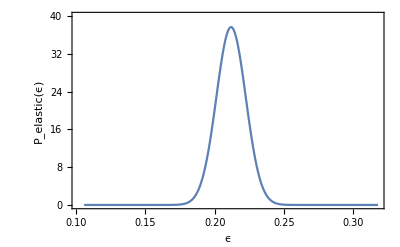

```mathematica
ListPlot[{probabilityEpsilon},PlotRange->{All,{0,40}},FrameLabel->{{"P_elastic(ϵ)",""},{"ϵ","Elastic Energy Loss Probability: Charm 10GeV"}},Joined->True,Frame->True]
```

```mathematica
{elasticBottom50Centre,elasticBottom50Width,elasticBottom50}=getElastic[50,5 fmToGev, 0.3,0.25, 2, mB]
```

{0.0567527,0.000567527,Function[{eps$},Exp[-(-eps$+elasticCentre$41507)^2/(2 elasticWidth$41507^2)]/(√(2 π) elasticWidth$41507)]}

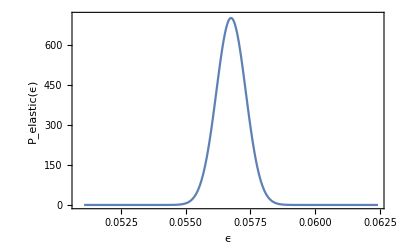

```mathematica
ListPlot[Table[{eps,elasticBottom50[eps]}, {eps, elasticBottom50Centre-10*elasticBottom50Width,elasticBottom50Centre+10*elasticBottom50Width,0.01*elasticBottom50Width}],PlotRange->{All,{0,710}},FrameLabel->{{"P_elastic(ϵ)",""},{"ϵ","Elastic Energy Loss Probability: Bottom 50GeV "}},Joined->True,Frame->True]
```

```mathematica
probabilityEpsilon = Table[{eps,  probabilityElasticEpsilon[32,5 fmToGev, 0.2,0.25, 2, 1.5][eps]}, {eps,0, 0.2,0.00001}];
ListPlot[{probabilityEpsilon},PlotRange->All]
```

### pTot (combined)

Show for different energies (maybe 4 of them) for both charm and bottom

#### Charm

```mathematica
pTotUncorrCharmPlot={pTotUncorrCharm10to200[[1]],pTotUncorrCharm10to200[[2]],pTotUncorrCharm10to200[[3]],pTotUncorrCharm10to200[[4]]}
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
pTotCorrCharmPlot={pTotCorrCharm10to200[[1]],pTotCorrCharm10to200[[2]],pTotCorrCharm10to200[[3]],pTotCorrCharm10to200[[4]]}
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
pTotUncorrBottomPlot={pTotUncorrBottom10to200[[1]],pTotUncorrBottom10to200[[2]],pTotUncorrBottom10to200[[3]],pTotUncorrBottom10to200[[4]]}
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
pTotCorrBottomPlot={pTotCorrCharm10to200[[1]],pTotCorrCharm10to200[[2]],pTotCorrCharm10to200[[3]],pTotCorrCharm10to200[[4]]}
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

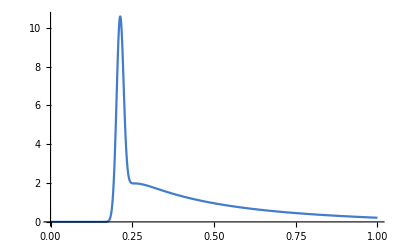
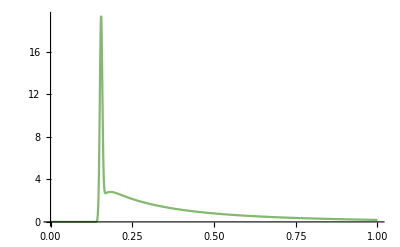
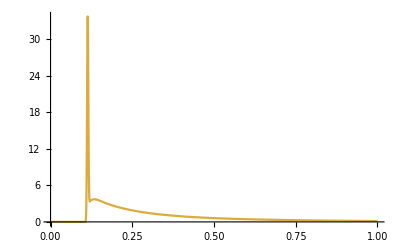
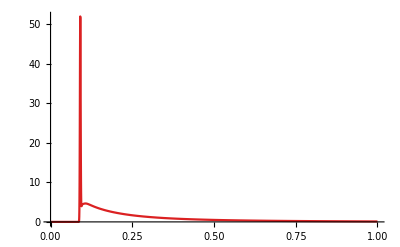

```mathematica
plotspTotCharmUncorr=Table[Plot[pTotUncorrCharmPlot[[i]][x],{x,0, 1}, PlotRange->All,PlotStyle->ColorData["Rainbow",i/Length[pTotCorrCharmPlot]]],{i,1,Length[pTotUncorrCharmPlot]}]
```

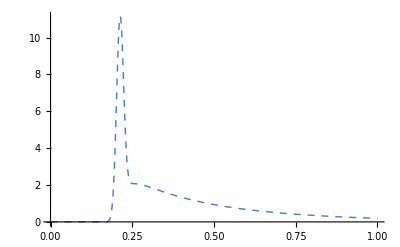
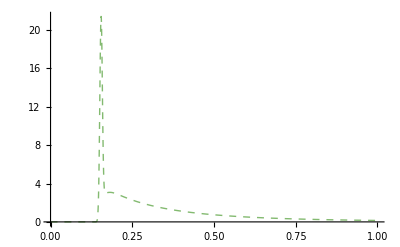
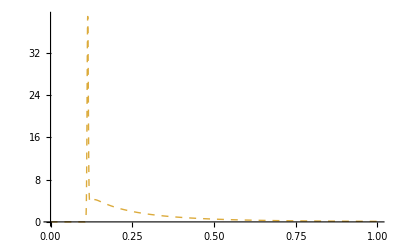
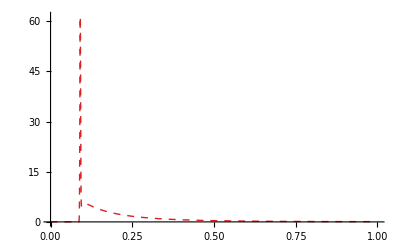

```mathematica
plotspTotCharmCorr=Table[Plot[pTotCorrCharmPlot[[i]][x],{x,0, 1}, PlotRange->All,PlotStyle->{ColorData["Rainbow",i/Length[pTotCorrCharmPlot]],Dashed,Thick}],{i,1,Length[pTotCorrCharmPlot]}]
```

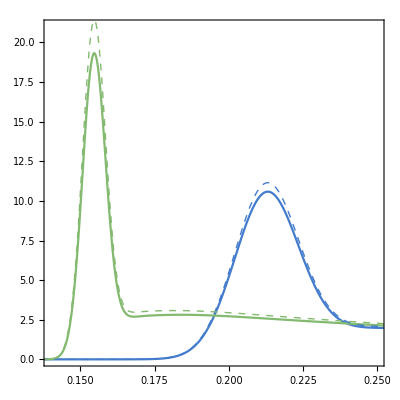

```mathematica
Show[plotspTotCharmUncorr[[1]],plotspTotCharmUncorr[[2]],plotspTotCharmCorr[[1]],plotspTotCharmCorr[[2]],PlotRange->{{0.14,0.25},{0,21}},Frame->True,AspectRatio->1.2/1.2]
```

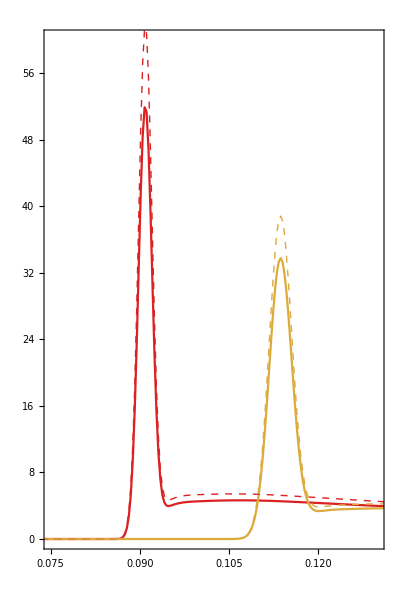

```mathematica
Show[plotspTotCharmUncorr[[4]],plotspTotCharmUncorr[[3]],plotspTotCharmCorr[[4]],plotspTotCharmCorr[[3]],PlotRange->{{0.075,0.13},{0,60}},Frame->True,AspectRatio->1.5/1]
```

```mathematica
Show[plotspTotCharmUncorr,plotspTotCharmCorr,PlotRange->{{0.075,0.25},{0,20}},Frame->True]
```

```mathematica
Show[plotspTotCharmUncorr,plotspTotCharmCorr,PlotRange->All,Epilog->Inset[LineLegend[Table[ColorData["Rainbow",j/Length[plotspTotCharmCorr]],{j,1,Length[plotspTotCharmCorr]}],{"10 GeV","20 GeV","30 GeV","40 GeV"},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.9,52}],FrameLabel->{{"P_tot(ϵ)",""},{"ϵ","Combine Energy Loss Distribution for Charm"}},Frame->True]
```

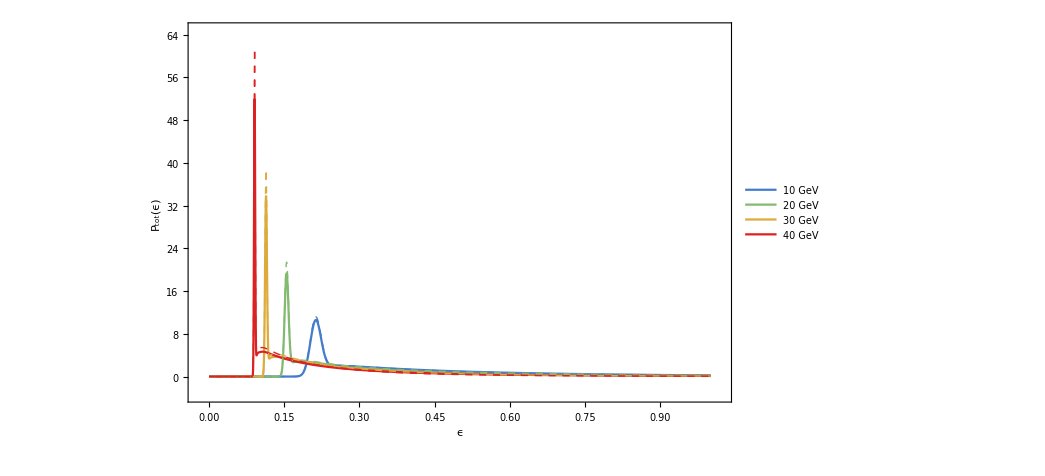

#### Bottom

```mathematica
pTotUncorrBottomPlot={pTotUncorrBottom10to200[[1]],pTotUncorrBottom10to200[[2]],pTotUncorrBottom10to200[[3]],pTotUncorrBottom10to200[[4]]}
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
pTotCorrBottomPlot={pTotCorrBottom10to200[[1]],pTotCorrBottom10to200[[2]],pTotCorrBottom10to200[[3]],pTotCorrBottom10to200[[4]]}
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

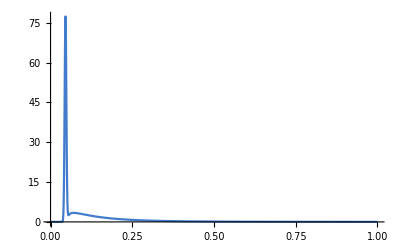
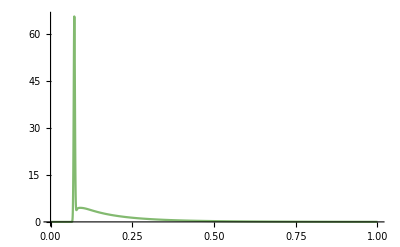
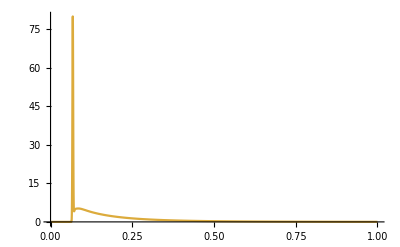
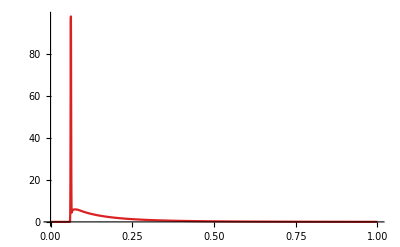

```mathematica
plotspTotBottomUncorr=Table[Plot[pTotUncorrBottomPlot[[i]][x],{x,0, 1}, PlotRange->All,PlotStyle->ColorData["Rainbow",i/Length[pTotCorrBottomPlot]]],{i,1,Length[pTotUncorrCharmPlot]}]
```

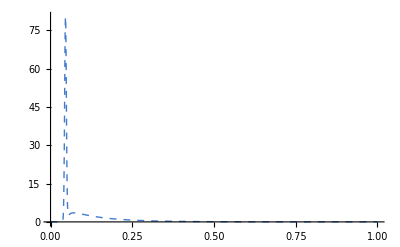
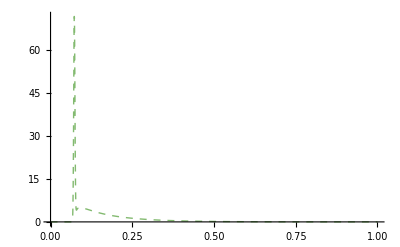
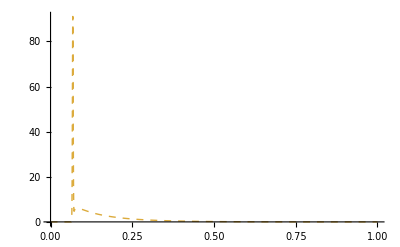
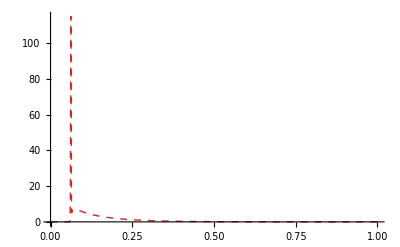

```mathematica
plotspTotBottomCorr=Table[Plot[pTotCorrBottomPlot[[i]][x],{x,0, 1}, PlotRange->All,PlotStyle->{ColorData["Rainbow",i/Length[pTotCorrBottomPlot]],Dashed,Thick}],{i,1,Length[pTotCorrCharmPlot]}]
```

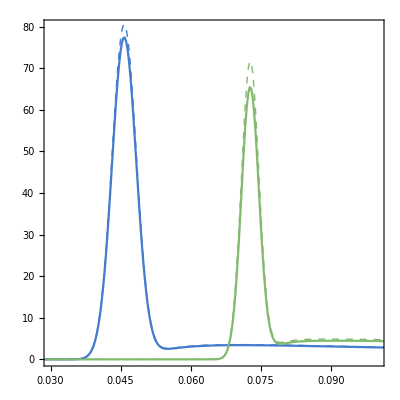

```mathematica
Show[plotspTotBottomUncorr[[1]],plotspTotBottomUncorr[[2]],plotspTotBottomCorr[[1]],plotspTotBottomCorr[[2]],PlotRange->{{0.03,0.1},{0,80}},Frame->True,AspectRatio->1.2/1.2]
```

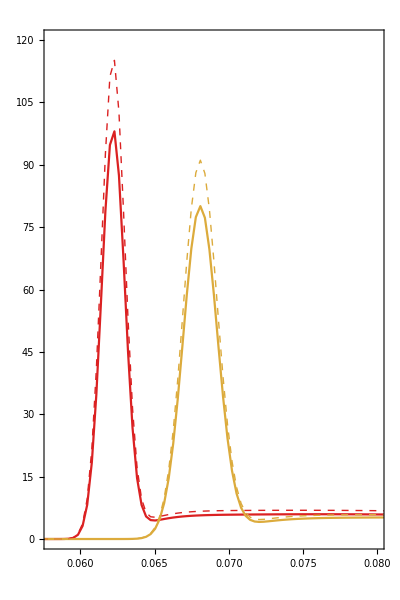

```mathematica
Show[plotspTotBottomUncorr[[4]],plotspTotBottomUncorr[[3]],plotspTotBottomCorr[[4]],plotspTotBottomCorr[[3]],PlotRange->{{0.058,0.08},{0,120}},Frame->True,AspectRatio->1.5/1]
```

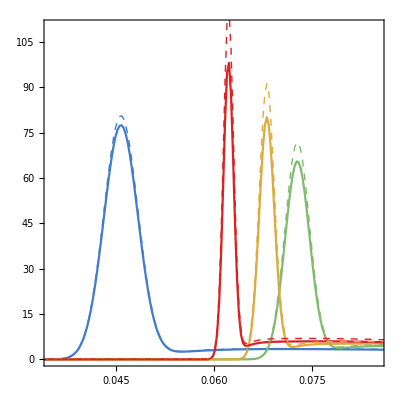

```mathematica
Show[plotspTotBottomUncorr,plotspTotBottomCorr,PlotRange->{{0.035,0.085},{0,110}},Frame->True,AspectRatio->1/1]
```

```mathematica
Show[plotspTotCharmUncorr,plotspTotCharmCorr,PlotRange->{{0.075,0.25},{0,20}},Frame->True]
```

```mathematica
Show[plotspTotBottomUncorr,plotspTotBottomCorr,PlotRange->All,Epilog->Inset[LineLegend[Table[ColorData["Rainbow",j/Length[plotspTotCharmCorr]],{j,1,Length[plotspTotCharmCorr]}],{"10 GeV","20 GeV","30 GeV","40 GeV"},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.9,100}],FrameLabel->{{"P_tot(ϵ)",""},{"ϵ","Combined Energy Loss Distribution for Bottom"}},Frame->True]
```

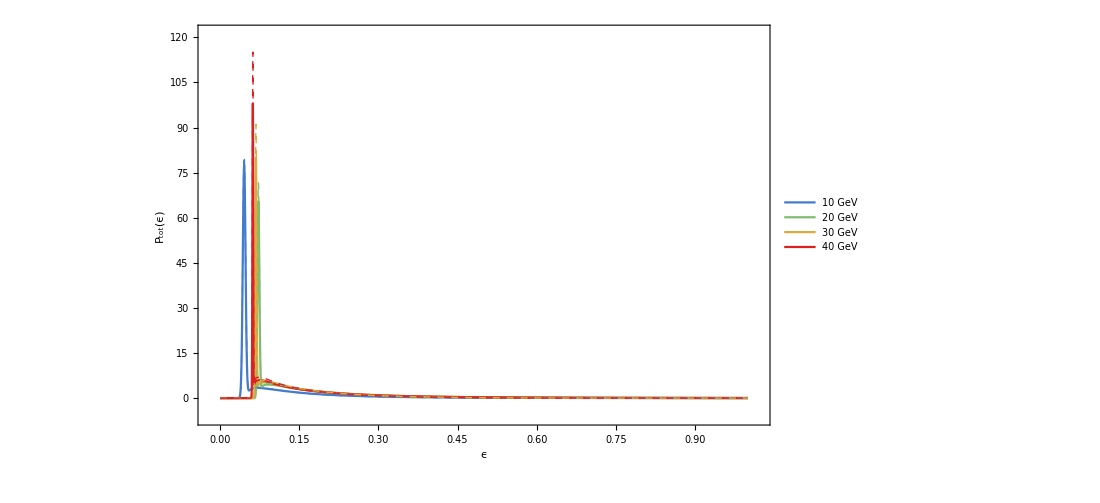

## Old Bugfixing

### Seeing if we reproduce the Old PTot

```mathematica
ClearAll[pTotLTable3]
```

```mathematica
AbsoluteTiming[pTotUncorrCharm10to200=Parallelize[Table[pTotInterpMaxL3[10,0.25, 5*5.068,energy,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,0, 2,10,10,0.1,0.5,0.1],{energy,10,200,10}]]]
```

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-3200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2522.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1924.51] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-9800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6694.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4178.08] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-20000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11828.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5789.53] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::munfl: Exp[-740.51] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-787.279] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-835.737] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-33800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-17229.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6189.27] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-45000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-20700.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5718.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-57800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23909.2] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-713.989] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26743.7] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-713.204] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{37810.3,{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

```mathematica
Manipulate[Plot[pTotUncorrCharm10to200[[i]][eps],{eps,0,1},PlotRange->{{0,1},{0,800}},PlotPoints->2000],{i,1,Length[pTotUncorrCharm10to200],1}]
```

Part::partd: Part specification pTotUncorrCharm10to200⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification pTotUncorrCharm10to200⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification pTotUncorrCharm10to200⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification pTotUncorrCharm10to200⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification pTotUncorrCharm10to200⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
AbsoluteTiming[rAAUncorrCharm10to200=Parallelize[Table[{10*i,rAAPTotIn[pTotUncorrCharm10to200[[i]]]},{i,1,Length[pTotUncorrCharm10to200]}]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.0435256}. NIntegrate obtained 0.440542 and 2.49089×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.0403195}. NIntegrate obtained 0.443551 and 0.0000112269 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.0376805}. NIntegrate obtained 0.4435 and 0.000118882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.0356549}. NIntegrate obtained 0.441271 and 0.0197874 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.0342789}. NIntegrate obtained 0.471367 and 0.141467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.0287085}. NIntegrate obtained 0.420456 and 0.00227738 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.031525}. NIntegrate obtained 0.432517 and 0.00168015 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.0472269}. NIntegrate obtained 0.433959 and 0.0000854706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.0286915}. NIntegrate obtained 0.324812 and 0.0125954 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.0258516}. NIntegrate obtained 0.418485 and 0.0978142 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.0301162}. NIntegrate obtained 0.427603 and 0.0615706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in eps near {eps} = {0.0258516}. NIntegrate obtained 0.398978 and 0.0354088 for the integral and error estimates.

{0.636411,{{10,0.150515},{20,0.195663},{30,0.263234},{40,0.312955},{50,0.352266},{60,0.382846},{70,0.406391},{80,0.423084},{90,0.433959},{100,0.440542},{110,0.443551},{120,0.4435},{130,0.441271},{140,0.471367},{150,0.432517},{160,0.427603},{170,0.420456},{180,0.324812},{190,0.418485},{200,0.398978}}}

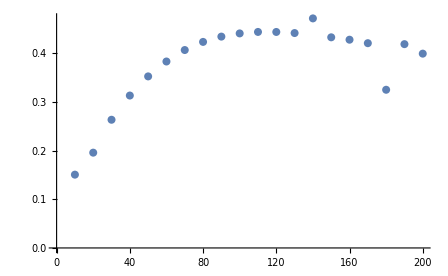

```mathematica
ListPlot[rAAUncorrCharm10to200]
```

```mathematica
pTot10UncorrCharm=pTotInterpMaxL3[10,0.25, 5*5.068,10,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,0, 2,10,10,0.1,0.5,0.1]
```

InterpolatingFunction[…]

```mathematica
AbsoluteTiming[pTot10CorrCharm=pTotInterpMaxL3[10,0.25, 5*5.068,10,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,1, 2,10,10,0.1,0.5,0.1]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: Exp[-787.279] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1047.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-835.737] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1105.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-885.941] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1166.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-740.51] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1358.25] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1715.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2120.34] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2569.61] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1425.99] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1792.93] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2206.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2664.19] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1495.61] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1871.98] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2295.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2760.09] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3054.08] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3548.83] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4000.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4282.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3153.42] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3644.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4078.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4339.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3252.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3738.82] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4394.28] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4151.98] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{50.4773,InterpolatingFunction[…]}

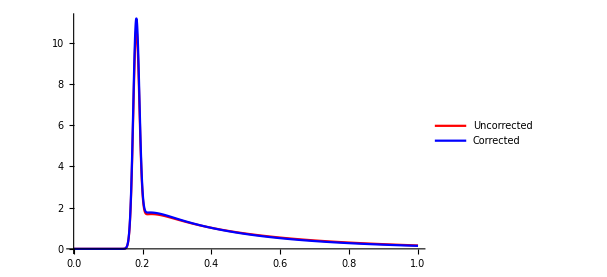

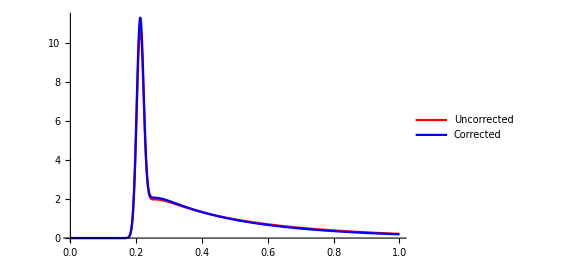

```mathematica
Show[Plot[pTot10UncorrCharm[x],{x,0, 1},PlotStyle-> Red,PlotRange->All,PlotLegends->{"Uncorrected"}],Plot[pTot10CorrCharm[x],{x,0, 1},PlotStyle->Blue, PlotLegends->{"Corrected"},PlotRange->All]]
```

```mathematica
pTot10UncorrCharm2=pTotInterpMaxL2[0.25, 5*5.068,10,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,0, 2,10,10,0.1,0.5,0.1]
```

InterpolatingFunction[…]

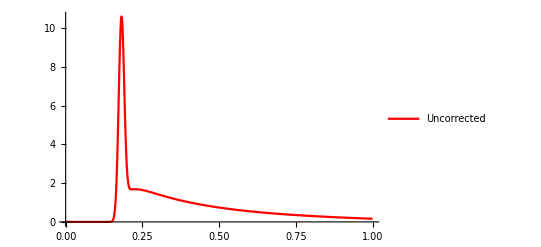

```mathematica
Plot[InterpolatingFunction[…][x],{x,0, 1},PlotStyle-> Red,PlotRange->All,PlotLegends->{"Uncorrected"}]
```

```mathematica
AbsoluteTiming[pTot10CorrCharm2=pTotInterpMaxL2[0.25, 5*5.068,10,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,1, 2,10,10,0.1,0.5,0.1]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: Exp[-787.279] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1047.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-835.737] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1105.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-885.941] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1166.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-740.51] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1358.25] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1715.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2120.34] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2569.61] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1425.99] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1792.93] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2206.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2664.19] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1495.61] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1871.98] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2295.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2760.09] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3054.08] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3548.83] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4000.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4282.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3153.42] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3644.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4078.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4339.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3252.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3738.82] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4394.28] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4151.98] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{50.4773,InterpolatingFunction[…]}

```mathematica
Show[Plot[pTot10UncorrCharm2[x],{x,0, 1},PlotStyle-> Red,PlotRange->All,PlotLegends->{"Uncorrected"}],Plot[pTot10CorrCharm2[x],{x,0, 1},PlotStyle->Blue, PlotLegends->{"Corrected"},PlotRange->All]]
```

### We did not. So check components

```mathematica
expMeanUncorrCharm10= Exp[-meanGluonCorrection[10,cR, cA, mu, aS, 5 fmToGev, lambda, mG,mC,0]]
```

0.270118

```mathematica
pRadsUncorrCharm10= pRadTableExpIn[expMeanUncorrCharm10,10,cR, cA, mu, aS,5 fmToGev, lambda, mG, mC,0]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

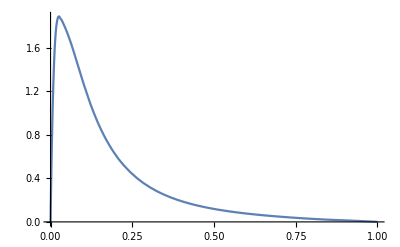
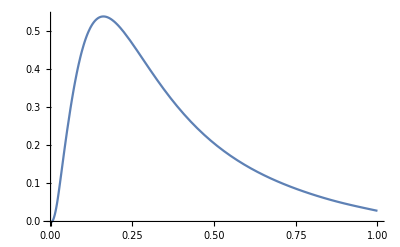
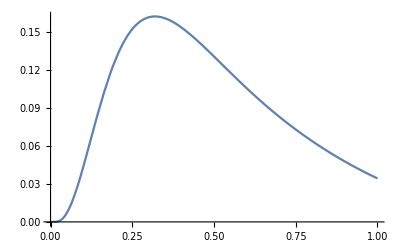
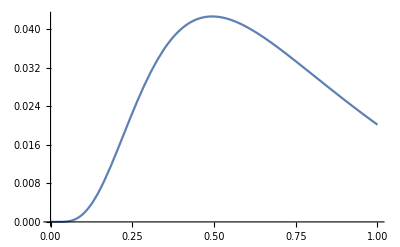
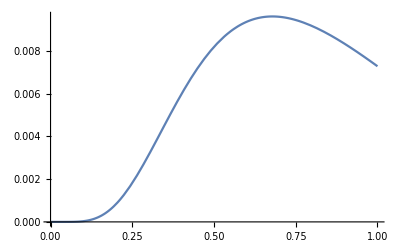
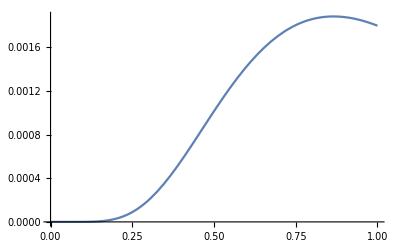
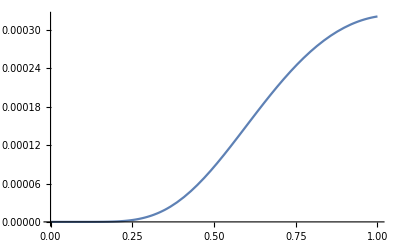

```mathematica
plotspRadUncorrCharm10=Table[Plot[expMeanUncorrCharm10*pRadsUncorrCharm10[[i]][x] HeavisideTheta[x] HeavisideTheta[1-x],{x,0, 1}, PlotRange->All],{i,1,Length[pRadsUncorrCharm10]}]
```

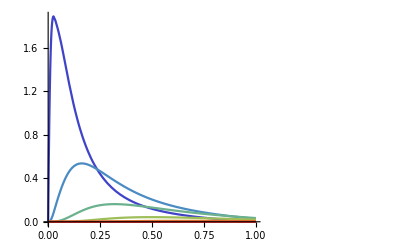

```mathematica
remapColors[plots_,colorFunction_:(Hue[#,0.6,0.6]&)]:=Module[{n=0,colors,ncolors},colors=DeleteDuplicates@Cases[First@#,_RGBColor|_Hue,Infinity]&/@plots;
ncolors=Length@Flatten@colors;
newcolors=Table[colorFunction@(i/ncolors),{i,ncolors}];
MapThread[#1/. (#1->newcolors[[++n]]&/@#2)&,{plots,colors}]]

legend[col_]:=Graphics[Table[{{col[[i]],z=.04+.04 i;Line[{{7,z},{8,z}}]},Text[Style[ToString[i]],{8.6,z}]},{i,Length[col]}]]
Show[{remapColors[plotspRadUncorrCharm10,ColorData["Rainbow"]],legend@newcolors},PlotRange->{{0,1},All}]
```

This seems very much the same as Before (comparing to Poisson Convolution Radiative Charm). Checking quantitatively:

```mathematica
ClearAll[pTotUncorrCharm10]
```

```mathematica
pTotUncorrCharm10[x_]:= Sum[expMeanUncorrCharm10*pRadsUncorrCharm10[[i]][x]*HeavisideTheta[x] HeavisideTheta[1-x],{i,1,Length[pRadsUncorrCharm10]}];
NIntegrate[pTotUncorrCharm10[x],{x,0,1}]
```

0.709204

```mathematica
expMeanUncorrCharm10
```

0.270118

```mathematica
expMeanUncorrCharm10Try2= Exp[-meanGluonCorrection[10,cR, cA, mu, aS, 5 fmToGev, lambda, mG,mC,0]]
```

0.270118

```mathematica
expMeanUncorrCharm10Old=0.27012277461828915
```

0.270123

```mathematica
pTotUncorrCharm10OldExp[x_]:= Sum[expMeanUncorrCharm10Old*pRadsUncorrCharm10[[i]][x]*HeavisideTheta[x] HeavisideTheta[1-x],{i,1,Length[pRadsUncorrCharm10]}];
NIntegrate[pTotUncorrCharm10[x],{x,0,1}]
```

0.709204

```mathematica
expMeanUncorrCharm10Try3= Exp[-meanGluonCorrectionNoAccuracy[10,cR, cA, mu, aS, 5 fmToGev, lambda, mG,mC,0]]
```

0.270118

```mathematica
expMeanUncorrCharm10Try4= Exp[-meanGluonCorrectionNoDuffy[10,cR, cA, mu, aS, 5 fmToGev, lambda, mG,mC,0]]
```

0.270123

Duffy Coordinates thing did change it!!

```mathematica
pRadTableExpInOldRhoRegions
```

```mathematica
pRadsUncorrCharm10OldRhoRegions= pRadTableExpInOldRhoRegions[expMeanUncorrCharm10Try4,10,cR, cA, mu, aS,5 fmToGev, lambda, mG, mC,0]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

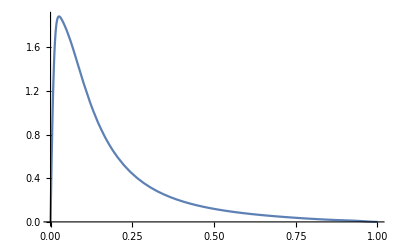
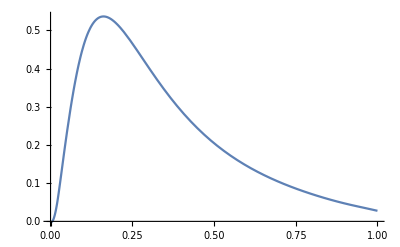
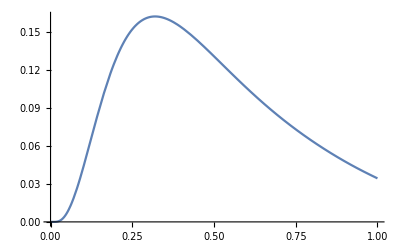
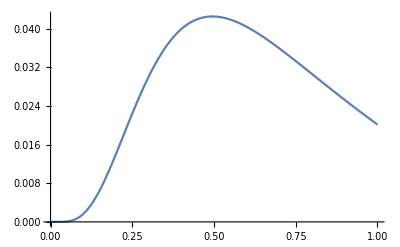
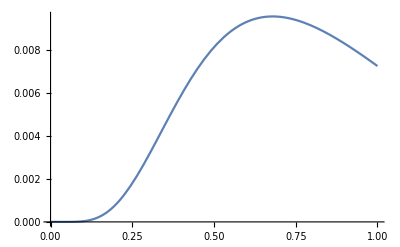
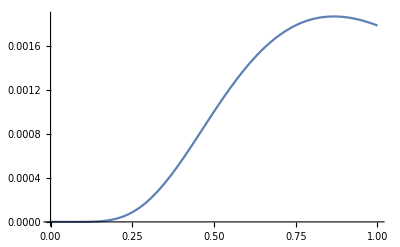
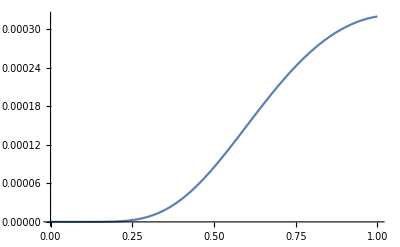

```mathematica
plotspRadUncorrCharm10OldRhoRegions=Table[Plot[expMeanUncorrCharm10Try4*pRadsUncorrCharm10OldRhoRegions[[i]][x] HeavisideTheta[x] HeavisideTheta[1-x],{x,0, 1}, PlotRange->All],{i,1,Length[pRadsUncorrCharm10]}]
```

```mathematica
pTotUncorrCharm10OldRho[x_]:= Sum[expMeanUncorrCharm10Try4*pRadsUncorrCharm10OldRhoRegions[[i]][x]*HeavisideTheta[x] HeavisideTheta[1-x],{i,1,Length[pRadsUncorrCharm10OldRhoRegions]}];
NIntegrate[pTotUncorrCharm10OldRho[x],{x,0,1}]
```

0.708215

This is still not exactly the same as before but definitely agrees better!
Now trying without accuracy goal for everything. If not that then my guess is it’s the integration method (interpolationPointsSubDivision)

```mathematica
pRadsUncorrCharm10NoAccuracy= pRadTableExpInOldRhoRegions[expMeanUncorrCharm10Try4,10,cR, cA, mu, aS,5 fmToGev, lambda, mG, mC,0]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
plotspRadUncorrCharm10OldRhoRegions=Table[Plot[expMeanUncorrCharm10Try4*pRadsUncorrCharm10OldRhoRegions[[i]][x] HeavisideTheta[x] HeavisideTheta[1-x],{x,0, 1}, PlotRange->All],{i,1,Length[pRadsUncorrCharm10]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pTotUncorrCharm10OldRho[x_]:= Sum[expMeanUncorrCharm10Try4*pRadsUncorrCharm10OldRhoRegions[[i]][x]*HeavisideTheta[x] HeavisideTheta[1-x],{i,1,Length[pRadsUncorrCharm10OldRhoRegions]}];
NIntegrate[pTotUncorrCharm10OldRho[x],{x,0,1}]
```

0.708215

So it wasn' t accuracy goal . My guess is it' s the integration method (interpolationPointsSubDivision). But very small difference so that’s okay (the method is far more efficient).

### Trying again

```mathematica
AbsoluteTiming[pTot10UncorrCharm2=pTotInterpMaxL3[10,0.25, 5*5.068,10,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,0, 2,10,10,0.1,0.5,0.1]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-787.279] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1047.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-835.737] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1105.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-885.941] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1166.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-740.51] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1358.25] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1715.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2120.34] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2569.61] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1425.99] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2206.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1792.93] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2664.19] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1495.61] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2295.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1871.98] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2760.09] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3054.08] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3548.83] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4000.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4282.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3153.42] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3644.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4078.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4339.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3252.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3738.82] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4151.98] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4394.28] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{457.357,InterpolatingFunction[…]}

```mathematica
AbsoluteTiming[pTot10CorrCharm2=pTotInterpMaxL3[10,0.25, 5*5.068,10,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,1, 2,10,10,0.1,0.5,0.1]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-787.279] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1047.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-835.737] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1105.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-885.941] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1166.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-740.51] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1358.25] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1715.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2120.34] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2569.61] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1425.99] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1792.93] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2206.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2664.19] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1495.61] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1871.98] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2295.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2760.09] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3054.08] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3548.83] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4000.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4282.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3153.42] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3644.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4078.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4339.94] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3252.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3738.82] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4151.98] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4394.28] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{451.402,InterpolatingFunction[…]}

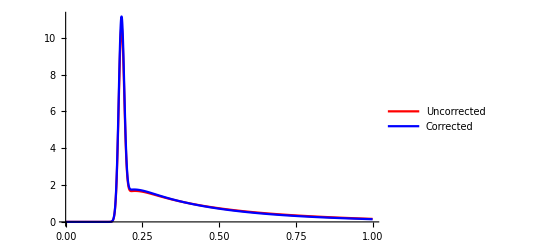

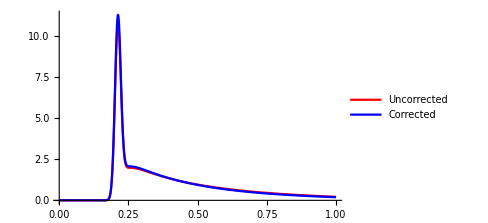

```mathematica
Show[Plot[pTot10UncorrCharm2[x],{x,0, 1},PlotStyle-> Red,PlotRange->All,PlotLegends->{"Uncorrected"}],Plot[pTot10CorrCharm2[x],{x,0, 1},PlotStyle->Blue, PlotLegends->{"Corrected"},PlotRange->All]]
```

So the change to Prads didn' t fix the problem . Now check elastic

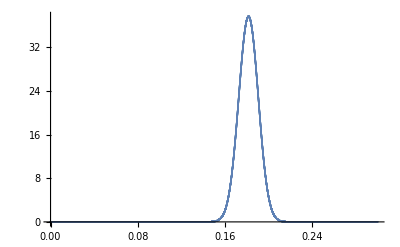

```mathematica
ListPlot[Table[{eps,probabilityElasticEpsilon[10,5 fmToGev, 0.3,0.25, 2, 1.5][eps] },{eps,0,0.3,0.00001}],PlotRange->All]
```

This is different to before!

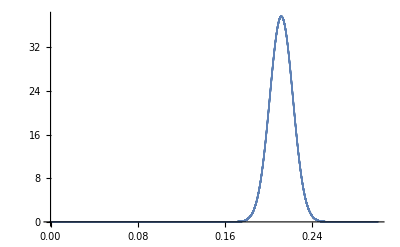

{37.6728,{eps→0.211794}}

General::munfl: Exp[-708.451] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.528] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.604] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

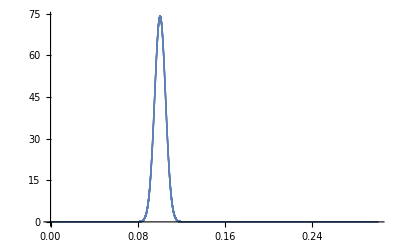

```mathematica
ListPlot[Table[{eps,probabilityElasticEpsilon[10,5 fmToGev, 0.2,0.25, 2, 1.5][eps] },{eps,0,0.3,0.00001}],PlotRange->All]
```

This matches original "Elastic Present" code

I' m not sold on what to do for the epsilon elastic probability (I think what I have now is right, but obviously gives different result to before), but I' ll try what I used to have and see what happens to RAA, because I suspect that' s not what' s causing the main problem .

```mathematica
AbsoluteTiming[pTot10UncorrCharm3=pTotInterpMaxL3[10,0.25, 5*5.068,10,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,0, 2,10,10,0.1,0.5,0.1]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-734.575] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-771.216] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-967.797] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1186.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1427.84] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-808.748] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1009.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1233.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1478.75] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-847.173] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1052.67] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1280.46] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1530.55] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1691.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1977.05] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2285.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2547.59] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1746.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2036.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2349.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2615.44] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1802.93] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2097.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2414.56] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2684.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{471.226,InterpolatingFunction[…]}

```mathematica
AbsoluteTiming[pTot10CorrCharm3=pTotInterpMaxL3[10,0.25, 5*5.068,10,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,1, 2,10,10,0.1,0.5,0.1]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-734.575] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-771.216] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-967.797] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1186.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1427.84] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-808.748] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1009.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1233.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1478.75] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-847.173] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1052.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.46] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1530.55] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1691.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1977.05] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2285.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2547.59] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1746.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2036.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2349.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2615.44] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1802.93] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2097.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2414.56] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2684.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{497.883,InterpolatingFunction[…]}

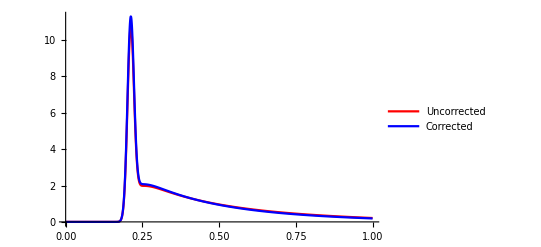

```mathematica
Show[Plot[pTot10UncorrCharm3[x],{x,0, 1},PlotStyle-> Red,PlotRange->All,PlotLegends->{"Uncorrected"}],Plot[pTot10CorrCharm3[x],{x,0, 1},PlotStyle->Blue, PlotLegends->{"Corrected"},PlotRange->All]]
```

So this does match what I had before

-Graphics-

```mathematica
AbsoluteTiming[pTotUncorrCharm10to200=Parallelize[Table[pTotInterpMaxL3[10,0.25, 5*5.068,energy,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,0, 2,10,10,0.1,0.5,0.1],{energy,10,200,10}]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.99753 and 0.00210665 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.02517 and 0.00248056 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-3200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2534.51] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1946.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-9800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6725.89] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4228.66] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-20000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11884.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5869.09] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.00933 and 0.00209821 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.0302 and 0.00274896 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

General::munfl: Exp[-742.095] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-845.36] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.01818 and 0.00230689 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03461 and 0.00306454 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03825 and 0.00318423 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04361 and 0.0034404 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04738 and 0.00361645 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-33800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-17314.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6291.41] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-45000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-20805.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5829.01] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.05071 and 0.00334213 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-57800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24033.7] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26888.2] is too small to represent as a normalized machine number; precision may be lost.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::subpar will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04083 and 0.00316924 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04471 and 0.00342344 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04969 and 0.00350022 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.05173 and 0.00337516 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

{4350.88,{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

```mathematica
ClearAll[rAAPTotIn]
```

```mathematica
rAAPTotInRec[pTot_]:=rAAPTotInRec[pTot]=NIntegrate [FullSimplify[pTot[epsi]*HeavisideTheta[1-epsi]*(1-epsi)^5],{epsi,0,1},Method->"InterpolationPointsSubdivision",MinRecursion->20,MaxRecursion->50]
```

```mathematica
AbsoluteTiming[rAAUncorrCharm10to200New=Parallelize[Table[{10*i,rAAPTotInRec[pTotUncorrCharm10to200[[i]]]},{i,1,Length[pTotUncorrCharm10to200]}]]]
```

{108.915,{{10,0.145183},{20,0.199596},{30,0.271422},{40,0.330327},{50,0.380429},{60,0.422036},{70,0.458782},{80,0.490969},{90,0.519356},{100,0.544652},{110,0.56782},{120,0.589171},{130,0.60695},{140,0.624485},{150,0.639702},{160,0.654276},{170,0.66633},{180,0.677155},{190,0.687612},{200,0.696777}}}

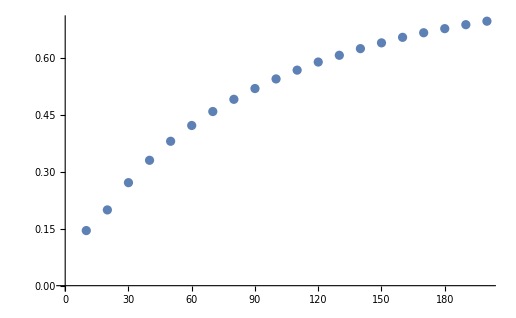

```mathematica
ListPlot[rAAUncorrCharm10to200New]
```

### Trying to find how best to perform the integral in PTot where integrand is zero on most of integration region

```mathematica
elasticWidthBottom190= elasticWidth[190,5*5.068, 0.3,0.25, 2,4.75]
elasticCentreBottom190=elasticCentre[190,5*5.068, 0.3,0.25, 2,4.75]
```

0.0000675238

0.025659

```mathematica
probabilityElastic1= probabilityElasticEpsilon[190,  5*5.068, aS, temp, 2,mB]

expMean1= Exp[-meanGluonCorrection[190,cR, cA, mu, aS, 5*5.068, lambda, mG,mB,0]]

pRadsTable= pRadTableExpIn[expMean1,190,cR, cA, mu, aS,5*5.068, lambda, mG, mB,0]
```

probabilityElasticEpsilon[190,25.34,0.3,0.25,2,4.75]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.127267

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
probabilityElastic1= probabilityElasticEpsilon[190,  5*5.068, aS, temp, nF,mB]
```

probabilityElasticEpsilon[190,25.34,0.3,0.25,2,4.75]

```mathematica
0.0283599924942019 to 0.12221806289167962
```

```mathematica
fnTryInt[x_]:=probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}]
```

```mathematica
(Integrate[fnTryInt[x],{x,Max[0.0283599924942019-1,0],Min[0.0283599924942019,1]}])
```

∫_0^0.02836 (0.127267 InterpolatingFunction[…][x]+0.127267 InterpolatingFunction[…][x]+0.127267 InterpolatingFunction[…][x]+0.127267 InterpolatingFunction[…][x]+0.127267 InterpolatingFunction[…][x]+0.127267 InterpolatingFunction[…][x]+0.127267 InterpolatingFunction[…][x]) probabilityElasticEpsilon[190,25.34,0.3,0.25,2,4.75][0.02836-x]ⅆx

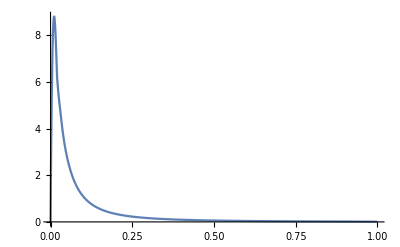

```mathematica
Plot[Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,0,1},PlotRange->All]
```

General::munfl: Exp[-72084.6] is too small to represent as a normalized machine number; precision may be lost.

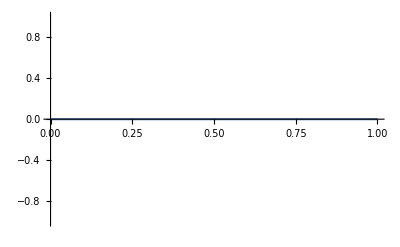

```mathematica
Plot[probabilityElastic1[x],{x,0,1}]
```

```mathematica
AbsoluteTiming[(NIntegrate[probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,Max[0.0283599924942019-1,0],Min[0.0283599924942019,1]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"])]
```

{0.159672,2.128×10^-11}

MinRecursion -> 1, MaxRecursion -> 4 seems to be the fastest working choice here

```mathematica
AbsoluteTiming[(NIntegrate[probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,Max[0.0283599924942019-1,0],Min[0.0283599924942019,1]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision",MinRecursion->1, MaxRecursion->4])]
```

{0.675617,4.30026}

```mathematica
AbsoluteTiming[(NIntegrate[probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,Max[0.0283599924942019-1,0],Min[0.0283599924942019,1]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision", MinRecursion->2, MaxRecursion->4])]
```

{0.858423,4.30026}

```mathematica
AbsoluteTiming[(NIntegrate[probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,Max[0.0283599924942019-1,0],Min[0.0283599924942019,1]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision", MinRecursion->10, MaxRecursion->20])]
```

$Aborted

```mathematica
(NIntegrate[probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,Max[0.0283599924942019-1,0],Min[0.0283599924942019,1]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision", MinRecursion->50, MaxRecursion->100])
```

4.30026

```mathematica
(NIntegrate[probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,Max[0.0283599924942019-1,0],Min[0.0283599924942019,1]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision", MinRecursion->500, MaxRecursion->1000])
```

4.30026

```mathematica
probabilityElastic1[0.029035230410730514-x]
```

General::munfl: Exp[-1343.03] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
(NIntegrate[probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,0,0.0031},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"])
```

4.30022

```mathematica
(NIntegrate[probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,0.0026,0.0031},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"])
```

4.29651

```mathematica
trialTable=Table[{x,probabilityElastic1[0.0283599924942019-x]},{x,0,1,0.01}];
ListPlot[trialTable,PlotRange->All]
```

```mathematica
ClearAll[testingWidth]
```

```mathematica
testingWidth[width_]:=Module[{root1,root2},root1=x/.FindRoot[probabilityElastic1[0.0283599924942019-x]==0,{x,-elasticCentreBottom190-width*elasticWidthBottom190+0.0283599924942019}];
root2=x/.FindRoot[probabilityElastic1[0.0283599924942019-x]==0,{x,-elasticCentreBottom190+width*elasticWidthBottom190+0.0283599924942019}];Return[NIntegrate[probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,root1,root2},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"]]]
```

```mathematica
testingWidthApprox[width_]:=NIntegrate[probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}],{x,Max[0,-elasticCentreBottom190-width*elasticWidthBottom190+0.0283599924942019],Min[1,-elasticCentreBottom190+width*elasticWidthBottom190+0.0283599924942019]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"]
```

```mathematica
testingWidthApprox[10]
```

4.30026

```mathematica
testingWidth[5]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

4.30026

```mathematica
testingWidth[10]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

4.30026

```mathematica
testingWidth[2]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

4.30026

```mathematica
FindRoot[probabilityElastic1[0.0283599924942019-x]==0,{x,0.003}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→0.00378348}

```mathematica
FindRoot[probabilityElastic1[0.0283599924942019-x]==0,{x,-elasticCentreBottom190+8*elasticWidthBottom190+0.0283599924942019}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→0.00385611}

```mathematica
FindRoot[probabilityElastic1[0.0283599924942019-x]==0,{x,-elasticCentreBottom190+5*elasticWidthBottom190+0.0283599924942019}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→0.00379134}

```mathematica
trialTable=Table[{x,probabilityElastic1[0.0283599924942019-x]},{x,0.0026,0.0031,0.00001}];
ListPlot[trialTable,PlotRange->{All,{0,1}}]
```

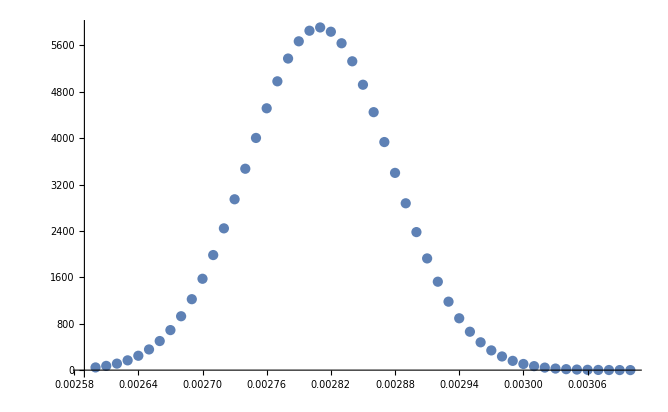

```mathematica
trialTable=Table[{x,probabilityElastic1[0.0283599924942019-x]},{x,0.0026,0.0031,0.00001}];
ListPlot[trialTable,PlotRange->All]
```

From below we see there are no negatives - only zeros! so the integral over the non - zero region should be the value of the integral!! But that' s not what' s happening - we are instead getting that integrating over larger region severely decreases the value of the integral!!

```mathematica
trialTable2=Table[{x,probabilityElastic1[0.0283599924942019-x]},{x,0,1,0.001}]
```

General::munfl: Exp[-872.953] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1126.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1942.41] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{0.,0.},{0.001,3.28827×10^-154},{0.002,2.0292×10^-28},{0.003,105.944},{0.004,4.69341×10^-65},{0.005,1.76938×10^-227},{0.006,0.},{0.007,0.},{0.008,0.},{0.009,0.},{0.01,0.},{0.011,0.},{0.012,0.},{0.013,0.},{0.014,0.},{0.015,0.},{0.016,0.},{0.017,0.},{0.018,0.},{0.019,0.},{0.02,0.},{0.021,0.},{0.022,0.},{0.023,0.},{0.024,0.},{0.025,0.},{0.026,0.},{0.027,0.},{0.028,0.},{0.029,0.},{0.03,0.},{0.031,0.},{0.032,0.},{0.033,0.},{0.034,0.},{0.035,0.},{0.036,0.},{0.037,0.},{0.038,0.},{0.039,0.},{0.04,0.},{0.041,0.},{0.042,0.},{0.043,0.},{0.044,0.},{0.045,0.},{0.046,0.},{0.047,0.},{0.048,0.},{0.049,0.},{0.05,0.},{0.051,0.},{0.052,0.},{0.053,0.},{0.054,0.},{0.055,0.},{0.056,0.},{0.057,0.},{0.058,0.},{0.059,0.},{0.06,0.},{0.061,0.},{0.062,0.},{0.063,0.},{0.064,0.},{0.065,0.},{0.066,0.},{0.067,0.},{0.068,0.},{0.069,0.},{0.07,0.},{0.071,0.},{0.072,0.},{0.073,0.},{0.074,0.},{0.075,0.},{0.076,0.},{0.077,0.},{0.078,0.},{0.079,0.},{0.08,0.},{0.081,0.},{0.082,0.},{0.083,0.},{0.084,0.},{0.085,0.},{0.086,0.},{0.087,0.},{0.088,0.},{0.089,0.},{0.09,0.},{0.091,0.},{0.092,0.},{0.093,0.},{0.094,0.},{0.095,0.},{0.096,0.},{0.097,0.},{0.098,0.},{0.099,0.},{0.1,0.},{0.101,0.},{0.102,0.},{0.103,0.},{0.104,0.},{0.105,0.},{0.106,0.},{0.107,0.},{0.108,0.},{0.109,0.},{0.11,0.},{0.111,0.},{0.112,0.},{0.113,0.},{0.114,0.},{0.115,0.},{0.116,0.},{0.117,0.},{0.118,0.},{0.119,0.},{0.12,0.},{0.121,0.},{0.122,0.},{0.123,0.},{0.124,0.},{0.125,0.},{0.126,0.},{0.127,0.},{0.128,0.},{0.129,0.},{0.13,0.},{0.131,0.},{0.132,0.},{0.133,0.},{0.134,0.},{0.135,0.},{0.136,0.},{0.137,0.},{0.138,0.},{0.139,0.},{0.14,0.},{0.141,0.},{0.142,0.},{0.143,0.},{0.144,0.},{0.145,0.},{0.146,0.},{0.147,0.},{0.148,0.},{0.149,0.},{0.15,0.},{0.151,0.},{0.152,0.},{0.153,0.},{0.154,0.},{0.155,0.},{0.156,0.},{0.157,0.},{0.158,0.},{0.159,0.},{0.16,0.},{0.161,0.},{0.162,0.},{0.163,0.},{0.164,0.},{0.165,0.},{0.166,0.},{0.167,0.},{0.168,0.},{0.169,0.},{0.17,0.},{0.171,0.},{0.172,0.},{0.173,0.},{0.174,0.},{0.175,0.},{0.176,0.},{0.177,0.},{0.178,0.},{0.179,0.},{0.18,0.},{0.181,0.},{0.182,0.},{0.183,0.},{0.184,0.},{0.185,0.},{0.186,0.},{0.187,0.},{0.188,0.},{0.189,0.},{0.19,0.},{0.191,0.},{0.192,0.},{0.193,0.},{0.194,0.},{0.195,0.},{0.196,0.},{0.197,0.},{0.198,0.},{0.199,0.},{0.2,0.},{0.201,0.},{0.202,0.},{0.203,0.},{0.204,0.},{0.205,0.},{0.206,0.},{0.207,0.},{0.208,0.},{0.209,0.},{0.21,0.},{0.211,0.},{0.212,0.},{0.213,0.},{0.214,0.},{0.215,0.},{0.216,0.},{0.217,0.},{0.218,0.},{0.219,0.},{0.22,0.},{0.221,0.},{0.222,0.},{0.223,0.},{0.224,0.},{0.225,0.},{0.226,0.},{0.227,0.},{0.228,0.},{0.229,0.},{0.23,0.},{0.231,0.},{0.232,0.},{0.233,0.},{0.234,0.},{0.235,0.},{0.236,0.},{0.237,0.},{0.238,0.},{0.239,0.},{0.24,0.},{0.241,0.},{0.242,0.},{0.243,0.},{0.244,0.},{0.245,0.},{0.246,0.},{0.247,0.},{0.248,0.},{0.249,0.},{0.25,0.},{0.251,0.},{0.252,0.},{0.253,0.},{0.254,0.},{0.255,0.},{0.256,0.},{0.257,0.},{0.258,0.},{0.259,0.},{0.26,0.},{0.261,0.},{0.262,0.},{0.263,0.},{0.264,0.},{0.265,0.},{0.266,0.},{0.267,0.},{0.268,0.},{0.269,0.},{0.27,0.},{0.271,0.},{0.272,0.},{0.273,0.},{0.274,0.},{0.275,0.},{0.276,0.},{0.277,0.},{0.278,0.},{0.279,0.},{0.28,0.},{0.281,0.},{0.282,0.},{0.283,0.},{0.284,0.},{0.285,0.},{0.286,0.},{0.287,0.},{0.288,0.},{0.289,0.},{0.29,0.},{0.291,0.},{0.292,0.},{0.293,0.},{0.294,0.},{0.295,0.},{0.296,0.},{0.297,0.},{0.298,0.},{0.299,0.},{0.3,0.},{0.301,0.},{0.302,0.},{0.303,0.},{0.304,0.},{0.305,0.},{0.306,0.},{0.307,0.},{0.308,0.},{0.309,0.},{0.31,0.},{0.311,0.},{0.312,0.},{0.313,0.},{0.314,0.},{0.315,0.},{0.316,0.},{0.317,0.},{0.318,0.},{0.319,0.},{0.32,0.},{0.321,0.},{0.322,0.},{0.323,0.},{0.324,0.},{0.325,0.},{0.326,0.},{0.327,0.},{0.328,0.},{0.329,0.},{0.33,0.},{0.331,0.},{0.332,0.},{0.333,0.},{0.334,0.},{0.335,0.},{0.336,0.},{0.337,0.},{0.338,0.},{0.339,0.},{0.34,0.},{0.341,0.},{0.342,0.},{0.343,0.},{0.344,0.},{0.345,0.},{0.346,0.},{0.347,0.},{0.348,0.},{0.349,0.},{0.35,0.},{0.351,0.},{0.352,0.},{0.353,0.},{0.354,0.},{0.355,0.},{0.356,0.},{0.357,0.},{0.358,0.},{0.359,0.},{0.36,0.},{0.361,0.},{0.362,0.},{0.363,0.},{0.364,0.},{0.365,0.},{0.366,0.},{0.367,0.},{0.368,0.},{0.369,0.},{0.37,0.},{0.371,0.},{0.372,0.},{0.373,0.},{0.374,0.},{0.375,0.},{0.376,0.},{0.377,0.},{0.378,0.},{0.379,0.},{0.38,0.},{0.381,0.},{0.382,0.},{0.383,0.},{0.384,0.},{0.385,0.},{0.386,0.},{0.387,0.},{0.388,0.},{0.389,0.},{0.39,0.},{0.391,0.},{0.392,0.},{0.393,0.},{0.394,0.},{0.395,0.},{0.396,0.},{0.397,0.},{0.398,0.},{0.399,0.},{0.4,0.},{0.401,0.},{0.402,0.},{0.403,0.},{0.404,0.},{0.405,0.},{0.406,0.},{0.407,0.},{0.408,0.},{0.409,0.},{0.41,0.},{0.411,0.},{0.412,0.},{0.413,0.},{0.414,0.},{0.415,0.},{0.416,0.},{0.417,0.},{0.418,0.},{0.419,0.},{0.42,0.},{0.421,0.},{0.422,0.},{0.423,0.},{0.424,0.},{0.425,0.},{0.426,0.},{0.427,0.},{0.428,0.},{0.429,0.},{0.43,0.},{0.431,0.},{0.432,0.},{0.433,0.},{0.434,0.},{0.435,0.},{0.436,0.},{0.437,0.},{0.438,0.},{0.439,0.},{0.44,0.},{0.441,0.},{0.442,0.},{0.443,0.},{0.444,0.},{0.445,0.},{0.446,0.},{0.447,0.},{0.448,0.},{0.449,0.},{0.45,0.},{0.451,0.},{0.452,0.},{0.453,0.},{0.454,0.},{0.455,0.},{0.456,0.},{0.457,0.},{0.458,0.},{0.459,0.},{0.46,0.},{0.461,0.},{0.462,0.},{0.463,0.},{0.464,0.},{0.465,0.},{0.466,0.},{0.467,0.},{0.468,0.},{0.469,0.},{0.47,0.},{0.471,0.},{0.472,0.},{0.473,0.},{0.474,0.},{0.475,0.},{0.476,0.},{0.477,0.},{0.478,0.},{0.479,0.},{0.48,0.},{0.481,0.},{0.482,0.},{0.483,0.},{0.484,0.},{0.485,0.},{0.486,0.},{0.487,0.},{0.488,0.},{0.489,0.},{0.49,0.},{0.491,0.},{0.492,0.},{0.493,0.},{0.494,0.},{0.495,0.},{0.496,0.},{0.497,0.},{0.498,0.},{0.499,0.},{0.5,0.},{0.501,0.},{0.502,0.},{0.503,0.},{0.504,0.},{0.505,0.},{0.506,0.},{0.507,0.},{0.508,0.},{0.509,0.},{0.51,0.},{0.511,0.},{0.512,0.},{0.513,0.},{0.514,0.},{0.515,0.},{0.516,0.},{0.517,0.},{0.518,0.},{0.519,0.},{0.52,0.},{0.521,0.},{0.522,0.},{0.523,0.},{0.524,0.},{0.525,0.},{0.526,0.},{0.527,0.},{0.528,0.},{0.529,0.},{0.53,0.},{0.531,0.},{0.532,0.},{0.533,0.},{0.534,0.},{0.535,0.},{0.536,0.},{0.537,0.},{0.538,0.},{0.539,0.},{0.54,0.},{0.541,0.},{0.542,0.},{0.543,0.},{0.544,0.},{0.545,0.},{0.546,0.},{0.547,0.},{0.548,0.},{0.549,0.},{0.55,0.},{0.551,0.},{0.552,0.},{0.553,0.},{0.554,0.},{0.555,0.},{0.556,0.},{0.557,0.},{0.558,0.},{0.559,0.},{0.56,0.},{0.561,0.},{0.562,0.},{0.563,0.},{0.564,0.},{0.565,0.},{0.566,0.},{0.567,0.},{0.568,0.},{0.569,0.},{0.57,0.},{0.571,0.},{0.572,0.},{0.573,0.},{0.574,0.},{0.575,0.},{0.576,0.},{0.577,0.},{0.578,0.},{0.579,0.},{0.58,0.},{0.581,0.},{0.582,0.},{0.583,0.},{0.584,0.},{0.585,0.},{0.586,0.},{0.587,0.},{0.588,0.},{0.589,0.},{0.59,0.},{0.591,0.},{0.592,0.},{0.593,0.},{0.594,0.},{0.595,0.},{0.596,0.},{0.597,0.},{0.598,0.},{0.599,0.},{0.6,0.},{0.601,0.},{0.602,0.},{0.603,0.},{0.604,0.},{0.605,0.},{0.606,0.},{0.607,0.},{0.608,0.},{0.609,0.},{0.61,0.},{0.611,0.},{0.612,0.},{0.613,0.},{0.614,0.},{0.615,0.},{0.616,0.},{0.617,0.},{0.618,0.},{0.619,0.},{0.62,0.},{0.621,0.},{0.622,0.},{0.623,0.},{0.624,0.},{0.625,0.},{0.626,0.},{0.627,0.},{0.628,0.},{0.629,0.},{0.63,0.},{0.631,0.},{0.632,0.},{0.633,0.},{0.634,0.},{0.635,0.},{0.636,0.},{0.637,0.},{0.638,0.},{0.639,0.},{0.64,0.},{0.641,0.},{0.642,0.},{0.643,0.},{0.644,0.},{0.645,0.},{0.646,0.},{0.647,0.},{0.648,0.},{0.649,0.},{0.65,0.},{0.651,0.},{0.652,0.},{0.653,0.},{0.654,0.},{0.655,0.},{0.656,0.},{0.657,0.},{0.658,0.},{0.659,0.},{0.66,0.},{0.661,0.},{0.662,0.},{0.663,0.},{0.664,0.},{0.665,0.},{0.666,0.},{0.667,0.},{0.668,0.},{0.669,0.},{0.67,0.},{0.671,0.},{0.672,0.},{0.673,0.},{0.674,0.},{0.675,0.},{0.676,0.},{0.677,0.},{0.678,0.},{0.679,0.},{0.68,0.},{0.681,0.},{0.682,0.},{0.683,0.},{0.684,0.},{0.685,0.},{0.686,0.},{0.687,0.},{0.688,0.},{0.689,0.},{0.69,0.},{0.691,0.},{0.692,0.},{0.693,0.},{0.694,0.},{0.695,0.},{0.696,0.},{0.697,0.},{0.698,0.},{0.699,0.},{0.7,0.},{0.701,0.},{0.702,0.},{0.703,0.},{0.704,0.},{0.705,0.},{0.706,0.},{0.707,0.},{0.708,0.},{0.709,0.},{0.71,0.},{0.711,0.},{0.712,0.},{0.713,0.},{0.714,0.},{0.715,0.},{0.716,0.},{0.717,0.},{0.718,0.},{0.719,0.},{0.72,0.},{0.721,0.},{0.722,0.},{0.723,0.},{0.724,0.},{0.725,0.},{0.726,0.},{0.727,0.},{0.728,0.},{0.729,0.},{0.73,0.},{0.731,0.},{0.732,0.},{0.733,0.},{0.734,0.},{0.735,0.},{0.736,0.},{0.737,0.},{0.738,0.},{0.739,0.},{0.74,0.},{0.741,0.},{0.742,0.},{0.743,0.},{0.744,0.},{0.745,0.},{0.746,0.},{0.747,0.},{0.748,0.},{0.749,0.},{0.75,0.},{0.751,0.},{0.752,0.},{0.753,0.},{0.754,0.},{0.755,0.},{0.756,0.},{0.757,0.},{0.758,0.},{0.759,0.},{0.76,0.},{0.761,0.},{0.762,0.},{0.763,0.},{0.764,0.},{0.765,0.},{0.766,0.},{0.767,0.},{0.768,0.},{0.769,0.},{0.77,0.},{0.771,0.},{0.772,0.},{0.773,0.},{0.774,0.},{0.775,0.},{0.776,0.},{0.777,0.},{0.778,0.},{0.779,0.},{0.78,0.},{0.781,0.},{0.782,0.},{0.783,0.},{0.784,0.},{0.785,0.},{0.786,0.},{0.787,0.},{0.788,0.},{0.789,0.},{0.79,0.},{0.791,0.},{0.792,0.},{0.793,0.},{0.794,0.},{0.795,0.},{0.796,0.},{0.797,0.},{0.798,0.},{0.799,0.},{0.8,0.},{0.801,0.},{0.802,0.},{0.803,0.},{0.804,0.},{0.805,0.},{0.806,0.},{0.807,0.},{0.808,0.},{0.809,0.},{0.81,0.},{0.811,0.},{0.812,0.},{0.813,0.},{0.814,0.},{0.815,0.},{0.816,0.},{0.817,0.},{0.818,0.},{0.819,0.},{0.82,0.},{0.821,0.},{0.822,0.},{0.823,0.},{0.824,0.},{0.825,0.},{0.826,0.},{0.827,0.},{0.828,0.},{0.829,0.},{0.83,0.},{0.831,0.},{0.832,0.},{0.833,0.},{0.834,0.},{0.835,0.},{0.836,0.},{0.837,0.},{0.838,0.},{0.839,0.},{0.84,0.},{0.841,0.},{0.842,0.},{0.843,0.},{0.844,0.},{0.845,0.},{0.846,0.},{0.847,0.},{0.848,0.},{0.849,0.},{0.85,0.},{0.851,0.},{0.852,0.},{0.853,0.},{0.854,0.},{0.855,0.},{0.856,0.},{0.857,0.},{0.858,0.},{0.859,0.},{0.86,0.},{0.861,0.},{0.862,0.},{0.863,0.},{0.864,0.},{0.865,0.},{0.866,0.},{0.867,0.},{0.868,0.},{0.869,0.},{0.87,0.},{0.871,0.},{0.872,0.},{0.873,0.},{0.874,0.},{0.875,0.},{0.876,0.},{0.877,0.},{0.878,0.},{0.879,0.},{0.88,0.},{0.881,0.},{0.882,0.},{0.883,0.},{0.884,0.},{0.885,0.},{0.886,0.},{0.887,0.},{0.888,0.},{0.889,0.},{0.89,0.},{0.891,0.},{0.892,0.},{0.893,0.},{0.894,0.},{0.895,0.},{0.896,0.},{0.897,0.},{0.898,0.},{0.899,0.},{0.9,0.},{0.901,0.},{0.902,0.},{0.903,0.},{0.904,0.},{0.905,0.},{0.906,0.},{0.907,0.},{0.908,0.},{0.909,0.},{0.91,0.},{0.911,0.},{0.912,0.},{0.913,0.},{0.914,0.},{0.915,0.},{0.916,0.},{0.917,0.},{0.918,0.},{0.919,0.},{0.92,0.},{0.921,0.},{0.922,0.},{0.923,0.},{0.924,0.},{0.925,0.},{0.926,0.},{0.927,0.},{0.928,0.},{0.929,0.},{0.93,0.},{0.931,0.},{0.932,0.},{0.933,0.},{0.934,0.},{0.935,0.},{0.936,0.},{0.937,0.},{0.938,0.},{0.939,0.},{0.94,0.},{0.941,0.},{0.942,0.},{0.943,0.},{0.944,0.},{0.945,0.},{0.946,0.},{0.947,0.},{0.948,0.},{0.949,0.},{0.95,0.},{0.951,0.},{0.952,0.},{0.953,0.},{0.954,0.},{0.955,0.},{0.956,0.},{0.957,0.},{0.958,0.},{0.959,0.},{0.96,0.},{0.961,0.},{0.962,0.},{0.963,0.},{0.964,0.},{0.965,0.},{0.966,0.},{0.967,0.},{0.968,0.},{0.969,0.},{0.97,0.},{0.971,0.},{0.972,0.},{0.973,0.},{0.974,0.},{0.975,0.},{0.976,0.},{0.977,0.},{0.978,0.},{0.979,0.},{0.98,0.},{0.981,0.},{0.982,0.},{0.983,0.},{0.984,0.},{0.985,0.},{0.986,0.},{0.987,0.},{0.988,0.},{0.989,0.},{0.99,0.},{0.991,0.},{0.992,0.},{0.993,0.},{0.994,0.},{0.995,0.},{0.996,0.},{0.997,0.},{0.998,0.},{0.999,0.},{1.,0.}}

```mathematica
(NIntegrate[FullSimplify[probabilityElastic1[0.0283599924942019-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}]],{x,Max[0.0283599924942019-1,0],Min[0.0283599924942019,1]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"])+ expMean1*probabilityElastic1[0.0283599924942019]
```

General::munfl: Exp[-872.953] is too small to represent as a normalized machine number; precision may be lost.

2.128×10^-11

```mathematica
0.029035230410730514
```

```mathematica
(NIntegrate[FullSimplify[probabilityElastic1[0.029035230410730514-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}]],{x,Max[0.029035230410730514-1,0],Min[0.029035230410730514,1]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"])
```

5.08667

```mathematica
expMean1*probabilityElastic1[0.08133240704587187]
```

General::munfl: Exp[-339900.] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
probabilityElastic1[0.08133240704587187]
```

General::munfl: Exp[-339900.] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
(NIntegrate[FullSimplify[probabilityElastic1[0.08133240704587187-x]*Sum[expMean1*pRadsTable[[j]][x],{j,1,Length[pRadsTable]}]],{x,Max[0.08133240704587187-1,0],Min[0.08133240704587187,1]},PrecisionGoal->3,AccuracyGoal->6,Method->"InterpolationPointsSubdivision"])+ expMean1*probabilityElastic1[0.08133240704587187]
```

General::munfl: Exp[-339900.] is too small to represent as a normalized machine number; precision may be lost.

5.33346×10^-21

```mathematica
elasticCentreBottom190-10*elasticWidthBottom190
```

0.0249838

```mathematica
elasticCentreBottom190+10*elasticWidthBottom190
```

0.0263343

```mathematica
elasticCentreBottom190+10*elasticWidthBottom190+0.1
```

0.126334

```mathematica
0.08133240704587187,5.333456612549186*^-21
```

```mathematica
bottomPTot190UncorrTable=pTotLTable2[0.25, 5*5.068,190,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 4.75,0, 2,10,10,0.1,0.5,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26889.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3612.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7442.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3655.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7503.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1152.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3698.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7564.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1176.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1200.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.125] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-12640.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-19208.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12720.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-19306.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-27144.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-19404.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-27261.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-27378.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-36450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-36585.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-36720.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-47124.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-47278.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-59168.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-47432.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-59340.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-59512.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-72580.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72771.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72962.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-87362.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-87571.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-87780.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-103512.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-103740.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-103968.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-121032.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-121278.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-139920.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-121524.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-140185.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-140450.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-160178.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-160461.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-160745.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-181804.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-182106.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-182408.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-204800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-205120.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-205441.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-229164.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-229503.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-229842.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-254898.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-255255.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-255612.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-282000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-282376.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-282752.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-310472.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-310866.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-340313.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-311260.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-340725.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-341138.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-371522.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-371953.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-372385.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-404101.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-404550.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-405000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-438048.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-438516.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-438985.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-473364.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-473851.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-474338.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-510050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-510555.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-511060.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-548104.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-548628.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-549152.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-587528.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-628321.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-628881.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-588070.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-629442.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-588612.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-670482.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-671061.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-671641.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-714012.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714610.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-758912.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715208.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-759528.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760145.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-805181.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-805815.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-806450.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-852818.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-853471.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-854124.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-901824.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-902496.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-903168.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-952200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-952890.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-953580.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.00394×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.00465×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.00536×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.05706×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.05779×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.05851×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.34325×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.98699×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.0344×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.34855×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.59696×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.41615×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.87259×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.63902×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.42656×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.86725×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.26558×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.50676×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.94066×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.03402×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.64025×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.12958×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.74896×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.4473×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.36182×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.85987×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.57137×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.50124×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.69763×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4.64285×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.38381×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.53858×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.51327×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.69555×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-6.6834×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.7502×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.85571×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.0946×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.93568×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.29543×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.12335×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.49845×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{0.,0.},{0.01,0.},{0.0249838,1.45025×10^-19},{0.0249906,3.92253×10^-19},{0.0249973,1.05038×10^-18},{0.0250041,2.78474×10^-18},{0.0250108,7.30934×10^-18},{0.0250176,1.89946×10^-17},{0.0250243,4.88695×10^-17},{0.0250311,1.24481×10^-16},{0.0250378,3.13925×10^-16},{0.0250446,7.83799×10^-16},{0.0250513,1.9375×10^-15},{0.0250581,4.74171×10^-15},{0.0250648,1.14891×10^-14},{0.0250716,2.75609×10^-14},{0.0250783,6.54573×10^-14},{0.0250851,1.53915×10^-13},{0.0250918,3.5831×10^-13},{0.0250986,8.25837×10^-13},{0.0251053,1.88446×10^-12},{0.0251121,4.25733×10^-12},{0.0251189,9.52236×10^-12},{0.0251256,2.10867×10^-11},{0.0251324,4.62306×10^-11},{0.0251391,1.00348×10^-10},{0.0251459,2.15647×10^-10},{0.0251526,4.58813×10^-10},{0.0251594,9.66462×10^-10},{0.0251661,2.01554×10^-9},{0.0251729,4.16155×10^-9},{0.0251796,8.50698×10^-9},{0.0251864,1.72168×10^-8},{0.0251931,3.44975×10^-8},{0.0251999,6.84352×10^-8},{0.0252066,1.34409×10^-7},{0.0252134,2.61357×10^-7},{0.0252201,5.03149×10^-7},{0.0252269,9.58996×10^-7},{0.0252336,1.80965×10^-6},{0.0252404,3.38087×10^-6},{0.0252471,6.25344×10^-6},{0.0252539,0.0000114516},{0.0252607,0.0000207622},{0.0252674,0.0000372679},{0.0252742,0.0000662299},{0.0252809,0.000116528},{0.0252877,0.000202985},{0.0252944,0.00035007},{0.0253012,0.000597726},{0.0253079,0.00101043},{0.0253147,0.0016911},{0.0253214,0.00280212},{0.0253282,0.00459688},{0.0253349,0.00746613},{0.0253417,0.0120056},{0.0253484,0.0191132},{0.0253552,0.0301257},{0.0253619,0.0470108},{0.0253687,0.0726299},{0.0253754,0.111094},{0.0253822,0.168238},{0.0253889,0.252239},{0.0253957,0.37442},{0.0254025,0.550253},{0.0254092,0.800615},{0.025416,1.1533},{0.0254227,1.64481},{0.0254295,2.32246},{0.0254362,3.24666},{0.025443,4.49348},{0.0254497,6.15723},{0.0254565,8.35305},{0.0254632,11.2192},{0.02547,14.9189},{0.0254767,19.6412},{0.0254835,25.6009},{0.0254902,33.037},{0.025497,42.2088},{0.0255037,53.3903},{0.0255105,66.862},{0.0255172,82.8997},{0.025524,101.761},{0.0255307,123.672},{0.0255375,148.804},{0.0255443,177.263},{0.025551,209.063},{0.0255578,244.114},{0.0255645,282.206},{0.0255713,322.996},{0.025578,366.003},{0.0255848,410.609},{0.0255915,456.069},{0.0255983,501.521},{0.025605,546.016},{0.0256118,588.544},{0.0256185,628.072},{0.0256253,663.586},{0.025632,694.132},{0.0256388,718.861},{0.0256455,737.063},{0.0256523,748.207},{0.025659,751.963},{0.0256658,748.219},{0.0256725,737.088},{0.0256793,718.898},{0.0256861,694.182},{0.0256928,663.648},{0.0256996,628.147},{0.0257063,588.631},{0.0257131,546.116},{0.0257198,501.633},{0.0257266,456.193},{0.0257333,410.746},{0.0257401,366.152},{0.0257468,323.157},{0.0257536,282.38},{0.0257603,244.3},{0.0257671,209.261},{0.0257738,177.474},{0.0257806,149.028},{0.0257873,123.907},{0.0257941,102.009},{0.0258008,83.1597},{0.0258076,67.1343},{0.0258143,53.6749},{0.0258211,42.5057},{0.0258279,33.3461},{0.0258346,25.9223},{0.0258414,19.9748},{0.0258481,15.2647},{0.0258549,11.5772},{0.0258616,8.72328},{0.0258684,6.53965},{0.0258751,4.88808},{0.0258819,3.65344},{0.0258886,2.7414},{0.0258954,2.0759},{0.0259021,1.59653},{0.0259089,1.25597},{0.0259156,1.01773},{0.0259224,0.854003},{0.0259291,0.743919},{0.0259359,0.672003},{0.0259426,0.626935},{0.0259494,0.600535},{0.0259561,0.58697},{0.0259629,0.582128},{0.0259697,0.583148},{0.0259764,0.588063},{0.0259832,0.595535},{0.0259899,0.604666},{0.0259967,0.614861},{0.0260034,0.62573},{0.0260102,0.637018},{0.0260169,0.648564},{0.0260237,0.660264},{0.0260304,0.672054},{0.0260372,0.683894},{0.0260439,0.69576},{0.0260507,0.707636},{0.0260574,0.719514},{0.0260642,0.731389},{0.0260709,0.743257},{0.0260777,0.755118},{0.0260844,0.766968},{0.0260912,0.778809},{0.0260979,0.79064},{0.0261047,0.802461},{0.0261115,0.814271},{0.0261182,0.82607},{0.026125,0.837859},{0.0261317,0.849638},{0.0261385,0.861406},{0.0261452,0.873163},{0.026152,0.88491},{0.0261587,0.896646},{0.0261655,0.908372},{0.0261722,0.920087},{0.026179,0.931792},{0.0261857,0.943486},{0.0261925,0.95517},{0.0261992,0.966843},{0.026206,0.978506},{0.0262127,0.990158},{0.0262195,1.0018},{0.0262262,1.01343},{0.026233,1.02505},{0.0262397,1.03666},{0.0262465,1.04826},{0.0262533,1.05985},{0.02626,1.07143},{0.0262668,1.083},{0.0262735,1.09456},{0.0262803,1.1061},{0.026287,1.11764},{0.0262938,1.12917},{0.0263005,1.14068},{0.0263073,1.15219},{0.026314,1.16368},{0.0263208,1.17517},{0.0263275,1.18664},{0.0263343,1.19811},{0.026368,1.25527},{0.0264018,1.31217},{0.0264356,1.36881},{0.0264693,1.4252},{0.0265031,1.5819×10^-6},{0.0265369,1.53719},{0.0265706,1.59279},{0.0266044,1.64814},{0.0266381,1.70324},{0.0266719,1.75808},{0.0267057,1.81266},{0.0267394,1.86698},{0.0267732,1.92105},{0.0268069,1.97487},{0.0268407,2.02843},{0.0268745,2.08174},{0.0269082,2.13479},{0.026942,2.1876},{0.0269758,2.24015},{0.0270095,2.29244},{0.0270433,2.34449},{0.027077,2.39629},{0.0271108,2.44784},{0.0271446,2.49913},{0.0271783,2.55018},{0.0272121,2.60098},{0.0272458,2.65153},{0.0272796,5.87069×10^-7},{0.0273134,2.85561×10^-8},{0.0273471,1.08177×10^-9},{0.0273809,3.19163×10^-11},{0.0274147,8.1347×10^-13},{0.0274484,4.22965×10^-12},{0.0274822,1.72728×10^-10},{0.0275159,5.51057×10^-9},{0.0275497,1.36917×10^-7},{0.0275835,3.14348},{0.0276172,3.19132},{0.027651,3.23893},{0.0276848,3.2863},{0.0277185,3.33342},{0.0277523,3.3803},{0.027786,3.42694},{0.0278198,3.47335},{0.0278536,3.51951},{0.0278873,3.56543},{0.0279211,3.61112},{0.0279548,3.65656},{0.0279886,3.70176},{0.0280224,3.74673},{0.0280561,3.79147},{0.0280899,3.83596},{0.0281237,3.88022},{0.0281574,3.92425},{0.0281912,3.96804},{0.0282249,4.01159},{0.0282587,4.05492},{0.0282925,4.098},{0.0283262,4.14086},{0.02836,4.18348},{0.0283938,5.38948×10^-8},{0.0284275,2.01323×10^-9},{0.0284613,5.85688×10^-11},{0.028495,1.32698×10^-12},{0.0285288,2.34148×10^-14},{0.0285626,3.21769×10^-16},{0.0285963,3.48274×10^-18},{0.0286301,4.75715×10^-18},{0.0286638,4.45658×10^-16},{0.0286976,3.27122×10^-14},{0.0287314,1.87002×10^-12},{0.0287651,8.32546×10^-11},{0.0287989,2.88667×10^-9},{0.0288327,7.79491×10^-8},{0.0288664,4.79523},{0.0289002,4.83419},{0.0289339,4.87294},{0.0289677,4.91145},{0.0290015,4.94975},{0.0290352,4.98782},{0.029069,5.02567},{0.0291028,5.06329},{0.0291365,5.1007},{0.0291703,5.13789},{0.029204,5.17484},{0.0292378,5.21159},{0.0292716,5.24811},{0.0293053,5.28441},{0.0293391,5.3205},{0.0293728,5.35636},{0.0294066,5.39201},{0.0294404,5.42744},{0.0294741,5.46266},{0.0295079,5.49766},{0.0295417,5.53244},{0.0295754,5.56701},{0.0296092,5.60136},{0.0296429,5.6355},{0.0296767,2.45898×10^-7},{0.0297105,9.98287×10^-9},{0.0297442,3.15633×10^-10},{0.029778,7.77205×10^-12},{0.0298118,1.49044×10^-13},{0.0298455,2.22598×10^-15},{0.0298793,2.58913×10^-17},{0.029913,2.34538×10^-19},{0.0299468,1.69261×10^-21},{0.0299806,6.55354×10^-21},{0.0300143,8.77962×10^-19},{0.0300481,9.17287×10^-17},{0.0300818,7.46382×10^-15},{0.0301156,4.72981×10^-13},{0.0301494,2.33428×10^-11},{0.0301831,8.97196×10^-10},{0.0302169,2.68565×10^-8},{0.0302507,6.26089×10^-7},{0.0302844,6.24399},{0.0303182,6.27394},{0.0303519,6.30368},{0.0303857,6.33315},{0.0304195,6.36208},{0.0304532,6.3917},{0.030487,6.42063},{0.0305208,6.44936},{0.0305545,6.47789},{0.0305883,6.5063},{0.030622,6.53434},{0.0306558,6.56226},{0.0306896,6.58999},{0.0307233,6.61752},{0.0307571,6.64485},{0.0307908,6.67198},{0.0308246,6.69891},{0.0308584,6.72564},{0.0308921,6.75153},{0.0309259,6.77841},{0.0309597,6.80465},{0.0309934,6.83062},{0.0310272,6.85638},{0.0310609,6.88194},{0.0310947,5.01077×10^-8},{0.0311285,1.75622×10^-9},{0.0311622,4.79378×10^-11},{0.031196,1.01907×10^-12},{0.0312298,1.68716×10^-14},{0.0312635,2.17539×10^-16},{0.0312973,2.18445×10^-18},{0.031331,1.70881×10^-20},{0.0313648,1.00013×10^-21},{0.0313986,1.3326×10^-19},{0.0314323,1.54339×10^-17},{0.0314661,1.39212×10^-15},{0.0314998,9.77928×10^-14},{0.0315336,5.3501×10^-12},{0.0315674,2.27952×10^-10},{0.0316011,7.564×10^-9},{0.0316349,1.95473×10^-7},{0.0316687,7.30935},{0.0317024,7.33131},{0.0317362,7.35308},{0.0317699,7.37467},{0.0318037,7.39607},{0.0318375,7.41741},{0.0318712,7.43834},{0.031905,7.45919},{0.0319388,7.4799},{0.0319725,7.50036},{0.0320063,7.52067},{0.03204,7.5408},{0.0320738,7.56076},{0.0321076,7.58053},{0.0321413,7.60013},{0.0321751,7.61954},{0.0322088,7.63877},{0.0322426,7.65783},{0.0322764,7.67671},{0.0323101,7.69541},{0.0323439,7.71394},{0.0323777,7.73229},{0.0324114,7.75047},{0.0324452,7.76847},{0.0324789,2.05598×10^-7},{0.0325127,7.98802×10^-9},{0.0325465,2.41705×10^-10},{0.0325802,5.69585×10^-12},{0.032614,1.04534×10^-13},{0.0326478,1.49411×10^-15},{0.0326815,1.66565×10^-17},{0.0327153,3.26777×10^-18},{0.032749,3.06204×10^-16},{0.0327828,2.33772×10^-14},{0.0328166,1.38996×10^-12},{0.0328503,6.43633×10^-11},{0.0328841,2.32113×10^-9},{0.0329178,6.51912×10^-8},{0.0329516,8.01785},{0.0329854,8.03312},{0.0330191,8.04822},{0.0330529,8.06316},{0.0330867,8.07793},{0.0331204,8.09254},{0.0331542,8.10698},{0.0331879,8.12129},{0.0332217,8.13537},{0.0332555,8.14932},{0.0332892,8.1631},{0.033323,8.17673},{0.0333568,8.19019},{0.0333905,8.20353},{0.0334243,8.21663},{0.033458,8.22961},{0.0334918,8.24243},{0.0335256,8.25509},{0.0335593,8.26759},{0.0335931,8.27993},{0.0336268,8.29212},{0.0336606,8.30414},{0.0336944,8.31601},{0.0337281,8.32773},{0.0337619,5.4951×10^-7},{0.0337957,2.32033×10^-8},{0.0338294,7.63046×10^-10},{0.0338632,1.95663×10^-11},{0.0338969,1.79158×10^-12},{0.0339307,6.40132×10^-11},{0.0339645,2.27615×10^-9},{0.0339982,6.30377×10^-8},{0.034032,8.42617},{0.0340658,8.43634},{0.0340995,8.44636},{0.0341333,8.45623},{0.034167,8.46596},{0.0342008,8.47552},{0.0342346,8.48494},{0.0342683,8.49421},{0.0343021,8.50333},{0.0343358,8.5123},{0.0343696,8.52113},{0.0344034,8.52981},{0.0344371,8.53838},{0.0344709,8.54673},{0.0345047,8.55497},{0.0345384,8.56306},{0.0345722,8.57101},{0.0346059,8.57882},{0.0346397,8.58649},{0.0346735,8.59401},{0.0347072,8.60138},{0.034741,8.60861},{0.0347748,8.6157},{0.0348085,8.62266},{0.0348423,8.62947},{0.034876,8.63614},{0.0349098,8.64266},{0.0349436,8.64905},{0.0349773,8.6553},{0.0350111,8.66142},{0.0350448,8.66739},{0.0350786,8.67323},{0.0351124,8.67893},{0.0351461,8.68449},{0.0351799,8.68992},{0.0352137,8.69521},{0.0352474,8.70036},{0.0352812,8.70539},{0.0353149,8.71027},{0.0353487,8.71501},{0.0353825,8.71947},{0.0354162,8.72284},{0.03545,8.72109},{0.0354838,8.73271},{0.0355175,8.7368},{0.0355513,8.74076},{0.035585,8.75534},{0.0356188,8.74829},{0.0356526,8.75186},{0.0356863,8.75535},{0.0357201,8.75862},{0.0357538,8.76181},{0.0357876,8.76486},{0.0358214,8.76779},{0.0358551,8.75712},{0.0358889,8.77067},{0.0359227,8.77458},{0.0359564,8.77821},{0.0359902,8.78055},{0.0360239,8.78274},{0.0360577,8.78479},{0.0360915,8.78672},{0.0361252,8.78853},{0.036159,8.79021},{0.0361928,8.79178},{0.0362265,8.79322},{0.0362603,8.79454},{0.036294,8.79801},{0.0363278,8.79683},{0.0363616,8.79779},{0.0363953,8.79863},{0.0364291,8.79936},{0.0364628,8.79997},{0.0364966,8.80045},{0.0365304,8.80083},{0.0365641,8.80108},{0.0365979,8.80122},{0.0366317,8.80125},{0.0366654,8.80116},{0.0366992,8.80095},{0.0367329,8.80063},{0.0367667,8.8002},{0.0368005,8.79965},{0.0368342,8.79899},{0.036868,8.79822},{0.0369018,8.79733},{0.0369355,8.79638},{0.0369693,8.79523},{0.037003,8.79401},{0.0370368,8.79269},{0.0370706,8.79125},{0.0371043,8.78971},{0.0371381,8.78807},{0.0371718,8.7863},{0.0372056,8.78443},{0.0372394,8.78245},{0.0372731,8.78037},{0.0373069,2.1749×10^-7},{0.0373407,8.64392×10^-9},{0.0373744,2.67553×10^-10},{0.0374082,6.536×10^-12},{0.0374419,4.88953×10^-12},{0.0374757,2.04938×10^-10},{0.0375095,6.85944×10^-9},{0.0375432,1.78807×10^-7},{0.037577,8.75691},{0.0376108,8.75379},{0.0376445,8.75057},{0.0376783,8.74725},{0.037712,8.74382},{0.0377458,8.7403},{0.0377796,8.73667},{0.0378133,8.73295},{0.0378471,8.72913},{0.0378808,8.72521},{0.0379146,8.72121},{0.0379484,8.7171},{0.0379821,8.71287},{0.0380159,8.70857},{0.0380497,8.70417},{0.0380834,8.69967},{0.0381172,8.69508},{0.0381509,8.6904},{0.0381847,8.68562},{0.0382185,8.68396},{0.0382522,8.67578},{0.038286,8.67072},{0.0383198,8.66558},{0.0383535,8.66034},{0.0383873,2.33534×10^-7},{0.038421,9.15233×10^-9},{0.0384548,2.79344×10^-10},{0.0384886,6.64009×10^-12},{0.0385223,1.22923×10^-13},{0.0385561,1.77224×10^-15},{0.0385898,1.99237×10^-17},{0.0386236,3.28659×10^-18},{0.0386574,3.0778×10^-16},{0.0386911,2.37019×10^-14},{0.0387249,1.42152×10^-12},{0.0387587,6.63974×10^-11},{0.0387924,2.41532×10^-9},{0.0388262,6.84265×10^-8},{0.0388599,8.57111},{0.0388937,8.56448},{0.0389275,8.55776},{0.0389612,8.55096},{0.038995,8.54407},{0.0390288,8.53711},{0.0390625,8.53006},{0.0390963,8.52294},{0.03913,8.51573},{0.0391638,8.50845},{0.0391976,8.50109},{0.0392313,8.49363},{0.0392651,8.48611},{0.0392988,8.47851},{0.0393326,8.47083},{0.0393664,8.46307},{0.0394001,8.45524},{0.0394339,8.44733},{0.0394677,8.43935},{0.0395014,8.43129},{0.0395352,8.42315},{0.0395689,8.41495},{0.0396027,8.40667},{0.0396365,8.39832},{0.0396702,7.16216×10^-7},{0.039704,3.05056×10^-8},{0.0397378,1.01191×10^-9},{0.0397715,2.61415×10^-11},{0.0398053,5.25951×10^-13},{0.039839,8.24112×10^-15},{0.0398728,1.00567×10^-16},{0.0399066,9.55758×10^-19},{0.0399403,7.09104×10^-21},{0.0399741,3.11056×10^-21},{0.0400078,4.32062×10^-19},{0.0400416,4.73599×10^-17},{0.0400754,4.04298×10^-15},{0.0401091,2.68794×10^-13},{0.0401429,1.39175×10^-11},{0.0401767,5.61219×10^-10},{0.0402104,1.7625×10^-8},{0.0402442,4.31074×10^-7},{0.0402779,8.22632},{0.0403117,8.2166},{0.0403455,8.20682},{0.0403792,8.19691},{0.040413,8.18664},{0.0404468,8.17515},{0.0404805,8.16708},{0.0405143,8.157},{0.040548,8.14685},{0.0405818,8.13664},{0.0406156,8.12637},{0.0406493,8.11605},{0.0406831,8.10566},{0.0407168,8.09522},{0.0407506,8.08472},{0.0407844,8.07416},{0.0408181,8.06355},{0.0408519,8.05288},{0.0408857,8.04108},{0.0409194,8.03117},{0.0409532,8.02051},{0.0409869,8.00965},{0.0410207,7.99793},{0.0410545,7.98772},{0.0410882,1.14471×10^-7},{0.041122,4.20925×10^-9},{0.0411558,1.20542×10^-10},{0.0411895,2.68844×10^-12},{0.0412233,4.6697×10^-14},{0.041257,6.31689×10^-16},{0.0412908,6.65493×10^-18},{0.0413246,5.4604×10^-20},{0.0413583,6.86266×10^-22},{0.0413921,5.26377×10^-20},{0.0414258,6.39578×10^-18},{0.0414596,6.05245×10^-16},{0.0414934,4.46062×10^-14},{0.0415271,2.56027×10^-12},{0.0415609,1.14446×10^-10},{0.0415947,3.98423×10^-9},{0.0416284,1.08023×10^-7},{0.0416622,7.78129},{0.0416959,7.76938},{0.0417297,7.75742},{0.0417635,7.74542},{0.0417972,7.73338},{0.041831,7.72129},{0.0418648,7.70917},{0.0418985,7.697},{0.0419323,7.68479},{0.041966,7.67255},{0.0419998,7.66026},{0.0420336,7.64793},{0.0420673,7.63557},{0.0421011,7.62316},{0.0421348,7.61073},{0.0421686,7.59825},{0.0422024,7.58573},{0.0422361,7.57318},{0.0422699,7.56059},{0.0423037,7.54797},{0.0423374,7.53531},{0.0423712,7.52262},{0.0424049,7.50989},{0.0424387,7.49713},{0.0424725,3.76984×10^-7},{0.0425062,1.53666×10^-8},{0.04254,4.87821×10^-10},{0.0425738,1.20606×10^-11},{0.0426075,2.32222×10^-13},{0.0426413,3.48228×10^-15},{0.042675,4.06761×10^-17},{0.0427088,1.46808×10^-18},{0.0427426,1.12948×10^-16},{0.0427763,9.04666×10^-15},{0.0428101,5.64329×10^-13},{0.0428438,2.7416×10^-11},{0.0428776,1.03729×10^-9},{0.0429114,3.0565×10^-8},{0.0429451,7.01413×10^-7},{0.0429789,7.28881},{0.0430127,7.27556},{0.0430464,7.26227},{0.0430802,7.24897},{0.0431139,7.23564},{0.0431477,7.22229},{0.0431815,7.20891},{0.0432152,7.19551},{0.043249,7.18209},{0.0432828,7.16865},{0.0433165,7.15519},{0.0433503,7.1417},{0.043384,7.12827},{0.0434178,7.11467},{0.0434516,7.10113},{0.0434853,7.08757},{0.0435191,7.07399},{0.0435528,7.06039},{0.0435866,7.04678},{0.0436204,7.03315},{0.0436541,7.0195},{0.0436879,7.00584},{0.0437217,6.99216},{0.0437554,8.54844×10^-7},{0.0437892,3.78701×10^-8},{0.0438229,1.30657×10^-9},{0.0438567,3.51154×10^-11},{0.0438905,1.2484×10^-12},{0.0439242,2.46228×10^-11},{0.043958,9.18194×10^-10},{0.0439918,2.66789×10^-8},{0.0440255,6.0371×10^-7},{0.0440593,6.85463},{0.044093,6.84081},{0.0441268,6.82699},{0.0441606,6.81316},{0.0441943,6.79932},{0.0442281,6.78546},{0.0442618,6.7716},{0.0442956,6.75773},{0.0443294,6.74386},{0.0443631,6.72998},{0.0443969,6.71609},{0.0444307,6.7022},{0.0444644,6.6883},{0.0444982,6.6744},{0.0445319,6.6605},{0.0445657,6.64659},{0.0445995,6.63268},{0.0446332,6.61878},{0.044667,6.60485},{0.0447008,6.59093},{0.0447345,6.57702},{0.0447683,6.5631},{0.044802,6.54918},{0.0448358,6.53526},{0.0448696,6.52135},{0.0449033,6.50743},{0.0449371,6.49352},{0.0449708,6.4796},{0.0450046,6.46572},{0.0450384,6.45179},{0.0450721,6.43789},{0.0451059,6.42399},{0.0451397,6.4101},{0.0451734,6.39621},{0.0452072,6.38233},{0.0452409,6.36845},{0.0452747,6.35458},{0.0453085,6.34072},{0.0453422,6.32686},{0.045376,6.31294},{0.0454097,6.29855},{0.0454435,6.28153},{0.0454773,6.25389},{0.045511,6.2578},{0.0455448,6.2442},{0.0455786,6.23098},{0.0456123,6.21851},{0.0456461,6.2072},{0.0456798,6.19733},{0.0457136,6.18886},{0.0457474,6.18147},{0.0457811,6.17472},{0.0458149,6.16829},{0.0458487,6.14929},{0.0458824,6.15314},{0.0459162,6.14908},{0.0459499,6.1432},{0.0459837,6.13703},{0.0460175,6.13083},{0.0460512,6.12464},{0.046085,6.11847},{0.0461187,6.1123},{0.0461525,6.10614},{0.0461863,6.1},{0.04622,6.09387},{0.0462538,6.08778},{0.0462876,6.08165},{0.0463213,6.07555},{0.0463551,6.06956},{0.0463888,6.0634},{0.0464226,6.05734},{0.0464564,6.0513},{0.0464901,6.04526},{0.0465239,6.03924},{0.0465577,6.03323},{0.0465914,6.02723},{0.0466252,6.02124},{0.0466589,6.01527},{0.0466927,6.00931},{0.0467265,6.00335},{0.0467602,5.9974},{0.046794,5.99147},{0.0468277,5.98555},{0.0468615,5.97965},{0.0468953,5.97375},{0.046929,5.96787},{0.0469628,5.96199},{0.0469966,5.95613},{0.0470303,5.95028},{0.0470641,5.94444},{0.0470978,5.93862},{0.0471316,5.93281},{0.0471654,5.927},{0.0471991,5.9212},{0.0472329,5.91542},{0.0472667,5.90964},{0.0473004,2.66548×10^-7},{0.0473342,1.11143×10^-8},{0.0473679,3.60922×10^-10},{0.0474017,9.15378×10^-12},{0.0474355,1.67649×10^-12},{0.0474692,6.74886×10^-11},{0.047503,2.36983×10^-9},{0.0475367,6.48108×10^-8},{0.0475705,5.85819},{0.0476043,5.85261},{0.047638,5.84688},{0.0476718,5.84123},{0.0477056,5.8356},{0.0477393,5.82998},{0.0477731,5.82437},{0.0478068,5.81878},{0.0478406,5.81319},{0.0478744,5.80761},{0.0479081,5.80204},{0.0479419,5.79658},{0.0479757,5.79094},{0.0480094,5.78541},{0.0480432,5.77988},{0.0480769,5.77436},{0.0481107,5.76886},{0.0481445,5.76337},{0.0481782,5.75788},{0.048212,5.75241},{0.0482457,5.74694},{0.0482795,5.74149},{0.0483133,5.73605},{0.048347,5.73061},{0.0483808,2.8086×10^-7},{0.0484146,1.1548×10^-8},{0.0484483,3.69785×10^-10},{0.0484821,9.22185×10^-12},{0.0485158,1.79108×10^-13},{0.0485496,2.70917×10^-15},{0.0485834,3.19204×10^-17},{0.0486171,1.11746×10^-18},{0.0486509,8.55547×10^-17},{0.0486847,6.91214×10^-15},{0.0487184,4.34929×10^-13},{0.0487522,2.13133×10^-11},{0.0487859,8.13409×10^-10},{0.0488197,2.41765×10^-8},{0.0488535,5.59635×10^-7},{0.0488872,5.64504},{0.048921,5.63977},{0.0489547,5.63451},{0.0489885,5.62927},{0.0490223,5.62403},{0.049056,5.6188},{0.0490898,5.61358},{0.0491236,5.60838},{0.0491573,5.60318},{0.0491911,5.59799},{0.0492248,5.5928},{0.0492586,5.58763},{0.0492924,5.58247},{0.0493261,5.57732},{0.0493599,5.57217},{0.0493937,5.56704},{0.0494274,5.56191},{0.0494612,5.5568},{0.0494949,5.55169},{0.0495287,5.54659},{0.0495625,5.5415},{0.0495962,5.53642},{0.04963,5.53136},{0.0496637,8.39633×10^-7},{0.0496975,3.75198×10^-8},{0.0497313,1.30574×10^-9},{0.049765,3.539×10^-11},{0.0497988,7.47018×10^-13},{0.0498326,1.22802×10^-14},{0.0498663,1.57221×10^-16},{0.0499001,1.56761×10^-18},{0.0499338,1.21769×10^-20},{0.0499676,8.39345×10^-22},{0.0500014,1.1307×10^-19},{0.0500351,1.30031×10^-17},{0.0500689,1.16459×10^-15},{0.0501027,8.12317×10^-14},{0.0501364,4.4127×10^-12},{0.0501702,1.86685×10^-10},{0.0502039,6.15093×10^-9},{0.0502377,1.57833×10^-7},{0.0502715,5.43666},{0.0503052,5.43176},{0.050339,5.42686},{0.0503727,5.42195},{0.0504065,5.4169},{0.0504403,5.41124},{0.050474,5.40739},{0.0505078,5.40254},{0.0505416,5.3977},{0.0505753,5.39287},{0.0506091,5.38804},{0.0506428,5.38322},{0.0506766,5.37841},{0.0507104,5.37361},{0.0507441,5.36882},{0.0507779,5.36403},{0.0508117,5.35926},{0.0508454,5.35449},{0.0508792,5.34878},{0.0509129,5.34478},{0.0509467,5.3402},{0.0509805,5.33549},{0.0510142,5.33076},{0.051048,5.32604},{0.0510817,1.39065×10^-7},{0.0511155,5.36491×10^-9},{0.0511493,1.61188×10^-10},{0.051183,3.77163×10^-12},{0.0512168,6.87309×10^-14},{0.0512506,9.75442×10^-16},{0.0512843,1.07814×10^-17},{0.0513181,9.2807×10^-20},{0.0513518,7.06652×10^-22},{0.0513856,1.38324×10^-20},{0.0514194,1.76296×10^-18},{0.0514531,1.75031×10^-16},{0.0514869,1.35336×10^-14},{0.0515207,8.14967×10^-13},{0.0515544,3.82201×10^-11},{0.0515882,1.39595×10^-9},{0.0516219,3.97077×10^-8},{0.0516557,8.7964×10^-7},{0.0516895,5.23773},{0.0517232,5.23315},{0.051757,5.22858},{0.0517907,5.22402},{0.0518245,5.21946},{0.0518583,5.21491},{0.051892,5.21037},{0.0519258,5.20584},{0.0519596,5.20131},{0.0519933,5.19679},{0.0520271,5.19228},{0.0520608,5.18777},{0.0520946,5.18327},{0.0521284,5.17879},{0.0521621,5.1743},{0.0521959,5.16981},{0.0522297,5.16534},{0.0522634,5.16087},{0.0522972,5.15641},{0.0523309,5.15196},{0.0523647,5.14751},{0.0523985,5.14307},{0.0524322,5.13864},{0.052466,4.5979×10^-7},{0.0524997,1.9663×10^-8},{0.0525335,6.54887×10^-10},{0.0525673,1.69867×10^-11},{0.052601,3.43146×10^-13},{0.0526348,5.39852×10^-15},{0.0526686,6.61472×10^-17},{0.0527023,9.39541×10^-19},{0.0527361,3.32784×10^-17},{0.0527698,2.79611×10^-15},{0.0528036,1.82993×10^-13},{0.0528374,9.32696×10^-12},{0.0528711,3.70231×10^-10},{0.0529049,1.14454×10^-8},{0.0529387,2.7556×10^-7},{0.0529724,5.06853},{0.0530062,5.06421},{0.0530399,5.05988},{0.0530737,5.05556},{0.0531075,5.05125},{0.0531412,5.04694},{0.053175,5.04264},{0.0532087,5.03835},{0.0532425,5.03406},{0.0532763,5.02977},{0.05331,5.0255},{0.0533438,5.02122},{0.0533776,5.01703},{0.0534113,5.0127},{0.0534451,5.00844},{0.0534788,5.00419},{0.0535126,4.99994},{0.0535464,4.9957},{0.0535801,4.99147},{0.0536139,4.98724},{0.0536477,4.98302},{0.0536814,4.9788},{0.0537152,4.97459},{0.0537489,4.97038},{0.0537827,4.93644×10^-8},{0.0538165,1.78684×10^-9},{0.0538502,5.03739×10^-11},{0.053884,1.27911×10^-12},{0.0539177,8.72552×10^-12},{0.0539515,3.40794×10^-10},{0.0539853,1.03887×10^-8},{0.054019,2.46636×10^-7},{0.0540528,4.93274},{0.0540866,4.92858},{0.0541203,4.92443},{0.0541541,4.92029},{0.0541878,4.91615},{0.0542216,4.912},{0.0542554,4.90787},{0.0542891,4.90374},{0.0543229,4.89962},{0.0543567,4.8955},{0.0543904,4.89139},{0.0544242,4.88728},{0.0544579,4.88317},{0.0544917,4.87907},{0.0545255,4.87497},{0.0545592,4.87088},{0.054593,4.8668},{0.0546267,4.86272},{0.0546605,4.85864},{0.0546943,4.85456},{0.054728,4.85049},{0.0547618,4.84643},{0.0547956,4.84237},{0.0548293,4.83831},{0.0548631,4.83426},{0.0548968,4.83021},{0.0549306,4.82617},{0.0549644,4.82219},{0.0549981,4.81809},{0.0550319,4.81406},{0.0550657,4.81003},{0.0550994,4.80601},{0.0551332,4.80199},{0.0551669,4.79797},{0.0552007,4.79381},{0.0552345,4.78996},{0.0552682,4.78595},{0.055302,4.78195},{0.0553357,4.77795},{0.0553695,4.77392},{0.0554033,4.76964},{0.055437,4.76387},{0.0554708,4.75172},{0.0555046,4.75803},{0.0555383,4.75404},{0.0555721,4.75004},{0.0556058,4.746},{0.0556396,4.73872},{0.0556734,4.73769},{0.0557071,4.73341},{0.0557409,4.72905},{0.0557747,4.72465},{0.0558084,4.72023},{0.0558422,4.70304},{0.0558759,4.70865},{0.0559097,4.70651},{0.0559435,4.70249},{0.0559772,4.69812},{0.056011,4.69371},{0.0560447,4.68931},{0.0560785,4.6849},{0.0561123,4.6805},{0.056146,4.6761},{0.0561798,4.67171},{0.0562136,4.66739},{0.0562473,4.66293},{0.0562811,4.65855},{0.0563148,4.65417},{0.0563486,4.64979},{0.0563824,4.64542},{0.0564161,4.64105},{0.0564499,4.63669},{0.0564837,4.63232},{0.0565174,4.62796},{0.0565512,4.62361},{0.0565849,4.61926},{0.0566187,4.61491},{0.0566525,4.61057},{0.0566862,4.60623},{0.05672,4.60189},{0.0567537,4.59755},{0.0567875,4.59322},{0.0568213,4.5889},{0.056855,4.58457},{0.0568888,4.58025},{0.0569226,4.57594},{0.0569563,4.57162},{0.0569901,4.56732},{0.0570238,4.56301},{0.0570576,4.55871},{0.0570914,4.55441},{0.0571251,4.55012},{0.0571589,4.54583},{0.0571927,4.54154},{0.0572264,4.53725},{0.0572602,4.53297},{0.0572939,3.65357×10^-7},{0.0573277,1.5983×10^-8},{0.0573615,5.44536×10^-10},{0.0573952,1.44573×10^-11},{0.057429,8.35898×10^-13},{0.0574627,2.54236×10^-11},{0.0574965,9.36472×10^-10},{0.0575303,2.68696×10^-8},{0.057564,6.00417×10^-7},{0.0575978,4.49037},{0.0576316,4.48613},{0.0576653,4.48189},{0.0576991,4.47766},{0.0577328,4.47343},{0.0577666,4.46921},{0.0578004,4.46498},{0.0578341,4.46077},{0.0578679,4.45655},{0.0579017,4.45234},{0.0579354,4.44818},{0.0579692,4.44393},{0.0580029,4.43973},{0.0580367,4.43553},{0.0580705,4.43134},{0.0581042,4.42715},{0.058138,4.42296},{0.0581717,4.41878},{0.0582055,4.4146},{0.0582393,4.41043},{0.058273,4.40626},{0.0583068,4.40209},{0.0583406,4.39793},{0.0583743,3.86348×10^-7},{0.0584081,1.6666×10^-8},{0.0584418,5.59897×10^-10},{0.0584756,1.46492×10^-11},{0.0585094,2.98499×10^-13},{0.0585431,4.73697×10^-15},{0.0585769,5.8546×10^-17},{0.0586107,8.15758×10^-19},{0.0586444,2.746×10^-17},{0.0586782,2.32727×10^-15},{0.0587119,1.53634×10^-13},{0.0587457,7.8987×10^-12},{0.0587795,3.16264×10^-10},{0.0588132,9.86209×10^-9},{0.058847,2.39505×10^-7},{0.0588807,4.33182},{0.0589145,4.32772},{0.0589483,4.32362},{0.058982,4.31953},{0.0590158,4.31544},{0.0590496,4.31135},{0.0590833,4.30727},{0.0591171,4.30319},{0.0591508,4.29912},{0.0591846,4.29506},{0.0592184,4.29098},{0.0592521,4.28692},{0.0592859,4.28286},{0.0593197,4.27881},{0.0593534,4.27475},{0.0593872,4.27071},{0.0594209,4.26666},{0.0594547,4.26262},{0.0594885,4.25859},{0.0595222,4.25455},{0.059556,4.25052},{0.0595897,4.2465},{0.0596235,4.24248},{0.0596573,4.23846},{0.059691,5.32778×10^-8},{0.0597248,1.94526×10^-9},{0.0597586,5.53143×10^-11},{0.0597923,1.22496×10^-12},{0.0598261,2.11268×10^-14},{0.0598598,2.83773×10^-16},{0.0598936,2.96849×10^-18},{0.0599274,2.4185×10^-20},{0.0599611,3.71979×10^-22},{0.0599949,3.38566×10^-20},{0.0600287,4.08478×10^-18},{0.0600624,3.83822×10^-16},{0.0600962,2.80878×10^-14},{0.0601299,1.60078×10^-12},{0.0601637,7.10511×10^-11},{0.0601975,2.45605×10^-9},{0.0602312,6.61196×10^-8},{0.060265,4.1668},{0.0602987,4.16285},{0.0603325,4.15891},{0.0603663,4.15496},{0.0604,4.15093},{0.0604338,4.14653},{0.0604676,4.14319},{0.0605013,4.13927},{0.0605351,4.13535},{0.0605688,4.13143},{0.0606026,4.12752},{0.0606364,4.12362},{0.0606701,4.11972},{0.0607039,4.11582},{0.0607377,4.11192},{0.0607714,4.10803},{0.0608052,4.10415},{0.0608389,4.10026},{0.0608727,4.09544},{0.0609065,4.0923},{0.0609402,4.08861},{0.060974,4.08477},{0.0610077,4.08091},{0.0610415,4.07705},{0.0610753,1.93298×10^-7},{0.061109,7.82358×10^-9},{0.0611428,2.4661×10^-10},{0.0611766,6.05399×10^-12},{0.0612103,1.15744×10^-13},{0.0612441,1.72339×10^-15},{0.0612778,1.99846×10^-17},{0.0613116,1.80481×10^-19},{0.0613454,1.29297×10^-21},{0.0613791,4.05577×10^-21},{0.0614129,5.41514×10^-19},{0.0614467,5.6405×10^-17},{0.0614804,4.57563×10^-15},{0.0615142,2.89076×10^-13},{0.0615479,1.42232×10^-11},{0.0615817,5.45019×10^-10},{0.0616155,1.62649×10^-8},{0.0616492,3.78022×10^-7},{0.061683,4.00447},{0.0617167,4.00068},{0.0617505,3.99691},{0.0617843,3.99313},{0.061818,3.98937},{0.0618518,3.9856},{0.0618856,3.98184},{0.0619193,3.97808},{0.0619531,3.97433},{0.0619868,3.97058},{0.0620206,3.96684},{0.0620544,3.9631},{0.0620881,3.95936},{0.0621219,3.95563},{0.0621557,3.9519},{0.0621894,3.94817},{0.0622232,3.94445},{0.0622569,3.94073},{0.0622907,3.93702},{0.0623245,3.93331},{0.0623582,3.92961},{0.062392,3.92591},{0.0624257,3.92221},{0.0624595,6.24902×10^-7},{0.0624933,2.80374×10^-8},{0.062527,9.79691×10^-10},{0.0625608,2.66604×10^-11},{0.0625946,5.65031×10^-13},{0.0626283,9.32616×10^-15},{0.0626621,1.19884×10^-16},{0.0626958,1.2931×10^-18},{0.0627296,1.0529×10^-17},{0.0627634,9.27444×10^-16},{0.0627971,6.36799×10^-14},{0.0628309,3.4052×10^-12},{0.0628647,1.41811×10^-10},{0.0628984,4.59943×10^-9},{0.0629322,1.16178×10^-7},{0.0629659,3.86361},{0.0629997,3.85998},{0.0630335,3.85636},{0.0630672,3.85274},{0.063101,3.84912},{0.0631347,3.84551},{0.0631685,3.8419},{0.0632023,3.8383},{0.063236,3.8347},{0.0632698,3.8311},{0.0633036,3.82751},{0.0633373,3.82392},{0.0633711,3.82035},{0.0634048,3.81676},{0.0634386,3.81318},{0.0634724,3.80962},{0.0635061,3.80605},{0.0635399,3.80249},{0.0635736,3.79893},{0.0636074,3.79537},{0.0636412,3.79182},{0.0636749,3.78828},{0.0637087,3.78473},{0.0637425,3.7812},{0.0637762,6.90556×10^-8},{0.06381,2.62243×10^-9},{0.0638437,7.75607×10^-11},{0.0638775,1.84674×10^-12},{0.0639113,3.21027×10^-12},{0.063945,1.30516×10^-10},{0.0639788,4.17413×10^-9},{0.0640126,1.03967×10^-7},{0.0640463,3.74954},{0.0640801,3.74605},{0.0641138,3.74255},{0.0641476,3.73907},{0.0641814,3.73559},{0.0642151,3.7321},{0.0642489,3.72863},{0.0642826,3.72515},{0.0643164,3.72169},{0.0643502,3.71961},{0.0643839,3.71476},{0.0644177,3.71131},{0.0644515,3.70786},{0.0644852,3.70441},{0.064519,3.70097},{0.0645527,3.69753},{0.0645865,3.6941},{0.0646203,3.69067},{0.064654,3.68725},{0.0646878,3.68382},{0.0647216,3.68041},{0.0647553,3.67699},{0.0647891,3.67358},{0.0648228,3.67018},{0.0648566,3.66678},{0.0648904,3.66338},{0.0649241,3.65999},{0.0649579,3.6566},{0.0649916,3.65322},{0.0650254,3.64984},{0.0650592,3.64647},{0.0650929,3.6431},{0.0651267,3.63973},{0.0651605,3.63637},{0.0651942,3.63301},{0.065228,3.62966},{0.0652617,3.62631},{0.0652955,3.62296},{0.0653293,3.61962},{0.065363,3.61626},{0.0653968,3.61278},{0.0654306,3.60848},{0.0654643,3.60043},{0.0654981,3.60298},{0.0655318,3.59967},{0.0655656,3.59636},{0.0655994,3.59439},{0.0656331,3.58982},{0.0656669,3.58657},{0.0657006,3.58336},{0.0657344,3.58017},{0.0657682,3.57701},{0.0658019,3.57385},{0.0658357,3.55812},{0.0658695,3.56472},{0.0659032,3.56393},{0.065937,3.56123},{0.0659707,3.55815},{0.0660045,3.55504},{0.0660383,3.55192},{0.066072,3.5488},{0.0661058,3.54569},{0.0661396,3.54258},{0.0661733,3.53947},{0.0662071,3.53637},{0.0662408,3.53328},{0.0662746,3.53019},{0.0663084,3.5271},{0.0663421,3.52402},{0.0663759,3.52094},{0.0664096,3.51786},{0.0664434,3.51479},{0.0664772,3.51173},{0.0665109,3.50866},{0.0665447,3.50561},{0.0665785,3.50255},{0.0666122,3.4995},{0.066646,3.49646},{0.0666797,3.49342},{0.0667135,3.49038},{0.0667473,3.48734},{0.066781,3.48431},{0.0668148,3.48129},{0.0668486,3.47827},{0.0668823,3.47527},{0.0669161,3.47224},{0.0669498,3.46923},{0.0669836,3.46622},{0.0670174,3.46322},{0.0670511,3.46023},{0.0670849,3.45723},{0.0671186,3.45424},{0.0671524,3.45126},{0.0671862,3.44828},{0.0672199,3.4453},{0.0672537,3.44233},{0.0672875,4.91049×10^-7},{0.0673212,2.25373×10^-8},{0.067355,8.05571×10^-10},{0.0673887,2.2428×10^-11},{0.0674225,6.75663×10^-13},{0.0674563,9.41282×10^-12},{0.06749,3.63509×10^-10},{0.0675238,1.09425×10^-8},{0.0675576,2.56533×10^-7},{0.0675913,3.41282},{0.0676251,3.40989},{0.0676588,3.40696},{0.0676926,3.40404},{0.0677264,3.40112},{0.0677601,3.39821},{0.0677939,3.3953},{0.0678276,3.39239},{0.0678614,3.38949},{0.0678952,3.38659},{0.0679289,3.38372},{0.0679627,3.38081},{0.0679965,3.37792},{0.0680302,3.37504},{0.068064,3.37216},{0.0680977,3.36929},{0.0681315,3.36643},{0.0681653,3.36355},{0.068199,3.36068},{0.0682328,3.35783},{0.0682666,3.35497},{0.0683003,3.35212},{0.0683341,3.34927},{0.0683678,5.22048×10^-7},{0.0684016,2.36264×10^-8},{0.0684354,8.32741×10^-10},{0.0684691,2.28586×10^-11},{0.0685029,4.8867×10^-13},{0.0685366,8.13594×10^-15},{0.0685704,1.05494×10^-16},{0.0686042,1.1414×10^-18},{0.0686379,8.69884×10^-18},{0.0686717,7.72845×10^-16},{0.0687055,5.35264×10^-14},{0.0687392,2.88716×10^-12},{0.068773,1.21283×10^-10},{0.0688067,3.96784×10^-9},{0.0688405,1.01096×10^-7},{0.0688743,3.30421},{0.068908,3.30143},{0.0689418,3.29865},{0.0689756,3.29587},{0.0690093,3.29309},{0.0690431,3.29032},{0.0690768,3.28756},{0.0691106,3.2848},{0.0691444,3.28204},{0.0691781,3.27929},{0.0692119,3.27653},{0.0692456,3.27378},{0.0692794,3.27104},{0.0693132,3.2683},{0.0693469,3.26556},{0.0693807,3.26284},{0.0694145,3.2601},{0.0694482,3.25737},{0.069482,3.25465},{0.0695157,3.25193},{0.0695495,3.24921},{0.0695833,3.2465},{0.069617,3.24379},{0.0696508,3.24109},{0.0696846,7.46179×10^-8},{0.0697183,2.85831×10^-9},{0.0697521,8.52714×10^-11},{0.0697858,1.98118×10^-12},{0.0698196,3.58484×10^-14},{0.0698534,5.05176×10^-16},{0.0698871,5.54424×10^-18},{0.0699209,4.73882×10^-20},{0.0699546,3.77355×10^-22},{0.0699884,1.00646×10^-20},{0.0700222,1.27378×10^-18},{0.0700559,1.25571×10^-16},{0.0700897,9.64079×10^-15},{0.0701235,5.7645×10^-13},{0.0701572,2.68434×10^-11},{0.070191,9.73505×10^-10},{0.0702247,2.74958×10^-8},{0.0702585,6.04812×10^-7},{0.0702923,3.19037},{0.070326,3.18773},{0.0703598,3.18509},{0.0703936,3.18241},{0.0704273,3.17951},{0.0704611,3.17723},{0.0704948,3.17461},{0.0705286,3.172},{0.0705624,3.16938},{0.0705961,3.16678},{0.0706299,3.16419},{0.0706636,3.16157},{0.0706974,3.15897},{0.0707312,3.15638},{0.0707649,3.15379},{0.0707987,3.1512},{0.0708325,3.14862},{0.0708662,3.14604},{0.0709,3.14324},{0.0709337,3.14085},{0.0709675,3.13831},{0.0710013,3.13575},{0.071035,3.13318},{0.0710688,2.6671×10^-7},{0.0711026,1.13254×10^-8},{0.0711363,3.74535×10^-10},{0.0711701,9.64627×10^-12},{0.0712038,1.93487×10^-13},{0.0712376,3.02254×10^-15},{0.0712714,3.6772×10^-17},{0.0713051,3.48409×10^-19},{0.0713389,2.5775×10^-21},{0.0713726,1.20106×10^-21},{0.0714064,1.66459×10^-19},{0.0714402,1.81907×10^-17},{0.0714739,1.54817×10^-15},{0.0715077,1.02616×10^-13},{0.0715415,5.29707×10^-12},{0.0715752,2.12953×10^-10},{0.071609,6.66743×10^-9},{0.0716427,1.62577×10^-7},{0.0716765,3.08509},{0.0717103,3.08259},{0.071744,3.08009},{0.0717778,3.0776},{0.0718116,3.07511},{0.0718453,3.07262},{0.0718791,3.07015},{0.0719128,3.06766},{0.0719466,3.06518},{0.0719804,3.06271},{0.0720141,3.06023},{0.0720479,3.05777},{0.0720816,3.0553},{0.0721154,3.05284},{0.0721492,3.05039},{0.0721829,3.04793},{0.0722167,3.04547},{0.0722505,3.04303},{0.0722842,3.04058},{0.072318,3.03814},{0.0723517,3.0357},{0.0723855,3.03326},{0.0724193,3.03083},{0.072453,8.49955×10^-7},{0.0724868,4.00089×10^-8},{0.0725206,1.46671×10^-9},{0.0725543,4.18751×10^-11},{0.0725881,9.31099×10^-13},{0.0726218,1.61236×10^-14},{0.0726556,2.17447×10^-16},{0.0726894,2.31214×10^-18},{0.0727231,3.37562×10^-18},{0.0727569,3.10504×10^-16},{0.0727906,2.23675×10^-14},{0.0728244,1.25485×10^-12},{0.0728582,5.48271×10^-11},{0.0728919,1.86562×10^-9},{0.0729257,4.944×10^-8},{0.0729595,2.99229},{0.0729932,2.98991},{0.073027,2.98753},{0.0730607,2.98515},{0.0730945,2.98278},{0.0731283,2.98041},{0.073162,2.97804},{0.0731958,2.97567},{0.0732296,2.97335},{0.0732633,2.97095},{0.0732971,2.9686},{0.0733308,2.96624},{0.0733646,2.96389},{0.0733984,2.96155},{0.0734321,2.9592},{0.0734659,2.95686},{0.0734996,2.95452},{0.0735334,2.95218},{0.0735672,2.94985},{0.0736009,2.94752},{0.0736347,2.94519},{0.0736685,2.94286},{0.0737022,2.94054},{0.073736,2.93822},{0.0737697,9.75055×10^-8},{0.0738035,3.88481×10^-9},{0.0738373,1.20542×10^-10},{0.073871,2.93427×10^-12},{0.0739048,1.23469×10^-12},{0.0739386,5.0834×10^-11},{0.0739723,1.70564×10^-9},{0.0740061,4.4571×10^-8},{0.0740398,9.07077×10^-7},{0.0740736,2.91518},{0.0741074,2.91289},{0.0741411,2.9106},{0.0741749,2.90832},{0.0742086,2.90604},{0.0742424,2.90366},{0.0742762,2.90148},{0.0743099,2.89921},{0.0743437,2.89694},{0.0743775,2.89467},{0.0744112,2.89241},{0.074445,2.89015},{0.0744787,2.88789},{0.0745125,2.88563},{0.0745463,2.88338},{0.07458,2.88112},{0.0746138,2.87888},{0.0746476,2.87663},{0.0746813,2.87439},{0.0747151,2.87214},{0.0747488,2.86991},{0.0747826,2.86767},{0.0748164,2.86544},{0.0748501,2.86321},{0.0748839,2.86098},{0.0749176,2.85875},{0.0749514,2.85653},{0.0749852,2.85431},{0.0750189,2.85209},{0.0750527,2.84988},{0.0750865,2.84767},{0.0751202,2.84546},{0.075154,2.84325},{0.0751877,2.84105},{0.0752215,2.83884},{0.0752553,2.83664},{0.075289,2.83445},{0.0753228,2.83225},{0.0753566,2.83005},{0.0753903,2.82778},{0.0754241,2.82505},{0.0754578,2.82007},{0.0754916,2.82132},{0.0755254,2.81914},{0.0755591,2.81696},{0.0755929,2.81478},{0.0756266,2.81259},{0.0756604,2.8104},{0.0756942,2.8082},{0.0757279,2.806},{0.0757617,2.80379},{0.0757955,2.80158},{0.0758292,2.79937},{0.075863,2.79414},{0.0758967,2.79441},{0.0759305,2.79268},{0.0759643,2.79055},{0.075998,2.78836},{0.0760318,2.78616},{0.0760656,2.78397},{0.0760993,2.78178},{0.0761331,2.77959},{0.0761668,2.77741},{0.0762006,2.77522},{0.0762344,2.77304},{0.0762681,2.77086},{0.0763019,2.76869},{0.0763356,2.76652},{0.0763694,2.76434},{0.0764032,2.76217},{0.0764369,2.76001},{0.0764707,2.75785},{0.0765045,3.16546×10^-6},{0.0765382,2.75352},{0.076572,2.75137},{0.0766057,2.74921},{0.0766395,2.74706},{0.0766733,2.74492},{0.076707,2.74277},{0.0767408,2.74062},{0.0767746,2.73848},{0.0768083,2.73634},{0.0768421,2.7342},{0.0768758,2.73206},{0.0769096,2.72993},{0.0769434,2.7278},{0.0769771,2.72567},{0.0770109,2.72355},{0.0770446,2.72142},{0.0770784,2.7193},{0.0771122,2.71718},{0.0771459,2.71507},{0.0771797,2.71295},{0.0772135,2.71084},{0.0772472,2.70873},{0.077281,6.77575×10^-7},{0.0773147,3.26264×10^-8},{0.0773485,1.22351×10^-9},{0.0773823,3.57341×10^-11},{0.077416,8.81365×10^-13},{0.0774498,3.58679×10^-12},{0.0774836,1.44867×10^-10},{0.0775173,4.57515×10^-9},{0.0775511,1.1253×10^-7},{0.0775848,2.68776},{0.0776186,2.68568},{0.0776524,2.6836},{0.0776861,2.68152},{0.0777199,2.67944},{0.0777536,2.67737},{0.0777874,2.67529},{0.0778212,2.67322},{0.0778549,2.67115},{0.0778887,2.66909},{0.0779225,2.66703},{0.0779562,2.66497},{0.07799,2.66291},{0.0780237,2.66085},{0.0780575,2.6588},{0.0780913,2.65674},{0.078125,2.65469},{0.0781588,2.65265},{0.0781926,2.6506},{0.0782263,2.64856},{0.0782601,2.64652},{0.0782938,2.64448},{0.0783276,2.64244},{0.0783614,7.24228×10^-7},{0.0783951,3.43872×10^-8},{0.0784289,1.27158×10^-9},{0.0784626,3.66201×10^-11},{0.0784964,8.21335×10^-13},{0.0785302,1.43466×10^-14},{0.0785639,1.95165×10^-16},{0.0785977,2.09123×10^-18},{0.0786315,2.83885×10^-18},{0.0786652,2.63275×10^-16},{0.078699,1.91302×10^-14},{0.0787327,1.08257×10^-12},{0.0787665,4.77113×10^-11},{0.0788003,1.63761×10^-9},{0.078834,4.37751×10^-8},{0.0788678,9.11318×10^-7},{0.0789016,2.60817},{0.0789353,2.60617},{0.0789691,2.60418},{0.0790028,2.60218},{0.0790366,2.6002},{0.0790704,2.59821},{0.0791041,2.59622},{0.0791379,2.59424},{0.0791716,2.59226},{0.0792054,2.59028},{0.0792392,2.5883},{0.0792729,2.58633},{0.0793067,2.58436},{0.0793405,2.58239},{0.0793742,2.58042},{0.079408,2.57845},{0.0794417,2.57649},{0.0794755,2.57453},{0.0795093,2.57257},{0.079543,2.57061},{0.0795768,2.56866},{0.0796106,2.5667},{0.0796443,2.56476},{0.0796781,1.07204×10^-7},{0.0797118,4.30837×10^-9},{0.0797456,1.34847×10^-10},{0.0797794,3.28698×10^-12},{0.0798131,6.23991×10^-14},{0.0798469,9.22542×10^-16},{0.0798806,1.06223×10^-17},{0.0799144,9.52535×10^-20},{0.0799482,6.83184×10^-22},{0.0799819,3.06622×10^-21},{0.0800157,4.0672×10^-19},{0.0800495,4.20656×10^-17},{0.0800832,3.38832×10^-15},{0.080117,2.12553×10^-13},{0.0801507,1.03843×10^-11},{0.0801845,3.95107×10^-10},{0.0802183,1.17079×10^-8},{0.080252,2.70189×10^-7},{0.0802858,2.5281},{0.0803196,2.52619},{0.0803533,2.52428},{0.0803871,2.52235},{0.0804208,2.52028},{0.0804546,2.51858},{0.0804884,2.51668},{0.0805221,2.51478},{0.0805559,2.51289},{0.0805896,2.511},{0.0806234,2.50911},{0.0806572,2.50722},{0.0806909,2.50534},{0.0807247,2.50345},{0.0807585,2.50157},{0.0807922,2.49969},{0.080826,2.49774},{0.0808597,2.49594},{0.0808935,2.49383},{0.0809273,2.49216},{0.080961,2.49032},{0.0809948,2.48846},{0.0810285,2.4866},{0.0810623,3.76813×10^-7},{0.0810961,1.67871×10^-8},{0.0811298,5.82439×10^-10},{0.0811636,1.57381×10^-11},{0.0811974,3.31192×10^-13},{0.0812311,5.42793×10^-15},{0.0812649,6.92812×10^-17},{0.0812986,6.88688×10^-19},{0.0813324,5.33346×10^-21},{0.0813662,3.87105×10^-22},{0.0813999,5.22554×10^-20},{0.0814337,5.99112×10^-18},{0.0814675,5.34948×10^-16},{0.0815012,3.71999×10^-14},{0.081535,2.01465×10^-12},{0.0815687,8.49733×10^-11},{0.0816025,2.79121×10^-9},{0.0816363,7.14049×10^-8},{0.08167,2.45155},{0.0817038,2.44972},{0.0817375,2.4479},{0.0817713,2.44608},{0.0818051,2.44426},{0.0818388,2.44248},{0.0818726,2.44063},{0.0819064,2.43882},{0.0819401,2.43701},{0.0819739,2.4352},{0.0820076,2.43339},{0.0820414,2.43159},{0.0820752,2.42979},{0.0821089,2.42798},{0.0821427,2.42619},{0.0821765,2.42439},{0.0822102,2.42259},{0.082244,2.4208},{0.0822777,2.41901},{0.0823115,2.41722},{0.0823453,2.41543},{0.082379,2.41365},{0.0824128,2.41186},{0.0824465,2.41008},{0.0824803,5.83043×10^-8},{0.0825141,2.24245×10^-9},{0.0825478,6.71693×10^-11},{0.0825816,1.56692×10^-12},{0.0826154,2.84673×10^-14},{0.0826491,4.02786×10^-16},{0.0826829,4.44716×10^-18},{0.0827166,1.1288×10^-18},{0.0827504,1.05844×10^-16},{0.0827842,7.99929×10^-15},{0.0828179,4.70828×10^-13},{0.0828517,2.15824×10^-11},{0.0828855,7.70483×10^-10},{0.0829192,2.14217×10^-8},{0.082953,4.63842×10^-7},{0.0829867,2.38184},{0.0830205,2.38009},{0.0830543,2.37834},{0.083088,2.37664},{0.0831218,2.37486},{0.0831555,2.37311},{0.0831893,2.37138},{0.0832231,2.36964},{0.0832568,2.3679},{0.0832906,2.36617},{0.0833244,2.36443},{0.0833581,2.3627},{0.0833919,2.36099},{0.0834256,2.35925},{0.0834594,2.35752},{0.0834932,2.3558},{0.0835269,2.35408},{0.0835607,2.35236},{0.0835945,2.35064},{0.0836282,2.34893},{0.083662,2.34721},{0.0836957,2.3455},{0.0837295,2.34379},{0.0837633,1.40178×10^-7},{0.083797,5.85944×10^-9},{0.0838308,1.90747×10^-10},{0.0838645,4.84367×10^-12},{0.0838983,5.40218×10^-13},{0.0839321,2.01038×10^-11},{0.0839658,7.07653×10^-10},{0.0839996,1.94009×10^-8},{0.0840334,4.14236×10^-7},{0.0840671,2.32679},{0.0841009,2.3251},{0.0841346,2.32342},{0.0841684,2.32173},{0.0842022,2.32004},{0.0842359,2.31836},{0.0842697,2.31668},{0.0843035,2.315},{0.0843372,2.31332},{0.084371,2.31165},{0.0844047,2.30997},{0.0844385,2.30831},{0.0844723,2.30663},{0.084506,2.30496},{0.0845398,2.3033},{0.0845735,2.30163},{0.0846073,2.29997},{0.0846411,2.29831},{0.0846748,2.29665},{0.0847086,2.29499},{0.0847424,2.29333},{0.0847761,2.29168},{0.0848099,2.71062×10^-6},{0.0848436,2.28837},{0.0848774,2.28672},{0.0849112,2.28508},{0.0849449,2.28343},{0.0849787,2.28179},{0.0850125,2.28014},{0.0850462,2.2785},{0.08508,2.27686},{0.0851137,2.27523},{0.0851475,2.27359},{0.0851813,2.27196},{0.085215,2.27033},{0.0852488,2.2687},{0.0852825,2.26707},{0.0853163,2.26544},{0.0853501,2.26381},{0.0853838,2.26214},{0.0854176,2.26021},{0.0854514,2.25692},{0.0854851,2.25733},{0.0855189,2.25572},{0.0855526,2.2541},{0.0855864,2.25249},{0.0856202,2.25087},{0.0856539,2.24926},{0.0856877,2.24765},{0.0857215,2.24603},{0.0857552,2.24441},{0.085789,2.2428},{0.0858227,2.24118},{0.0858565,2.23632},{0.0858903,2.23734},{0.085924,2.23626},{0.0859578,2.23474},{0.0859915,2.23314},{0.0860253,2.23154},{0.0860591,2.22994},{0.0860928,2.22834},{0.0861266,2.22674},{0.0861604,2.22514},{0.0861941,2.22355},{0.0862279,2.22195},{0.0862616,2.22036},{0.0862954,2.21877},{0.0863292,2.21718},{0.0863629,2.2156},{0.0863967,2.21401},{0.0864305,2.21243},{0.0864642,2.21084},{0.086498,2.20926},{0.0865317,2.20769},{0.0865655,2.20611},{0.0865993,2.20453},{0.086633,2.20296},{0.0866668,2.20139},{0.0867005,2.19982},{0.0867343,2.19825},{0.0867681,2.19668},{0.0868018,2.19511},{0.0868356,2.19355},{0.0868694,2.19199},{0.0869031,2.19043},{0.0869369,2.18888},{0.0869706,2.18731},{0.0870044,2.18575},{0.0870382,2.1842},{0.0870719,2.18265},{0.0871057,2.1811},{0.0871395,2.17955},{0.0871732,2.178},{0.087207,2.17645},{0.0872407,2.17491},{0.0872745,9.45461×10^-7},{0.0873083,4.77628×10^-8},{0.087342,1.87915×10^-9},{0.0873758,5.7579×10^-11},{0.0874095,1.39911×10^-12},{0.0874433,1.3971×10^-12},{0.0874771,5.83531×10^-11},{0.0875108,1.93345×10^-9},{0.0875446,4.98919×10^-8},{0.0875784,1.00266×10^-6},{0.0876121,2.15802},{0.0876459,2.15649},{0.0876796,2.15497},{0.0877134,2.15345},{0.0877472,2.15193},{0.0877809,2.15041},{0.0878147,2.14889},{0.0878485,2.14737},{0.0878822,2.14586},{0.087916,2.14435},{0.0879497,2.14283},{0.0879835,2.14132},{0.0880173,2.13981},{0.088051,2.13831},{0.0880848,2.1368},{0.0881185,2.1353},{0.0881523,2.1338},{0.0881861,2.13231},{0.0882198,2.1308},{0.0882536,2.1293},{0.0882874,2.1278},{0.0883211,2.12631},{0.0883549,2.12481},{0.0883886,5.05866×10^-8},{0.0884224,1.96254×10^-9},{0.0884562,5.92964×10^-11},{0.0884899,1.39529×10^-12},{0.0885237,2.55697×10^-14},{0.0885575,3.64935×10^-16},{0.0885912,4.06367×10^-18},{0.088625,9.60795×10^-19},{0.0886587,9.06113×10^-17},{0.0886925,6.9076×10^-15},{0.0887263,4.10109×10^-13},{0.08876,1.89626×10^-11},{0.0887938,6.82847×10^-10},{0.0888275,1.91503×10^-8},{0.0888613,4.18266×10^-7},{0.0888951,2.10113},{0.0889288,2.09967},{0.0889626,2.0982},{0.0889964,2.09674},{0.0890301,2.09527},{0.0890639,2.09381},{0.0890976,2.09235},{0.0891314,2.0909},{0.0891652,2.08944},{0.0891989,2.08798},{0.0892327,2.08653},{0.0892665,2.08508},{0.0893002,2.08363},{0.089334,2.08218},{0.0893677,2.08073},{0.0894015,2.07928},{0.0894353,2.07785},{0.089469,2.07715},{0.0895028,2.07495},{0.0895365,2.07351},{0.0895703,2.07208},{0.0896041,2.07064},{0.0896378,2.06921},{0.0896716,1.55609×10^-7},{0.0897054,6.56102×10^-9},{0.0897391,2.15444×10^-10},{0.0897729,5.50967×10^-12},{0.0898066,1.09734×10^-13},{0.0898404,1.7021×10^-15},{0.0898742,2.05615×10^-17},{0.0899079,1.93441×10^-19},{0.0899417,1.42259×10^-21},{0.0899755,9.4954×10^-22},{0.0900092,1.31171×10^-19},{0.090043,1.42333×10^-17},{0.0900767,1.20281×10^-15},{0.0901105,7.91618×10^-14},{0.0901443,4.05752×10^-12},{0.090178,1.61969×10^-10},{0.0902118,5.03536×10^-9},{0.0902455,1.21914×10^-7},{0.0902793,2.0422},{0.0903131,2.04079},{0.0903468,2.03938},{0.0903806,2.03796},{0.0904144,2.03646},{0.0904481,2.03518},{0.0904819,2.03378},{0.0905156,2.03238},{0.0905494,2.03098},{0.0905832,2.02959},{0.0906169,2.02819},{0.0906507,2.0268},{0.0906845,2.02541},{0.0907182,2.02477},{0.090752,2.02263},{0.0907857,2.02124},{0.0908195,2.01986},{0.0908533,2.01847},{0.090887,2.01684},{0.0909208,2.01566},{0.0909545,2.01432},{0.0909883,2.01295},{0.0910221,2.01158},{0.0910558,5.37719×10^-7},{0.0910896,2.51327×10^-8},{0.0911234,9.14849×10^-10},{0.0911571,2.5935×10^-11},{0.0911909,5.72597×10^-13},{0.0912246,9.84552×10^-15},{0.0912584,1.31842×10^-16},{0.0912922,1.37498×10^-18},{0.0913259,1.11683×10^-20},{0.0913597,1.77909×10^-22},{0.0913935,1.65678×10^-20},{0.0914272,1.99282×10^-18},{0.091461,1.86684×10^-16},{0.0914947,1.36199×10^-14},{0.0915285,7.73864×10^-13},{0.0915623,3.42439×10^-11},{0.091596,1.18012×10^-9},{0.0916298,3.16737×10^-8},{0.0916635,6.62058×10^-7},{0.0916973,1.98433},{0.0917311,1.98298},{0.0917648,1.98163},{0.0917986,1.98028},{0.0918324,1.97894},{0.0918661,1.9776},{0.0918999,1.97625},{0.0919336,1.97491},{0.0919674,1.97358},{0.0920012,1.97224},{0.0920349,1.9709},{0.0920687,1.96957},{0.0921025,1.96823},{0.0921362,1.96691},{0.09217,1.96557},{0.0922037,1.96424},{0.0922375,1.96291},{0.0922713,1.96159},{0.092305,1.96026},{0.0923388,1.95894},{0.0923725,1.95762},{0.0924063,1.95629},{0.0924401,1.95497},{0.0924738,8.58119×10^-8},{0.0925076,3.46261×10^-9},{0.0925414,1.08815×10^-10},{0.0925751,2.66316×10^-12},{0.0926089,5.07613×10^-14},{0.0926426,7.53521×10^-16},{0.0926764,8.71406×10^-18},{0.0927102,4.36357×10^-19},{0.0927439,3.6441×10^-17},{0.0927777,2.88937×10^-15},{0.0928115,1.78422×10^-13},{0.0928452,8.58068×10^-12},{0.092879,3.21381×10^-10},{0.0929127,9.37444×10^-9},{0.0929465,2.1296×10^-7},{0.0929803,1.93403},{0.093014,1.93273},{0.0930478,1.93144},{0.0930815,1.93014},{0.0931153,1.92885},{0.0931491,1.92756},{0.0931828,1.92626},{0.0932166,1.92497},{0.0932504,1.92368},{0.0932841,1.9224},{0.0933179,1.92111},{0.0933516,1.91983},{0.0933854,1.91856},{0.0934192,1.91726},{0.0934529,1.91598},{0.0934867,1.9147},{0.0935205,1.91323},{0.0935542,1.91214},{0.093588,1.91087},{0.0936217,1.90959},{0.0936555,1.90832},{0.0936893,1.90705},{0.093723,1.90577},{0.0937568,2.03539×10^-7},{0.0937905,8.92605×10^-9},{0.0938243,3.04857×10^-10},{0.0938581,8.11166×10^-12},{0.0938918,3.37302×10^-13},{0.0939256,8.03246×10^-12},{0.0939594,2.96559×10^-10},{0.0939931,8.52996×10^-9},{0.0940269,1.91077×10^-7},{0.0940606,1.89313},{0.0940944,1.89187},{0.0941282,1.89062},{0.0941619,1.88936},{0.0941957,1.88811},{0.0942295,1.88686},{0.0942632,1.88561},{0.094297,1.88435},{0.0943307,1.88311},{0.0943645,1.88186},{0.0943983,1.88061},{0.094432,1.87937},{0.0944658,1.87812},{0.0944995,1.87688},{0.0945333,1.87564},{0.0945671,1.8744},{0.0946008,1.87316},{0.0946346,1.87192},{0.0946684,1.87068},{0.0947021,1.86945},{0.0947359,1.86821},{0.0947696,1.86698},{0.0948034,1.86575},{0.0948372,1.86452},{0.0948709,1.86329},{0.0949047,1.86206},{0.0949385,1.86083},{0.0949722,1.85961},{0.095006,1.85839},{0.0950397,1.85716},{0.0950735,1.85594},{0.0951073,1.85471},{0.095141,1.85349},{0.0951748,1.85228},{0.0952085,1.85106},{0.0952423,1.84984},{0.0952761,1.84863},{0.0953098,1.84741},{0.0953436,1.8462},{0.0953774,1.84496},{0.0954111,1.84357},{0.0954449,1.84136},{0.0954786,1.83583},{0.0955124,1.84015},{0.0955462,1.83894},{0.0955799,1.83774},{0.0956137,1.83653},{0.0956475,1.83533},{0.0956812,1.83412},{0.095715,1.83291},{0.0957487,1.83171},{0.0957825,1.8305},{0.0958163,1.82929},{0.09585,1.82455},{0.0958838,1.82617},{0.0959175,1.82557},{0.0959513,1.82446},{0.0959851,1.82328},{0.0960188,1.82208},{0.0960526,1.82088},{0.0960864,1.81968},{0.0961201,1.81848},{0.0961539,1.81729},{0.0961876,1.81609},{0.0962214,1.8149},{0.0962552,1.81372},{0.0962889,1.81252},{0.0963227,1.81133},{0.0963565,1.81014},{0.0963902,1.80895},{0.096424,1.80777},{0.0964577,1.80658},{0.0964915,1.8054},{0.0965253,1.80422},{0.096559,1.80303},{0.0965928,1.80185},{0.0966265,1.80067},{0.0966603,1.7995},{0.0966941,1.79832},{0.0967278,1.79714},{0.0967616,1.79597},{0.0967954,1.79479},{0.0968291,1.79362},{0.0968629,1.79245},{0.0968966,1.79128},{0.0969304,1.79011},{0.0969642,1.78894},{0.0969979,1.78777},{0.0970317,1.78661},{0.0970655,1.78544},{0.0970992,1.78428},{0.097133,1.78312},{0.0971667,1.78196},{0.0972005,1.78079},{0.0972343,1.77963},{0.097268,1.77848},{0.0973018,7.06127×10^-8},{0.0973355,2.91468×10^-9},{0.0973693,9.36969×10^-11},{0.0974031,2.35504×10^-12},{0.0974368,5.77366×10^-13},{0.0974706,2.37302×10^-11},{0.0975044,8.24886×10^-10},{0.0975381,2.23319×10^-8},{0.0975719,4.70853×10^-7},{0.0976056,1.76695},{0.0976394,1.7658},{0.0976732,1.76466},{0.0977069,1.76352},{0.0977407,1.76237},{0.0977745,1.76123},{0.0978082,1.76009},{0.097842,1.75895},{0.0978757,1.75781},{0.0979095,1.75667},{0.0979433,1.75557},{0.097977,1.7544},{0.0980108,1.75327},{0.0980445,1.75213},{0.0980783,1.751},{0.0981121,1.74987},{0.0981458,1.74874},{0.0981796,1.74761},{0.0982134,1.74648},{0.0982471,1.74535},{0.0982809,1.74423},{0.0983146,1.7431},{0.0983484,1.74198},{0.0983822,7.51291×10^-8},{0.0984159,3.05792×10^-9},{0.0984497,9.69329×10^-11},{0.0984835,2.393×10^-12},{0.0985172,4.60087×10^-14},{0.098551,6.88911×10^-16},{0.0985847,8.03598×10^-18},{0.0986185,3.79412×10^-19},{0.0986523,3.14719×10^-17},{0.098686,2.51708×10^-15},{0.0987198,1.56785×10^-13},{0.0987535,7.60569×10^-12},{0.0987873,2.87342×10^-10},{0.0988211,8.45444×10^-9},{0.0988548,1.9373×10^-7},{0.0988886,1.72414},{0.0989224,1.72303},{0.0989561,1.72193},{0.0989899,1.72082},{0.0990236,1.71972},{0.0990574,1.71862},{0.0990912,1.71752},{0.0991249,1.71642},{0.0991587,1.71532},{0.0991924,1.71422},{0.0992262,1.71312},{0.09926,1.71203},{0.0992937,1.71093},{0.0993275,1.70984},{0.0993613,1.70875},{0.099395,1.70766},{0.0994288,1.70657},{0.0994625,1.70548},{0.0994963,1.70439},{0.0995301,1.7033},{0.0995638,1.70221},{0.0995976,1.70113},{0.0996314,1.70005},{0.0996651,2.2794×10^-7},{0.0996989,1.00831×10^-8},{0.0997326,3.4737×10^-10},{0.0997664,9.32002×10^-12},{0.0998002,1.94746×10^-13},{0.0998339,3.16918×10^-15},{0.0998677,4.01653×10^-17},{0.0999014,3.96444×10^-19},{0.0999352,3.04902×10^-21},{0.099969,3.10173×10^-22},{0.100003,4.2673×10^-20},{0.100036,4.85796×10^-18},{0.10007,4.30706×10^-16},{0.100104,2.97396×10^-14},{0.100138,1.59925×10^-12},{0.100172,6.69765×10^-11},{0.100205,2.18452×10^-9},{0.100239,5.549×10^-8},{0.100273,1.67963},{0.100307,1.67857},{0.10034,1.6775},{0.100374,1.67643},{0.100408,1.67531},{0.100442,1.67399},{0.100475,1.67326},{0.100509,1.6722},{0.100543,1.67114},{0.100577,1.67009},{0.10061,1.66903},{0.100644,1.66798},{0.100678,1.66692},{0.100712,1.66587},{0.100745,1.66482},{0.100779,1.66377},{0.100813,1.66272},{0.100847,1.66167},{0.100881,1.66035},{0.100914,1.65952},{0.100948,1.65852},{0.100982,1.65749},{0.101016,1.65644},{0.101049,7.74027×10^-7},{0.101083,3.79555×10^-8},{0.101117,1.44951×10^-9},{0.101151,4.31114×10^-11},{0.101184,9.98597×10^-13},{0.101218,1.80142×10^-14},{0.101252,2.53084×10^-16},{0.101286,2.76913×10^-18},{0.101319,2.35966×10^-20},{0.101353,1.89278×10^-22},{0.101387,5.29691×10^-21},{0.101421,6.6835×10^-19},{0.101454,6.56868×10^-17},{0.101488,5.02781×10^-15},{0.101522,2.99713×10^-13},{0.101556,1.39142×10^-11},{0.10159,5.03082×10^-10},{0.101623,1.41659×10^-8},{0.101657,3.10654×10^-7},{0.101691,1.63577},{0.101725,1.63475},{0.101758,1.63373},{0.101792,1.6327},{0.101826,1.63168},{0.10186,1.63066},{0.101893,1.62964},{0.101927,1.62863},{0.101961,1.62761},{0.101995,1.62659},{0.102028,1.62558},{0.102062,1.62456},{0.102096,1.62355},{0.10213,1.62254},{0.102163,1.62153},{0.102197,1.62052},{0.102231,1.61951},{0.102265,1.6185},{0.102299,1.61749},{0.102332,1.61648},{0.102366,1.61548},{0.1024,1.61447},{0.102434,1.61347},{0.102467,1.27341×10^-7},{0.102501,5.39091×10^-9},{0.102535,1.77738×10^-10},{0.102569,4.56378×10^-12},{0.102602,9.12632×10^-14},{0.102636,1.42132×10^-15},{0.10267,1.72401×10^-17},{0.102704,2.81219×10^-19},{0.102737,1.26455×10^-17},{0.102771,1.05184×10^-15},{0.102805,6.81444×10^-14},{0.102839,3.43825×10^-12},{0.102872,1.35105×10^-10},{0.102906,4.13458×10^-9},{0.10294,9.85413×10^-8},{0.102974,1.59753},{0.103008,1.59654},{0.103041,1.59556},{0.103075,1.59457},{0.103109,1.59358},{0.103143,1.5926},{0.103176,1.59161},{0.10321,1.59063},{0.103244,1.58965},{0.103278,1.58867},{0.103311,1.58769},{0.103345,1.58671},{0.103379,1.58575},{0.103413,1.58475},{0.103446,1.58378},{0.10348,1.5828},{0.103514,1.58183},{0.103548,1.58085},{0.103581,1.57988},{0.103615,1.57891},{0.103649,1.57793},{0.103683,1.57696},{0.103717,1.57599},{0.10375,2.97859×10^-7},{0.103784,1.37043×10^-8},{0.103818,4.91054×10^-10},{0.103852,1.37044×10^-11},{0.103885,3.6277×10^-13},{0.103919,3.23653×10^-12},{0.103953,1.25212×10^-10},{0.103987,3.77848×10^-9},{0.10402,8.88003×10^-8},{0.104054,1.56635},{0.104088,1.56539},{0.104122,1.56443},{0.104155,1.56347},{0.104189,1.56251},{0.104223,1.56155},{0.104257,1.5606},{0.10429,1.55964},{0.104324,1.55869},{0.104358,1.55774},{0.104392,1.55678},{0.104426,1.55583},{0.104459,1.55488},{0.104493,1.55393},{0.104527,1.55298},{0.104561,1.55204},{0.104594,1.55109},{0.104628,1.55015},{0.104662,1.5492},{0.104696,1.54825},{0.104729,1.54731},{0.104763,1.54637},{0.104797,1.54542},{0.104831,1.54448},{0.104864,1.54354},{0.104898,1.5426},{0.104932,1.54166},{0.104966,1.54073},{0.104999,1.53979},{0.105033,1.53885},{0.105067,1.53792},{0.105101,1.53698},{0.105135,1.53605},{0.105168,1.53512},{0.105202,1.53419},{0.105236,1.53325},{0.10527,1.53232},{0.105303,1.53139},{0.105337,1.53046},{0.105371,1.52952},{0.105405,1.52849},{0.105438,1.52696},{0.105472,1.52326},{0.105506,1.52583},{0.10554,1.52491},{0.105573,1.52399},{0.105607,1.52306},{0.105641,1.52214},{0.105675,1.52122},{0.105708,1.52029},{0.105742,1.51937},{0.105776,1.51845},{0.10581,1.51753},{0.105844,1.51273},{0.105877,1.51486},{0.105911,1.51463},{0.105945,1.51383},{0.105979,1.51292},{0.106012,1.51201},{0.106046,1.51109},{0.10608,1.51017},{0.106114,1.50926},{0.106147,1.50834},{0.106181,1.50743},{0.106215,1.50652},{0.106249,1.5056},{0.106282,1.50469},{0.106316,1.50378},{0.10635,1.50287},{0.106384,1.50196},{0.106417,1.50106},{0.106451,1.50015},{0.106485,1.49924},{0.106519,1.49834},{0.106553,1.49743},{0.106586,1.49653},{0.10662,1.49562},{0.106654,1.49472},{0.106688,1.49382},{0.106721,1.49292},{0.106755,1.49202},{0.106789,1.49112},{0.106823,1.49022},{0.106856,1.48932},{0.10689,1.48843},{0.106924,1.48753},{0.106958,1.48663},{0.106991,1.48574},{0.107025,1.48484},{0.107059,1.48395},{0.107093,1.48306},{0.107126,1.48217},{0.10716,1.48128},{0.107194,1.48039},{0.107228,1.4795},{0.107262,1.47861},{0.107295,1.05104×10^-7},{0.107329,4.55156×10^-9},{0.107363,1.53507×10^-10},{0.107397,4.03549×10^-12},{0.10743,2.89889×10^-13},{0.107464,9.7141×10^-12},{0.107498,3.5423×10^-10},{0.107532,1.00613×10^-8},{0.107565,2.22559×10^-7},{0.107599,1.46977},{0.107633,1.46889},{0.107667,1.46801},{0.1077,1.46713},{0.107734,1.46625},{0.107768,1.46538},{0.107802,1.4645},{0.107835,1.46363},{0.107869,1.46275},{0.107903,1.46188},{0.107937,1.46102},{0.107971,1.46013},{0.108004,1.45926},{0.108038,1.45839},{0.108072,1.45752},{0.108106,1.45665},{0.108139,1.45578},{0.108173,1.45491},{0.108207,1.45405},{0.108241,1.45318},{0.108274,1.45232},{0.108308,1.45145},{0.108342,1.45059},{0.108376,1.12308×10^-7},{0.108409,4.79583×10^-9},{0.108443,1.59494×10^-10},{0.108477,4.13094×10^-12},{0.108511,8.33262×10^-14},{0.108544,1.309×10^-15},{0.108578,1.60157×10^-17},{0.108612,2.54679×10^-19},{0.108646,1.10001×10^-17},{0.10868,9.22929×10^-16},{0.108713,6.0313×10^-14},{0.108747,3.06958×10^-12},{0.108781,1.21667×10^-10},{0.108815,3.75575×10^-9},{0.108848,9.02909×10^-8},{0.108882,1.43687},{0.108916,1.43602},{0.10895,1.43517},{0.108983,1.43432},{0.109017,1.43347},{0.109051,1.43262},{0.109085,1.43177},{0.109118,1.43093},{0.109152,1.43008},{0.109186,1.42924},{0.10922,1.42839},{0.109253,1.42755},{0.109287,1.4267},{0.109321,1.42586},{0.109355,1.42502},{0.109389,1.42418},{0.109422,1.42334},{0.109456,1.4225},{0.10949,1.42166},{0.109524,1.42082},{0.109557,1.41999},{0.109591,1.41915},{0.109625,1.41832},{0.109659,3.35976×10^-7},{0.109692,1.55925×10^-8},{0.109726,5.63572×10^-10},{0.10976,1.58639×10^-11},{0.109794,3.47773×10^-13},{0.109827,5.93757×10^-15},{0.109861,7.89493×10^-17},{0.109895,8.17549×10^-19},{0.109929,6.59381×10^-21},{0.109962,1.32472×10^-22},{0.109996,1.39651×10^-20},{0.11003,1.66791×10^-18},{0.110064,1.55144×10^-16},{0.110098,1.12389×10^-14},{0.110131,6.34075×10^-13},{0.110165,2.78601×10^-11},{0.110199,9.53345×10^-10},{0.110233,2.54065×10^-8},{0.110266,5.2731×10^-7},{0.1103,1.40175},{0.110334,1.40093},{0.110368,1.4001},{0.110401,1.39925},{0.110435,1.39826},{0.110469,1.39765},{0.110503,1.39684},{0.110536,1.39602},{0.11057,1.39521},{0.110604,1.39439},{0.110638,1.39358},{0.110671,1.39276},{0.110705,1.39195},{0.110739,1.39114},{0.110773,1.39033},{0.110807,1.38952},{0.11084,1.38871},{0.110874,1.38759},{0.110908,1.38702},{0.110942,1.38627},{0.110975,1.38547},{0.111009,1.38467},{0.111043,1.38386},{0.111077,5.76608×10^-8},{0.11111,2.31026×10^-9},{0.111144,7.20889×10^-11},{0.111178,1.75187×10^-12},{0.111212,3.31559×10^-14},{0.111245,4.88705×10^-16},{0.111279,5.60995×10^-18},{0.111313,5.01531×10^-20},{0.111347,3.59206×10^-22},{0.11138,1.70446×10^-21},{0.111414,2.25418×10^-19},{0.111448,2.32433×10^-17},{0.111482,1.86652×10^-15},{0.111516,1.16733×10^-13},{0.111549,5.68569×10^-12},{0.111583,2.15674×10^-10},{0.111617,6.37146×10^-9},{0.111651,1.46591×10^-7},{0.111684,1.36868},{0.111718,1.36789},{0.111752,1.3671},{0.111786,1.3663},{0.111819,1.36551},{0.111853,1.36473},{0.111887,1.36394},{0.111921,1.36315},{0.111954,1.36236},{0.111988,1.36157},{0.112022,1.36079},{0.112056,1.36},{0.112089,1.35922},{0.112123,1.35844},{0.112157,1.35765},{0.112191,1.35687},{0.112225,1.35609},{0.112258,1.3553},{0.112292,1.35452},{0.112326,1.35374},{0.11236,1.35296},{0.112393,1.35219},{0.112427,1.35141},{0.112461,1.90038×10^-7},{0.112495,8.44048×10^-9},{0.112528,2.91958×10^-10},{0.112562,7.86503×10^-12},{0.112596,1.65008×10^-13},{0.11263,2.69612×10^-15},{0.112663,3.43084×10^-17},{0.112697,3.79366×10^-19},{0.112731,4.41372×10^-18},{0.112765,3.84978×10^-16},{0.112798,2.61669×10^-14},{0.112832,1.38514×10^-12},{0.112866,5.71036×10^-11},{0.1129,1.83341×10^-9},{0.112934,4.58438×10^-8},{0.112967,8.92747×10^-7},{0.113001,1.33828},{0.113035,1.33752},{0.113069,1.33675},{0.113102,1.33599},{0.113136,1.33522},{0.11317,1.33446},{0.113204,1.3337},{0.113237,1.33293},{0.113271,1.33217},{0.113305,1.33141},{0.113339,1.33065},{0.113372,1.32989},{0.113406,1.32913},{0.11344,1.32837},{0.113474,1.32761},{0.113507,1.32686},{0.113541,1.3261},{0.113575,1.32535},{0.113609,1.32459},{0.113643,1.32384},{0.113676,1.32308},{0.11371,1.32233},{0.113744,4.38242×10^-7},{0.113778,2.11541×10^-8},{0.113811,7.95248×10^-10},{0.113845,2.32832×10^-11},{0.113879,5.55924×10^-13},{0.113913,1.31667×10^-12},{0.113946,5.3142×10^-11},{0.11398,1.68245×10^-9},{0.114014,4.14835×10^-8},{0.114048,7.96588×10^-7},{0.114081,1.31408},{0.114115,1.31334},{0.114149,1.31259},{0.114183,0.000102721},{0.114216,1.3111},{0.11425,1.31036},{0.114284,1.30962},{0.114318,1.30888},{0.114352,1.30813},{0.114385,1.30739},{0.114419,1.30665},{0.114453,1.30591},{0.114487,1.30517},{0.11452,1.30444},{0.114554,1.3037},{0.114588,1.30296},{0.114622,1.30223},{0.114655,1.30149},{0.114689,1.30075},{0.114723,1.30002},{0.114757,1.29929},{0.11479,1.29855},{0.114824,1.29782},{0.114858,1.29709},{0.114892,1.29636},{0.114925,1.29562},{0.114959,1.29489},{0.114993,1.29416},{0.115027,1.29344},{0.115061,1.29271},{0.115094,1.29198},{0.115128,1.29125},{0.115162,1.29052},{0.115196,1.2898},{0.115229,1.28907},{0.115263,1.28835},{0.115297,1.28762},{0.115331,1.2869},{0.115364,1.28617},{0.115398,1.28539},{0.115432,1.28429},{0.115466,1.28179},{0.115499,1.28329},{0.115533,1.28257},{0.115567,1.28185},{0.115601,1.28113},{0.115634,1.28041},{0.115668,1.27969},{0.115702,1.27897},{0.115736,1.27825},{0.11577,1.27753},{0.115803,1.27682},{0.115837,1.27185},{0.115871,1.27443},{0.115905,1.2745},{0.115938,1.27392},{0.115972,1.27323},{0.116006,1.27251},{0.11604,1.2718},{0.116073,1.27109},{0.116107,1.27037},{0.116141,1.26966},{0.116175,1.26895},{0.116208,1.26823},{0.116242,1.26752},{0.116276,1.26681},{0.11631,1.2661},{0.116343,1.26539},{0.116377,1.26468},{0.116411,1.26398},{0.116445,1.26327},{0.116479,1.26256},{0.116512,1.69421×10^-6},{0.116546,1.26115},{0.11658,1.26044},{0.116614,1.25974},{0.116647,1.25903},{0.116681,1.25833},{0.116715,1.25763},{0.116749,1.25692},{0.116782,1.25622},{0.116816,1.25552},{0.11685,1.25529},{0.116884,1.25412},{0.116917,1.25342},{0.116951,1.25272},{0.116985,1.25202},{0.117019,1.25132},{0.117052,1.25063},{0.117086,1.24993},{0.11712,1.24923},{0.117154,1.24854},{0.117188,1.24784},{0.117221,1.24715},{0.117255,1.24645},{0.117289,1.57184×10^-7},{0.117323,7.14146×10^-9},{0.117356,2.52692×10^-10},{0.11739,6.96469×10^-12},{0.117424,2.3073×10^-13},{0.117458,3.99612×10^-12},{0.117491,1.52807×10^-10},{0.117525,4.5535×10^-9},{0.117559,1.05676×10^-7},{0.117593,1.23954},{0.117626,1.23886},{0.11766,1.23817},{0.117694,1.23748},{0.117728,1.2368},{0.117761,1.23611},{0.117795,1.23542},{0.117829,1.23474},{0.117863,1.23406},{0.117897,1.23337},{0.11793,1.2327},{0.117964,1.23201},{0.117998,1.23133},{0.118032,1.23064},{0.118065,1.22996},{0.118099,1.22973},{0.118133,1.22861},{0.118167,1.22793},{0.1182,1.22725},{0.118234,1.22657},{0.118268,1.22589},{0.118302,1.22522},{0.118335,1.22454},{0.118369,1.68647×10^-7},{0.118403,7.55558×10^-9},{0.118437,2.63623×10^-10},{0.11847,7.16348×10^-12},{0.118504,1.51597×10^-13},{0.118538,2.49853×10^-15},{0.118572,3.20707×10^-17},{0.118606,3.54744×10^-19},{0.118639,3.86306×10^-18},{0.118673,3.39861×10^-16},{0.118707,2.33013×10^-14},{0.118741,1.24418×10^-12},{0.118774,5.17384×10^-11},{0.118808,1.6756×10^-9},{0.118842,4.22623×10^-8},{0.118876,8.30161×10^-7},{0.118909,1.21313},{0.118943,1.21246},{0.118977,1.2118},{0.119011,1.21113},{0.119044,1.21047},{0.119078,1.2098},{0.119112,1.20914},{0.119146,1.20847},{0.119179,1.20781},{0.119213,1.20715},{0.119247,1.20649},{0.119281,1.20583},{0.119315,1.20517},{0.119348,1.20451},{0.119382,1.20385},{0.119416,1.20319},{0.11945,1.20253},{0.119483,1.20187},{0.119517,1.20121},{0.119551,1.20056},{0.119585,1.1999},{0.119618,1.19925},{0.119652,4.97345×10^-7},{0.119686,2.42159×10^-8},{0.11972,9.18267×10^-10},{0.119753,2.71184×10^-11},{0.119787,6.23715×10^-13},{0.119821,1.11721×10^-14},{0.119855,1.55851×10^-16},{0.119888,1.6932×10^-18},{0.119922,1.43265×10^-20},{0.119956,1.22922×10^-22},{0.11999,4.58902×10^-21},{0.120024,5.7497×10^-19},{0.120057,5.61103×10^-17},{0.120091,4.26449×10^-15},{0.120125,2.52416×10^-13},{0.120159,1.16357×10^-11},{0.120192,4.17732×10^-10},{0.120226,1.16796×10^-8},{0.12026,2.54321×10^-7},{0.120294,1.18624},{0.120327,1.1856},{0.120361,1.18495},{0.120395,1.18429},{0.120429,1.18353},{0.120462,1.18303},{0.120496,1.18238},{0.12053,1.18174},{0.120564,1.1811},{0.120597,1.18046},{0.120631,1.17983},{0.120665,1.17918},{0.120699,1.17854},{0.120733,1.1779},{0.120766,1.17727},{0.1208,1.17663},{0.120834,1.17599},{0.120868,1.17535},{0.120901,1.17464},{0.120935,1.17407},{0.120969,1.17345},{0.121003,1.17281},{0.121036,1.17218},{0.12107,8.79507×10^-8},{0.121104,3.69705×10^-9},{0.121138,1.21031×10^-10},{0.121171,3.08578×10^-12},{0.121205,6.12716×10^-14},{0.121239,9.47502×10^-16},{0.121273,1.14111×10^-17},{0.121306,1.07029×10^-19},{0.12134,7.84891×10^-22},{0.121374,5.53861×10^-22},{0.121408,7.63163×10^-20},{0.121442,8.25584×10^-18},{0.121475,6.95556×10^-16},{0.121509,4.56382×10^-14},{0.121543,2.33213×10^-12},{0.121577,9.28116×10^-11},{0.12161,2.87659×10^-9},{0.121644,6.94354×10^-8},{0.121678,1.16023},{0.121712,1.15961},{0.121745,1.15899},{0.121779,1.15836},{0.121813,1.15774},{0.121847,1.15712},{0.12188,1.1565},{0.121914,1.15588},{0.121948,1.15526},{0.121982,1.15464},{0.122015,1.15402},{0.122049,1.1534},{0.122083,1.15278},{0.122117,1.15216},{0.122151,1.15155},{0.122184,1.15093},{0.122218,1.15031},{0.122252,1.1497},{0.122286,1.14908},{0.122319,1.14846},{0.122353,1.14785},{0.122387,1.14724},{0.122421,1.14662},{0.122454,2.84679×10^-7},{0.122488,1.32653×10^-8},{0.122522,4.814×10^-10},{0.122556,1.36057×10^-11},{0.122589,2.99476×10^-13},{0.122623,5.13369×10^-15},{0.122657,6.85368×10^-17},{0.122691,7.25732×10^-19},{0.122724,1.55012×10^-18},{0.122758,1.41407×10^-16},{0.122792,1.00838×10^-14},{0.122826,5.60016×10^-13},{0.12286,2.42217×10^-11},{0.122893,8.15896×10^-10},{0.122927,2.14038×10^-8},{0.122961,4.37295×10^-7},{0.122995,1.13627},{0.123028,1.13566},{0.123062,1.13506},{0.123096,1.13446},{0.12313,1.13386},{0.123163,1.13325},{0.123197,1.13265},{0.123231,1.13204},{0.123265,1.13144},{0.123298,1.13084},{0.123332,1.13024},{0.123366,1.12964},{0.1234,1.12904},{0.123433,1.12844},{0.123467,1.12784},{0.123501,1.12725},{0.123535,1.12665},{0.123569,1.12605},{0.123602,1.12545},{0.123636,1.12486},{0.12367,1.12426},{0.123704,1.12367},{0.123737,6.47092×10^-7},{0.123771,3.27704×10^-8},{0.123805,1.29248×10^-9},{0.123839,3.97004×10^-11},{0.123872,9.59394×10^-13},{0.123906,5.48314×10^-13},{0.12394,2.2631×10^-11},{0.123974,7.51691×10^-10},{0.124007,1.94449×10^-8},{0.124041,3.91742×10^-7},{0.124075,1.11715},{0.124109,1.11656},{0.124142,1.11597},{0.124176,1.11538},{0.12421,1.11479},{0.124244,1.11421},{0.124278,1.11362},{0.124311,1.11303},{0.124345,1.11244},{0.124379,1.11186},{0.124413,1.11127},{0.124446,1.11069},{0.12448,1.11012},{0.124514,1.10952},{0.124548,1.10893},{0.124581,1.10835},{0.124615,1.10777},{0.124649,1.10719},{0.124683,1.1066},{0.124716,1.10602},{0.12475,1.10544},{0.124784,1.10486},{0.124818,1.36277×10^-6},{0.124851,1.1037},{0.124885,1.10312},{0.124919,1.10254},{0.124953,1.10196},{0.124987,1.10139},{0.12502,1.10081},{0.125054,1.10023},{0.125088,1.09965},{0.125122,1.09908},{0.125155,1.0985},{0.125189,1.09793},{0.125223,1.09735},{0.125257,1.09678},{0.12529,1.0962},{0.125324,1.09563},{0.125358,1.09505},{0.125392,1.09445},{0.125425,1.09365},{0.125459,1.09192},{0.125493,1.09277},{0.125527,1.0922},{0.12556,1.09163},{0.125594,1.09106},{0.125628,1.09049},{0.125662,1.08992},{0.125696,1.08935},{0.125729,1.08879},{0.125763,1.08821},{0.125797,1.08764},{0.125831,1.08707},{0.125864,1.0854},{0.125898,1.08573},{0.125932,1.08534},{0.125966,1.08479},{0.125999,1.08423},{0.126033,1.08366},{0.126067,1.0831},{0.126101,1.08253},{0.126134,1.08197},{0.126168,1.0814},{0.126202,1.08084},{0.126236,1.08027},{0.126269,1.07971},{0.126303,1.07914},{0.136334,0.929247},{0.146334,0.808288},{0.156334,0.709013},{0.166334,0.626735},{0.176334,0.557782},{0.186334,0.499448},{0.196334,0.4497},{0.206334,0.406949},{0.216334,0.369934},{0.226334,0.337683},{0.236334,0.309433},{0.246334,0.284518},{0.256334,0.262454},{0.266334,0.242818},{0.276334,0.225266},{0.286334,0.209518},{0.296334,0.195331},{0.306334,0.182501},{0.316334,0.170858},{0.326334,0.160274},{0.336334,0.150631},{0.346334,0.141821},{0.356334,0.133743},{0.366334,0.126299},{0.376334,0.119396},{0.386334,0.113022},{0.396334,0.107121},{0.406334,0.101654},{0.416334,0.0965831},{0.426334,0.0918719},{0.436334,0.0874727},{0.446334,0.0833647},{0.456334,0.0795245},{0.466334,0.0759317},{0.476334,0.0725661},{0.486334,0.0694016},{0.496334,0.0664258},{0.506334,0.063625},{0.516334,0.0609872},{0.526334,0.0585002},{0.536334,0.056149},{0.546334,0.0539256},{0.556334,0.0518218},{0.566334,0.0498298},{0.576334,0.0479422},{0.586334,0.0461497},{0.596334,0.0444473},{0.606334,0.0428295},{0.616334,0.041291},{0.626334,0.0398271},{0.636334,0.0384315},{0.646334,0.0371009},{0.656334,0.0358315},{0.666334,0.0346199},{0.676334,0.0334627},{0.686334,0.0323561},{0.696334,0.0312975},{0.706334,0.0302843},{0.716334,0.0293142},{0.726334,0.0283845},{0.736334,0.0274927},{0.746334,0.0266367},{0.756334,0.0258147},{0.766334,0.0250249},{0.776334,0.0242656},{0.786334,0.0235349},{0.796334,0.0228312},{0.806334,0.022153},{0.816334,0.0214987},{0.826334,0.0208668},{0.836334,0.0202567},{0.846334,0.0196661},{0.856334,0.0190932},{0.866334,0.0185359},{0.876334,0.0179928},{0.886334,0.0174695},{0.896334,0.0169578},{0.906334,0.0164515},{0.916334,0.0159429},{0.926334,0.0154254},{0.936334,0.014907},{0.946334,0.0143668},{0.956334,0.0137873},{0.966334,0.0131482},{0.976334,0.0124289},{0.986334,0.0116076},{0.996334,0.010662}}

```mathematica
bottomPTot190UncorrInterp=Interpolation[bottomPTot190UncorrTable]
```

InterpolatingFunction[…]

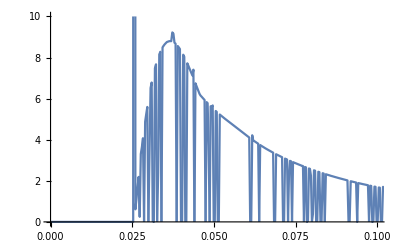

```mathematica
Plot[bottomPTot190UncorrInterp[eps],{eps,0,1},PlotRange-> {{0,0.1},{0,10}}]
```

```mathematica
Interpolation[pTotLTable2[temp,l,energy,cR, cA, mu, aS, lambda, mG, m,corrCoeff,  nF,lowerFactor,upperFactor,widthFactor,widthFactor2,extra]]
```

```mathematica
bottomPTot190Uncorr=pTotInterpMaxL[0.25, 5*5.068,190,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 4.75,0, 2,10,10,0.1,0.5,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26889.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3612.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7442.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3655.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7503.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3698.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1152.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-7564.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1176.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1200.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.125] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-12640.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-19208.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12720.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-19306.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-27144.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-27261.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-19404.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-27378.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-36450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-36585.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-36720.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-47124.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-47278.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-59168.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-47432.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-59340.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-59512.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-72580.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72771.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72962.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-87362.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-87571.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-87780.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-103512.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-103740.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-103968.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-121032.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-139920.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-121278.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-140185.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-140450.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-121524.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-160178.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-160461.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-160745.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-181804.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-204800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-182106.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-205120.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-182408.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-205441.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-229164.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-229503.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-229842.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-254898.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-255255.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-255612.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-282000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-282376.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-282752.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-310472.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-310866.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-340313.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-340725.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-311260.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-341138.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-371522.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-371953.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-372385.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-404101.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-404550.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-438048.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-405000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-438516.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-438985.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-473364.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-473851.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-474338.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-510050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-510555.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-511060.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-548104.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-548628.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-549152.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-587528.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-588070.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-628321.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-588612.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-628881.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-629442.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-670482.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-671061.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-671641.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-714012.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714610.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-758912.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715208.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-759528.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760145.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-805181.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-805815.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-806450.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-852818.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-853471.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-854124.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-901824.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-902496.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-903168.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-952200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-952890.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-953580.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.00394×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.00465×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.00536×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.05706×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.05779×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.05851×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.34325×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.98699×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.0344×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.34855×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.59696×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.41615×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.87259×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-8.63902×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.42656×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.86725×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.26558×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.50676×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.94066×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.03402×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.64025×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.12958×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.74896×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.4473×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.36182×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.85987×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.57137×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.50124×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.69763×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4.64285×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.38381×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.53858×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.51327×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.69555×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-6.6834×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.7502×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.85571×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.0946×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.93568×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.29543×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.12335×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.49845×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

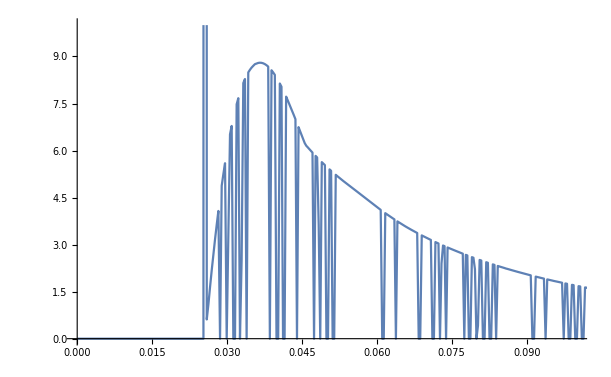

```mathematica
Plot[bottomPTot190Uncorr[eps],{eps,0,1},PlotRange-> {{0,0.1},{0,10}}]
```

```mathematica
bottomPTot200Uncorr=pTotInterpMaxL[0.25, 5*5.068,200,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 4.75,0, 2,10,10,0.1,0.5,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-80000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-28147.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1326.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4278.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8911.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1352.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4324.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8978.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1378.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4371.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9045.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.125] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-15225.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23220.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23328.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15312.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23436.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15400.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-32896.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-33024.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-33153.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-44253.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44402.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44551.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-57291.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57460.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72010.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57630.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72390.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-88410.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-88620.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-88831.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-106491.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-106722.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-106953.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-126253.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-126505.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-126756.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-147696.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-170820.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-147968.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-171113.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-171405.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-148240.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-195313.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-195625.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-195938.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-221445.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-221778.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-222111.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-249218.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-249571.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-249925.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-278631.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-279005.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-279378.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-309685.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-310078.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-310472.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-342378.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-342792.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-343206.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-412686.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-376712.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-413141.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-413595.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-377146.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-377581.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-450301.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-450775.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-451250.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-489555.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-490050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-490545.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-530450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-530965.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-531481.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-572985.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-573520.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-574056.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-617161.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-617716.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-618272.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-662976.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-663552.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-664128.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-710432.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711028.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-759528.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711625.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-760145.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760761.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-810265.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-810901.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-811538.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-862641.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-863298.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-863955.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-916658.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-917335.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-918013.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-972315.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-973013.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-973710.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.02961×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.03033×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.03105×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.08855×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.08929×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.09003×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.14913×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.14989×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.21135×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.15064×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.21212×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.2129×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.2752×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.276×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.2768×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.62011×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.81098×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.69669×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.62773×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.92628×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.329×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.25894×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.04266×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.7219×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.87351×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.11829×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.81872×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.34256×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.45527×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.18715×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.57063×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.3184×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.1615×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.26562×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.45229×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4.31129×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.43394×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.46372×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.60491×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-6.4995×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.68636×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.86314×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.87587×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-8.06853×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.35654×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.27658×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.09797×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.58047×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.12222×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.80706×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.14673×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

```mathematica
bottomPTot190Corr=pTotInterpMaxL[0.25, 5*5.068,190,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 4.75,1, 2,10,10,0.1,0.5,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26889.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3612.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7442.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3655.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7503.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1152.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3698.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7564.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1176.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1200.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.125] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-12640.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12720.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-19208.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-27144.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-19306.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-27261.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-27378.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-19404.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-36450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-36585.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-36720.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-47124.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-47278.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-59168.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-47432.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-59340.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-59512.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-72580.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72771.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72962.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-87362.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-87571.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-87780.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-103512.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-103740.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-103968.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-121032.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-121278.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-139920.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-140185.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-121524.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-140450.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-160178.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-160461.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-160745.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-181804.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-182106.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-204800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-182408.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-205120.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-205441.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-229164.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-229503.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-229842.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-254898.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-255255.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-255612.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-282000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-282376.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-282752.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-310472.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-310866.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-311260.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-340313.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-340725.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-341138.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-371522.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-371953.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-372385.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-404101.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-404550.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-405000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-438048.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-438516.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-438985.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-473364.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-473851.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-474338.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-510050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-510555.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-511060.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-548104.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-548628.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-549152.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-587528.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-588070.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-588612.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-628321.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-628881.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-629442.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-670482.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-671061.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-671641.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-714012.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714610.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715208.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-758912.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-759528.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760145.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-805181.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-805815.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-806450.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-852818.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-853471.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-854124.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-901824.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-902496.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-903168.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-952200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-952890.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-953580.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.00394×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.00465×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.00536×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.05706×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.05779×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.05851×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.34325×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.98699×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.0344×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.34855×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.59696×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.41615×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.87259×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-8.63902×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.42656×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.86725×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.26558×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.50676×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.94066×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.03402×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.64025×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.12958×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.74896×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.4473×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.36182×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.85987×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.57137×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.50124×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.69763×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4.64285×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.38381×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.53858×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.51327×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.69555×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-6.6834×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.7502×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.85571×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.0946×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.93568×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.29543×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.12335×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.49845×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

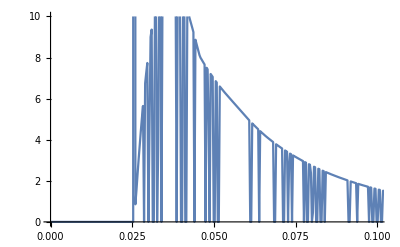

```mathematica
Plot[bottomPTot190Corr[eps],{eps,0,1},PlotRange-> {{0,0.1},{0,10}}]
```

```mathematica
bottomPTot200Corr=pTotInterpMaxL[0.25, 5*5.068,200,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 4.75,1, 2,10,10,0.1,0.5,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-80000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-28147.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1326.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4278.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8911.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1352.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4324.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8978.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1378.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4371.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9045.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-722.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.125] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-23220.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15225.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23328.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15312.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23436.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-15400.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-32896.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-33024.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-33153.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-44253.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44402.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44551.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-57291.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57460.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57630.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-72010.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-72390.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-88410.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-88620.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-88831.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-106491.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-106722.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-106953.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-126253.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-126505.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-126756.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-170820.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-147696.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-171113.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-171405.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-147968.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-148240.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-195313.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-195625.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-195938.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-221445.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-221778.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-222111.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-249218.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-249571.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-249925.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-278631.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-279005.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-279378.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-309685.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-310078.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-310472.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-342378.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-342792.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-343206.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-376712.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-377146.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-377581.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-412686.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-413141.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-413595.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-450301.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-450775.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-451250.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-489555.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-490050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-490545.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-530450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-530965.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-531481.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-572985.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-573520.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-574056.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-617161.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-617716.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-618272.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-662976.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-663552.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-664128.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-710432.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711028.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711625.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-759528.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760145.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760761.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-810265.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-810901.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-811538.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-862641.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-863298.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-863955.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-916658.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-917335.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-918013.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-972315.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-973013.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-973710.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.02961×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.03033×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.03105×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.08855×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.08929×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.09003×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.14913×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.14989×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.15064×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.21135×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.21212×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.2129×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.2752×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.276×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.2768×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.62011×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.81098×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.69669×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.62773×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.92628×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.329×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.25894×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.04266×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.7219×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.87351×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.11829×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.81872×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.34256×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.45527×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.18715×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.57063×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.3184×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.1615×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.26562×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.45229×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4.31129×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.43394×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.46372×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.60491×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-6.4995×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.68636×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.86314×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.87587×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-8.06853×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.35654×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.27658×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.09797×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.58047×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.12222×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.80706×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.14673×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

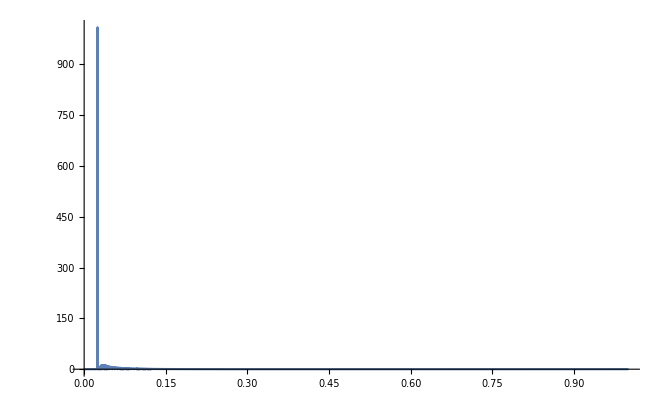

```mathematica
Plot[bottomPTot200Corr[eps],{eps,0,1},PlotRange->All]
```

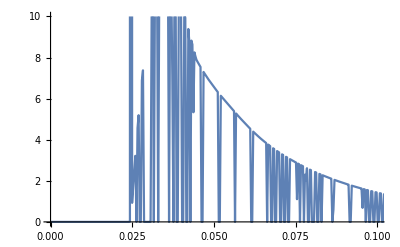

```mathematica
Plot[bottomPTot200Corr[eps],{eps,0,1},PlotRange-> {{0,0.1},{0,10}}]
```

```mathematica
elasticCentreBottom190-10*elasticWidthBottom190
```

0.0249838

```mathematica
elasticCentreBottom190+10*elasticWidthBottom190
```

0.0263343

```mathematica
elasticWidthBottom190= elasticWidth[190,5*5.068, 0.3,0.25, 2,4.75]
elasticCentreBottom190=elasticCentre[190,5*5.068, 0.3,0.25, 2,4.75]
```

0.0000675238

0.025659

```mathematica
charmpTot10Corr=pTotInterpMaxL2[0.25, 5*5.068,10,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,1, 2,10,10,0.1,10,0.1]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: Exp[-771.216] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-734.575] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-967.797] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1186.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-808.748] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1427.84] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1009.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-847.173] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1233.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1052.67] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1478.75] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1280.46] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1530.55] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1691.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1977.05] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1746.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2285.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2036.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2547.59] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1802.93] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2349.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2097.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2615.44] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2414.56] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2684.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

```mathematica
bottom10to180={{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}}}
```

{{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}},{{InterpolatingFunction[…],InterpolatingFunction[…]}}}

```mathematica
bottom10to180[[1]][[1]]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Plot[bottom10to180[[1]][[1]][[1]][eps],{eps,0,1},PlotRange-> All]
```

-Graphics-

```mathematica
bottomPTot10Uncorr=pTotInterpMaxL[0.25, 5*5.068,10,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 4.75,0, 2,10,10,0.1,10,0.1]
```

InterpolatingFunction[…]

```mathematica
Plot[bottomPTot10Uncorr[eps],{eps,0,1},PlotRange-> All]
```

-Graphics-

```mathematica
bottom190UncorrTable=pTotLTable2[0.25, 5*5.068,190,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 4.75,0, 2,10,10,0.1,10,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26745.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7457.84] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-52165.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8734.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24767.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-55460.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-27053.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-872.953] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-58855.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-10112.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1343.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-29440.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1913.97] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-89652.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-132017.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-93955.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-182556.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-137229.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-142542.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-98360.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-188676.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-241269.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-194897.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-248298.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-255427.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-308158.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-316095.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-324132.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-383222.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-466463.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-392067.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-476217.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-486071.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-401013.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-557881.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-568544.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-657478.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-579307.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-669049.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-680721.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-765253.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-777733.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-881208.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-790314.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-894597.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.00534×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.01964×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-908087.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.03404×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.35871×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.04818×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.17572×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.37478×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.61643×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.48537×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.89655×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-8.79308×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.45463×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.94503×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.43302×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.53675×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.98152×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.07733×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.70036×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.17542×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.81226×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.53248×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.47965×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.92648×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.66069×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.6245×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.79126×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4.77176×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.54472×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.70674×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.73264×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.87129×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-6.91283×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.05273×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.09575×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.5289×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-8.25299×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.75834×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.45636×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.99187×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{0.,0.},{0.01,0.},{0.0249838,2.75913×10^-13},{0.0249906,6.40192×10^-13},{0.0249973,1.47051×10^-12},{0.0250041,3.34384×10^-12},{0.0250108,7.52737×10^-12},{0.0250176,1.67749×10^-11},{0.0250243,3.70081×10^-11},{0.0250311,8.08263×10^-11},{0.0250378,1.74755×10^-10},{0.0250446,3.74045×10^-10},{0.0250513,7.92574×10^-10},{0.0250581,1.66255×10^-9},{0.0250648,3.45247×10^-9},{0.0250716,7.09747×10^-9},{0.0250783,1.44443×10^-8},{0.0250851,2.91012×10^-8},{0.0250918,5.80423×10^-8},{0.0250986,1.14604×10^-7},{0.0251053,2.24012×10^-7},{0.0251121,4.33474×10^-7},{0.0251189,8.30377×10^-7},{0.0251256,1.57473×10^-6},{0.0251324,2.95637×10^-6},{0.0251391,5.49452×10^-6},{0.0251459,0.0000101093},{0.0251526,0.0000184133},{0.0251594,0.0000332018},{0.0251661,0.0000592667},{0.0251729,0.000104732},{0.0251796,0.000183219},{0.0251864,0.000317306},{0.0251931,0.00054401},{0.0251999,0.000923327},{0.0252066,0.0015514},{0.0252134,0.00258054},{0.0252201,0.00424931},{0.0252269,0.006927},{0.0252336,0.0111787},{0.0252404,0.017859},{0.0252471,0.0282452},{0.0252539,0.0442231},{0.0252607,0.0685449},{0.0252674,0.105177},{0.0252742,0.159766},{0.0252809,0.240253},{0.0252877,0.357662},{0.0252944,0.527104},{0.0253012,0.769026},{0.0253079,1.11072},{0.0253147,1.58813},{0.0253214,2.24796},{0.0253282,3.15},{0.0253349,4.36971},{0.0253417,6.00087},{0.0253484,8.15821},{0.0253552,10.9798},{0.0253619,14.6291},{0.0253687,19.2955},{0.0253754,25.1951},{0.0253822,32.5683},{0.0253889,41.6768},{0.0253957,52.7975},{0.0254025,66.2143},{0.0254092,82.2072},{0.025416,101.039},{0.0254227,122.938},{0.0254295,148.082},{0.0254362,176.579},{0.025443,208.447},{0.0254497,243.597},{0.0254565,281.818},{0.0254632,322.763},{0.02547,365.948},{0.0254767,410.747},{0.0254835,456.404},{0.0254902,502.047},{0.025497,546.713},{0.0255037,589.377},{0.0255105,628.996},{0.0255172,664.541},{0.025524,695.049},{0.0255307,719.663},{0.0255375,737.672},{0.0255443,748.543},{0.025551,751.953},{0.0255578,747.8},{0.0255645,736.207},{0.0255713,717.521},{0.025578,692.294},{0.0255848,661.253},{0.0255915,625.267},{0.0255983,585.309},{0.025605,542.409},{0.0256118,497.612},{0.0256185,451.938},{0.0256253,406.342},{0.025632,361.685},{0.0256388,318.711},{0.0256455,278.031},{0.0256523,240.117},{0.025659,205.301},{0.0256658,173.781},{0.0256725,145.635},{0.0256793,120.834},{0.0256861,99.2636},{0.0256928,80.7399},{0.0256996,65.0296},{0.0257063,51.868},{0.0257131,40.9739},{0.0257198,32.0639},{0.0257266,24.862},{0.0257333,19.1087},{0.0257401,14.5657},{0.0257468,11.0197},{0.0257536,8.28373},{0.0257603,6.19709},{0.0257671,4.62412},{0.0257738,3.45228},{0.0257806,2.58975},{0.0257873,1.96276},{0.0257941,1.51295},{0.0258008,1.1948},{0.0258076,0.973318},{0.0258143,0.82197},{0.0258211,0.720912},{0.0258279,0.655494},{0.0258346,0.615043},{0.0258414,0.59188},{0.0258481,0.580553},{0.0258549,0.577234},{0.0258616,0.579274},{0.0258684,0.584856},{0.0258751,0.592755},{0.0258819,0.602149},{0.0258886,0.612496},{0.0258954,0.623444},{0.0259021,0.634764},{0.0259089,0.64631},{0.0259156,0.657991},{0.0259224,0.66975},{0.0259291,0.68155},{0.0259359,0.693372},{0.0259426,0.705201},{0.0259494,0.71703},{0.0259561,0.728855},{0.0259629,0.740673},{0.0259697,0.752482},{0.0259764,0.764282},{0.0259832,0.776072},{0.0259899,0.787852},{0.0259967,0.799621},{0.0260034,0.81138},{0.0260102,0.823129},{0.0260169,0.834867},{0.0260237,0.846594},{0.0260304,0.858311},{0.0260372,0.870018},{0.0260439,0.881714},{0.0260507,0.8934},{0.0260574,0.905075},{0.0260642,0.916739},{0.0260709,0.928393},{0.0260777,0.940037},{0.0260844,0.95167},{0.0260912,0.963293},{0.0260979,0.974905},{0.0261047,0.986507},{0.0261115,0.998098},{0.0261182,1.00968},{0.026125,1.02125},{0.0261317,1.03281},{0.0261385,1.04436},{0.0261452,1.0559},{0.026152,1.06743},{0.0261587,1.07895},{0.0261655,1.09045},{0.0261722,1.10195},{0.026179,1.11344},{0.0261857,1.12491},{0.0261925,1.13638},{0.0261992,1.14784},{0.026206,1.15928},{0.0262127,1.17072},{0.0262195,1.18214},{0.0262262,1.19356},{0.026233,1.20496},{0.0262397,1.21635},{0.0262465,1.22774},{0.0262533,1.23911},{0.02626,1.25047},{0.0262668,1.26182},{0.0262735,1.27316},{0.0262803,1.2845},{0.026287,1.29582},{0.0262938,1.30713},{0.0263005,1.31843},{0.0263073,1.32972},{0.026314,1.341},{0.0263208,1.35227},{0.0263275,1.36352},{0.0263343,1.37477},{0.0270095,2.44812},{0.0276848,3.42201},{0.02836,2.128×10^-11},{0.0290352,5.08667},{0.0297105,4.68962×10^-14},{0.0303857,6.39919},{0.0310609,1.70451×10^-11},{0.0317362,7.38998},{0.0324114,3.1959×10^-9},{0.0330867,8.08948},{0.0337619,6.84183×10^-12},{0.0344371,8.5281},{0.0351124,8.6591},{0.0357876,8.7346},{0.0364628,8.76347},{0.0371381,8.74445},{0.0378133,8.68305},{0.0384886,5.20493×10^-18},{0.0391638,8.44822},{0.039839,1.59876×10^-21},{0.0405143,8.08945},{0.0411895,1.68501×10^-18},{0.0418648,7.63715},{0.04254,1.00366×10^-15},{0.0432152,7.12176},{0.0438905,4.40044×10^-8},{0.0445657,6.57368},{0.0452409,6.29689},{0.0459162,6.10331},{0.0465914,5.98234},{0.0472667,1.36074×10^-10},{0.0479419,5.754},{0.0486171,7.67142×10^-13},{0.0492924,5.54215},{0.0499676,2.10363×10^-15},{0.0506428,5.34485},{0.0513181,3.24724×10^-18},{0.0519933,5.16016},{0.0526686,5.03063×10^-15},{0.0533438,4.98612},{0.054019,4.90249},{0.0546943,4.8208},{0.0553695,4.7274},{0.0560447,4.65518},{0.05672,4.56836},{0.0573952,1.58024×10^-9},{0.0580705,4.399},{0.0587457,3.87798×10^-7},{0.0594209,4.23551},{0.0600962,4.11994×10^-9},{0.0607714,4.07736},{0.0614467,2.46123×10^-11},{0.0621219,3.9268},{0.0627971,7.66871×10^-9},{0.0634724,3.78193},{0.0641476,3.71195},{0.0648228,3.64362},{0.0654981,3.57702},{0.0661733,3.51444},{0.0668486,3.45376},{0.0675238,3.39469},{0.068199,3.33718},{0.0688743,3.28119},{0.0695495,7.0894×10^-7},{0.0702247,3.17354},{0.0709,3.12179},{0.0715752,3.07137},{0.0722505,3.0222},{0.0729257,2.97425},{0.0736009,2.92747},{0.0742762,2.88181},{0.0749514,2.83724},{0.0756266,2.79353},{0.0763019,2.7499},{0.0769771,2.70722},{0.0776524,2.66548},{0.0783276,5.00537×10^-10},{0.0790028,2.5847},{0.0796781,1.12435×10^-12},{0.0803533,2.5074},{0.0810285,2.24484×10^-10},{0.0817038,2.43343},{0.082379,2.52116×10^-8},{0.0830543,2.3626},{0.0837295,7.19743×10^-11},{0.0844047,2.29475},{0.08508,2.2619},{0.0857552,2.2274},{0.0864305,2.19791},{0.0871057,2.16682},{0.0877809,2.13636},{0.0884562,1.03317×10^-16},{0.0891314,2.0773},{0.0898066,4.69439×10^-20},{0.0904819,2.02061},{0.0911571,3.6471×10^-17},{0.0918324,1.96618},{0.0925076,1.59376×10^-14},{0.0931828,1.9139},{0.0938581,5.00538×10^-10},{0.0945333,1.86366},{0.0952085,1.83925},{0.0958838,1.81522},{0.096559,1.79155},{0.0972343,1.18944×10^-9},{0.0979095,1.74553},{0.0985847,4.51421×10^-15},{0.09926,1.70121},{0.0999352,8.89634×10^-18},{0.10061,1.65852},{0.101286,9.86122×10^-21},{0.101961,1.6174},{0.102636,2.30758×10^-17},{0.103311,1.57777},{0.103987,1.55849},{0.104662,1.53939},{0.105337,1.51997},{0.106012,1.50261},{0.106688,1.48455},{0.107363,1.6739×10^-11},{0.108038,1.44937},{0.108713,6.232×10^-9},{0.109389,1.4154},{0.110064,4.77541×10^-11},{0.110739,1.38259},{0.111414,2.05806×10^-13},{0.112089,1.3509},{0.112765,9.73387×10^-11},{0.11344,1.32027},{0.114115,1.30534},{0.11479,1.29066},{0.115466,1.27622},{0.116141,1.26195},{0.116816,1.24791},{0.117491,1.2341},{0.118167,1.2205},{0.118842,1.20713},{0.119517,1.19398},{0.120192,1.18103},{0.120868,1.16829},{0.121543,1.12354×10^-7},{0.122218,1.14342},{0.122893,1.13128},{0.123569,1.11933},{0.124244,1.10756},{0.124919,1.09598},{0.125594,1.08457},{0.126269,1.07329},{0.136334,0.923827},{0.146334,0.803651},{0.156334,0.705008},{0.166334,0.623243},{0.176334,0.554713},{0.186334,0.496731},{0.196334,0.44728},{0.206334,0.40478},{0.216334,0.367979},{0.226334,0.335914},{0.236334,0.307824},{0.246334,0.283048},{0.256334,0.261107},{0.266334,0.241579},{0.276334,0.224123},{0.286334,0.208461},{0.296334,0.19435},{0.306334,0.181589},{0.316334,0.170008},{0.326334,0.159479},{0.336334,0.149887},{0.346334,0.141123},{0.356334,0.133087},{0.366334,0.125681},{0.376334,0.118814},{0.386334,0.112472},{0.396334,0.106601},{0.406334,0.101162},{0.416334,0.0961172},{0.426334,0.0914297},{0.436334,0.0870526},{0.446334,0.0829652},{0.456334,0.0791442},{0.466334,0.0755693},{0.476334,0.0722204},{0.486334,0.0690715},{0.496334,0.0661104},{0.506334,0.0633235},{0.516334,0.0606986},{0.526334,0.0582239},{0.536334,0.0558841},{0.546334,0.0536716},{0.556334,0.051578},{0.566334,0.0495957},{0.576334,0.0477172},{0.586334,0.0459335},{0.596334,0.0442393},{0.606334,0.0426292},{0.616334,0.0410982},{0.626334,0.0396413},{0.636334,0.0382524},{0.646334,0.0369282},{0.656334,0.0356648},{0.666334,0.034459},{0.676334,0.0333073},{0.686334,0.032206},{0.696334,0.0311524},{0.706334,0.0301441},{0.716334,0.0291785},{0.726334,0.0282533},{0.736334,0.0273656},{0.746334,0.0265137},{0.756334,0.0256956},{0.766334,0.0249095},{0.776334,0.0241537},{0.786334,0.0234264},{0.796334,0.0227261},{0.806334,0.022051},{0.816334,0.0213998},{0.826334,0.0207708},{0.836334,0.0201635},{0.846334,0.0195757},{0.856334,0.0190054},{0.866334,0.0184507},{0.876334,0.0179101},{0.886334,0.0173891},{0.896334,0.0168798},{0.906334,0.0163756},{0.916334,0.0158691},{0.926334,9.30884×10^-7},{0.936334,8.99645×10^-7},{0.946334,8.67105×10^-7},{0.956334,8.32214×10^-7},{0.966334,7.93762×10^-7},{0.976334,7.50495×10^-7},{0.986334,7.01107×10^-7},{0.996334,6.44246×10^-7}}

```mathematica
0.0283599924942019 to 0.12221806289167962
```

```mathematica
bottom190UncorrInterp=Interpolation[bottom190UncorrTable]
```

InterpolatingFunction[…]

```mathematica
Plot[bottom190UncorrInterp[eps],{eps,0,1},PlotRange-> {{0,0.2},{0,30}}]
```

-Graphics-

```mathematica
bottomPTot190Uncorr=pTotInterpMaxL[0.25, 5*5.068,190,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 4.75,0, 2,10,10,0.1,10,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26889.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-51200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-54450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-28800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-88200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-130050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-92450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-180000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-135200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-238050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-140450.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-96800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-245000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-186050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-192200.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-252050.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-304200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-378450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-312050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-460800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-320000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-470450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-387200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-480200.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-551250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-396050.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-561800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-572450.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-649800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-756450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-661250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-672800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-871200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-768800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-781250.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-884450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-994050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.0082×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-897800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.02245×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.34325×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.98699×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.0344×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.34855×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.59696×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.41615×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.63902×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.87259×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.42656×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.86725×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.26558×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.50676×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.94066×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.03402×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.64025×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.12958×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.74896×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.4473×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.36182×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.85987×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.57137×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.50124×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.69763×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4.64285×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.38381×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.53858×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.51327×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.69555×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-6.6834×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.7502×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.0946×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.85571×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-7.93568×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.29543×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.12335×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.49845×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

```mathematica
bottomPTot190Uncorr=InterpolatingFunction[…]
```

InterpolatingFunction[…]

```mathematica
1*elasticWidthBottom190
```

0.0000675238

```mathematica
Plot[bottomPTot190Uncorr[eps],{eps,0,1},PlotRange-> {{elasticCentreBottom190-10*elasticWidthBottom190,elasticCentreBottom190+10*elasticWidthBottom190+0.2},All}]
```

-Graphics-

```mathematica
bottomPTot200Uncorr=pTotInterpMaxL2[0.25, 5*5.068,200,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 4.75,0, 2,10,10,0.1,10,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-80000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-28147.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-28800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-31250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-61250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-33800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-64800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-11250.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-96800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-145800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-273800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-101250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-105800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-204800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-151250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-156800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-281250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-211250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-288800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-217800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-352800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-361250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-369800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-441800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-540800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-451250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-551250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-649800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-460800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-561800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-661250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-672800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-768800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-781250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-793800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-897800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-911250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.0368×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.1858×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.05125×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-924800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.20125×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.2168×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.0658×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.62011×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.81098×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.69669×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.62773×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.92628×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.329×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.04266×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.25894×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.7219×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.87351×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.11829×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.81872×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.34256×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.45527×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.18715×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.57063×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.3184×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.1615×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.26562×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.45229×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4.31129×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.43394×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.46372×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.60491×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-6.4995×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.68636×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.86314×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.87587×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-8.06853×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.35654×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.09797×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.27658×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.58047×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.12222×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.80706×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.14673×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

```mathematica
bottomPTot190Corr=pTotInterpMaxL2[0.25, 5*5.068,190,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 4.75,1, 2,10,10,0.1,10,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26889.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-51200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-54450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-28800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-88200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-130050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-92450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-180000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-135200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-238050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-140450.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-96800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-245000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-186050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-192200.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-252050.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-304200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-378450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-312050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-460800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-320000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-470450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-387200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-480200.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-551250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-396050.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-561800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-572450.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-649800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-756450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-661250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-672800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-871200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-768800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-781250.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-884450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-994050.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.0082×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-897800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.02245×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.34325×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.98699×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.0344×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.34855×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.59696×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.41615×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.63902×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.87259×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.42656×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.86725×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.26558×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.50676×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.94066×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.03402×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.64025×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.12958×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.74896×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.4473×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.36182×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.85987×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.57137×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.50124×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.69763×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4.64285×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.38381×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.53858×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.51327×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.69555×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-6.6834×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.7502×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.0946×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.85571×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-7.93568×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.29543×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.12335×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.49845×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

```mathematica
Plot[bottomPTot190Corr[eps],{eps,0,1}]
```

-Graphics-

```mathematica
bottomPTot200Corr=pTotInterpMaxL2[0.25, 5*5.068,200,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 4.75,1, 2,10,10,0.1,10,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: Exp[-80000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-28147.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-28800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8450.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-31250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-61250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-33800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-64800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-11250.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-96800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-145800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-273800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-101250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-105800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-204800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-151250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-156800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-281250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-211250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-288800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-217800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-352800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-361250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-369800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-441800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-540800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-451250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-551250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-460800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-649800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-561800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-661250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-672800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-768800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-781250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-793800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-897800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-911250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.0368×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.1858×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.05125×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-924800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.20125×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.2168×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.0658×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.62011×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.81098×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.69669×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.62773×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.92628×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.329×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.25894×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.04266×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.7219×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.87351×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.11829×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.81872×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.34256×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.45527×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.18715×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.57063×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-3.3184×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.1615×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.26562×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.45229×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-4.31129×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.43394×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.46372×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5.60491×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-6.4995×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.68636×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.86314×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.87587×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-8.06853×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.35654×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.09797×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.27658×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.58047×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.12222×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.80706×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.14673×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

```mathematica
bottomPTot200Corr=InterpolatingFunction[…]
```

InterpolatingFunction[…]

```mathematica
Plot[bottomPTot200Corr[eps],{eps,0,1},PlotRange->{{0,1},All}]
```

-Graphics-

```mathematica
CharmpTot10Uncorr=pTotInterpMaxL2[0.25, 5*5.068,10,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2], 1.5,0, 2,10,10,0.1,10,0.1]
```

InterpolatingFunction[…]

```mathematica
Plot[InterpolatingFunction[…][eps],{eps,0,1},PlotRange->All]
```

-Graphics-

```mathematica
[cR, cA, mu, aS, l, lambda, mG, m, t, nF] = [4/3, 3, 0.5, 0.3, 5*5.068, 1* 5.068, 0.5/Sqrt[2], 1.5, 0.25, 2]
```

```mathematica
ClearAll[rAAPTotIn]
```

```mathematica
rAAPTotIn[pTot_]:=rAA[pTot]=NIntegrate [FullSimplify[pTot[eps]*HeavisideTheta[1-eps]*(1-eps)^5],{eps,0,1},Method->"InterpolationPointsSubdivision"]
```

```mathematica
rAAPTotIn[bottomPTot190Uncorr]
```

0.331179

```mathematica
rAAPTotIn[charmpTot10Corr]
```

0.151549

```mathematica
rAAPTotIn[CharmpTot10Uncorr]
```

0.145269

### Plotting simple RAA (without geometry considerations)

```mathematica
RAACharm100to200={{0.14518258067003995,0.15145410610092008},{0.19959666559787928,0.21539357255106764},{0.2714179185476188,0.29944608721543203},{0.33031300989421114,0.3699076592391802},{0.3804050300041503,0.4308236079809814},{0.421991188215814,0.48349738702998313},{0.458720897942571,0.5300310079296989},{0.4908924932011291,0.5714645076320753},{0.5192593821585626,0.6086460954836094},{0.5446529297375932,0.6431316762590547},{0.5678185335874927,0.672965336693885},{0.5891720653542044,0.7010450066054474},{0.6069983522274894,0.7262929623436643},{0.6244701330021813,0.7496609350563326},{0.639704766723738,0.7740745965650234},{0.6542784654157883,0.7922031044398025},{0.6663320496330731,0.8095542397757585},{0.6771542462437845,0.8252876366496558},{0.6876259080954091,0.840460859326366},{0.6967768012399183,0.8542765440531201}}
```

{{0.145183,0.151454},{0.199597,0.215394},{0.271418,0.299446},{0.330313,0.369908},{0.380405,0.430824},{0.421991,0.483497},{0.458721,0.530031},{0.490892,0.571465},{0.519259,0.608646},{0.544653,0.643132},{0.567819,0.672965},{0.589172,0.701045},{0.606998,0.726293},{0.62447,0.749661},{0.639705,0.774075},{0.654278,0.792203},{0.666332,0.809554},{0.677154,0.825288},{0.687626,0.840461},{0.696777,0.854277}}

```mathematica
ListPlot[{CharmDGLV,BottomDGLV,CharmCorrection,BottomCorrection}, PlotLegends->Placed[{"Charm: uncorrected","Bottom: uncorrected", "Charm: short path correction","Bottom: short path correction" },{0.3,0.75}],AxesLabel->{"L(fm)", "dE/E"},Joined->True]
```

```mathematica
ListPlot[{Table[{i*10,RAACharm100to200[[i]][[1]]},{i,1,Length[RAACharm100to200]}],Table[{i*10,RAACharm100to200[[i]][[2]]},{i,1,Length[RAACharm100to200]}]},PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{"Uncorrected","Corrected (short path length)" },LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.7,0.3}],FrameLabel->{{"R_AA",""},{"E(GeV)","Charm"}},PlotRange->{All,{0,1}},Frame->True]
```

-Graphics-

```mathematica
lowEnergiesRAABottom={{0.6165887565658682,0.6333751118395864},{0.4817742718086609,0.5123411780538251},{0.4682564879438462,0.5102198069342577},{0.4753524210933019,0.5151195132482206},{0.49058670488699735,0.5515913624560081},{0.50739603892803,0.5764394161368525},{0.5245229863306898,0.6022121803695946},{0.541740386668781,0.6277529756716435},{0.559121173125828,0.6520396811025287},{0.5745373303785655,0.6756944244190931},{0.589339336025555,0.6988601784748915},{0.611338836672011,0.7169169769224155},{0.6176391501047385,0.7365026885143854},{0.6306473720317454,0.7553171157686317},{0.6424052776635926,0.7722612876986915},{0.6530019501623187,0.7892680752769434},{0.663182148621274,0.8036981504019812},{0.6729373893074679,0.8357723063728826}}
```

{{0.616589,0.633375},{0.481774,0.512341},{0.468256,0.51022},{0.475352,0.51512},{0.490587,0.551591},{0.507396,0.576439},{0.524523,0.602212},{0.54174,0.627753},{0.559121,0.65204},{0.574537,0.675694},{0.589339,0.69886},{0.611339,0.716917},{0.617639,0.736503},{0.630647,0.755317},{0.642405,0.772261},{0.653002,0.789268},{0.663182,0.803698},{0.672937,0.835772}}

```mathematica
ListPlot[{Table[{i*10,lowEnergiesRAABottom[[i]][[1]]},{i,1,Length[lowEnergiesRAABottom]}],Table[{i*10,lowEnergiesRAABottom[[i]][[2]]},{i,1,Length[lowEnergiesRAABottom]}]},PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{"Uncorrected","Corrected (short path length)" },LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.75,0.3}],FrameLabel->{{"R_AA",""},{"E(GeV)","Bottom"}},PlotRange->{All,{0,1}},Frame->True]
```

-Graphics-

```mathematica
ClearAll[pTotLTable]
```

```mathematica
AbsoluteTiming[pTotTableBottom190Uncorr=pTotLTable[1,4,3,6,0.25, 5*5.068,190,4/3, 3, 0.5, 0.3, 1* 5.068, 0.5/Sqrt[2],4.75,0, 2,10,10,0.1,10,0.1]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: Exp[-72200.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26745.4] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.0209294 and 0.0000539721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.00135705 and 8.3679×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.0245521 and 0.000069964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.00175469 and 0.0000109056 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.0286125 and 0.0000839876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.0022505 and 0.0000134525 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.104665 and 0.000220781 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.0000653884 and 1.08389×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.114241 and 0.000254706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.0000920624 and 1.12586×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.124169 and 0.000271669 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.000128484 and 1.07407×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.248294 and 0.000447706 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.405665 and 0.000420921 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.260296 and 0.000437624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000310013}. NIntegrate obtained 0.272342 and 0.000391439 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000622513}. NIntegrate obtained 0.693316 and 0.000716692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000622513}. NIntegrate obtained 0.70517 and 0.000725935 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000622513}. NIntegrate obtained 0.799621 and 0.000991757 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000622513}. NIntegrate obtained 0.834867 and 0.0011247 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000622513}. NIntegrate obtained 0.846594 and 0.000960449 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000935013}. NIntegrate obtained 1.341 and 0.00148113 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000935013}. NIntegrate obtained 1.35227 and 0.00175585 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.000935013}. NIntegrate obtained 1.36352 and 0.00186336 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.00156001}. NIntegrate obtained 2.44812 and 0.00300631 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.0218725}. NIntegrate obtained 5.86599 and 0.00773761 for the integral and error estimates.

General::munfl: Exp[-7457.84] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24767.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-52165.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8734.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-872.953] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-55460.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-27053.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-10112.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1343.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-58855.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1913.97] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-29440.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.00499751}. NIntegrate obtained 6.39919 and 0.00812872 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.01781}. NIntegrate obtained 7.12176 and 0.00904558 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.0124975}. NIntegrate obtained 8.68305 and 0.00897713 for the integral and error estimates.

General::munfl: Exp[-89652.2] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.034685}. NIntegrate obtained 4.15601 and 0.00471752 for the integral and error estimates.

General::munfl: Exp[-132017.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-93955.9] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.03531}. NIntegrate obtained 4.07736 and 0.00487381 for the integral and error estimates.

General::munfl: Exp[-137229.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-182556.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-142542.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-98360.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-241269.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-188676.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-248298.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-194897.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-255427.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.04281}. NIntegrate obtained 3.33718 and 0.00398941 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.0387475}. NIntegrate obtained 3.71195 and 0.00479295 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-308158.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-383222.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-316095.] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.0462475}. NIntegrate obtained 3.07137 and 0.00358765 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.059685}. NIntegrate obtained 2.2619 and 0.00294681 for the integral and error estimates.

General::munfl: Exp[-392067.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-324132.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-466463.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-401013.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-557881.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-476217.] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.0556225}. NIntegrate obtained 2.47001 and 0.00288203 for the integral and error estimates.

General::munfl: Exp[-568544.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-486071.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-579307.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.0637475}. NIntegrate obtained 2.0773 and 0.00241652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.06906}. NIntegrate obtained 1.86366 and 0.00200037 for the integral and error estimates.

General::munfl: Exp[-657478.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-765253.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-669049.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-777733.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-680721.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-790314.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-881208.] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.07656}. NIntegrate obtained 1.6174 and 0.00212607 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.0799975}. NIntegrate obtained 1.52061 and 0.0018905 for the integral and error estimates.

General::munfl: Exp[-894597.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.00534×10^6] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.0806225}. NIntegrate obtained 1.50261 and 0.00192843 for the integral and error estimates.

General::munfl: Exp[-908087.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.01964×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.03404×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.0974975}. NIntegrate obtained 1.13128 and 0.00149403 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.093435}. NIntegrate obtained 1.20713 and 0.00149403 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.09406}. NIntegrate obtained 1.19398 and 0.00145994 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.110935}. NIntegrate obtained 0.923827 and 0.00121989 for the integral and error estimates.

General::munfl: Exp[-1.35871×10^6] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.190935}. NIntegrate obtained 0.367979 and 0.000485896 for the integral and error estimates.

General::munfl: Exp[-4.04818×10^6] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.270935}. NIntegrate obtained 0.19435 and 0.000256625 for the integral and error estimates.

General::munfl: Exp[-8.17572×10^6] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.120935}. NIntegrate obtained 0.803651 and 0.0010612 for the integral and error estimates.

General::munfl: Exp[-1.61643×10^6] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.350935}. NIntegrate obtained 0.118814 and 0.000156884 for the integral and error estimates.

General::munfl: Exp[-1.37478×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.200935}. NIntegrate obtained 0.335914 and 0.000443554 for the integral and error estimates.

General::munfl: Exp[-4.48537×10^6] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.130935}. NIntegrate obtained 0.705008 and 0.00093094 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-1.89655×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.280935}. NIntegrate obtained 0.181589 and 0.000239774 for the integral and error estimates.

General::munfl: Exp[-8.79308×10^6] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.210935}. NIntegrate obtained 0.307824 and 0.000406462 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-4.94503×10^6] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.360935}. NIntegrate obtained 0.112472 and 0.00014851 for the integral and error estimates.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.45463×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.290935}. NIntegrate obtained 0.170008 and 0.000224482 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-9.43302×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.370935}. NIntegrate obtained 0.106601 and 0.000140758 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-1.53675×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.420935}. NIntegrate obtained 0.0829652 and 0.000109548 for the integral and error estimates.

General::munfl: Exp[-1.98152×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.430935}. NIntegrate obtained 0.0791442 and 0.000104503 for the integral and error estimates.

General::munfl: Exp[-2.07733×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.490935}. NIntegrate obtained 0.0606986 and 0.0000801468 for the integral and error estimates.

General::munfl: Exp[-2.70036×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.440935}. NIntegrate obtained 0.0755693 and 0.0000997823 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-2.17542×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.500935}. NIntegrate obtained 0.0582239 and 0.0000768791 for the integral and error estimates.

General::munfl: Exp[-2.81226×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.560935}. NIntegrate obtained 0.0459335 and 0.0000606506 for the integral and error estimates.

General::munfl: Exp[-3.53248×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.630935}. NIntegrate obtained 0.0356648 and 0.0000470918 for the integral and error estimates.

General::munfl: Exp[-4.47965×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.510935}. NIntegrate obtained 0.0558841 and 0.0000737896 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-2.92648×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.570935}. NIntegrate obtained 0.0442393 and 0.0000584136 for the integral and error estimates.

General::munfl: Exp[-3.66069×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.640935}. NIntegrate obtained 0.034459 and 0.0000454996 for the integral and error estimates.

General::munfl: Exp[-4.6245×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.580935}. NIntegrate obtained 0.0426292 and 0.0000562876 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-3.79126×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.650935}. NIntegrate obtained 0.0333073 and 0.0000439789 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-4.77176×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.700935}. NIntegrate obtained 0.0282533 and 0.0000373056 for the integral and error estimates.

General::munfl: Exp[-5.54472×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.710935}. NIntegrate obtained 0.0273656 and 0.0000361335 for the integral and error estimates.

General::munfl: Exp[-5.70674×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.770935}. NIntegrate obtained 0.0227261 and 0.0000300074 for the integral and error estimates.

General::munfl: Exp[-6.73264×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.720935}. NIntegrate obtained 0.0265137 and 0.0000350086 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-5.87129×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.780935}. NIntegrate obtained 0.022051 and 0.0000291161 for the integral and error estimates.

General::munfl: Exp[-6.91283×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.840935}. NIntegrate obtained 0.0184507 and 0.0000243622 for the integral and error estimates.

General::munfl: Exp[-8.05273×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.790935}. NIntegrate obtained 0.0213998 and 0.0000282562 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-7.09575×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.910935}. NIntegrate obtained 0.0148376 and 0.0000195916 for the integral and error estimates.

General::munfl: Exp[-9.5289×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.850935}. NIntegrate obtained 0.0179101 and 0.0000236484 for the integral and error estimates.

General::munfl: Exp[-8.25299×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.920935}. NIntegrate obtained 0.0142994 and 0.0000188809 for the integral and error estimates.

General::munfl: Exp[-9.75834×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.860935}. NIntegrate obtained 0.0173891 and 0.0000229605 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-8.45636×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 4 recursive bisections in x near {x} = {0.930935}. NIntegrate obtained 0.0137217 and 0.0000181183 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-9.99187×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{313.154,{{0.,0.},{0.01,0.},{0.0249838,2.75913×10^-13},{0.0249906,6.40192×10^-13},{0.0249973,1.47051×10^-12},{0.0250041,3.34384×10^-12},{0.0250108,7.52737×10^-12},{0.0250176,1.67749×10^-11},{0.0250243,3.70081×10^-11},{0.0250311,8.08264×10^-11},{0.0250378,1.74755×10^-10},{0.0250446,3.74046×10^-10},{0.0250513,7.92574×10^-10},{0.0250581,1.66255×10^-9},{0.0250648,3.45247×10^-9},{0.0250716,7.09748×10^-9},{0.0250783,1.44444×10^-8},{0.0250851,2.91013×10^-8},{0.0250918,5.80424×10^-8},{0.0250986,1.14604×10^-7},{0.0251053,2.24012×10^-7},{0.0251121,4.33475×10^-7},{0.0251189,8.30378×10^-7},{0.0251256,1.57474×10^-6},{0.0251324,2.95637×10^-6},{0.0251391,5.49453×10^-6},{0.0251459,0.0000101093},{0.0251526,0.0000184133},{0.0251594,0.0000332018},{0.0251661,0.0000592668},{0.0251729,0.000104732},{0.0251796,0.000183219},{0.0251864,0.000317307},{0.0251931,0.000544012},{0.0251999,0.000923329},{0.0252066,0.0015514},{0.0252134,0.00258055},{0.0252201,0.00424932},{0.0252269,0.00692702},{0.0252336,0.0111787},{0.0252404,0.0178591},{0.0252471,0.0282452},{0.0252539,0.0442233},{0.0252607,0.0685451},{0.0252674,0.105177},{0.0252742,0.159767},{0.0252809,0.240254},{0.0252877,0.357663},{0.0252944,0.527105},{0.0253012,0.769026},{0.0253079,1.11072},{0.0253147,1.58813},{0.0253214,2.24796},{0.0253282,3.15},{0.0253349,4.36971},{0.0253417,6.00087},{0.0253484,8.15821},{0.0253552,10.9798},{0.0253619,14.6291},{0.0253687,19.2955},{0.0253754,25.1951},{0.0253822,32.5683},{0.0253889,41.6768},{0.0253957,52.7975},{0.0254025,66.2143},{0.0254092,82.2072},{0.025416,101.039},{0.0254227,122.938},{0.0254295,148.082},{0.0254362,176.579},{0.025443,208.447},{0.0254497,243.597},{0.0254565,281.818},{0.0254632,322.763},{0.02547,365.948},{0.0254767,410.747},{0.0254835,456.404},{0.0254902,502.047},{0.025497,546.713},{0.0255037,589.377},{0.0255105,628.996},{0.0255172,664.541},{0.025524,695.049},{0.0255307,719.663},{0.0255375,737.672},{0.0255443,748.543},{0.025551,751.953},{0.0255578,747.8},{0.0255645,736.207},{0.0255713,717.521},{0.025578,692.294},{0.0255848,661.253},{0.0255915,625.267},{0.0255983,585.309},{0.025605,542.409},{0.0256118,497.612},{0.0256185,451.938},{0.0256253,406.342},{0.025632,361.685},{0.0256388,318.711},{0.0256455,278.031},{0.0256523,240.117},{0.025659,205.301},{0.0256658,173.781},{0.0256725,145.635},{0.0256793,120.834},{0.0256861,99.2636},{0.0256928,80.7399},{0.0256996,65.0296},{0.0257063,51.868},{0.0257131,40.9739},{0.0257198,32.0639},{0.0257266,24.862},{0.0257333,19.1087},{0.0257401,14.5657},{0.0257468,11.0197},{0.0257536,8.28373},{0.0257603,6.19709},{0.0257671,4.62412},{0.0257738,3.45228},{0.0257806,2.58975},{0.0257873,1.96276},{0.0257941,1.51295},{0.0258008,1.1948},{0.0258076,0.973318},{0.0258143,0.82197},{0.0258211,0.720912},{0.0258279,0.655494},{0.0258346,0.615043},{0.0258414,0.59188},{0.0258481,0.580553},{0.0258549,0.577234},{0.0258616,0.579274},{0.0258684,0.584856},{0.0258751,0.592755},{0.0258819,0.602149},{0.0258886,0.612496},{0.0258954,0.623444},{0.0259021,0.634764},{0.0259089,0.64631},{0.0259156,0.657991},{0.0259224,0.66975},{0.0259291,0.68155},{0.0259359,0.693372},{0.0259426,0.705201},{0.0259494,0.71703},{0.0259561,0.728855},{0.0259629,0.740673},{0.0259697,0.752482},{0.0259764,0.764282},{0.0259832,0.776072},{0.0259899,0.787852},{0.0259967,0.799621},{0.0260034,0.81138},{0.0260102,0.823129},{0.0260169,0.834867},{0.0260237,0.846594},{0.0260304,0.858311},{0.0260372,0.870018},{0.0260439,0.881714},{0.0260507,0.893399},{0.0260574,0.905075},{0.0260642,0.916739},{0.0260709,0.928393},{0.0260777,0.940037},{0.0260844,0.95167},{0.0260912,0.963293},{0.0260979,0.974905},{0.0261047,0.986507},{0.0261115,0.998098},{0.0261182,1.00968},{0.026125,1.02125},{0.0261317,1.03281},{0.0261385,1.04436},{0.0261452,1.0559},{0.026152,1.06743},{0.0261587,1.07895},{0.0261655,1.09045},{0.0261722,1.10195},{0.026179,1.11344},{0.0261857,1.12491},{0.0261925,1.13638},{0.0261992,1.14784},{0.026206,1.15928},{0.0262127,1.17072},{0.0262195,1.18214},{0.0262262,1.19356},{0.026233,1.20496},{0.0262397,1.21635},{0.0262465,1.22774},{0.0262533,1.23911},{0.02626,1.25047},{0.0262668,1.26182},{0.0262735,1.27316},{0.0262803,1.2845},{0.026287,1.29582},{0.0262938,1.30713},{0.0263005,1.31843},{0.0263073,1.32972},{0.026314,1.341},{0.0263208,1.35227},{0.0263275,1.36352},{0.0263343,1.37477},{0.0270095,2.44812},{0.0276848,3.42201},{0.02836,4.30026},{0.0290352,5.08667},{0.0297105,5.78505},{0.0303857,6.39919},{0.0310609,6.9329},{0.0317362,7.38998},{0.0324114,7.77424},{0.0330867,8.08948},{0.0337619,8.3395},{0.0344371,8.5281},{0.0351124,8.6591},{0.0357876,8.73559},{0.0364628,8.76347},{0.0371381,8.74445},{0.0378133,8.68305},{0.0384886,8.58302},{0.0391638,8.44822},{0.039839,8.28243},{0.0405143,8.08945},{0.0411895,7.87309},{0.0418648,7.63715},{0.04254,7.38544},{0.0432152,7.12176},{0.0438905,6.8499},{0.0445657,6.57368},{0.0452409,6.29689},{0.0459162,6.10331},{0.0465914,5.98234},{0.0472667,5.86599},{0.0479419,5.754},{0.0486171,5.64613},{0.0492924,5.54215},{0.0499676,5.4418},{0.0506428,5.34485},{0.0513181,5.25105},{0.0519933,5.16016},{0.0526686,5.07193},{0.0533438,4.98612},{0.054019,4.90249},{0.0546943,4.8208},{0.0553695,4.7408},{0.0560447,4.65518},{0.05672,4.56836},{0.0573952,4.48296},{0.0580705,4.399},{0.0587457,4.31651},{0.0594209,4.23551},{0.0600962,4.15601},{0.0607714,4.07736},{0.0614467,4.00163},{0.0621219,3.9268},{0.0627971,3.85355},{0.0634724,3.78193},{0.0641476,3.71195},{0.0648228,3.64362},{0.0654981,3.57702},{0.0661733,3.51444},{0.0668486,3.45376},{0.0675238,3.39469},{0.068199,3.33718},{0.0688743,3.28119},{0.0695495,3.22666},{0.0702247,3.17354},{0.0709,3.12179},{0.0715752,3.07137},{0.0722505,3.0222},{0.0729257,2.97425},{0.0736009,2.92747},{0.0742762,2.88181},{0.0749514,2.83724},{0.0756266,2.79353},{0.0763019,2.7499},{0.0769771,2.70722},{0.0776524,2.66548},{0.0783276,2.62464},{0.0790028,2.5847},{0.0796781,2.54563},{0.0803533,2.5074},{0.0810285,2.47001},{0.0817038,2.43343},{0.082379,2.39763},{0.0830543,2.3626},{0.0837295,2.32831},{0.0844047,2.29475},{0.08508,2.2619},{0.0857552,2.22965},{0.0864305,2.19791},{0.0871057,2.16682},{0.0877809,2.13636},{0.0884562,2.10653},{0.0891314,2.0773},{0.0898066,2.04867},{0.0904819,2.02061},{0.0911571,1.99312},{0.0918324,1.96618},{0.0925076,1.93978},{0.0931828,1.9139},{0.0938581,1.88853},{0.0945333,1.86366},{0.0952085,1.83925},{0.0958838,1.81522},{0.096559,1.79155},{0.0972343,1.76832},{0.0979095,1.74553},{0.0985847,1.72316},{0.09926,1.70121},{0.0999352,1.67967},{0.10061,1.65852},{0.101286,1.63777},{0.101961,1.6174},{0.102636,1.5974},{0.103311,1.57777},{0.103987,1.55849},{0.104662,1.53939},{0.105337,1.52061},{0.106012,1.50261},{0.106688,1.48455},{0.107363,1.46681},{0.108038,1.44937},{0.108713,1.43224},{0.109389,1.4154},{0.110064,1.39886},{0.110739,1.38259},{0.111414,1.36661},{0.112089,1.3509},{0.112765,1.33545},{0.11344,1.32027},{0.114115,1.30534},{0.11479,1.29066},{0.115466,1.27622},{0.116141,1.26195},{0.116816,1.24791},{0.117491,1.2341},{0.118167,1.2205},{0.118842,1.20713},{0.119517,1.19398},{0.120192,1.18103},{0.120868,1.16829},{0.121543,1.15576},{0.122218,1.14342},{0.122893,1.13128},{0.123569,1.11933},{0.124244,1.10756},{0.124919,1.09598},{0.125594,1.08457},{0.126269,1.07329},{0.136334,0.923827},{0.146334,0.803651},{0.156334,0.705008},{0.166334,0.623243},{0.176334,0.554713},{0.186334,0.496731},{0.196334,0.44728},{0.206334,0.40478},{0.216334,0.367979},{0.226334,0.335914},{0.236334,0.307824},{0.246334,0.283048},{0.256334,0.261107},{0.266334,0.241579},{0.276334,0.224123},{0.286334,0.208461},{0.296334,0.19435},{0.306334,0.181589},{0.316334,0.170008},{0.326334,0.159479},{0.336334,0.149887},{0.346334,0.141123},{0.356334,0.133087},{0.366334,0.125681},{0.376334,0.118814},{0.386334,0.112472},{0.396334,0.106601},{0.406334,0.101162},{0.416334,0.0961172},{0.426334,0.0914297},{0.436334,0.0870526},{0.446334,0.0829652},{0.456334,0.0791442},{0.466334,0.0755693},{0.476334,0.0722204},{0.486334,0.0690715},{0.496334,0.0661104},{0.506334,0.0633235},{0.516334,0.0606986},{0.526334,0.0582239},{0.536334,0.0558841},{0.546334,0.0536716},{0.556334,0.051578},{0.566334,0.0495957},{0.576334,0.0477172},{0.586334,0.0459335},{0.596334,0.0442393},{0.606334,0.0426292},{0.616334,0.0410982},{0.626334,0.0396413},{0.636334,0.0382524},{0.646334,0.0369282},{0.656334,0.0356648},{0.666334,0.034459},{0.676334,0.0333073},{0.686334,0.032206},{0.696334,0.0311524},{0.706334,0.0301441},{0.716334,0.0291785},{0.726334,0.0282533},{0.736334,0.0273656},{0.746334,0.0265137},{0.756334,0.0256956},{0.766334,0.0249095},{0.776334,0.0241537},{0.786334,0.0234264},{0.796334,0.0227261},{0.806334,0.022051},{0.816334,0.0213998},{0.826334,0.0207708},{0.836334,0.0201635},{0.846334,0.0195757},{0.856334,0.0190054},{0.866334,0.0184507},{0.876334,0.0179101},{0.886334,0.0173891},{0.896334,0.0168798},{0.906334,0.0163756},{0.916334,0.0158691},{0.926334,0.0153539},{0.936334,0.0148376},{0.946334,0.0142994},{0.956334,0.0137217},{0.966334,0.0130847},{0.976334,0.0123674},{0.986334,0.0115485},{0.996334,0.0106054}}}

```mathematica
pTotBottom190Uncorr=Interpolation[pTotTableBottom190Uncorr,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Plot[pTotBottom190Uncorr[eps],{eps,0,1},PlotRange->{{0,1},All}]
```

-Graphics-